```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->StandardForm}]
```

# Dynamics in Open Quantum System

## Quantum Master Equations

An open quantum system stands as a captivating frontier, where the details of surrounding environment of the system we are interested is traced over. Unlike closed systems, open quantum systems engage in a perpetual interplay with their surroundings, exchanging energy, information, and entropy. This interplay gives rise to many fascinating phenomena such as decoherence and dissipation, where the delicate quantum coherence of the system is gradually erased due to the fluctuation of the environment. Furthermore, open quantum systems serve as testbeds for studying quantum technologies, unveiling the intricate interplay between quantum mechanics and the macroscopic world. Thus, the study of open quantum systems not only illuminates the fundamental principles of quantum mechanics but also holds the key to unlocking new frontiers in quantum technology and understanding the nature of quantum science. 
    The open quantum system can be parameterized by the system-bath model. The relevant degrees of freedom are encoded in the system Hamiltonian while the environment is coarse grained into a phenomenological bath. If the interaction between the system and the environment is weak and thus can be treated perturbatively, the dynamics of an open quantum system can be described by the quantum master equation where the general formalism is:

σ̇(t)=-i[H_S,σ(t)]+ℒ[σ(t)]

where the super-operator ℒ[σ(t)] encodes the dissipative dynamics: population transfer, dephasing, and energy shift (Lamb shift). This can be seen more transparently in the eigenbasis:

(σ̇)_αβ(t)=-iω_αβσ_αβ(t)+(∫_0^t ⅆτ Γ_δβαγ(τ)+(Γ^*)_γαβδ(τ)-∑_ϵ (Γ_αϵϵγ(τ)δ_βδ+(Γ^*)_βϵϵδ(τ)δ_αγ))σ_γδ(t)

The super-operator is composed of the system-bath coupling correlation function Γ_αβγδ(t) which is defined as

Γ_αβγδ(t) = ⟨V_αβ V_γδ(-t)⟩_B = Tr_B[V_αβ V_γδ(-t)ρ_b^eq]

In Redfield theory, the system-bath coupling correlation function Γ_αβγδ(t) can be related to the line shape functions:

Γ_αβγδ(t) =(g̈)_αβγδ(t)ⅇ^(- i ω_γδ t)

With secular approximation, these quantum dynamics of the open system can be described by a set of general time-local Markovian quantum master equations. The population dynamics can be described as

(σ̇)_αα(t)=∑_β k_αβ(t)σ_ββ(t)-∑_β k_βα(t)σ_αα(t)

where the population transfer rate k_αβ(t) is defined as

k_αβ(t) = 2 Re[∫_0^t ⅆτ Γ_βααβ(τ)],  α ≠ β

The coherent dynamics can be described as

(σ̇)_αβ(t)=-iω_αβσ_αβ(t)-iΔ_αβ(t)σ_αβ(t)-γ_αβ^pd(t)σ_αβ(t)-1/2∑_γ (k_γα(t)+k_γβ(t))σ_αβ(t)

where the pure dephasing rate γ_αβ^pd (t) is defined as

γ_αβ^pd (t)=-∫_0^t ⅆτ 2 Re[Γ_ββαα(τ)]-Re[Γ_αααα(τ)]-Re[Γ_ββββ(τ)]

and the energy shift Δ_αβ (t) is defined as

Δ_αβ (t)= ∑_γ ∫_0^t ⅆτ Im[Γ_αγγα(τ)]-Im[Γ_βγγβ(τ)]

## Redfield Theory

## Spin-Boson Model for 2-level system

### Parameters

```mathematica
ωc=1;(*cut-off frequency*)
```

#### System Hamiltonian

Here the molecular system is composed of a symmetric dimmer with a higher energy site |1⟩ and a lower energy site |2⟩.

```mathematica
j=0.5ωc;
Δ=0.5ωc;
Hs={{Δ,j},{j,-Δ}};
```

```mathematica
w=Eigenvalues[Hs]
```

{-0.707107,0.707107}

```mathematica
v=Eigenvectors[Hs]
```

{{0.382683,-0.92388},{-0.92388,-0.382683}}

#### Spectral density (bath structure)

Spectral density describes the coupling distribution for each modes ω:

J (ω)= ∑_n g_n^2 ω_n^2 δ(ω-ω_n)

```mathematica
γ=0.4;
```

```mathematica
β=1./ωc;
```

```mathematica
J[ω_]:=(γ ω^3)/(π ωc^2)Exp[-ω/ωc]
```

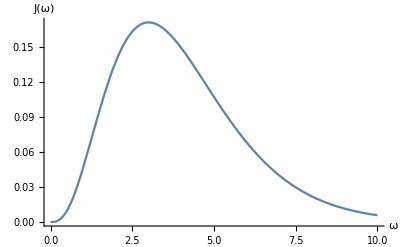

```mathematica
Plot[J[ω],{ω,0,10},PlotRange->All,AxesLabel->{"ω","J(ω)"}]
```

#### Reorganization energy

Reorganization energy refers to the energy required to reorganize the surrounding environment, typically the solvent and nearby molecules, in response to the movement of an electron or a charge

```mathematica
(*reorganization energy of one site*)
λ0=Integrate[J[ω]/ω,{ω,0,Infinity}]
```

0.254648

```mathematica
λ=Table[Sum[v[[a,n]]*v[[b,n]]v[[c,n]]*v[[d,n]],{n,1,Length[v[[2]]]}]λ0,{a,1,Length[v]},{b,1,Length[v]},{c,1,Length[v]},{d,1,Length[v]}];
```

#### Line shape functions

```mathematica
(*line shape function of one site*)
g0[t_]=Integrate[J[ω]/ω^2((1-Cos[ω t])Coth[β ω/2]+ⅈ (Sin[ω t]-ω t)),{ω,0,Infinity},Assumptions->t≥0];
```

```mathematica
dg0[t_]=D[g0[t],t];
```

```mathematica
(*bath correlation*)
ddg0[t_]=D[g0[t],{t,2}];
```

The bath correlation function is the time-correlation function of the spin-bath coupling. It is also known as the second derivative of the line shape function.

C_n(t) = ∫_0^ω ⅆω J (ω)[cos(ω t)coth(1/2 β ω)-i sin(ω t)] =(g̈)_n(t)

The generalized line shape function among each exciton state (eigenstate of the system Hamiltonian) can be defined as

g_αβγδ(t)=∑_n (c_n^α)^*(c_n^β(c_n^γ))^*c_n^δ g_n(t)

Each site (chromophore) couples to its local bath where the spectral density is related to the line shape function g_n(t). The delocalization among sites is induced by their dipole-dipole interaction. With loss of the generality, we can assume the bath is identical for each site g_n(t) = g_0(t).

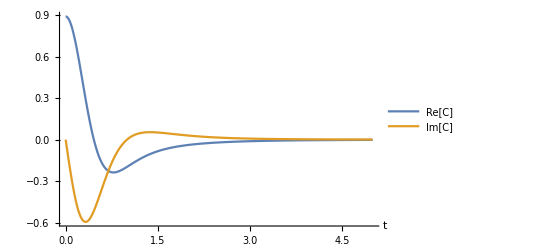

```mathematica
Plot[{Re[ddg0[t]],Im[ddg0[t]]},{t,0,5},PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["Re[C]",FontFamily->"Times New Roman"],Style["Im[C]",FontFamily->"Times New Roman"]}]
```

```mathematica
g[t_]=Table[Sum[v[[a,n]]*v[[b,n]]v[[c,n]]*v[[d,n]],{n,1,Length[v[[2]]]}]g0[t],{a,1,Length[v]},{b,1,Length[v]},{c,1,Length[v]},{d,1,Length[v]}];
```

```mathematica
dg[t_]=Table[Sum[v[[a,n]]*v[[b,n]]v[[c,n]]*v[[d,n]],{n,1,Length[v[[2]]]}]dg0[t],{a,1,Length[v]},{b,1,Length[v]},{c,1,Length[v]},{d,1,Length[v]}];
```

```mathematica
ddg[t_]=Table[Sum[v[[a,n]]*v[[b,n]]v[[c,n]]*v[[d,n]],{n,1,Length[v[[2]]]}]ddg0[t],{a,1,Length[v]},{b,1,Length[v]},{c,1,Length[v]},{d,1,Length[v]}];
```

#### Redfield theory

Redfield theory is used to describe the excitation energy transfer between the chromophores. A type of time-local Markovian quantum master equation.

The population transfer rate k_(α ← β) (t) is defined as

k_(α ← β) (t)=∑_n (|c_n^α|)^2(|c_n^β|)^2  ∫_0^t ⅆτ  2 Re[ (g̈)_n(τ)ⅇ^(-ⅈ ω_αβ τ)]

```mathematica
(*transfer rate *)
k0[t_,ω_]:=2NIntegrate[Re[ddg0[τ] Exp[-ⅈ ω τ]],{τ,0,t}]
```

```mathematica
k[t_]:=Table[Sum[v[[a,n]]*v[[a,n]]v[[b,n]]*v[[b,n]]k0[t,w[[a]]-w[[b]]],{n,1,Length[v]}](1-KroneckerDelta[a,b]),{a,1,Length[v]},{b,1,Length[v]}];
```

The pure dephasing rate γ_αβ^pd (t) is defined as

γ_αβ^pd (t)=∑_n ((|c_n^α|)^2-(|c_n^β|)^2  )^2 Re[ (ġ)_n(t)]

```mathematica
(*pure dephasing*)
Γ[t_]=Table[Sum[(v[[a,n]]*v[[a,n]]-v[[b,n]]*v[[b,n]])^2 Re[dg0[t]],{n,1,Length[v]}],{a,1,Length[v]},{b,1,Length[v]}];
```

The energy shift Δ_αβ (t) is defined as

Δ_αβ (t)=∑_n ((|c_n^α|)^4-(|c_n^β|)^4)Im[ (ġ)_n(t)]+∑_(ϵ≠α) ∑_n (|c_n^α|)^2(|c_n^ϵ|)^2 ∫_0^t ⅆτ  Im[ (g̈)_n(τ)ⅇ^(-ⅈ ω_ϵα τ)]-∑_(ϵ≠β) ∑_n (|c_n^α|)^2(|c_n^ϵ|)^2 ∫_0^t ⅆτ  Im[ (g̈)_n(τ)ⅇ^(-ⅈ ω_ϵβ τ)]

```mathematica
(*energy shift*)
δ[t_]:=Table[-Sum[((v[[a,n]]*v[[a,n]])^4-(v[[b,n]]*v[[b,n]])^4)Im[dg0[t]],{n,1,Length[v]}]-Sum[v[[a,n]]*v[[a,n]]v[[c,n]]*v[[c,n]](1-KroneckerDelta[c,a])NIntegrate[Im[ddg0[τ] Exp[-ⅈ (w[[c]]-w[[a]]) τ]],{τ,0,t}],{c,1,Length[v]},{n,1,Length[v]}]+Sum[v[[b,n]]*v[[b,n]]v[[c,n]]*v[[c,n]](1-KroneckerDelta[c,b])NIntegrate[Im[ddg0[τ] Exp[-ⅈ (w[[c]]-w[[b]]) τ]],{τ,0,t}],{c,1,Length[v]},{n,1,Length[v]}],{a,1,Length[v]},{b,1,Length[v]}];
```

#### Coherent Modified Redfield theory

In contrast to the Redfield theory, the diagonal part of the system-bath coupling in coherent modified Redfield theory is treated non-perturbatively. The Hamiltonian H_0 can be rewritten in a such way that the bath for each eigenbasis is displaced accordingly.

∑_α (ϵ_α+(Ĥ)_SB^αα)|α⟩⟨α|+H_B=∑_α (ϵ_α-λ_αααα+(ĥ)_αα)|α⟩⟨α|

where the displaced bath is defined by the displacement operator D_α (polaron transformation)

D_α^†H_BD_α= (ĥ)_αα

As the pure dephasing is induced by the diagonal part of the system-bath coupling, the bath reorganizations and pure dephasing are treated exactly in this formalism. This coherent modified Redfield theory (CMRT) allows the description of coherent excitation energy transfer dynamics as well as time-resolved spectroscopic signals:

(σ̇)_αβ(t)=(-iω_αβ+γ_αβ^pd (t))σ_αβ(t)+(∫_0^t ⅆτ Γ_δβαγ(τ)+(Γ^*)_γαβδ(τ)-∑_ϵ (Γ_αϵϵγ(τ)δ_βδ+(Γ^*)_βϵϵδ(τ)δ_αγ))σ_γδ(t)

where in CMRT, the system-bath coupling correlation function Γ_αβγδ(t) is defined as

Γ_αβγδ(t) = Tr_B[V_αβ V_γδ(-t)ⅇ^(-i (ĥ)_δδ t)ρ_b^eq ⅇ^(i (ĥ)_αα t)]

Thus, the system-bath coupling correlation function Γ_αβγδ(t) can be related to the line shape functions:

Γ_αβγδ(t) =[(g̈)_αβγδ(t)-((ġ)_αααβ(t)-(ġ)_γγαβ(t)+2 i λ_αααβ)((ġ)_ααγδ(t)-(ġ)_γγγδ(t)+2 i λ_ααγδ)]ⅇ^(-g_αααα-g_γγγγ+2 g_ααγγ- i (λ_αααα+λ_γγγγ-2 λ_ααγγ)t)ⅇ^(- i ω_γδ t)

```mathematica
(*transfer rate *)
```

```mathematica
A[t_]=Table[Exp[-ⅈ( w[[a]]+λ[[a,a,a,a]])t-g[t][[a,a,a,a]]],{a,1,Length[v]}];
F[t_]=Table[Exp[-ⅈ( w[[a]]-λ[[a,a,a,a]])t-g[t][[a,a,a,a]]*],{a,1,Length[v]}];
```

```mathematica
V[t_]=Table[Exp[2(Sum[v[[a,n]]*v[[a,n]]v[[b,n]]*v[[b,n]],{n,1,Length[v[[2]]]}]g0[t]+ⅈ λ[[a,a,b,b]]t)](ddg[t][[b,a,a,b]]-(dg[t][[a,a,a,b]]-dg[t][[b,b,a,b]]-2ⅈ λ[[b,b,a,b]])(dg[t][[a,a,b,a]]-dg[t][[b,b,b,a]]-2ⅈ λ[[b,b,b,a]])),{a,1,Length[v]},{b,1,Length[v]}];
```

```mathematica
kCM[t_]:=Table[2NIntegrate[Re[A[τ][[a]]V[τ][[a,b]]F[τ][[b]]*],{τ,0,t}](1-KroneckerDelta[a,b]),{a,1,Length[v]},{b,1,Length[v]}]
```

```mathematica
(*pure dephasing*)
```

```mathematica
ΓCM[t_]=Table[Re[dg[t][[a,a,a,a]]+dg[t][[b,b,b,b]]*-2Re[dg[t][[a,a,b,b]]]-ⅈ(λ[[a,a,a,a]]-λ[[b,b,b,b]])],{a,1,Length[v]},{b,1,Length[v]}];
```

```mathematica
(*energy shift*)
```

```mathematica
δCM[t_]:=Table[-Im[dg[t][[a,a,a,a]]+dg[t][[b,b,b,b]]*-2Re[dg[t][[a,a,b,b]]]-ⅈ(λ[[a,a,a,a]]-λ[[b,b,b,b]])]-NIntegrate[Sum[Im[A[τ][[c]]V[τ][[c,a]]F[τ][[a]]*](1-KroneckerDelta[a,c]),{c,1,Length[v]}],{τ,0,t}]+NIntegrate[Sum[Im[A[τ][[c]]V[τ][[c,b]]F[τ][[b]]*](1-KroneckerDelta[b,c]),{c,1,Length[v]}],{τ,0,t}],{a,1,Length[v]},{b,1,Length[v]}]
```

## Liouville evolution

### RT numerical computation

```mathematica
Clear[dt,Nt]
dt=0.05;(*time span*)
Nt=600;(*Propagation time = Nt dt*)
```

#### Initial condition

Here we assume the molecular dimer system at the beginning is at site |1⟩, which is a site with higher energy. In excition basis (eigenbasis), the system is primarily populated at exciton | β⟩, which is the exciton with high energy. Due to the dipole-dipole coupling between two sites. The initial coherence is not zero.

```mathematica
σsite[0]={{1,0},{0,0}};
```

```mathematica
σ[0]=Table[v[[m]]*.σsite[0].v[[n]],{m,1,Length[v]},{n,1,Length[v]}]
```

{{0.146447,-0.353553},{-0.353553,0.853553}}

#### Population transfer

```mathematica
(*Propagation matrix*)
```

```mathematica
Rpop[t_]:=DiagonalMatrix[Table[-Sum[k[t][[c,a]],{c,1,Length[v]}],{a,1,Length[v]}]]+k[t]
```

```mathematica
(*population evolution*)
```

```mathematica
Clear[σpop]
σpop[0]=Table[σ[0][[n,n]],{n,1,Length[v]}];(*initial condition Subscript[σ, pop][0] = (Subscript[σ, 11], Subscript[σ, 22])*)
Monitor[For[i=0,i≤Nt,i++,σpop[i+1]=(IdentityMatrix[Length[v]]+Rpop[i dt]dt).σpop[i]];,Row[{ProgressIndicator[i,{0,Nt}],i+1},""]]
Clear[i]
```

```mathematica
σpop11Data=Table[{n dt,σpop[n][[1]]},{n,0,Nt+1}]
```

{{0.,0.146447},{0.05,0.146447},{0.1,0.147231},{0.15,0.148785},{0.2,0.151077},{0.25,0.154063},{0.3,0.157687},{0.35,0.161887},{0.4,0.166596},{0.45,0.171745},{0.5,0.177268},{0.55,0.183099},{0.6,0.189178},{0.65,0.195447},{0.7,0.201856},{0.75,0.208358},{0.8,0.214914},{0.85,0.221489},{0.9,0.228053},{0.95,0.234581},{1.,0.241053},{1.05,0.247455},{1.1,0.253774},{1.15,0.260002},{1.2,0.266134},{1.25,0.272167},{1.3,0.278099},{1.35,0.283932},{1.4,0.289667},{1.45,0.295308},{1.5,0.300857},{1.55,0.306321},{1.6,0.311701},{1.65,0.317004},{1.7,0.322232},{1.75,0.327392},{1.8,0.332486},{1.85,0.337518},{1.9,0.342492},{1.95,0.34741},{2.,0.352277},{2.05,0.357094},{2.1,0.361863},{2.15,0.366588},{2.2,0.371268},{2.25,0.375906},{2.3,0.380502},{2.35,0.385059},{2.4,0.389576},{2.45,0.394054},{2.5,0.398494},{2.55,0.402896},{2.6,0.407261},{2.65,0.411589},{2.7,0.415879},{2.75,0.420132},{2.8,0.424348},{2.85,0.428526},{2.9,0.432668},{2.95,0.436772},{3.,0.440839},{3.05,0.444869},{3.1,0.448861},{3.15,0.452816},{3.2,0.456733},{3.25,0.460612},{3.3,0.464454},{3.35,0.468258},{3.4,0.472024},{3.45,0.475753},{3.5,0.479444},{3.55,0.483098},{3.6,0.486714},{3.65,0.490293},{3.7,0.493834},{3.75,0.497339},{3.8,0.500806},{3.85,0.504236},{3.9,0.50763},{3.95,0.510987},{4.,0.514308},{4.05,0.517593},{4.1,0.520842},{4.15,0.524056},{4.2,0.527234},{4.25,0.530377},{4.3,0.533485},{4.35,0.536559},{4.4,0.539598},{4.45,0.542603},{4.5,0.545575},{4.55,0.548513},{4.6,0.551418},{4.65,0.554291},{4.7,0.55713},{4.75,0.559938},{4.8,0.562713},{4.85,0.565458},{4.9,0.56817},{4.95,0.570852},{5.,0.573503},{5.05,0.576124},{5.1,0.578715},{5.15,0.581276},{5.2,0.583808},{5.25,0.586311},{5.3,0.588785},{5.35,0.591231},{5.4,0.593648},{5.45,0.596038},{5.5,0.5984},{5.55,0.600735},{5.6,0.603043},{5.65,0.605324},{5.7,0.607579},{5.75,0.609809},{5.8,0.612012},{5.85,0.61419},{5.9,0.616343},{5.95,0.618471},{6.,0.620575},{6.05,0.622654},{6.1,0.62471},{6.15,0.626742},{6.2,0.62875},{6.25,0.630736},{6.3,0.632698},{6.35,0.634638},{6.4,0.636556},{6.45,0.638452},{6.5,0.640326},{6.55,0.642178},{6.6,0.644009},{6.65,0.64582},{6.7,0.647609},{6.75,0.649378},{6.8,0.651127},{6.85,0.652857},{6.9,0.654566},{6.95,0.656256},{7.,0.657926},{7.05,0.659578},{7.1,0.661211},{7.15,0.662825},{7.2,0.664421},{7.25,0.665999},{7.3,0.667559},{7.35,0.669102},{7.4,0.670627},{7.45,0.672135},{7.5,0.673626},{7.55,0.6751},{7.6,0.676557},{7.65,0.677998},{7.7,0.679423},{7.75,0.680832},{7.8,0.682225},{7.85,0.683603},{7.9,0.684965},{7.95,0.686311},{8.,0.687643},{8.05,0.68896},{8.1,0.690262},{8.15,0.691549},{8.2,0.692822},{8.25,0.694081},{8.3,0.695326},{8.35,0.696557},{8.4,0.697774},{8.45,0.698977},{8.5,0.700168},{8.55,0.701344},{8.6,0.702508},{8.65,0.703659},{8.7,0.704796},{8.75,0.705922},{8.8,0.707034},{8.85,0.708134},{8.9,0.709222},{8.95,0.710298},{9.,0.711361},{9.05,0.712413},{9.1,0.713453},{9.15,0.714481},{9.2,0.715498},{9.25,0.716503},{9.3,0.717497},{9.35,0.71848},{9.4,0.719452},{9.45,0.720413},{9.5,0.721363},{9.55,0.722302},{9.6,0.723231},{9.65,0.72415},{9.7,0.725058},{9.75,0.725955},{9.8,0.726843},{9.85,0.727721},{9.9,0.728588},{9.95,0.729446},{10.,0.730294},{10.05,0.731133},{10.1,0.731962},{10.15,0.732781},{10.2,0.733592},{10.25,0.734393},{10.3,0.735185},{10.35,0.735968},{10.4,0.736742},{10.45,0.737507},{10.5,0.738264},{10.55,0.739012},{10.6,0.739751},{10.65,0.740482},{10.7,0.741205},{10.75,0.741919},{10.8,0.742626},{10.85,0.743324},{10.9,0.744014},{10.95,0.744697},{11.,0.745372},{11.05,0.746039},{11.1,0.746698},{11.15,0.74735},{11.2,0.747995},{11.25,0.748632},{11.3,0.749262},{11.35,0.749885},{11.4,0.7505},{11.45,0.751109},{11.5,0.751711},{11.55,0.752306},{11.6,0.752894},{11.65,0.753475},{11.7,0.75405},{11.75,0.754619},{11.8,0.755181},{11.85,0.755736},{11.9,0.756285},{11.95,0.756829},{12.,0.757365},{12.05,0.757896},{12.1,0.758421},{12.15,0.75894},{12.2,0.759453},{12.25,0.759961},{12.3,0.760462},{12.35,0.760958},{12.4,0.761449},{12.45,0.761934},{12.5,0.762413},{12.55,0.762887},{12.6,0.763356},{12.65,0.763819},{12.7,0.764277},{12.75,0.76473},{12.8,0.765178},{12.85,0.765621},{12.9,0.766059},{12.95,0.766492},{13.,0.766921},{13.05,0.767344},{13.1,0.767763},{13.15,0.768177},{13.2,0.768586},{13.25,0.768991},{13.3,0.769391},{13.35,0.769787},{13.4,0.770178},{13.45,0.770565},{13.5,0.770948},{13.55,0.771326},{13.6,0.7717},{13.65,0.77207},{13.7,0.772435},{13.75,0.772797},{13.8,0.773154},{13.85,0.773508},{13.9,0.773857},{13.95,0.774203},{14.,0.774545},{14.05,0.774883},{14.1,0.775217},{14.15,0.775547},{14.2,0.775873},{14.25,0.776196},{14.3,0.776515},{14.35,0.776831},{14.4,0.777143},{14.45,0.777452},{14.5,0.777757},{14.55,0.778058},{14.6,0.778356},{14.65,0.778651},{14.7,0.778943},{14.75,0.779231},{14.8,0.779516},{14.85,0.779797},{14.9,0.780076},{14.95,0.780351},{15.,0.780623},{15.05,0.780892},{15.1,0.781158},{15.15,0.781421},{15.2,0.781681},{15.25,0.781938},{15.3,0.782192},{15.35,0.782444},{15.4,0.782692},{15.45,0.782938},{15.5,0.78318},{15.55,0.78342},{15.6,0.783658},{15.65,0.783892},{15.7,0.784124},{15.75,0.784353},{15.8,0.78458},{15.85,0.784804},{15.9,0.785026},{15.95,0.785245},{16.,0.785461},{16.05,0.785675},{16.1,0.785887},{16.15,0.786096},{16.2,0.786303},{16.25,0.786508},{16.3,0.78671},{16.35,0.78691},{16.4,0.787107},{16.45,0.787303},{16.5,0.787496},{16.55,0.787687},{16.6,0.787876},{16.65,0.788063},{16.7,0.788247},{16.75,0.78843},{16.8,0.78861},{16.85,0.788789},{16.9,0.788965},{16.95,0.78914},{17.,0.789312},{17.05,0.789483},{17.1,0.789652},{17.15,0.789818},{17.2,0.789983},{17.25,0.790146},{17.3,0.790307},{17.35,0.790467},{17.4,0.790624},{17.45,0.79078},{17.5,0.790934},{17.55,0.791087},{17.6,0.791237},{17.65,0.791386},{17.7,0.791534},{17.75,0.791679},{17.8,0.791823},{17.85,0.791966},{17.9,0.792106},{17.95,0.792246},{18.,0.792383},{18.05,0.792519},{18.1,0.792654},{18.15,0.792787},{18.2,0.792919},{18.25,0.793049},{18.3,0.793177},{18.35,0.793304},{18.4,0.79343},{18.45,0.793555},{18.5,0.793678},{18.55,0.793799},{18.6,0.793919},{18.65,0.794038},{18.7,0.794156},{18.75,0.794272},{18.8,0.794387},{18.85,0.7945},{18.9,0.794612},{18.95,0.794723},{19.,0.794833},{19.05,0.794942},{19.1,0.795049},{19.15,0.795155},{19.2,0.79526},{19.25,0.795363},{19.3,0.795466},{19.35,0.795567},{19.4,0.795667},{19.45,0.795767},{19.5,0.795864},{19.55,0.795961},{19.6,0.796057},{19.65,0.796152},{19.7,0.796245},{19.75,0.796338},{19.8,0.796429},{19.85,0.796519},{19.9,0.796609},{19.95,0.796697},{20.,0.796784},{20.05,0.796871},{20.1,0.796956},{20.15,0.79704},{20.2,0.797124},{20.25,0.797206},{20.3,0.797288},{20.35,0.797369},{20.4,0.797448},{20.45,0.797527},{20.5,0.797605},{20.55,0.797682},{20.6,0.797758},{20.65,0.797833},{20.7,0.797908},{20.75,0.797981},{20.8,0.798054},{20.85,0.798126},{20.9,0.798197},{20.95,0.798268},{21.,0.798337},{21.05,0.798406},{21.1,0.798474},{21.15,0.798541},{21.2,0.798607},{21.25,0.798673},{21.3,0.798738},{21.35,0.798802},{21.4,0.798866},{21.45,0.798928},{21.5,0.79899},{21.55,0.799052},{21.6,0.799112},{21.65,0.799172},{21.7,0.799232},{21.75,0.79929},{21.8,0.799348},{21.85,0.799406},{21.9,0.799463},{21.95,0.799519},{22.,0.799574},{22.05,0.799629},{22.1,0.799683},{22.15,0.799737},{22.2,0.79979},{22.25,0.799842},{22.3,0.799894},{22.35,0.799945},{22.4,0.799996},{22.45,0.800046},{22.5,0.800095},{22.55,0.800144},{22.6,0.800193},{22.65,0.800241},{22.7,0.800288},{22.75,0.800335},{22.8,0.800381},{22.85,0.800427},{22.9,0.800472},{22.95,0.800517},{23.,0.800561},{23.05,0.800605},{23.1,0.800648},{23.15,0.800691},{23.2,0.800733},{23.25,0.800775},{23.3,0.800816},{23.35,0.800857},{23.4,0.800898},{23.45,0.800938},{23.5,0.800977},{23.55,0.801016},{23.6,0.801055},{23.65,0.801093},{23.7,0.801131},{23.75,0.801168},{23.8,0.801205},{23.85,0.801241},{23.9,0.801277},{23.95,0.801313},{24.,0.801348},{24.05,0.801383},{24.1,0.801417},{24.15,0.801451},{24.2,0.801485},{24.25,0.801518},{24.3,0.801551},{24.35,0.801584},{24.4,0.801616},{24.45,0.801648},{24.5,0.801679},{24.55,0.80171},{24.6,0.801741},{24.65,0.801771},{24.7,0.801801},{24.75,0.801831},{24.8,0.80186},{24.85,0.801889},{24.9,0.801918},{24.95,0.801946},{25.,0.801974},{25.05,0.802002},{25.1,0.802029},{25.15,0.802056},{25.2,0.802083},{25.25,0.80211},{25.3,0.802136},{25.35,0.802162},{25.4,0.802187},{25.45,0.802213},{25.5,0.802238},{25.55,0.802262},{25.6,0.802287},{25.65,0.802311},{25.7,0.802335},{25.75,0.802358},{25.8,0.802382},{25.85,0.802405},{25.9,0.802428},{25.95,0.80245},{26.,0.802473},{26.05,0.802495},{26.1,0.802516},{26.15,0.802538},{26.2,0.802559},{26.25,0.802581},{26.3,0.802601},{26.35,0.802622},{26.4,0.802642},{26.45,0.802663},{26.5,0.802683},{26.55,0.802702},{26.6,0.802722},{26.65,0.802741},{26.7,0.80276},{26.75,0.802779},{26.8,0.802798},{26.85,0.802816},{26.9,0.802834},{26.95,0.802852},{27.,0.80287},{27.05,0.802888},{27.1,0.802905},{27.15,0.802922},{27.2,0.802939},{27.25,0.802956},{27.3,0.802973},{27.35,0.802989},{27.4,0.803006},{27.45,0.803022},{27.5,0.803038},{27.55,0.803054},{27.6,0.803069},{27.65,0.803085},{27.7,0.8031},{27.75,0.803115},{27.8,0.80313},{27.85,0.803144},{27.9,0.803159},{27.95,0.803173},{28.,0.803188},{28.05,0.803202},{28.1,0.803215},{28.15,0.803229},{28.2,0.803243},{28.25,0.803256},{28.3,0.803269},{28.35,0.803283},{28.4,0.803296},{28.45,0.803308},{28.5,0.803321},{28.55,0.803334},{28.6,0.803346},{28.65,0.803358},{28.7,0.80337},{28.75,0.803382},{28.8,0.803394},{28.85,0.803406},{28.9,0.803417},{28.95,0.803429},{29.,0.80344},{29.05,0.803451},{29.1,0.803462},{29.15,0.803473},{29.2,0.803484},{29.25,0.803495},{29.3,0.803505},{29.35,0.803516},{29.4,0.803526},{29.45,0.803536},{29.5,0.803546},{29.55,0.803556},{29.6,0.803566},{29.65,0.803576},{29.7,0.803585},{29.75,0.803595},{29.8,0.803604},{29.85,0.803614},{29.9,0.803623},{29.95,0.803632},{30.,0.803641},{30.05,0.80365}}

```mathematica
σpop22Data=Table[{n dt,σpop[n][[2]]},{n,0,Nt+1}]
```

{{0.,0.853553},{0.05,0.853553},{0.1,0.852769},{0.15,0.851215},{0.2,0.848923},{0.25,0.845937},{0.3,0.842313},{0.35,0.838113},{0.4,0.833404},{0.45,0.828255},{0.5,0.822732},{0.55,0.816901},{0.6,0.810822},{0.65,0.804553},{0.7,0.798144},{0.75,0.791642},{0.8,0.785086},{0.85,0.778511},{0.9,0.771947},{0.95,0.765419},{1.,0.758947},{1.05,0.752545},{1.1,0.746226},{1.15,0.739998},{1.2,0.733866},{1.25,0.727833},{1.3,0.721901},{1.35,0.716068},{1.4,0.710333},{1.45,0.704692},{1.5,0.699143},{1.55,0.693679},{1.6,0.688299},{1.65,0.682996},{1.7,0.677768},{1.75,0.672608},{1.8,0.667514},{1.85,0.662482},{1.9,0.657508},{1.95,0.65259},{2.,0.647723},{2.05,0.642906},{2.1,0.638137},{2.15,0.633412},{2.2,0.628732},{2.25,0.624094},{2.3,0.619498},{2.35,0.614941},{2.4,0.610424},{2.45,0.605946},{2.5,0.601506},{2.55,0.597104},{2.6,0.592739},{2.65,0.588411},{2.7,0.584121},{2.75,0.579868},{2.8,0.575652},{2.85,0.571474},{2.9,0.567332},{2.95,0.563228},{3.,0.559161},{3.05,0.555131},{3.1,0.551139},{3.15,0.547184},{3.2,0.543267},{3.25,0.539388},{3.3,0.535546},{3.35,0.531742},{3.4,0.527976},{3.45,0.524247},{3.5,0.520556},{3.55,0.516902},{3.6,0.513286},{3.65,0.509707},{3.7,0.506166},{3.75,0.502661},{3.8,0.499194},{3.85,0.495764},{3.9,0.49237},{3.95,0.489013},{4.,0.485692},{4.05,0.482407},{4.1,0.479158},{4.15,0.475944},{4.2,0.472766},{4.25,0.469623},{4.3,0.466515},{4.35,0.463441},{4.4,0.460402},{4.45,0.457397},{4.5,0.454425},{4.55,0.451487},{4.6,0.448582},{4.65,0.445709},{4.7,0.44287},{4.75,0.440062},{4.8,0.437287},{4.85,0.434542},{4.9,0.43183},{4.95,0.429148},{5.,0.426497},{5.05,0.423876},{5.1,0.421285},{5.15,0.418724},{5.2,0.416192},{5.25,0.413689},{5.3,0.411215},{5.35,0.408769},{5.4,0.406352},{5.45,0.403962},{5.5,0.4016},{5.55,0.399265},{5.6,0.396957},{5.65,0.394676},{5.7,0.392421},{5.75,0.390191},{5.8,0.387988},{5.85,0.38581},{5.9,0.383657},{5.95,0.381529},{6.,0.379425},{6.05,0.377346},{6.1,0.37529},{6.15,0.373258},{6.2,0.37125},{6.25,0.369264},{6.3,0.367302},{6.35,0.365362},{6.4,0.363444},{6.45,0.361548},{6.5,0.359674},{6.55,0.357822},{6.6,0.355991},{6.65,0.35418},{6.7,0.352391},{6.75,0.350622},{6.8,0.348873},{6.85,0.347143},{6.9,0.345434},{6.95,0.343744},{7.,0.342074},{7.05,0.340422},{7.1,0.338789},{7.15,0.337175},{7.2,0.335579},{7.25,0.334001},{7.3,0.332441},{7.35,0.330898},{7.4,0.329373},{7.45,0.327865},{7.5,0.326374},{7.55,0.3249},{7.6,0.323443},{7.65,0.322002},{7.7,0.320577},{7.75,0.319168},{7.8,0.317775},{7.85,0.316397},{7.9,0.315035},{7.95,0.313689},{8.,0.312357},{8.05,0.31104},{8.1,0.309738},{8.15,0.308451},{8.2,0.307178},{8.25,0.305919},{8.3,0.304674},{8.35,0.303443},{8.4,0.302226},{8.45,0.301023},{8.5,0.299832},{8.55,0.298656},{8.6,0.297492},{8.65,0.296341},{8.7,0.295204},{8.75,0.294078},{8.8,0.292966},{8.85,0.291866},{8.9,0.290778},{8.95,0.289702},{9.,0.288639},{9.05,0.287587},{9.1,0.286547},{9.15,0.285519},{9.2,0.284502},{9.25,0.283497},{9.3,0.282503},{9.35,0.28152},{9.4,0.280548},{9.45,0.279587},{9.5,0.278637},{9.55,0.277698},{9.6,0.276769},{9.65,0.27585},{9.7,0.274942},{9.75,0.274045},{9.8,0.273157},{9.85,0.272279},{9.9,0.271412},{9.95,0.270554},{10.,0.269706},{10.05,0.268867},{10.1,0.268038},{10.15,0.267219},{10.2,0.266408},{10.25,0.265607},{10.3,0.264815},{10.35,0.264032},{10.4,0.263258},{10.45,0.262493},{10.5,0.261736},{10.55,0.260988},{10.6,0.260249},{10.65,0.259518},{10.7,0.258795},{10.75,0.258081},{10.8,0.257374},{10.85,0.256676},{10.9,0.255986},{10.95,0.255303},{11.,0.254628},{11.05,0.253961},{11.1,0.253302},{11.15,0.25265},{11.2,0.252005},{11.25,0.251368},{11.3,0.250738},{11.35,0.250115},{11.4,0.2495},{11.45,0.248891},{11.5,0.248289},{11.55,0.247694},{11.6,0.247106},{11.65,0.246525},{11.7,0.24595},{11.75,0.245381},{11.8,0.244819},{11.85,0.244264},{11.9,0.243715},{11.95,0.243171},{12.,0.242635},{12.05,0.242104},{12.1,0.241579},{12.15,0.24106},{12.2,0.240547},{12.25,0.240039},{12.3,0.239538},{12.35,0.239042},{12.4,0.238551},{12.45,0.238066},{12.5,0.237587},{12.55,0.237113},{12.6,0.236644},{12.65,0.236181},{12.7,0.235723},{12.75,0.23527},{12.8,0.234822},{12.85,0.234379},{12.9,0.233941},{12.95,0.233508},{13.,0.233079},{13.05,0.232656},{13.1,0.232237},{13.15,0.231823},{13.2,0.231414},{13.25,0.231009},{13.3,0.230609},{13.35,0.230213},{13.4,0.229822},{13.45,0.229435},{13.5,0.229052},{13.55,0.228674},{13.6,0.2283},{13.65,0.22793},{13.7,0.227565},{13.75,0.227203},{13.8,0.226846},{13.85,0.226492},{13.9,0.226143},{13.95,0.225797},{14.,0.225455},{14.05,0.225117},{14.1,0.224783},{14.15,0.224453},{14.2,0.224127},{14.25,0.223804},{14.3,0.223485},{14.35,0.223169},{14.4,0.222857},{14.45,0.222548},{14.5,0.222243},{14.55,0.221942},{14.6,0.221644},{14.65,0.221349},{14.7,0.221057},{14.75,0.220769},{14.8,0.220484},{14.85,0.220203},{14.9,0.219924},{14.95,0.219649},{15.,0.219377},{15.05,0.219108},{15.1,0.218842},{15.15,0.218579},{15.2,0.218319},{15.25,0.218062},{15.3,0.217808},{15.35,0.217556},{15.4,0.217308},{15.45,0.217062},{15.5,0.21682},{15.55,0.21658},{15.6,0.216342},{15.65,0.216108},{15.7,0.215876},{15.75,0.215647},{15.8,0.21542},{15.85,0.215196},{15.9,0.214974},{15.95,0.214755},{16.,0.214539},{16.05,0.214325},{16.1,0.214113},{16.15,0.213904},{16.2,0.213697},{16.25,0.213492},{16.3,0.21329},{16.35,0.21309},{16.4,0.212893},{16.45,0.212697},{16.5,0.212504},{16.55,0.212313},{16.6,0.212124},{16.65,0.211937},{16.7,0.211753},{16.75,0.21157},{16.8,0.21139},{16.85,0.211211},{16.9,0.211035},{16.95,0.21086},{17.,0.210688},{17.05,0.210517},{17.1,0.210348},{17.15,0.210182},{17.2,0.210017},{17.25,0.209854},{17.3,0.209693},{17.35,0.209533},{17.4,0.209376},{17.45,0.20922},{17.5,0.209066},{17.55,0.208913},{17.6,0.208763},{17.65,0.208614},{17.7,0.208466},{17.75,0.208321},{17.8,0.208177},{17.85,0.208034},{17.9,0.207894},{17.95,0.207754},{18.,0.207617},{18.05,0.207481},{18.1,0.207346},{18.15,0.207213},{18.2,0.207081},{18.25,0.206951},{18.3,0.206823},{18.35,0.206696},{18.4,0.20657},{18.45,0.206445},{18.5,0.206322},{18.55,0.206201},{18.6,0.206081},{18.65,0.205962},{18.7,0.205844},{18.75,0.205728},{18.8,0.205613},{18.85,0.2055},{18.9,0.205388},{18.95,0.205277},{19.,0.205167},{19.05,0.205058},{19.1,0.204951},{19.15,0.204845},{19.2,0.20474},{19.25,0.204637},{19.3,0.204534},{19.35,0.204433},{19.4,0.204333},{19.45,0.204233},{19.5,0.204136},{19.55,0.204039},{19.6,0.203943},{19.65,0.203848},{19.7,0.203755},{19.75,0.203662},{19.8,0.203571},{19.85,0.203481},{19.9,0.203391},{19.95,0.203303},{20.,0.203216},{20.05,0.203129},{20.1,0.203044},{20.15,0.20296},{20.2,0.202876},{20.25,0.202794},{20.3,0.202712},{20.35,0.202631},{20.4,0.202552},{20.45,0.202473},{20.5,0.202395},{20.55,0.202318},{20.6,0.202242},{20.65,0.202167},{20.7,0.202092},{20.75,0.202019},{20.8,0.201946},{20.85,0.201874},{20.9,0.201803},{20.95,0.201732},{21.,0.201663},{21.05,0.201594},{21.1,0.201526},{21.15,0.201459},{21.2,0.201393},{21.25,0.201327},{21.3,0.201262},{21.35,0.201198},{21.4,0.201134},{21.45,0.201072},{21.5,0.20101},{21.55,0.200948},{21.6,0.200888},{21.65,0.200828},{21.7,0.200768},{21.75,0.20071},{21.8,0.200652},{21.85,0.200594},{21.9,0.200537},{21.95,0.200481},{22.,0.200426},{22.05,0.200371},{22.1,0.200317},{22.15,0.200263},{22.2,0.20021},{22.25,0.200158},{22.3,0.200106},{22.35,0.200055},{22.4,0.200004},{22.45,0.199954},{22.5,0.199905},{22.55,0.199856},{22.6,0.199807},{22.65,0.199759},{22.7,0.199712},{22.75,0.199665},{22.8,0.199619},{22.85,0.199573},{22.9,0.199528},{22.95,0.199483},{23.,0.199439},{23.05,0.199395},{23.1,0.199352},{23.15,0.199309},{23.2,0.199267},{23.25,0.199225},{23.3,0.199184},{23.35,0.199143},{23.4,0.199102},{23.45,0.199062},{23.5,0.199023},{23.55,0.198984},{23.6,0.198945},{23.65,0.198907},{23.7,0.198869},{23.75,0.198832},{23.8,0.198795},{23.85,0.198759},{23.9,0.198723},{23.95,0.198687},{24.,0.198652},{24.05,0.198617},{24.1,0.198583},{24.15,0.198549},{24.2,0.198515},{24.25,0.198482},{24.3,0.198449},{24.35,0.198416},{24.4,0.198384},{24.45,0.198352},{24.5,0.198321},{24.55,0.19829},{24.6,0.198259},{24.65,0.198229},{24.7,0.198199},{24.75,0.198169},{24.8,0.19814},{24.85,0.198111},{24.9,0.198082},{24.95,0.198054},{25.,0.198026},{25.05,0.197998},{25.1,0.197971},{25.15,0.197944},{25.2,0.197917},{25.25,0.19789},{25.3,0.197864},{25.35,0.197838},{25.4,0.197813},{25.45,0.197787},{25.5,0.197762},{25.55,0.197738},{25.6,0.197713},{25.65,0.197689},{25.7,0.197665},{25.75,0.197642},{25.8,0.197618},{25.85,0.197595},{25.9,0.197572},{25.95,0.19755},{26.,0.197527},{26.05,0.197505},{26.1,0.197484},{26.15,0.197462},{26.2,0.197441},{26.25,0.197419},{26.3,0.197399},{26.35,0.197378},{26.4,0.197358},{26.45,0.197337},{26.5,0.197317},{26.55,0.197298},{26.6,0.197278},{26.65,0.197259},{26.7,0.19724},{26.75,0.197221},{26.8,0.197202},{26.85,0.197184},{26.9,0.197166},{26.95,0.197148},{27.,0.19713},{27.05,0.197112},{27.1,0.197095},{27.15,0.197078},{27.2,0.197061},{27.25,0.197044},{27.3,0.197027},{27.35,0.197011},{27.4,0.196994},{27.45,0.196978},{27.5,0.196962},{27.55,0.196946},{27.6,0.196931},{27.65,0.196915},{27.7,0.1969},{27.75,0.196885},{27.8,0.19687},{27.85,0.196856},{27.9,0.196841},{27.95,0.196827},{28.,0.196812},{28.05,0.196798},{28.1,0.196785},{28.15,0.196771},{28.2,0.196757},{28.25,0.196744},{28.3,0.196731},{28.35,0.196717},{28.4,0.196704},{28.45,0.196692},{28.5,0.196679},{28.55,0.196666},{28.6,0.196654},{28.65,0.196642},{28.7,0.19663},{28.75,0.196618},{28.8,0.196606},{28.85,0.196594},{28.9,0.196583},{28.95,0.196571},{29.,0.19656},{29.05,0.196549},{29.1,0.196538},{29.15,0.196527},{29.2,0.196516},{29.25,0.196505},{29.3,0.196495},{29.35,0.196484},{29.4,0.196474},{29.45,0.196464},{29.5,0.196454},{29.55,0.196444},{29.6,0.196434},{29.65,0.196424},{29.7,0.196415},{29.75,0.196405},{29.8,0.196396},{29.85,0.196386},{29.9,0.196377},{29.95,0.196368},{30.,0.196359},{30.05,0.19635}}

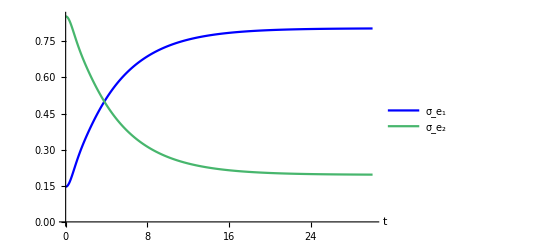

```mathematica
ListPlot[{σpop11Data,σpop22Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["σ_e_1",FontFamily->"Times New Roman"],Style["σ_e_2",FontFamily->"Times New Roman"]}]
```

#### Coherence dephasing

```mathematica
(*including transfer rate, pure dephasing, energy eigenvalue, energy shift*)
```

```mathematica
Rcoh[t_]:=DiagonalMatrix[Drop[Flatten[-Γ[t]+Table[-ⅈ(w[[a]]-w[[b]]),{a,1,Length[v]},{b,1,Length[v]}]+Table[ⅈ δ[t][[a,b]],{a,1,Length[v]},{b,1,Length[v]}]+Table[-1/2 Sum[k[t][[c,a]]+k[t][[c,b]],{c,1,Length[v]}],{a,1,Length[v]},{b,1,Length[v]}]],{1,Length[v]^2,Length[v]+1}]]
```

```mathematica
(*coherence evolution*)
```

```mathematica
Clear[σcoh]
σcoh[0]=Drop[Flatten[ReplacePart[σ[0],Table[{n,n},{n,1,Length[v]}]->0]],{1,Length[v]^2,Length[v]+1}];(*initial condition Subscript[σ, coh][0] = (Subscript[σ, 12], Subscript[σ, 21])*)
Monitor[For[i=0,i≤Nt,i++,σcoh[i+1]=(IdentityMatrix[Length[v]]+Rcoh[i dt]dt).σcoh[i]];,Row[{ProgressIndicator[i,{0,Nt}],i+1},""]]
Clear[i]
```

```mathematica
Reσcoh12Data=Table[{n dt,Re[σcoh[n][[1]]]},{n,0,Nt+1}]
```

{{0.,-0.353553},{0.05,-0.353553},{0.1,-0.350614},{0.15,-0.344807},{0.2,-0.336294},{0.25,-0.325315},{0.3,-0.312155},{0.35,-0.297126},{0.4,-0.280542},{0.45,-0.262699},{0.5,-0.243864},{0.55,-0.224268},{0.6,-0.204108},{0.65,-0.183547},{0.7,-0.162719},{0.75,-0.141734},{0.8,-0.120686},{0.85,-0.099655},{0.9,-0.078713},{0.95,-0.0579256},{1.,-0.0373552},{1.05,-0.0170626},{1.1,0.00289242},{1.15,0.0224503},{1.2,0.0415516},{1.25,0.0601373},{1.3,0.0781484},{1.35,0.0955272},{1.4,0.112217},{1.45,0.128162},{1.5,0.14331},{1.55,0.15761},{1.6,0.171013},{1.65,0.183476},{1.7,0.194957},{1.75,0.205417},{1.8,0.214825},{1.85,0.22315},{1.9,0.230368},{1.95,0.236459},{2.,0.241406},{2.05,0.2452},{2.1,0.247834},{2.15,0.249308},{2.2,0.249625},{2.25,0.248796},{2.3,0.246833},{2.35,0.243755},{2.4,0.239586},{2.45,0.234354},{2.5,0.228091},{2.55,0.220835},{2.6,0.212626},{2.65,0.203509},{2.7,0.193533},{2.75,0.18275},{2.8,0.171215},{2.85,0.158988},{2.9,0.146128},{2.95,0.1327},{3.,0.118769},{3.05,0.104403},{3.1,0.0896711},{3.15,0.0746426},{3.2,0.0593889},{3.25,0.0439817},{3.3,0.0284924},{3.35,0.0129929},{3.4,-0.00244581},{3.45,-0.0177533},{3.5,-0.0328604},{3.55,-0.047699},{3.6,-0.0622032},{3.65,-0.0763085},{3.7,-0.0899533},{3.75,-0.103078},{3.8,-0.115626},{3.85,-0.127544},{3.9,-0.138781},{3.95,-0.149291},{4.,-0.159031},{4.05,-0.167961},{4.1,-0.176045},{4.15,-0.183254},{4.2,-0.189559},{4.25,-0.194939},{4.3,-0.199374},{4.35,-0.202852},{4.4,-0.205363},{4.45,-0.206902},{4.5,-0.20747},{4.55,-0.20707},{4.6,-0.205711},{4.65,-0.203407},{4.7,-0.200174},{4.75,-0.196035},{4.8,-0.191014},{4.85,-0.185142},{4.9,-0.178451},{4.95,-0.170979},{5.,-0.162765},{5.05,-0.153852},{5.1,-0.144287},{5.15,-0.134119},{5.2,-0.123399},{5.25,-0.112181},{5.3,-0.100519},{5.35,-0.0884718},{5.4,-0.076097},{5.45,-0.0634546},{5.5,-0.050605},{5.55,-0.0376092},{5.6,-0.0245284},{5.65,-0.0114241},{5.7,0.00164305},{5.75,0.0146125},{5.8,0.0274249},{5.85,0.0400218},{5.9,0.0523463},{5.95,0.064343},{6.,0.0759586},{6.05,0.0871418},{6.1,0.0978436},{6.15,0.108018},{6.2,0.117621},{6.25,0.126612},{6.3,0.134953},{6.35,0.142611},{6.4,0.149554},{6.45,0.155755},{6.5,0.16119},{6.55,0.16584},{6.6,0.169688},{6.65,0.172721},{6.7,0.174931},{6.75,0.176314},{6.8,0.176869},{6.85,0.176599},{6.9,0.17551},{6.95,0.173613},{7.,0.170923},{7.05,0.167457},{7.1,0.163236},{7.15,0.158287},{7.2,0.152635},{7.25,0.146313},{7.3,0.139354},{7.35,0.131795},{7.4,0.123675},{7.45,0.115036},{7.5,0.10592},{7.55,0.0963746},{7.6,0.0864458},{7.65,0.0761826},{7.7,0.0656349},{7.75,0.0548536},{7.8,0.0438903},{7.85,0.0327973},{7.9,0.0216268},{7.95,0.0104313},{8.,-0.000737145},{8.05,-0.0118267},{8.1,-0.0227866},{8.15,-0.0335666},{8.2,-0.044118},{8.25,-0.0543932},{8.3,-0.0643466},{8.35,-0.0739338},{8.4,-0.0831131},{8.45,-0.0918443},{8.5,-0.10009},{8.55,-0.107815},{8.6,-0.114988},{8.65,-0.121577},{8.7,-0.127558},{8.75,-0.132906},{8.8,-0.1376},{8.85,-0.141624},{8.9,-0.144962},{8.95,-0.147604},{9.,-0.149543},{9.05,-0.150775},{9.1,-0.151297},{9.15,-0.151113},{9.2,-0.150228},{9.25,-0.148651},{9.3,-0.146394},{9.35,-0.143472},{9.4,-0.139902},{9.45,-0.135707},{9.5,-0.13091},{9.55,-0.125536},{9.6,-0.119615},{9.65,-0.113178},{9.7,-0.106259},{9.75,-0.098892},{9.8,-0.091115},{9.85,-0.0829667},{9.9,-0.0744876},{9.95,-0.0657192},{10.,-0.0567041},{10.05,-0.047486},{10.1,-0.038109},{10.15,-0.0286177},{10.2,-0.0190569},{10.25,-0.0094716},{10.3,0.000093564},{10.35,0.00959429},{10.4,0.0189869},{10.45,0.0282284},{10.5,0.037277},{10.55,0.0460918},{10.6,0.0546336},{10.65,0.0628644},{10.7,0.070748},{10.75,0.0782503},{10.8,0.0853389},{10.85,0.0919836},{10.9,0.0981565},{10.95,0.103832},{11.,0.108987},{11.05,0.113602},{11.1,0.117658},{11.15,0.12114},{11.2,0.124036},{11.25,0.126336},{11.3,0.128034},{11.35,0.129126},{11.4,0.129611},{11.45,0.12949},{11.5,0.128769},{11.55,0.127454},{11.6,0.125556},{11.65,0.123087},{11.7,0.120063},{11.75,0.116501},{11.8,0.112421},{11.85,0.107847},{11.9,0.102802},{11.95,0.0973132},{12.,0.0914089},{12.05,0.0851193},{12.1,0.0784763},{12.15,0.0715131},{12.2,0.064264},{12.25,0.0567648},{12.3,0.049052},{12.35,0.0411627},{12.4,0.0331349},{12.45,0.0250067},{12.5,0.0168166},{12.55,0.008603},{12.6,0.000404258},{12.65,-0.00774164},{12.7,-0.0157972},{12.75,-0.0237256},{12.8,-0.0314909},{12.85,-0.0390581},{12.9,-0.0463933},{12.95,-0.053464},{13.,-0.0602391},{13.05,-0.0666892},{13.1,-0.0727863},{13.15,-0.0785047},{13.2,-0.0838201},{13.25,-0.0887107},{13.3,-0.0931565},{13.35,-0.0971398},{13.4,-0.100645},{13.45,-0.10366},{13.5,-0.106172},{13.55,-0.108175},{13.6,-0.109662},{13.65,-0.110629},{13.7,-0.111076},{13.75,-0.111004},{13.8,-0.110416},{13.85,-0.10932},{13.9,-0.107723},{13.95,-0.105636},{14.,-0.103072},{14.05,-0.100046},{14.1,-0.0965761},{14.15,-0.0926803},{14.2,-0.0883798},{14.25,-0.0836973},{14.3,-0.0786572},{14.35,-0.0732853},{14.4,-0.0676086},{14.45,-0.0616557},{14.5,-0.0554559},{14.55,-0.0490399},{14.6,-0.0424387},{14.65,-0.0356844},{14.7,-0.0288093},{14.75,-0.0218461},{14.8,-0.0148278},{14.85,-0.00778743},{14.9,-0.000757759},{14.95,0.00622859},{15.,0.0131395},{15.05,0.0199432},{15.1,0.026609},{15.15,0.0331068},{15.2,0.0394075},{15.25,0.045483},{15.3,0.0513068},{15.35,0.0568535},{15.4,0.062099},{15.45,0.0670211},{15.5,0.071599},{15.55,0.0758138},{15.6,0.0796483},{15.65,0.0830871},{15.7,0.0861171},{15.75,0.0887267},{15.8,0.0909068},{15.85,0.0926499},{15.9,0.093951},{15.95,0.094807},{16.,0.0952167},{16.05,0.0951814},{16.1,0.094704},{16.15,0.0937899},{16.2,0.0924461},{16.25,0.0906817},{16.3,0.0885078},{16.35,0.0859371},{16.4,0.0829843},{16.45,0.0796656},{16.5,0.0759989},{16.55,0.0720034},{16.6,0.0677001},{16.65,0.0631109},{16.7,0.058259},{16.75,0.0531688},{16.8,0.0478654},{16.85,0.042375},{16.9,0.0367242},{16.95,0.0309405},{17.,0.0250515},{17.05,0.0190853},{17.1,0.0130702},{17.15,0.0070344},{17.2,0.00100611},{17.25,-0.00498672},{17.3,-0.0109165},{17.35,-0.016756},{17.4,-0.0224789},{17.45,-0.0280592},{17.5,-0.0334719},{17.55,-0.0386932},{17.6,-0.0436999},{17.65,-0.0484702},{17.7,-0.0529836},{17.75,-0.0572208},{17.8,-0.0611639},{17.85,-0.0647966},{17.9,-0.068104},{17.95,-0.0710731},{18.,-0.0736921},{18.05,-0.0759513},{18.1,-0.0778427},{18.15,-0.0793597},{18.2,-0.080498},{18.25,-0.0812547},{18.3,-0.0816288},{18.35,-0.0816212},{18.4,-0.0812344},{18.45,-0.0804728},{18.5,-0.0793424},{18.55,-0.0778508},{18.6,-0.0760075},{18.65,-0.0738233},{18.7,-0.0713107},{18.75,-0.0684834},{18.8,-0.0653568},{18.85,-0.0619474},{18.9,-0.0582728},{18.95,-0.054352},{19.,-0.0502047},{19.05,-0.0458518},{19.1,-0.0413148},{19.15,-0.0366161},{19.2,-0.0317785},{19.25,-0.0268254},{19.3,-0.0217807},{19.35,-0.0166683},{19.4,-0.0115126},{19.45,-0.00633763},{19.5,-0.00116768},{19.55,0.0039733},{19.6,0.0090616},{19.65,0.0140739},{19.7,0.0189875},{19.75,0.0237802},{19.8,0.0284305},{19.85,0.0329178},{19.9,0.0372223},{19.95,0.0413252},{20.,0.0452088},{20.05,0.0488565},{20.1,0.052253},{20.15,0.055384},{20.2,0.058237},{20.25,0.0608004},{20.3,0.0630642},{20.35,0.06502},{20.4,0.0666606},{20.45,0.0679807},{20.5,0.0689761},{20.55,0.0696444},{20.6,0.0699848},{20.65,0.0699977},{20.7,0.0696853},{20.75,0.0690512},{20.8,0.0681005},{20.85,0.0668397},{20.9,0.0652768},{20.95,0.063421},{21.,0.061283},{21.05,0.0588744},{21.1,0.0562082},{21.15,0.0532987},{21.2,0.0501609},{21.25,0.046811},{21.3,0.0432658},{21.35,0.0395432},{21.4,0.0356617},{21.45,0.0316403},{21.5,0.0274987},{21.55,0.0232568},{21.6,0.0189351},{21.65,0.0145542},{21.7,0.0101348},{21.75,0.00569774},{21.8,0.00126372},{21.85,-0.00314668},{21.9,-0.00751311},{21.95,-0.0118156},{22.,-0.0160346},{22.05,-0.0201509},{22.1,-0.0241463},{22.15,-0.028003},{22.2,-0.0317038},{22.25,-0.0352328},{22.3,-0.0385745},{22.35,-0.0417149},{22.4,-0.0446405},{22.45,-0.0473392},{22.5,-0.0498001},{22.55,-0.0520132},{22.6,-0.05397},{22.65,-0.0556629},{22.7,-0.057086},{22.75,-0.0582345},{22.8,-0.0591047},{22.85,-0.0596945},{22.9,-0.060003},{22.95,-0.0600307},{23.,-0.0597794},{23.05,-0.0592519},{23.1,-0.0584527},{23.15,-0.0573872},{23.2,-0.0560622},{23.25,-0.0544855},{23.3,-0.0526662},{23.35,-0.0506143},{23.4,-0.0483409},{23.45,-0.045858},{23.5,-0.0431785},{23.55,-0.0403163},{23.6,-0.0372858},{23.65,-0.0341022},{23.7,-0.0307814},{23.75,-0.0273396},{23.8,-0.0237937},{23.85,-0.0201609},{23.9,-0.0164585},{23.95,-0.0127043},{24.,-0.00891606},{24.05,-0.00511158},{24.1,-0.00130865},{24.15,0.00247506},{24.2,0.0062221},{24.25,0.00991531},{24.3,0.0135379},{24.35,0.0170735},{24.4,0.0205062},{24.45,0.0238209},{24.5,0.0270028},{24.55,0.0300381},{24.6,0.0329137},{24.65,0.0356172},{24.7,0.0381372},{24.75,0.0404633},{24.8,0.0425859},{24.85,0.0444966},{24.9,0.0461878},{24.95,0.0476532},{25.,0.0488874},{25.05,0.0498863},{25.1,0.0506468},{25.15,0.0511669},{25.2,0.0514458},{25.25,0.0514839},{25.3,0.0512825},{25.35,0.0508441},{25.4,0.0501725},{25.45,0.0492722},{25.5,0.048149},{25.55,0.0468096},{25.6,0.0452616},{25.65,0.0435136},{25.7,0.041575},{25.75,0.0394562},{25.8,0.0371682},{25.85,0.0347227},{25.9,0.0321321},{25.95,0.0294095},{26.,0.0265684},{26.05,0.0236227},{26.1,0.0205868},{26.15,0.0174755},{26.2,0.0143037},{26.25,0.0110865},{26.3,0.00783922},{26.35,0.00457711},{26.4,0.00131543},{26.45,-0.00193067},{26.5,-0.00514621},{26.55,-0.00831645},{26.6,-0.011427},{26.65,-0.0144637},{26.7,-0.0174131},{26.75,-0.0202619},{26.8,-0.0229977},{26.85,-0.0256084},{26.9,-0.0280827},{26.95,-0.0304102},{27.,-0.0325808},{27.05,-0.0345857},{27.1,-0.0364166},{27.15,-0.038066},{27.2,-0.0395277},{27.25,-0.040796},{27.3,-0.0418663},{27.35,-0.0427349},{27.4,-0.0433993},{27.45,-0.0438576},{27.5,-0.0441091},{27.55,-0.0441539},{27.6,-0.0439934},{27.65,-0.0436295},{27.7,-0.0430653},{27.75,-0.0423048},{27.8,-0.0413528},{27.85,-0.040215},{27.9,-0.0388979},{27.95,-0.0374089},{28.,-0.0357559},{28.05,-0.0339479},{28.1,-0.0319941},{28.15,-0.0299047},{28.2,-0.0276902},{28.25,-0.0253618},{28.3,-0.0229311},{28.35,-0.0204099},{28.4,-0.0178108},{28.45,-0.0151461},{28.5,-0.0124288},{28.55,-0.00967187},{28.6,-0.00688831},{28.65,-0.00409124},{28.7,-0.00129378},{28.75,0.0014911},{28.8,0.00425053},{28.85,0.00697186},{28.9,0.0096427},{28.95,0.012251},{29.,0.014785},{29.05,0.0172335},{29.1,0.0195856},{29.15,0.0218311},{29.2,0.0239602},{29.25,0.0259639},{29.3,0.0278336},{29.35,0.0295615},{29.4,0.0311406},{29.45,0.0325645},{29.5,0.0338277},{29.55,0.0349253},{29.6,0.0358533},{29.65,0.0366086},{29.7,0.0371888},{29.75,0.0375923},{29.8,0.0378185},{29.85,0.0378675},{29.9,0.0377403},{29.95,0.0374385},{30.,0.0369648},{30.05,0.0363225}}

```mathematica
Imσcoh12Data=Table[{n dt,Im[σcoh[n][[2]]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.025},{0.1,0.049931},{0.15,0.0744526},{0.2,0.098248},{0.25,0.121041},{0.3,0.142605},{0.35,0.162772},{0.4,0.181427},{0.45,0.198502},{0.5,0.213968},{0.55,0.227826},{0.6,0.240092},{0.65,0.250799},{0.7,0.259981},{0.75,0.267676},{0.8,0.273919},{0.85,0.278745},{0.9,0.282184},{0.95,0.284268},{1.,0.285024},{1.05,0.284482},{1.1,0.282669},{1.15,0.279616},{1.2,0.275355},{1.25,0.269922},{1.3,0.263353},{1.35,0.25569},{1.4,0.246978},{1.45,0.237263},{1.5,0.226598},{1.55,0.215038},{1.6,0.202639},{1.65,0.189463},{1.7,0.175575},{1.75,0.16104},{1.8,0.145927},{1.85,0.130308},{1.9,0.114256},{1.95,0.0978435},{2.,0.0811469},{2.05,0.0642421},{2.1,0.0472058},{2.15,0.0301144},{2.2,0.0130445},{2.25,-0.00392799},{2.3,-0.0207282},{2.35,-0.0372823},{2.4,-0.0535182},{2.45,-0.0693655},{2.5,-0.0847561},{2.55,-0.0996243},{2.6,-0.113907},{2.65,-0.127545},{2.7,-0.140481},{2.75,-0.152663},{2.8,-0.16404},{2.85,-0.174568},{2.9,-0.184205},{2.95,-0.192914},{3.,-0.200664},{3.05,-0.207425},{3.1,-0.213175},{3.15,-0.217895},{3.2,-0.221571},{3.25,-0.224195},{3.3,-0.225763},{3.35,-0.226274},{3.4,-0.225736},{3.45,-0.224157},{3.5,-0.221554},{3.55,-0.217945},{3.6,-0.213355},{3.65,-0.207813},{3.7,-0.20135},{3.75,-0.194003},{3.8,-0.185812},{3.85,-0.176822},{3.9,-0.16708},{3.95,-0.156635},{4.,-0.145542},{4.05,-0.133856},{4.1,-0.121635},{4.15,-0.10894},{4.2,-0.095832},{4.25,-0.0823753},{4.3,-0.0686344},{4.35,-0.0546747},{4.4,-0.0405623},{4.45,-0.0263635},{4.5,-0.0121446},{4.55,0.00202859},{4.6,0.0160908},{4.65,0.0299778},{4.7,0.0436266},{4.75,0.0569757},{4.8,0.0699654},{4.85,0.0825382},{4.9,0.0946387},{4.95,0.106214},{5.,0.117215},{5.05,0.127594},{5.1,0.137308},{5.15,0.146315},{5.2,0.15458},{5.25,0.16207},{5.3,0.168754},{5.35,0.174608},{5.4,0.17961},{5.45,0.183743},{5.5,0.186994},{5.55,0.189354},{5.6,0.190818},{5.65,0.191385},{5.7,0.191059},{5.75,0.189848},{5.8,0.187764},{5.85,0.184822},{5.9,0.181041},{5.95,0.176446},{6.,0.171062},{6.05,0.164921},{6.1,0.158056},{6.15,0.150503},{6.2,0.142303},{6.25,0.133499},{6.3,0.124134},{6.35,0.114257},{6.4,0.103916},{6.45,0.0931636},{6.5,0.0820515},{6.55,0.070634},{6.6,0.0589661},{6.65,0.0471039},{6.7,0.0351035},{6.75,0.0230218},{6.8,0.0109153},{6.85,-0.00115968},{6.9,-0.0131472},{6.95,-0.0249922},{7.,-0.0366407},{7.05,-0.04804},{7.1,-0.0591388},{7.15,-0.0698876},{7.2,-0.0802389},{7.25,-0.0901473},{7.3,-0.0995699},{7.35,-0.108466},{7.4,-0.116798},{7.45,-0.124531},{7.5,-0.131634},{7.55,-0.138077},{7.6,-0.143834},{7.65,-0.148885},{7.7,-0.15321},{7.75,-0.156794},{7.8,-0.159626},{7.85,-0.161696},{7.9,-0.163002},{7.95,-0.163542},{8.,-0.163318},{8.05,-0.162337},{8.1,-0.160608},{8.15,-0.158145},{8.2,-0.154964},{8.25,-0.151085},{8.3,-0.146529},{8.35,-0.141324},{8.4,-0.135497},{8.45,-0.12908},{8.5,-0.122106},{8.55,-0.114612},{8.6,-0.106636},{8.65,-0.0982183},{8.7,-0.0894008},{8.75,-0.0802273},{8.8,-0.0707427},{8.85,-0.0609932},{8.9,-0.0510259},{8.95,-0.0408885},{9.,-0.0306292},{9.05,-0.0202965},{9.1,-0.00993894},{9.15,0.000395276},{9.2,0.0106583},{9.25,0.0208029},{9.3,0.0307827},{9.35,0.0405526},{9.4,0.0500686},{9.45,0.059288},{9.5,0.0681702},{9.55,0.0766761},{9.6,0.0847688},{9.65,0.0924134},{9.7,0.0995773},{9.75,0.106231},{9.8,0.112346},{9.85,0.117898},{9.9,0.122865},{9.95,0.127229},{10.,0.130971},{10.05,0.134081},{10.1,0.136546},{10.15,0.138361},{10.2,0.139521},{10.25,0.140024},{10.3,0.139874},{10.35,0.139075},{10.4,0.137635},{10.45,0.135565},{10.5,0.13288},{10.55,0.129595},{10.6,0.125729},{10.65,0.121306},{10.7,0.116348},{10.75,0.110884},{10.8,0.10494},{10.85,0.0985488},{10.9,0.0917424},{10.95,0.0845553},{11.,0.0770234},{11.05,0.0691839},{11.1,0.0610755},{11.15,0.0527375},{11.2,0.0442102},{11.25,0.0355345},{11.3,0.0267517},{11.35,0.0179033},{11.4,0.00903082},{11.45,0.000175686},{11.5,-0.0086211},{11.55,-0.0173191},{11.6,-0.0258785},{11.65,-0.0342604},{11.7,-0.0424273},{11.75,-0.0503424},{11.8,-0.0579708},{11.85,-0.0652789},{11.9,-0.072235},{11.95,-0.0788089},{12.,-0.0849729},{12.05,-0.0907008},{12.1,-0.0959692},{12.15,-0.100756},{12.2,-0.105044},{12.25,-0.108814},{12.3,-0.112054},{12.35,-0.114752},{12.4,-0.116898},{12.45,-0.118487},{12.5,-0.119515},{12.55,-0.119981},{12.6,-0.119886},{12.65,-0.119235},{12.7,-0.118034},{12.75,-0.116293},{12.8,-0.114023},{12.85,-0.111239},{12.9,-0.107956},{12.95,-0.104194},{13.,-0.0999722},{13.05,-0.0953146},{13.1,-0.0902451},{13.15,-0.0847902},{13.2,-0.0789778},{13.25,-0.0728371},{13.3,-0.066399},{13.35,-0.0596954},{13.4,-0.0527591},{13.45,-0.0456239},{13.5,-0.0383244},{13.55,-0.0308955},{13.6,-0.0233725},{13.65,-0.0157912},{13.7,-0.00818699},{13.75,-0.000595469},{13.8,0.0069482},{13.85,0.0144093},{13.9,0.0217537},{13.95,0.0289481},{14.,0.03596},{14.05,0.0427581},{14.1,0.0493123},{14.15,0.0555936},{14.2,0.0615748},{14.25,0.0672301},{14.3,0.0725353},{14.35,0.0774681},{14.4,0.0820081},{14.45,0.0861369},{14.5,0.0898379},{14.55,0.0930969},{14.6,0.0959017},{14.65,0.0982422},{14.7,0.100111},{14.75,0.101502},{14.8,0.102412},{14.85,0.10284},{14.9,0.102787},{14.95,0.102258},{15.,0.101256},{15.05,0.0997913},{15.1,0.0978724},{15.15,0.0955115},{15.2,0.0927227},{15.25,0.0895216},{15.3,0.0859259},{15.35,0.081955},{15.4,0.0776297},{15.45,0.0729726},{15.5,0.0680075},{15.55,0.0627595},{15.6,0.0572549},{15.65,0.0515209},{15.7,0.0455858},{15.75,0.0394783},{15.8,0.0332282},{15.85,0.0268653},{15.9,0.02042},{15.95,0.0139227},{16.,0.00740401},{16.05,0.00089434},{16.1,-0.00557613},{16.15,-0.0119776},{16.2,-0.0182808},{16.25,-0.0244571},{16.3,-0.0304786},{16.35,-0.0363184},{16.4,-0.0419506},{16.45,-0.0473503},{16.5,-0.0524941},{16.55,-0.0573598},{16.6,-0.0619266},{16.65,-0.0661752},{16.7,-0.0700881},{16.75,-0.0736493},{16.8,-0.0768446},{16.85,-0.0796617},{16.9,-0.0820898},{16.95,-0.0841204},{17.,-0.0857466},{17.05,-0.0869636},{17.1,-0.0877685},{17.15,-0.0881603},{17.2,-0.0881398},{17.25,-0.08771},{17.3,-0.0868755},{17.35,-0.0856429},{17.4,-0.0840207},{17.45,-0.0820188},{17.5,-0.0796493},{17.55,-0.0769255},{17.6,-0.0738623},{17.65,-0.0704765},{17.7,-0.0667857},{17.75,-0.0628092},{17.8,-0.0585673},{17.85,-0.0540816},{17.9,-0.0493745},{17.95,-0.0444693},{18.,-0.0393901},{18.05,-0.0341618},{18.1,-0.0288095},{18.15,-0.023359},{18.2,-0.0178363},{18.25,-0.0122674},{18.3,-0.00667865},{18.35,-0.00109605},{18.4,0.0044545},{18.45,0.0099474},{18.5,0.0153575},{18.55,0.0206603},{18.6,0.0258318},{18.65,0.0308488},{18.7,0.0356892},{18.75,0.0403315},{18.8,0.0447555},{18.85,0.0489421},{18.9,0.0528735},{18.95,0.0565331},{19.,0.0599057},{19.05,0.0629775},{19.1,0.0657362},{19.15,0.0681712},{19.2,0.0702733},{19.25,0.0720348},{19.3,0.07345},{19.35,0.0745145},{19.4,0.0752257},{19.45,0.0755827},{19.5,0.0755861},{19.55,0.0752384},{19.6,0.0745433},{19.65,0.0735066},{19.7,0.0721353},{19.75,0.0704379},{19.8,0.0684246},{19.85,0.0661068},{19.9,0.0634973},{19.95,0.0606101},{20.,0.0574605},{20.05,0.054065},{20.1,0.0504408},{20.15,0.0466064},{20.2,0.042581},{20.25,0.0383845},{20.3,0.0340376},{20.35,0.0295615},{20.4,0.0249778},{20.45,0.0203086},{20.5,0.0155761},{20.55,0.0108027},{20.6,0.00601092},{20.65,0.00122306},{20.7,-0.00353861},{20.75,-0.00825217},{20.8,-0.012896},{20.85,-0.0174491},{20.9,-0.0218907},{20.95,-0.0262012},{21.,-0.0303612},{21.05,-0.0343524},{21.1,-0.0381575},{21.15,-0.0417601},{21.2,-0.0451446},{21.25,-0.0482968},{21.3,-0.0512037},{21.35,-0.0538534},{21.4,-0.0562352},{21.45,-0.0583399},{21.5,-0.0601596},{21.55,-0.0616876},{21.6,-0.0629189},{21.65,-0.0638497},{21.7,-0.0644776},{21.75,-0.0648017},{21.8,-0.0648227},{21.85,-0.0645423},{21.9,-0.0639639},{21.95,-0.0630922},{22.,-0.0619332},{22.05,-0.0604941},{22.1,-0.0587835},{22.15,-0.0568113},{22.2,-0.0545881},{22.25,-0.0521262},{22.3,-0.0494384},{22.35,-0.0465389},{22.4,-0.0434424},{22.45,-0.0401646},{22.5,-0.0367221},{22.55,-0.0331318},{22.6,-0.0294115},{22.65,-0.0255793},{22.7,-0.0216537},{22.75,-0.0176537},{22.8,-0.0135982},{22.85,-0.00950658},{22.9,-0.00539797},{22.95,-0.00129161},{23.,0.00279344},{23.05,0.00683833},{23.1,0.0108245},{23.15,0.014734},{23.2,0.0185489},{23.25,0.0222523},{23.3,0.0258277},{23.35,0.0292593},{23.4,0.0325321},{23.45,0.035632},{23.5,0.0385458},{23.55,0.041261},{23.6,0.0437665},{23.65,0.046052},{23.7,0.0481084},{23.75,0.0499275},{23.8,0.0515026},{23.85,0.052828},{23.9,0.053899},{23.95,0.0547126},{24.,0.0552665},{24.05,0.0555599},{24.1,0.0555933},{24.15,0.0553682},{24.2,0.0548873},{24.25,0.0541546},{24.3,0.0531752},{24.35,0.0519552},{24.4,0.050502},{24.45,0.0488238},{24.5,0.0469299},{24.55,0.0448305},{24.6,0.0425369},{24.65,0.0400609},{24.7,0.0374152},{24.75,0.0346133},{24.8,0.0316692},{24.85,0.0285976},{24.9,0.0254135},{24.95,0.0221325},{25.,0.0187705},{25.05,0.0153437},{25.1,0.0118684},{25.15,0.008361},{25.2,0.00483813},{25.25,0.00131621},{25.3,-0.0021884},{25.35,-0.00565954},{25.4,-0.00908129},{25.45,-0.0124381},{25.5,-0.0157148},{25.55,-0.0188967},{25.6,-0.0219696},{25.65,-0.02492},{25.7,-0.027735},{25.75,-0.0304025},{25.8,-0.0329109},{25.85,-0.0352497},{25.9,-0.0374093},{25.95,-0.0393806},{26.,-0.0411559},{26.05,-0.0427282},{26.1,-0.0440914},{26.15,-0.0452408},{26.2,-0.0461723},{26.25,-0.0468832},{26.3,-0.0473714},{26.35,-0.0476364},{26.4,-0.0476782},{26.45,-0.0474983},{26.5,-0.0470988},{26.55,-0.0464832},{26.6,-0.0456558},{26.65,-0.0446217},{26.7,-0.0433871},{26.75,-0.0419593},{26.8,-0.0403459},{26.85,-0.0385559},{26.9,-0.0365986},{26.95,-0.0344843},{27.,-0.0322238},{27.05,-0.0298286},{27.1,-0.0273108},{27.15,-0.0246829},{27.2,-0.0219577},{27.25,-0.0191487},{27.3,-0.0162694},{27.35,-0.0133336},{27.4,-0.0103554},{27.45,-0.0073489},{27.5,-0.00432825},{27.55,-0.00130758},{27.6,0.00169908},{27.65,0.00467785},{27.7,0.00761507},{27.75,0.0104974},{27.8,0.0133118},{27.85,0.0160456},{27.9,0.0186866},{27.95,0.0212233},{28.,0.0236446},{28.05,0.0259398},{28.1,0.0280993},{28.15,0.0301139},{28.2,0.0319752},{28.25,0.0336755},{28.3,0.0352081},{28.35,0.0365669},{28.4,0.0377467},{28.45,0.0387434},{28.5,0.0395534},{28.55,0.0401743},{28.6,0.0406043},{28.65,0.0408429},{28.7,0.0408901},{28.75,0.0407471},{28.8,0.0404157},{28.85,0.0398987},{28.9,0.0391997},{28.95,0.0383233},{29.,0.0372747},{29.05,0.0360599},{29.1,0.0346856},{29.15,0.0331593},{29.2,0.031489},{29.25,0.0296836},{29.3,0.0277523},{29.35,0.0257049},{29.4,0.0235517},{29.45,0.0213034},{29.5,0.018971},{29.55,0.016566},{29.6,0.0141001},{29.65,0.011585},{29.7,0.00903283},{29.75,0.00645567},{29.8,0.00386565},{29.85,0.00127489},{29.9,-0.00130456},{29.95,-0.0038608},{30.,-0.0063821},{30.05,-0.00885698}}

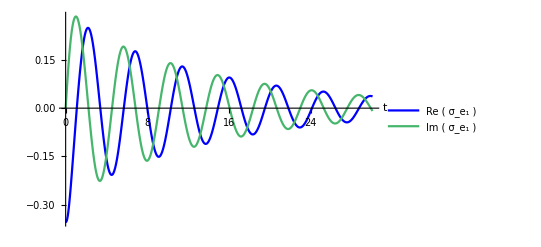

```mathematica
ListPlot[{Reσcoh12Data,Imσcoh12Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["Re ( σ_e_1 )",FontFamily->"Times New Roman"],Style["Im ( σ_e_1 )",FontFamily->"Times New Roman"]}]
```

#### Site basis

Here we convert the reduced density matrix into site basis |1⟩ to see the dynamics among the sites

```mathematica
σ[n_]:=DiagonalMatrix[σpop[n]]+Partition[Riffle[σcoh[n],0,{1,Length[v]^2,Length[v]+1}],Length[v]];
```

```mathematica
σ11Data=Table[{n dt,σ[n][[1,1]]},{n,0,Nt+1}]
```

{{0.,0.146447},{0.05,0.146447},{0.1,0.147231},{0.15,0.148785},{0.2,0.151077},{0.25,0.154063},{0.3,0.157687},{0.35,0.161887},{0.4,0.166596},{0.45,0.171745},{0.5,0.177268},{0.55,0.183099},{0.6,0.189178},{0.65,0.195447},{0.7,0.201856},{0.75,0.208358},{0.8,0.214914},{0.85,0.221489},{0.9,0.228053},{0.95,0.234581},{1.,0.241053},{1.05,0.247455},{1.1,0.253774},{1.15,0.260002},{1.2,0.266134},{1.25,0.272167},{1.3,0.278099},{1.35,0.283932},{1.4,0.289667},{1.45,0.295308},{1.5,0.300857},{1.55,0.306321},{1.6,0.311701},{1.65,0.317004},{1.7,0.322232},{1.75,0.327392},{1.8,0.332486},{1.85,0.337518},{1.9,0.342492},{1.95,0.34741},{2.,0.352277},{2.05,0.357094},{2.1,0.361863},{2.15,0.366588},{2.2,0.371268},{2.25,0.375906},{2.3,0.380502},{2.35,0.385059},{2.4,0.389576},{2.45,0.394054},{2.5,0.398494},{2.55,0.402896},{2.6,0.407261},{2.65,0.411589},{2.7,0.415879},{2.75,0.420132},{2.8,0.424348},{2.85,0.428526},{2.9,0.432668},{2.95,0.436772},{3.,0.440839},{3.05,0.444869},{3.1,0.448861},{3.15,0.452816},{3.2,0.456733},{3.25,0.460612},{3.3,0.464454},{3.35,0.468258},{3.4,0.472024},{3.45,0.475753},{3.5,0.479444},{3.55,0.483098},{3.6,0.486714},{3.65,0.490293},{3.7,0.493834},{3.75,0.497339},{3.8,0.500806},{3.85,0.504236},{3.9,0.50763},{3.95,0.510987},{4.,0.514308},{4.05,0.517593},{4.1,0.520842},{4.15,0.524056},{4.2,0.527234},{4.25,0.530377},{4.3,0.533485},{4.35,0.536559},{4.4,0.539598},{4.45,0.542603},{4.5,0.545575},{4.55,0.548513},{4.6,0.551418},{4.65,0.554291},{4.7,0.55713},{4.75,0.559938},{4.8,0.562713},{4.85,0.565458},{4.9,0.56817},{4.95,0.570852},{5.,0.573503},{5.05,0.576124},{5.1,0.578715},{5.15,0.581276},{5.2,0.583808},{5.25,0.586311},{5.3,0.588785},{5.35,0.591231},{5.4,0.593648},{5.45,0.596038},{5.5,0.5984},{5.55,0.600735},{5.6,0.603043},{5.65,0.605324},{5.7,0.607579},{5.75,0.609809},{5.8,0.612012},{5.85,0.61419},{5.9,0.616343},{5.95,0.618471},{6.,0.620575},{6.05,0.622654},{6.1,0.62471},{6.15,0.626742},{6.2,0.62875},{6.25,0.630736},{6.3,0.632698},{6.35,0.634638},{6.4,0.636556},{6.45,0.638452},{6.5,0.640326},{6.55,0.642178},{6.6,0.644009},{6.65,0.64582},{6.7,0.647609},{6.75,0.649378},{6.8,0.651127},{6.85,0.652857},{6.9,0.654566},{6.95,0.656256},{7.,0.657926},{7.05,0.659578},{7.1,0.661211},{7.15,0.662825},{7.2,0.664421},{7.25,0.665999},{7.3,0.667559},{7.35,0.669102},{7.4,0.670627},{7.45,0.672135},{7.5,0.673626},{7.55,0.6751},{7.6,0.676557},{7.65,0.677998},{7.7,0.679423},{7.75,0.680832},{7.8,0.682225},{7.85,0.683603},{7.9,0.684965},{7.95,0.686311},{8.,0.687643},{8.05,0.68896},{8.1,0.690262},{8.15,0.691549},{8.2,0.692822},{8.25,0.694081},{8.3,0.695326},{8.35,0.696557},{8.4,0.697774},{8.45,0.698977},{8.5,0.700168},{8.55,0.701344},{8.6,0.702508},{8.65,0.703659},{8.7,0.704796},{8.75,0.705922},{8.8,0.707034},{8.85,0.708134},{8.9,0.709222},{8.95,0.710298},{9.,0.711361},{9.05,0.712413},{9.1,0.713453},{9.15,0.714481},{9.2,0.715498},{9.25,0.716503},{9.3,0.717497},{9.35,0.71848},{9.4,0.719452},{9.45,0.720413},{9.5,0.721363},{9.55,0.722302},{9.6,0.723231},{9.65,0.72415},{9.7,0.725058},{9.75,0.725955},{9.8,0.726843},{9.85,0.727721},{9.9,0.728588},{9.95,0.729446},{10.,0.730294},{10.05,0.731133},{10.1,0.731962},{10.15,0.732781},{10.2,0.733592},{10.25,0.734393},{10.3,0.735185},{10.35,0.735968},{10.4,0.736742},{10.45,0.737507},{10.5,0.738264},{10.55,0.739012},{10.6,0.739751},{10.65,0.740482},{10.7,0.741205},{10.75,0.741919},{10.8,0.742626},{10.85,0.743324},{10.9,0.744014},{10.95,0.744697},{11.,0.745372},{11.05,0.746039},{11.1,0.746698},{11.15,0.74735},{11.2,0.747995},{11.25,0.748632},{11.3,0.749262},{11.35,0.749885},{11.4,0.7505},{11.45,0.751109},{11.5,0.751711},{11.55,0.752306},{11.6,0.752894},{11.65,0.753475},{11.7,0.75405},{11.75,0.754619},{11.8,0.755181},{11.85,0.755736},{11.9,0.756285},{11.95,0.756829},{12.,0.757365},{12.05,0.757896},{12.1,0.758421},{12.15,0.75894},{12.2,0.759453},{12.25,0.759961},{12.3,0.760462},{12.35,0.760958},{12.4,0.761449},{12.45,0.761934},{12.5,0.762413},{12.55,0.762887},{12.6,0.763356},{12.65,0.763819},{12.7,0.764277},{12.75,0.76473},{12.8,0.765178},{12.85,0.765621},{12.9,0.766059},{12.95,0.766492},{13.,0.766921},{13.05,0.767344},{13.1,0.767763},{13.15,0.768177},{13.2,0.768586},{13.25,0.768991},{13.3,0.769391},{13.35,0.769787},{13.4,0.770178},{13.45,0.770565},{13.5,0.770948},{13.55,0.771326},{13.6,0.7717},{13.65,0.77207},{13.7,0.772435},{13.75,0.772797},{13.8,0.773154},{13.85,0.773508},{13.9,0.773857},{13.95,0.774203},{14.,0.774545},{14.05,0.774883},{14.1,0.775217},{14.15,0.775547},{14.2,0.775873},{14.25,0.776196},{14.3,0.776515},{14.35,0.776831},{14.4,0.777143},{14.45,0.777452},{14.5,0.777757},{14.55,0.778058},{14.6,0.778356},{14.65,0.778651},{14.7,0.778943},{14.75,0.779231},{14.8,0.779516},{14.85,0.779797},{14.9,0.780076},{14.95,0.780351},{15.,0.780623},{15.05,0.780892},{15.1,0.781158},{15.15,0.781421},{15.2,0.781681},{15.25,0.781938},{15.3,0.782192},{15.35,0.782444},{15.4,0.782692},{15.45,0.782938},{15.5,0.78318},{15.55,0.78342},{15.6,0.783658},{15.65,0.783892},{15.7,0.784124},{15.75,0.784353},{15.8,0.78458},{15.85,0.784804},{15.9,0.785026},{15.95,0.785245},{16.,0.785461},{16.05,0.785675},{16.1,0.785887},{16.15,0.786096},{16.2,0.786303},{16.25,0.786508},{16.3,0.78671},{16.35,0.78691},{16.4,0.787107},{16.45,0.787303},{16.5,0.787496},{16.55,0.787687},{16.6,0.787876},{16.65,0.788063},{16.7,0.788247},{16.75,0.78843},{16.8,0.78861},{16.85,0.788789},{16.9,0.788965},{16.95,0.78914},{17.,0.789312},{17.05,0.789483},{17.1,0.789652},{17.15,0.789818},{17.2,0.789983},{17.25,0.790146},{17.3,0.790307},{17.35,0.790467},{17.4,0.790624},{17.45,0.79078},{17.5,0.790934},{17.55,0.791087},{17.6,0.791237},{17.65,0.791386},{17.7,0.791534},{17.75,0.791679},{17.8,0.791823},{17.85,0.791966},{17.9,0.792106},{17.95,0.792246},{18.,0.792383},{18.05,0.792519},{18.1,0.792654},{18.15,0.792787},{18.2,0.792919},{18.25,0.793049},{18.3,0.793177},{18.35,0.793304},{18.4,0.79343},{18.45,0.793555},{18.5,0.793678},{18.55,0.793799},{18.6,0.793919},{18.65,0.794038},{18.7,0.794156},{18.75,0.794272},{18.8,0.794387},{18.85,0.7945},{18.9,0.794612},{18.95,0.794723},{19.,0.794833},{19.05,0.794942},{19.1,0.795049},{19.15,0.795155},{19.2,0.79526},{19.25,0.795363},{19.3,0.795466},{19.35,0.795567},{19.4,0.795667},{19.45,0.795767},{19.5,0.795864},{19.55,0.795961},{19.6,0.796057},{19.65,0.796152},{19.7,0.796245},{19.75,0.796338},{19.8,0.796429},{19.85,0.796519},{19.9,0.796609},{19.95,0.796697},{20.,0.796784},{20.05,0.796871},{20.1,0.796956},{20.15,0.79704},{20.2,0.797124},{20.25,0.797206},{20.3,0.797288},{20.35,0.797369},{20.4,0.797448},{20.45,0.797527},{20.5,0.797605},{20.55,0.797682},{20.6,0.797758},{20.65,0.797833},{20.7,0.797908},{20.75,0.797981},{20.8,0.798054},{20.85,0.798126},{20.9,0.798197},{20.95,0.798268},{21.,0.798337},{21.05,0.798406},{21.1,0.798474},{21.15,0.798541},{21.2,0.798607},{21.25,0.798673},{21.3,0.798738},{21.35,0.798802},{21.4,0.798866},{21.45,0.798928},{21.5,0.79899},{21.55,0.799052},{21.6,0.799112},{21.65,0.799172},{21.7,0.799232},{21.75,0.79929},{21.8,0.799348},{21.85,0.799406},{21.9,0.799463},{21.95,0.799519},{22.,0.799574},{22.05,0.799629},{22.1,0.799683},{22.15,0.799737},{22.2,0.79979},{22.25,0.799842},{22.3,0.799894},{22.35,0.799945},{22.4,0.799996},{22.45,0.800046},{22.5,0.800095},{22.55,0.800144},{22.6,0.800193},{22.65,0.800241},{22.7,0.800288},{22.75,0.800335},{22.8,0.800381},{22.85,0.800427},{22.9,0.800472},{22.95,0.800517},{23.,0.800561},{23.05,0.800605},{23.1,0.800648},{23.15,0.800691},{23.2,0.800733},{23.25,0.800775},{23.3,0.800816},{23.35,0.800857},{23.4,0.800898},{23.45,0.800938},{23.5,0.800977},{23.55,0.801016},{23.6,0.801055},{23.65,0.801093},{23.7,0.801131},{23.75,0.801168},{23.8,0.801205},{23.85,0.801241},{23.9,0.801277},{23.95,0.801313},{24.,0.801348},{24.05,0.801383},{24.1,0.801417},{24.15,0.801451},{24.2,0.801485},{24.25,0.801518},{24.3,0.801551},{24.35,0.801584},{24.4,0.801616},{24.45,0.801648},{24.5,0.801679},{24.55,0.80171},{24.6,0.801741},{24.65,0.801771},{24.7,0.801801},{24.75,0.801831},{24.8,0.80186},{24.85,0.801889},{24.9,0.801918},{24.95,0.801946},{25.,0.801974},{25.05,0.802002},{25.1,0.802029},{25.15,0.802056},{25.2,0.802083},{25.25,0.80211},{25.3,0.802136},{25.35,0.802162},{25.4,0.802187},{25.45,0.802213},{25.5,0.802238},{25.55,0.802262},{25.6,0.802287},{25.65,0.802311},{25.7,0.802335},{25.75,0.802358},{25.8,0.802382},{25.85,0.802405},{25.9,0.802428},{25.95,0.80245},{26.,0.802473},{26.05,0.802495},{26.1,0.802516},{26.15,0.802538},{26.2,0.802559},{26.25,0.802581},{26.3,0.802601},{26.35,0.802622},{26.4,0.802642},{26.45,0.802663},{26.5,0.802683},{26.55,0.802702},{26.6,0.802722},{26.65,0.802741},{26.7,0.80276},{26.75,0.802779},{26.8,0.802798},{26.85,0.802816},{26.9,0.802834},{26.95,0.802852},{27.,0.80287},{27.05,0.802888},{27.1,0.802905},{27.15,0.802922},{27.2,0.802939},{27.25,0.802956},{27.3,0.802973},{27.35,0.802989},{27.4,0.803006},{27.45,0.803022},{27.5,0.803038},{27.55,0.803054},{27.6,0.803069},{27.65,0.803085},{27.7,0.8031},{27.75,0.803115},{27.8,0.80313},{27.85,0.803144},{27.9,0.803159},{27.95,0.803173},{28.,0.803188},{28.05,0.803202},{28.1,0.803215},{28.15,0.803229},{28.2,0.803243},{28.25,0.803256},{28.3,0.803269},{28.35,0.803283},{28.4,0.803296},{28.45,0.803308},{28.5,0.803321},{28.55,0.803334},{28.6,0.803346},{28.65,0.803358},{28.7,0.80337},{28.75,0.803382},{28.8,0.803394},{28.85,0.803406},{28.9,0.803417},{28.95,0.803429},{29.,0.80344},{29.05,0.803451},{29.1,0.803462},{29.15,0.803473},{29.2,0.803484},{29.25,0.803495},{29.3,0.803505},{29.35,0.803516},{29.4,0.803526},{29.45,0.803536},{29.5,0.803546},{29.55,0.803556},{29.6,0.803566},{29.65,0.803576},{29.7,0.803585},{29.75,0.803595},{29.8,0.803604},{29.85,0.803614},{29.9,0.803623},{29.95,0.803632},{30.,0.803641},{30.05,0.80365}}

```mathematica
σ22Data=Table[{n dt,σ[n][[2,2]]},{n,0,Nt+1}]
```

{{0.,0.853553},{0.05,0.853553},{0.1,0.852769},{0.15,0.851215},{0.2,0.848923},{0.25,0.845937},{0.3,0.842313},{0.35,0.838113},{0.4,0.833404},{0.45,0.828255},{0.5,0.822732},{0.55,0.816901},{0.6,0.810822},{0.65,0.804553},{0.7,0.798144},{0.75,0.791642},{0.8,0.785086},{0.85,0.778511},{0.9,0.771947},{0.95,0.765419},{1.,0.758947},{1.05,0.752545},{1.1,0.746226},{1.15,0.739998},{1.2,0.733866},{1.25,0.727833},{1.3,0.721901},{1.35,0.716068},{1.4,0.710333},{1.45,0.704692},{1.5,0.699143},{1.55,0.693679},{1.6,0.688299},{1.65,0.682996},{1.7,0.677768},{1.75,0.672608},{1.8,0.667514},{1.85,0.662482},{1.9,0.657508},{1.95,0.65259},{2.,0.647723},{2.05,0.642906},{2.1,0.638137},{2.15,0.633412},{2.2,0.628732},{2.25,0.624094},{2.3,0.619498},{2.35,0.614941},{2.4,0.610424},{2.45,0.605946},{2.5,0.601506},{2.55,0.597104},{2.6,0.592739},{2.65,0.588411},{2.7,0.584121},{2.75,0.579868},{2.8,0.575652},{2.85,0.571474},{2.9,0.567332},{2.95,0.563228},{3.,0.559161},{3.05,0.555131},{3.1,0.551139},{3.15,0.547184},{3.2,0.543267},{3.25,0.539388},{3.3,0.535546},{3.35,0.531742},{3.4,0.527976},{3.45,0.524247},{3.5,0.520556},{3.55,0.516902},{3.6,0.513286},{3.65,0.509707},{3.7,0.506166},{3.75,0.502661},{3.8,0.499194},{3.85,0.495764},{3.9,0.49237},{3.95,0.489013},{4.,0.485692},{4.05,0.482407},{4.1,0.479158},{4.15,0.475944},{4.2,0.472766},{4.25,0.469623},{4.3,0.466515},{4.35,0.463441},{4.4,0.460402},{4.45,0.457397},{4.5,0.454425},{4.55,0.451487},{4.6,0.448582},{4.65,0.445709},{4.7,0.44287},{4.75,0.440062},{4.8,0.437287},{4.85,0.434542},{4.9,0.43183},{4.95,0.429148},{5.,0.426497},{5.05,0.423876},{5.1,0.421285},{5.15,0.418724},{5.2,0.416192},{5.25,0.413689},{5.3,0.411215},{5.35,0.408769},{5.4,0.406352},{5.45,0.403962},{5.5,0.4016},{5.55,0.399265},{5.6,0.396957},{5.65,0.394676},{5.7,0.392421},{5.75,0.390191},{5.8,0.387988},{5.85,0.38581},{5.9,0.383657},{5.95,0.381529},{6.,0.379425},{6.05,0.377346},{6.1,0.37529},{6.15,0.373258},{6.2,0.37125},{6.25,0.369264},{6.3,0.367302},{6.35,0.365362},{6.4,0.363444},{6.45,0.361548},{6.5,0.359674},{6.55,0.357822},{6.6,0.355991},{6.65,0.35418},{6.7,0.352391},{6.75,0.350622},{6.8,0.348873},{6.85,0.347143},{6.9,0.345434},{6.95,0.343744},{7.,0.342074},{7.05,0.340422},{7.1,0.338789},{7.15,0.337175},{7.2,0.335579},{7.25,0.334001},{7.3,0.332441},{7.35,0.330898},{7.4,0.329373},{7.45,0.327865},{7.5,0.326374},{7.55,0.3249},{7.6,0.323443},{7.65,0.322002},{7.7,0.320577},{7.75,0.319168},{7.8,0.317775},{7.85,0.316397},{7.9,0.315035},{7.95,0.313689},{8.,0.312357},{8.05,0.31104},{8.1,0.309738},{8.15,0.308451},{8.2,0.307178},{8.25,0.305919},{8.3,0.304674},{8.35,0.303443},{8.4,0.302226},{8.45,0.301023},{8.5,0.299832},{8.55,0.298656},{8.6,0.297492},{8.65,0.296341},{8.7,0.295204},{8.75,0.294078},{8.8,0.292966},{8.85,0.291866},{8.9,0.290778},{8.95,0.289702},{9.,0.288639},{9.05,0.287587},{9.1,0.286547},{9.15,0.285519},{9.2,0.284502},{9.25,0.283497},{9.3,0.282503},{9.35,0.28152},{9.4,0.280548},{9.45,0.279587},{9.5,0.278637},{9.55,0.277698},{9.6,0.276769},{9.65,0.27585},{9.7,0.274942},{9.75,0.274045},{9.8,0.273157},{9.85,0.272279},{9.9,0.271412},{9.95,0.270554},{10.,0.269706},{10.05,0.268867},{10.1,0.268038},{10.15,0.267219},{10.2,0.266408},{10.25,0.265607},{10.3,0.264815},{10.35,0.264032},{10.4,0.263258},{10.45,0.262493},{10.5,0.261736},{10.55,0.260988},{10.6,0.260249},{10.65,0.259518},{10.7,0.258795},{10.75,0.258081},{10.8,0.257374},{10.85,0.256676},{10.9,0.255986},{10.95,0.255303},{11.,0.254628},{11.05,0.253961},{11.1,0.253302},{11.15,0.25265},{11.2,0.252005},{11.25,0.251368},{11.3,0.250738},{11.35,0.250115},{11.4,0.2495},{11.45,0.248891},{11.5,0.248289},{11.55,0.247694},{11.6,0.247106},{11.65,0.246525},{11.7,0.24595},{11.75,0.245381},{11.8,0.244819},{11.85,0.244264},{11.9,0.243715},{11.95,0.243171},{12.,0.242635},{12.05,0.242104},{12.1,0.241579},{12.15,0.24106},{12.2,0.240547},{12.25,0.240039},{12.3,0.239538},{12.35,0.239042},{12.4,0.238551},{12.45,0.238066},{12.5,0.237587},{12.55,0.237113},{12.6,0.236644},{12.65,0.236181},{12.7,0.235723},{12.75,0.23527},{12.8,0.234822},{12.85,0.234379},{12.9,0.233941},{12.95,0.233508},{13.,0.233079},{13.05,0.232656},{13.1,0.232237},{13.15,0.231823},{13.2,0.231414},{13.25,0.231009},{13.3,0.230609},{13.35,0.230213},{13.4,0.229822},{13.45,0.229435},{13.5,0.229052},{13.55,0.228674},{13.6,0.2283},{13.65,0.22793},{13.7,0.227565},{13.75,0.227203},{13.8,0.226846},{13.85,0.226492},{13.9,0.226143},{13.95,0.225797},{14.,0.225455},{14.05,0.225117},{14.1,0.224783},{14.15,0.224453},{14.2,0.224127},{14.25,0.223804},{14.3,0.223485},{14.35,0.223169},{14.4,0.222857},{14.45,0.222548},{14.5,0.222243},{14.55,0.221942},{14.6,0.221644},{14.65,0.221349},{14.7,0.221057},{14.75,0.220769},{14.8,0.220484},{14.85,0.220203},{14.9,0.219924},{14.95,0.219649},{15.,0.219377},{15.05,0.219108},{15.1,0.218842},{15.15,0.218579},{15.2,0.218319},{15.25,0.218062},{15.3,0.217808},{15.35,0.217556},{15.4,0.217308},{15.45,0.217062},{15.5,0.21682},{15.55,0.21658},{15.6,0.216342},{15.65,0.216108},{15.7,0.215876},{15.75,0.215647},{15.8,0.21542},{15.85,0.215196},{15.9,0.214974},{15.95,0.214755},{16.,0.214539},{16.05,0.214325},{16.1,0.214113},{16.15,0.213904},{16.2,0.213697},{16.25,0.213492},{16.3,0.21329},{16.35,0.21309},{16.4,0.212893},{16.45,0.212697},{16.5,0.212504},{16.55,0.212313},{16.6,0.212124},{16.65,0.211937},{16.7,0.211753},{16.75,0.21157},{16.8,0.21139},{16.85,0.211211},{16.9,0.211035},{16.95,0.21086},{17.,0.210688},{17.05,0.210517},{17.1,0.210348},{17.15,0.210182},{17.2,0.210017},{17.25,0.209854},{17.3,0.209693},{17.35,0.209533},{17.4,0.209376},{17.45,0.20922},{17.5,0.209066},{17.55,0.208913},{17.6,0.208763},{17.65,0.208614},{17.7,0.208466},{17.75,0.208321},{17.8,0.208177},{17.85,0.208034},{17.9,0.207894},{17.95,0.207754},{18.,0.207617},{18.05,0.207481},{18.1,0.207346},{18.15,0.207213},{18.2,0.207081},{18.25,0.206951},{18.3,0.206823},{18.35,0.206696},{18.4,0.20657},{18.45,0.206445},{18.5,0.206322},{18.55,0.206201},{18.6,0.206081},{18.65,0.205962},{18.7,0.205844},{18.75,0.205728},{18.8,0.205613},{18.85,0.2055},{18.9,0.205388},{18.95,0.205277},{19.,0.205167},{19.05,0.205058},{19.1,0.204951},{19.15,0.204845},{19.2,0.20474},{19.25,0.204637},{19.3,0.204534},{19.35,0.204433},{19.4,0.204333},{19.45,0.204233},{19.5,0.204136},{19.55,0.204039},{19.6,0.203943},{19.65,0.203848},{19.7,0.203755},{19.75,0.203662},{19.8,0.203571},{19.85,0.203481},{19.9,0.203391},{19.95,0.203303},{20.,0.203216},{20.05,0.203129},{20.1,0.203044},{20.15,0.20296},{20.2,0.202876},{20.25,0.202794},{20.3,0.202712},{20.35,0.202631},{20.4,0.202552},{20.45,0.202473},{20.5,0.202395},{20.55,0.202318},{20.6,0.202242},{20.65,0.202167},{20.7,0.202092},{20.75,0.202019},{20.8,0.201946},{20.85,0.201874},{20.9,0.201803},{20.95,0.201732},{21.,0.201663},{21.05,0.201594},{21.1,0.201526},{21.15,0.201459},{21.2,0.201393},{21.25,0.201327},{21.3,0.201262},{21.35,0.201198},{21.4,0.201134},{21.45,0.201072},{21.5,0.20101},{21.55,0.200948},{21.6,0.200888},{21.65,0.200828},{21.7,0.200768},{21.75,0.20071},{21.8,0.200652},{21.85,0.200594},{21.9,0.200537},{21.95,0.200481},{22.,0.200426},{22.05,0.200371},{22.1,0.200317},{22.15,0.200263},{22.2,0.20021},{22.25,0.200158},{22.3,0.200106},{22.35,0.200055},{22.4,0.200004},{22.45,0.199954},{22.5,0.199905},{22.55,0.199856},{22.6,0.199807},{22.65,0.199759},{22.7,0.199712},{22.75,0.199665},{22.8,0.199619},{22.85,0.199573},{22.9,0.199528},{22.95,0.199483},{23.,0.199439},{23.05,0.199395},{23.1,0.199352},{23.15,0.199309},{23.2,0.199267},{23.25,0.199225},{23.3,0.199184},{23.35,0.199143},{23.4,0.199102},{23.45,0.199062},{23.5,0.199023},{23.55,0.198984},{23.6,0.198945},{23.65,0.198907},{23.7,0.198869},{23.75,0.198832},{23.8,0.198795},{23.85,0.198759},{23.9,0.198723},{23.95,0.198687},{24.,0.198652},{24.05,0.198617},{24.1,0.198583},{24.15,0.198549},{24.2,0.198515},{24.25,0.198482},{24.3,0.198449},{24.35,0.198416},{24.4,0.198384},{24.45,0.198352},{24.5,0.198321},{24.55,0.19829},{24.6,0.198259},{24.65,0.198229},{24.7,0.198199},{24.75,0.198169},{24.8,0.19814},{24.85,0.198111},{24.9,0.198082},{24.95,0.198054},{25.,0.198026},{25.05,0.197998},{25.1,0.197971},{25.15,0.197944},{25.2,0.197917},{25.25,0.19789},{25.3,0.197864},{25.35,0.197838},{25.4,0.197813},{25.45,0.197787},{25.5,0.197762},{25.55,0.197738},{25.6,0.197713},{25.65,0.197689},{25.7,0.197665},{25.75,0.197642},{25.8,0.197618},{25.85,0.197595},{25.9,0.197572},{25.95,0.19755},{26.,0.197527},{26.05,0.197505},{26.1,0.197484},{26.15,0.197462},{26.2,0.197441},{26.25,0.197419},{26.3,0.197399},{26.35,0.197378},{26.4,0.197358},{26.45,0.197337},{26.5,0.197317},{26.55,0.197298},{26.6,0.197278},{26.65,0.197259},{26.7,0.19724},{26.75,0.197221},{26.8,0.197202},{26.85,0.197184},{26.9,0.197166},{26.95,0.197148},{27.,0.19713},{27.05,0.197112},{27.1,0.197095},{27.15,0.197078},{27.2,0.197061},{27.25,0.197044},{27.3,0.197027},{27.35,0.197011},{27.4,0.196994},{27.45,0.196978},{27.5,0.196962},{27.55,0.196946},{27.6,0.196931},{27.65,0.196915},{27.7,0.1969},{27.75,0.196885},{27.8,0.19687},{27.85,0.196856},{27.9,0.196841},{27.95,0.196827},{28.,0.196812},{28.05,0.196798},{28.1,0.196785},{28.15,0.196771},{28.2,0.196757},{28.25,0.196744},{28.3,0.196731},{28.35,0.196717},{28.4,0.196704},{28.45,0.196692},{28.5,0.196679},{28.55,0.196666},{28.6,0.196654},{28.65,0.196642},{28.7,0.19663},{28.75,0.196618},{28.8,0.196606},{28.85,0.196594},{28.9,0.196583},{28.95,0.196571},{29.,0.19656},{29.05,0.196549},{29.1,0.196538},{29.15,0.196527},{29.2,0.196516},{29.25,0.196505},{29.3,0.196495},{29.35,0.196484},{29.4,0.196474},{29.45,0.196464},{29.5,0.196454},{29.55,0.196444},{29.6,0.196434},{29.65,0.196424},{29.7,0.196415},{29.75,0.196405},{29.8,0.196396},{29.85,0.196386},{29.9,0.196377},{29.95,0.196368},{30.,0.196359},{30.05,0.19635}}

```mathematica
σ12Data=Table[{n dt,σ[n][[1,2]]},{n,0,Nt+1}]
```

{{0.,-0.353553},{0.05,-0.353553-0.025 ⅈ},{0.1,-0.350614-0.049931 ⅈ},{0.15,-0.344807-0.0744526 ⅈ},{0.2,-0.336294-0.098248 ⅈ},{0.25,-0.325315-0.121041 ⅈ},{0.3,-0.312155-0.142605 ⅈ},{0.35,-0.297126-0.162772 ⅈ},{0.4,-0.280542-0.181427 ⅈ},{0.45,-0.262699-0.198502 ⅈ},{0.5,-0.243864-0.213968 ⅈ},{0.55,-0.224268-0.227826 ⅈ},{0.6,-0.204108-0.240092 ⅈ},{0.65,-0.183547-0.250799 ⅈ},{0.7,-0.162719-0.259981 ⅈ},{0.75,-0.141734-0.267676 ⅈ},{0.8,-0.120686-0.273919 ⅈ},{0.85,-0.099655-0.278745 ⅈ},{0.9,-0.078713-0.282184 ⅈ},{0.95,-0.0579256-0.284268 ⅈ},{1.,-0.0373552-0.285024 ⅈ},{1.05,-0.0170626-0.284482 ⅈ},{1.1,0.00289242-0.282669 ⅈ},{1.15,0.0224503-0.279616 ⅈ},{1.2,0.0415516-0.275355 ⅈ},{1.25,0.0601373-0.269922 ⅈ},{1.3,0.0781484-0.263353 ⅈ},{1.35,0.0955272-0.25569 ⅈ},{1.4,0.112217-0.246978 ⅈ},{1.45,0.128162-0.237263 ⅈ},{1.5,0.14331-0.226598 ⅈ},{1.55,0.15761-0.215038 ⅈ},{1.6,0.171013-0.202639 ⅈ},{1.65,0.183476-0.189463 ⅈ},{1.7,0.194957-0.175575 ⅈ},{1.75,0.205417-0.16104 ⅈ},{1.8,0.214825-0.145927 ⅈ},{1.85,0.22315-0.130308 ⅈ},{1.9,0.230368-0.114256 ⅈ},{1.95,0.236459-0.0978435 ⅈ},{2.,0.241406-0.0811469 ⅈ},{2.05,0.2452-0.0642421 ⅈ},{2.1,0.247834-0.0472058 ⅈ},{2.15,0.249308-0.0301144 ⅈ},{2.2,0.249625-0.0130445 ⅈ},{2.25,0.248796+0.00392799 ⅈ},{2.3,0.246833+0.0207282 ⅈ},{2.35,0.243755+0.0372823 ⅈ},{2.4,0.239586+0.0535182 ⅈ},{2.45,0.234354+0.0693655 ⅈ},{2.5,0.228091+0.0847561 ⅈ},{2.55,0.220835+0.0996243 ⅈ},{2.6,0.212626+0.113907 ⅈ},{2.65,0.203509+0.127545 ⅈ},{2.7,0.193533+0.140481 ⅈ},{2.75,0.18275+0.152663 ⅈ},{2.8,0.171215+0.16404 ⅈ},{2.85,0.158988+0.174568 ⅈ},{2.9,0.146128+0.184205 ⅈ},{2.95,0.1327+0.192914 ⅈ},{3.,0.118769+0.200664 ⅈ},{3.05,0.104403+0.207425 ⅈ},{3.1,0.0896711+0.213175 ⅈ},{3.15,0.0746426+0.217895 ⅈ},{3.2,0.0593889+0.221571 ⅈ},{3.25,0.0439817+0.224195 ⅈ},{3.3,0.0284924+0.225763 ⅈ},{3.35,0.0129929+0.226274 ⅈ},{3.4,-0.00244581+0.225736 ⅈ},{3.45,-0.0177533+0.224157 ⅈ},{3.5,-0.0328604+0.221554 ⅈ},{3.55,-0.047699+0.217945 ⅈ},{3.6,-0.0622032+0.213355 ⅈ},{3.65,-0.0763085+0.207813 ⅈ},{3.7,-0.0899533+0.20135 ⅈ},{3.75,-0.103078+0.194003 ⅈ},{3.8,-0.115626+0.185812 ⅈ},{3.85,-0.127544+0.176822 ⅈ},{3.9,-0.138781+0.16708 ⅈ},{3.95,-0.149291+0.156635 ⅈ},{4.,-0.159031+0.145542 ⅈ},{4.05,-0.167961+0.133856 ⅈ},{4.1,-0.176045+0.121635 ⅈ},{4.15,-0.183254+0.10894 ⅈ},{4.2,-0.189559+0.095832 ⅈ},{4.25,-0.194939+0.0823753 ⅈ},{4.3,-0.199374+0.0686344 ⅈ},{4.35,-0.202852+0.0546747 ⅈ},{4.4,-0.205363+0.0405623 ⅈ},{4.45,-0.206902+0.0263635 ⅈ},{4.5,-0.20747+0.0121446 ⅈ},{4.55,-0.20707-0.00202859 ⅈ},{4.6,-0.205711-0.0160908 ⅈ},{4.65,-0.203407-0.0299778 ⅈ},{4.7,-0.200174-0.0436266 ⅈ},{4.75,-0.196035-0.0569757 ⅈ},{4.8,-0.191014-0.0699654 ⅈ},{4.85,-0.185142-0.0825382 ⅈ},{4.9,-0.178451-0.0946387 ⅈ},{4.95,-0.170979-0.106214 ⅈ},{5.,-0.162765-0.117215 ⅈ},{5.05,-0.153852-0.127594 ⅈ},{5.1,-0.144287-0.137308 ⅈ},{5.15,-0.134119-0.146315 ⅈ},{5.2,-0.123399-0.15458 ⅈ},{5.25,-0.112181-0.16207 ⅈ},{5.3,-0.100519-0.168754 ⅈ},{5.35,-0.0884718-0.174608 ⅈ},{5.4,-0.076097-0.17961 ⅈ},{5.45,-0.0634546-0.183743 ⅈ},{5.5,-0.050605-0.186994 ⅈ},{5.55,-0.0376092-0.189354 ⅈ},{5.6,-0.0245284-0.190818 ⅈ},{5.65,-0.0114241-0.191385 ⅈ},{5.7,0.00164305-0.191059 ⅈ},{5.75,0.0146125-0.189848 ⅈ},{5.8,0.0274249-0.187764 ⅈ},{5.85,0.0400218-0.184822 ⅈ},{5.9,0.0523463-0.181041 ⅈ},{5.95,0.064343-0.176446 ⅈ},{6.,0.0759586-0.171062 ⅈ},{6.05,0.0871418-0.164921 ⅈ},{6.1,0.0978436-0.158056 ⅈ},{6.15,0.108018-0.150503 ⅈ},{6.2,0.117621-0.142303 ⅈ},{6.25,0.126612-0.133499 ⅈ},{6.3,0.134953-0.124134 ⅈ},{6.35,0.142611-0.114257 ⅈ},{6.4,0.149554-0.103916 ⅈ},{6.45,0.155755-0.0931636 ⅈ},{6.5,0.16119-0.0820515 ⅈ},{6.55,0.16584-0.070634 ⅈ},{6.6,0.169688-0.0589661 ⅈ},{6.65,0.172721-0.0471039 ⅈ},{6.7,0.174931-0.0351035 ⅈ},{6.75,0.176314-0.0230218 ⅈ},{6.8,0.176869-0.0109153 ⅈ},{6.85,0.176599+0.00115968 ⅈ},{6.9,0.17551+0.0131472 ⅈ},{6.95,0.173613+0.0249922 ⅈ},{7.,0.170923+0.0366407 ⅈ},{7.05,0.167457+0.04804 ⅈ},{7.1,0.163236+0.0591388 ⅈ},{7.15,0.158287+0.0698876 ⅈ},{7.2,0.152635+0.0802389 ⅈ},{7.25,0.146313+0.0901473 ⅈ},{7.3,0.139354+0.0995699 ⅈ},{7.35,0.131795+0.108466 ⅈ},{7.4,0.123675+0.116798 ⅈ},{7.45,0.115036+0.124531 ⅈ},{7.5,0.10592+0.131634 ⅈ},{7.55,0.0963746+0.138077 ⅈ},{7.6,0.0864458+0.143834 ⅈ},{7.65,0.0761826+0.148885 ⅈ},{7.7,0.0656349+0.15321 ⅈ},{7.75,0.0548536+0.156794 ⅈ},{7.8,0.0438903+0.159626 ⅈ},{7.85,0.0327973+0.161696 ⅈ},{7.9,0.0216268+0.163002 ⅈ},{7.95,0.0104313+0.163542 ⅈ},{8.,-0.000737145+0.163318 ⅈ},{8.05,-0.0118267+0.162337 ⅈ},{8.1,-0.0227866+0.160608 ⅈ},{8.15,-0.0335666+0.158145 ⅈ},{8.2,-0.044118+0.154964 ⅈ},{8.25,-0.0543932+0.151085 ⅈ},{8.3,-0.0643466+0.146529 ⅈ},{8.35,-0.0739338+0.141324 ⅈ},{8.4,-0.0831131+0.135497 ⅈ},{8.45,-0.0918443+0.12908 ⅈ},{8.5,-0.10009+0.122106 ⅈ},{8.55,-0.107815+0.114612 ⅈ},{8.6,-0.114988+0.106636 ⅈ},{8.65,-0.121577+0.0982183 ⅈ},{8.7,-0.127558+0.0894008 ⅈ},{8.75,-0.132906+0.0802273 ⅈ},{8.8,-0.1376+0.0707427 ⅈ},{8.85,-0.141624+0.0609932 ⅈ},{8.9,-0.144962+0.0510259 ⅈ},{8.95,-0.147604+0.0408885 ⅈ},{9.,-0.149543+0.0306292 ⅈ},{9.05,-0.150775+0.0202965 ⅈ},{9.1,-0.151297+0.00993894 ⅈ},{9.15,-0.151113-0.000395276 ⅈ},{9.2,-0.150228-0.0106583 ⅈ},{9.25,-0.148651-0.0208029 ⅈ},{9.3,-0.146394-0.0307827 ⅈ},{9.35,-0.143472-0.0405526 ⅈ},{9.4,-0.139902-0.0500686 ⅈ},{9.45,-0.135707-0.059288 ⅈ},{9.5,-0.13091-0.0681702 ⅈ},{9.55,-0.125536-0.0766761 ⅈ},{9.6,-0.119615-0.0847688 ⅈ},{9.65,-0.113178-0.0924134 ⅈ},{9.7,-0.106259-0.0995773 ⅈ},{9.75,-0.098892-0.106231 ⅈ},{9.8,-0.091115-0.112346 ⅈ},{9.85,-0.0829667-0.117898 ⅈ},{9.9,-0.0744876-0.122865 ⅈ},{9.95,-0.0657192-0.127229 ⅈ},{10.,-0.0567041-0.130971 ⅈ},{10.05,-0.047486-0.134081 ⅈ},{10.1,-0.038109-0.136546 ⅈ},{10.15,-0.0286177-0.138361 ⅈ},{10.2,-0.0190569-0.139521 ⅈ},{10.25,-0.0094716-0.140024 ⅈ},{10.3,0.000093564-0.139874 ⅈ},{10.35,0.00959429-0.139075 ⅈ},{10.4,0.0189869-0.137635 ⅈ},{10.45,0.0282284-0.135565 ⅈ},{10.5,0.037277-0.13288 ⅈ},{10.55,0.0460918-0.129595 ⅈ},{10.6,0.0546336-0.125729 ⅈ},{10.65,0.0628644-0.121306 ⅈ},{10.7,0.070748-0.116348 ⅈ},{10.75,0.0782503-0.110884 ⅈ},{10.8,0.0853389-0.10494 ⅈ},{10.85,0.0919836-0.0985488 ⅈ},{10.9,0.0981565-0.0917424 ⅈ},{10.95,0.103832-0.0845553 ⅈ},{11.,0.108987-0.0770234 ⅈ},{11.05,0.113602-0.0691839 ⅈ},{11.1,0.117658-0.0610755 ⅈ},{11.15,0.12114-0.0527375 ⅈ},{11.2,0.124036-0.0442102 ⅈ},{11.25,0.126336-0.0355345 ⅈ},{11.3,0.128034-0.0267517 ⅈ},{11.35,0.129126-0.0179033 ⅈ},{11.4,0.129611-0.00903082 ⅈ},{11.45,0.12949-0.000175686 ⅈ},{11.5,0.128769+0.0086211 ⅈ},{11.55,0.127454+0.0173191 ⅈ},{11.6,0.125556+0.0258785 ⅈ},{11.65,0.123087+0.0342604 ⅈ},{11.7,0.120063+0.0424273 ⅈ},{11.75,0.116501+0.0503424 ⅈ},{11.8,0.112421+0.0579708 ⅈ},{11.85,0.107847+0.0652789 ⅈ},{11.9,0.102802+0.072235 ⅈ},{11.95,0.0973132+0.0788089 ⅈ},{12.,0.0914089+0.0849729 ⅈ},{12.05,0.0851193+0.0907008 ⅈ},{12.1,0.0784763+0.0959692 ⅈ},{12.15,0.0715131+0.100756 ⅈ},{12.2,0.064264+0.105044 ⅈ},{12.25,0.0567648+0.108814 ⅈ},{12.3,0.049052+0.112054 ⅈ},{12.35,0.0411627+0.114752 ⅈ},{12.4,0.0331349+0.116898 ⅈ},{12.45,0.0250067+0.118487 ⅈ},{12.5,0.0168166+0.119515 ⅈ},{12.55,0.008603+0.119981 ⅈ},{12.6,0.000404258+0.119886 ⅈ},{12.65,-0.00774164+0.119235 ⅈ},{12.7,-0.0157972+0.118034 ⅈ},{12.75,-0.0237256+0.116293 ⅈ},{12.8,-0.0314909+0.114023 ⅈ},{12.85,-0.0390581+0.111239 ⅈ},{12.9,-0.0463933+0.107956 ⅈ},{12.95,-0.053464+0.104194 ⅈ},{13.,-0.0602391+0.0999722 ⅈ},{13.05,-0.0666892+0.0953146 ⅈ},{13.1,-0.0727863+0.0902451 ⅈ},{13.15,-0.0785047+0.0847902 ⅈ},{13.2,-0.0838201+0.0789778 ⅈ},{13.25,-0.0887107+0.0728371 ⅈ},{13.3,-0.0931565+0.066399 ⅈ},{13.35,-0.0971398+0.0596954 ⅈ},{13.4,-0.100645+0.0527591 ⅈ},{13.45,-0.10366+0.0456239 ⅈ},{13.5,-0.106172+0.0383244 ⅈ},{13.55,-0.108175+0.0308955 ⅈ},{13.6,-0.109662+0.0233725 ⅈ},{13.65,-0.110629+0.0157912 ⅈ},{13.7,-0.111076+0.00818699 ⅈ},{13.75,-0.111004+0.000595469 ⅈ},{13.8,-0.110416-0.0069482 ⅈ},{13.85,-0.10932-0.0144093 ⅈ},{13.9,-0.107723-0.0217537 ⅈ},{13.95,-0.105636-0.0289481 ⅈ},{14.,-0.103072-0.03596 ⅈ},{14.05,-0.100046-0.0427581 ⅈ},{14.1,-0.0965761-0.0493123 ⅈ},{14.15,-0.0926803-0.0555936 ⅈ},{14.2,-0.0883798-0.0615748 ⅈ},{14.25,-0.0836973-0.0672301 ⅈ},{14.3,-0.0786572-0.0725353 ⅈ},{14.35,-0.0732853-0.0774681 ⅈ},{14.4,-0.0676086-0.0820081 ⅈ},{14.45,-0.0616557-0.0861369 ⅈ},{14.5,-0.0554559-0.0898379 ⅈ},{14.55,-0.0490399-0.0930969 ⅈ},{14.6,-0.0424387-0.0959017 ⅈ},{14.65,-0.0356844-0.0982422 ⅈ},{14.7,-0.0288093-0.100111 ⅈ},{14.75,-0.0218461-0.101502 ⅈ},{14.8,-0.0148278-0.102412 ⅈ},{14.85,-0.00778743-0.10284 ⅈ},{14.9,-0.000757759-0.102787 ⅈ},{14.95,0.00622859-0.102258 ⅈ},{15.,0.0131395-0.101256 ⅈ},{15.05,0.0199432-0.0997913 ⅈ},{15.1,0.026609-0.0978724 ⅈ},{15.15,0.0331068-0.0955115 ⅈ},{15.2,0.0394075-0.0927227 ⅈ},{15.25,0.045483-0.0895216 ⅈ},{15.3,0.0513068-0.0859259 ⅈ},{15.35,0.0568535-0.081955 ⅈ},{15.4,0.062099-0.0776297 ⅈ},{15.45,0.0670211-0.0729726 ⅈ},{15.5,0.071599-0.0680075 ⅈ},{15.55,0.0758138-0.0627595 ⅈ},{15.6,0.0796483-0.0572549 ⅈ},{15.65,0.0830871-0.0515209 ⅈ},{15.7,0.0861171-0.0455858 ⅈ},{15.75,0.0887267-0.0394783 ⅈ},{15.8,0.0909068-0.0332282 ⅈ},{15.85,0.0926499-0.0268653 ⅈ},{15.9,0.093951-0.02042 ⅈ},{15.95,0.094807-0.0139227 ⅈ},{16.,0.0952167-0.00740401 ⅈ},{16.05,0.0951814-0.00089434 ⅈ},{16.1,0.094704+0.00557613 ⅈ},{16.15,0.0937899+0.0119776 ⅈ},{16.2,0.0924461+0.0182808 ⅈ},{16.25,0.0906817+0.0244571 ⅈ},{16.3,0.0885078+0.0304786 ⅈ},{16.35,0.0859371+0.0363184 ⅈ},{16.4,0.0829843+0.0419506 ⅈ},{16.45,0.0796656+0.0473503 ⅈ},{16.5,0.0759989+0.0524941 ⅈ},{16.55,0.0720034+0.0573598 ⅈ},{16.6,0.0677001+0.0619266 ⅈ},{16.65,0.0631109+0.0661752 ⅈ},{16.7,0.058259+0.0700881 ⅈ},{16.75,0.0531688+0.0736493 ⅈ},{16.8,0.0478654+0.0768446 ⅈ},{16.85,0.042375+0.0796617 ⅈ},{16.9,0.0367242+0.0820898 ⅈ},{16.95,0.0309405+0.0841204 ⅈ},{17.,0.0250515+0.0857466 ⅈ},{17.05,0.0190853+0.0869636 ⅈ},{17.1,0.0130702+0.0877685 ⅈ},{17.15,0.0070344+0.0881603 ⅈ},{17.2,0.00100611+0.0881398 ⅈ},{17.25,-0.00498672+0.08771 ⅈ},{17.3,-0.0109165+0.0868755 ⅈ},{17.35,-0.016756+0.0856429 ⅈ},{17.4,-0.0224789+0.0840207 ⅈ},{17.45,-0.0280592+0.0820188 ⅈ},{17.5,-0.0334719+0.0796493 ⅈ},{17.55,-0.0386932+0.0769255 ⅈ},{17.6,-0.0436999+0.0738623 ⅈ},{17.65,-0.0484702+0.0704765 ⅈ},{17.7,-0.0529836+0.0667857 ⅈ},{17.75,-0.0572208+0.0628092 ⅈ},{17.8,-0.0611639+0.0585673 ⅈ},{17.85,-0.0647966+0.0540816 ⅈ},{17.9,-0.068104+0.0493745 ⅈ},{17.95,-0.0710731+0.0444693 ⅈ},{18.,-0.0736921+0.0393901 ⅈ},{18.05,-0.0759513+0.0341618 ⅈ},{18.1,-0.0778427+0.0288095 ⅈ},{18.15,-0.0793597+0.023359 ⅈ},{18.2,-0.080498+0.0178363 ⅈ},{18.25,-0.0812547+0.0122674 ⅈ},{18.3,-0.0816288+0.00667865 ⅈ},{18.35,-0.0816212+0.00109605 ⅈ},{18.4,-0.0812344-0.0044545 ⅈ},{18.45,-0.0804728-0.0099474 ⅈ},{18.5,-0.0793424-0.0153575 ⅈ},{18.55,-0.0778508-0.0206603 ⅈ},{18.6,-0.0760075-0.0258318 ⅈ},{18.65,-0.0738233-0.0308488 ⅈ},{18.7,-0.0713107-0.0356892 ⅈ},{18.75,-0.0684834-0.0403315 ⅈ},{18.8,-0.0653568-0.0447555 ⅈ},{18.85,-0.0619474-0.0489421 ⅈ},{18.9,-0.0582728-0.0528735 ⅈ},{18.95,-0.054352-0.0565331 ⅈ},{19.,-0.0502047-0.0599057 ⅈ},{19.05,-0.0458518-0.0629775 ⅈ},{19.1,-0.0413148-0.0657362 ⅈ},{19.15,-0.0366161-0.0681712 ⅈ},{19.2,-0.0317785-0.0702733 ⅈ},{19.25,-0.0268254-0.0720348 ⅈ},{19.3,-0.0217807-0.07345 ⅈ},{19.35,-0.0166683-0.0745145 ⅈ},{19.4,-0.0115126-0.0752257 ⅈ},{19.45,-0.00633763-0.0755827 ⅈ},{19.5,-0.00116768-0.0755861 ⅈ},{19.55,0.0039733-0.0752384 ⅈ},{19.6,0.0090616-0.0745433 ⅈ},{19.65,0.0140739-0.0735066 ⅈ},{19.7,0.0189875-0.0721353 ⅈ},{19.75,0.0237802-0.0704379 ⅈ},{19.8,0.0284305-0.0684246 ⅈ},{19.85,0.0329178-0.0661068 ⅈ},{19.9,0.0372223-0.0634973 ⅈ},{19.95,0.0413252-0.0606101 ⅈ},{20.,0.0452088-0.0574605 ⅈ},{20.05,0.0488565-0.054065 ⅈ},{20.1,0.052253-0.0504408 ⅈ},{20.15,0.055384-0.0466064 ⅈ},{20.2,0.058237-0.042581 ⅈ},{20.25,0.0608004-0.0383845 ⅈ},{20.3,0.0630642-0.0340376 ⅈ},{20.35,0.06502-0.0295615 ⅈ},{20.4,0.0666606-0.0249778 ⅈ},{20.45,0.0679807-0.0203086 ⅈ},{20.5,0.0689761-0.0155761 ⅈ},{20.55,0.0696444-0.0108027 ⅈ},{20.6,0.0699848-0.00601092 ⅈ},{20.65,0.0699977-0.00122306 ⅈ},{20.7,0.0696853+0.00353861 ⅈ},{20.75,0.0690512+0.00825217 ⅈ},{20.8,0.0681005+0.012896 ⅈ},{20.85,0.0668397+0.0174491 ⅈ},{20.9,0.0652768+0.0218907 ⅈ},{20.95,0.063421+0.0262012 ⅈ},{21.,0.061283+0.0303612 ⅈ},{21.05,0.0588744+0.0343524 ⅈ},{21.1,0.0562082+0.0381575 ⅈ},{21.15,0.0532987+0.0417601 ⅈ},{21.2,0.0501609+0.0451446 ⅈ},{21.25,0.046811+0.0482968 ⅈ},{21.3,0.0432658+0.0512037 ⅈ},{21.35,0.0395432+0.0538534 ⅈ},{21.4,0.0356617+0.0562352 ⅈ},{21.45,0.0316403+0.0583399 ⅈ},{21.5,0.0274987+0.0601596 ⅈ},{21.55,0.0232568+0.0616876 ⅈ},{21.6,0.0189351+0.0629189 ⅈ},{21.65,0.0145542+0.0638497 ⅈ},{21.7,0.0101348+0.0644776 ⅈ},{21.75,0.00569774+0.0648017 ⅈ},{21.8,0.00126372+0.0648227 ⅈ},{21.85,-0.00314668+0.0645423 ⅈ},{21.9,-0.00751311+0.0639639 ⅈ},{21.95,-0.0118156+0.0630922 ⅈ},{22.,-0.0160346+0.0619332 ⅈ},{22.05,-0.0201509+0.0604941 ⅈ},{22.1,-0.0241463+0.0587835 ⅈ},{22.15,-0.028003+0.0568113 ⅈ},{22.2,-0.0317038+0.0545881 ⅈ},{22.25,-0.0352328+0.0521262 ⅈ},{22.3,-0.0385745+0.0494384 ⅈ},{22.35,-0.0417149+0.0465389 ⅈ},{22.4,-0.0446405+0.0434424 ⅈ},{22.45,-0.0473392+0.0401646 ⅈ},{22.5,-0.0498001+0.0367221 ⅈ},{22.55,-0.0520132+0.0331318 ⅈ},{22.6,-0.05397+0.0294115 ⅈ},{22.65,-0.0556629+0.0255793 ⅈ},{22.7,-0.057086+0.0216537 ⅈ},{22.75,-0.0582345+0.0176537 ⅈ},{22.8,-0.0591047+0.0135982 ⅈ},{22.85,-0.0596945+0.00950658 ⅈ},{22.9,-0.060003+0.00539797 ⅈ},{22.95,-0.0600307+0.00129161 ⅈ},{23.,-0.0597794-0.00279344 ⅈ},{23.05,-0.0592519-0.00683833 ⅈ},{23.1,-0.0584527-0.0108245 ⅈ},{23.15,-0.0573872-0.014734 ⅈ},{23.2,-0.0560622-0.0185489 ⅈ},{23.25,-0.0544855-0.0222523 ⅈ},{23.3,-0.0526662-0.0258277 ⅈ},{23.35,-0.0506143-0.0292593 ⅈ},{23.4,-0.0483409-0.0325321 ⅈ},{23.45,-0.045858-0.035632 ⅈ},{23.5,-0.0431785-0.0385458 ⅈ},{23.55,-0.0403163-0.041261 ⅈ},{23.6,-0.0372858-0.0437665 ⅈ},{23.65,-0.0341022-0.046052 ⅈ},{23.7,-0.0307814-0.0481084 ⅈ},{23.75,-0.0273396-0.0499275 ⅈ},{23.8,-0.0237937-0.0515026 ⅈ},{23.85,-0.0201609-0.052828 ⅈ},{23.9,-0.0164585-0.053899 ⅈ},{23.95,-0.0127043-0.0547126 ⅈ},{24.,-0.00891606-0.0552665 ⅈ},{24.05,-0.00511158-0.0555599 ⅈ},{24.1,-0.00130865-0.0555933 ⅈ},{24.15,0.00247506-0.0553682 ⅈ},{24.2,0.0062221-0.0548873 ⅈ},{24.25,0.00991531-0.0541546 ⅈ},{24.3,0.0135379-0.0531752 ⅈ},{24.35,0.0170735-0.0519552 ⅈ},{24.4,0.0205062-0.050502 ⅈ},{24.45,0.0238209-0.0488238 ⅈ},{24.5,0.0270028-0.0469299 ⅈ},{24.55,0.0300381-0.0448305 ⅈ},{24.6,0.0329137-0.0425369 ⅈ},{24.65,0.0356172-0.0400609 ⅈ},{24.7,0.0381372-0.0374152 ⅈ},{24.75,0.0404633-0.0346133 ⅈ},{24.8,0.0425859-0.0316692 ⅈ},{24.85,0.0444966-0.0285976 ⅈ},{24.9,0.0461878-0.0254135 ⅈ},{24.95,0.0476532-0.0221325 ⅈ},{25.,0.0488874-0.0187705 ⅈ},{25.05,0.0498863-0.0153437 ⅈ},{25.1,0.0506468-0.0118684 ⅈ},{25.15,0.0511669-0.008361 ⅈ},{25.2,0.0514458-0.00483813 ⅈ},{25.25,0.0514839-0.00131621 ⅈ},{25.3,0.0512825+0.0021884 ⅈ},{25.35,0.0508441+0.00565954 ⅈ},{25.4,0.0501725+0.00908129 ⅈ},{25.45,0.0492722+0.0124381 ⅈ},{25.5,0.048149+0.0157148 ⅈ},{25.55,0.0468096+0.0188967 ⅈ},{25.6,0.0452616+0.0219696 ⅈ},{25.65,0.0435136+0.02492 ⅈ},{25.7,0.041575+0.027735 ⅈ},{25.75,0.0394562+0.0304025 ⅈ},{25.8,0.0371682+0.0329109 ⅈ},{25.85,0.0347227+0.0352497 ⅈ},{25.9,0.0321321+0.0374093 ⅈ},{25.95,0.0294095+0.0393806 ⅈ},{26.,0.0265684+0.0411559 ⅈ},{26.05,0.0236227+0.0427282 ⅈ},{26.1,0.0205868+0.0440914 ⅈ},{26.15,0.0174755+0.0452408 ⅈ},{26.2,0.0143037+0.0461723 ⅈ},{26.25,0.0110865+0.0468832 ⅈ},{26.3,0.00783922+0.0473714 ⅈ},{26.35,0.00457711+0.0476364 ⅈ},{26.4,0.00131543+0.0476782 ⅈ},{26.45,-0.00193067+0.0474983 ⅈ},{26.5,-0.00514621+0.0470988 ⅈ},{26.55,-0.00831645+0.0464832 ⅈ},{26.6,-0.011427+0.0456558 ⅈ},{26.65,-0.0144637+0.0446217 ⅈ},{26.7,-0.0174131+0.0433871 ⅈ},{26.75,-0.0202619+0.0419593 ⅈ},{26.8,-0.0229977+0.0403459 ⅈ},{26.85,-0.0256084+0.0385559 ⅈ},{26.9,-0.0280827+0.0365986 ⅈ},{26.95,-0.0304102+0.0344843 ⅈ},{27.,-0.0325808+0.0322238 ⅈ},{27.05,-0.0345857+0.0298286 ⅈ},{27.1,-0.0364166+0.0273108 ⅈ},{27.15,-0.038066+0.0246829 ⅈ},{27.2,-0.0395277+0.0219577 ⅈ},{27.25,-0.040796+0.0191487 ⅈ},{27.3,-0.0418663+0.0162694 ⅈ},{27.35,-0.0427349+0.0133336 ⅈ},{27.4,-0.0433993+0.0103554 ⅈ},{27.45,-0.0438576+0.0073489 ⅈ},{27.5,-0.0441091+0.00432825 ⅈ},{27.55,-0.0441539+0.00130758 ⅈ},{27.6,-0.0439934-0.00169908 ⅈ},{27.65,-0.0436295-0.00467785 ⅈ},{27.7,-0.0430653-0.00761507 ⅈ},{27.75,-0.0423048-0.0104974 ⅈ},{27.8,-0.0413528-0.0133118 ⅈ},{27.85,-0.040215-0.0160456 ⅈ},{27.9,-0.0388979-0.0186866 ⅈ},{27.95,-0.0374089-0.0212233 ⅈ},{28.,-0.0357559-0.0236446 ⅈ},{28.05,-0.0339479-0.0259398 ⅈ},{28.1,-0.0319941-0.0280993 ⅈ},{28.15,-0.0299047-0.0301139 ⅈ},{28.2,-0.0276902-0.0319752 ⅈ},{28.25,-0.0253618-0.0336755 ⅈ},{28.3,-0.0229311-0.0352081 ⅈ},{28.35,-0.0204099-0.0365669 ⅈ},{28.4,-0.0178108-0.0377467 ⅈ},{28.45,-0.0151461-0.0387434 ⅈ},{28.5,-0.0124288-0.0395534 ⅈ},{28.55,-0.00967187-0.0401743 ⅈ},{28.6,-0.00688831-0.0406043 ⅈ},{28.65,-0.00409124-0.0408429 ⅈ},{28.7,-0.00129378-0.0408901 ⅈ},{28.75,0.0014911-0.0407471 ⅈ},{28.8,0.00425053-0.0404157 ⅈ},{28.85,0.00697186-0.0398987 ⅈ},{28.9,0.0096427-0.0391997 ⅈ},{28.95,0.012251-0.0383233 ⅈ},{29.,0.014785-0.0372747 ⅈ},{29.05,0.0172335-0.0360599 ⅈ},{29.1,0.0195856-0.0346856 ⅈ},{29.15,0.0218311-0.0331593 ⅈ},{29.2,0.0239602-0.031489 ⅈ},{29.25,0.0259639-0.0296836 ⅈ},{29.3,0.0278336-0.0277523 ⅈ},{29.35,0.0295615-0.0257049 ⅈ},{29.4,0.0311406-0.0235517 ⅈ},{29.45,0.0325645-0.0213034 ⅈ},{29.5,0.0338277-0.018971 ⅈ},{29.55,0.0349253-0.016566 ⅈ},{29.6,0.0358533-0.0141001 ⅈ},{29.65,0.0366086-0.011585 ⅈ},{29.7,0.0371888-0.00903283 ⅈ},{29.75,0.0375923-0.00645567 ⅈ},{29.8,0.0378185-0.00386565 ⅈ},{29.85,0.0378675-0.00127489 ⅈ},{29.9,0.0377403+0.00130456 ⅈ},{29.95,0.0374385+0.0038608 ⅈ},{30.,0.0369648+0.0063821 ⅈ},{30.05,0.0363225+0.00885698 ⅈ}}

```mathematica
σ21Data=Table[{n dt,σ[n][[2,1]]},{n,0,Nt+1}]
```

{{0.,-0.353553},{0.05,-0.353553+0.025 ⅈ},{0.1,-0.350614+0.049931 ⅈ},{0.15,-0.344807+0.0744526 ⅈ},{0.2,-0.336294+0.098248 ⅈ},{0.25,-0.325315+0.121041 ⅈ},{0.3,-0.312155+0.142605 ⅈ},{0.35,-0.297126+0.162772 ⅈ},{0.4,-0.280542+0.181427 ⅈ},{0.45,-0.262699+0.198502 ⅈ},{0.5,-0.243864+0.213968 ⅈ},{0.55,-0.224268+0.227826 ⅈ},{0.6,-0.204108+0.240092 ⅈ},{0.65,-0.183547+0.250799 ⅈ},{0.7,-0.162719+0.259981 ⅈ},{0.75,-0.141734+0.267676 ⅈ},{0.8,-0.120686+0.273919 ⅈ},{0.85,-0.099655+0.278745 ⅈ},{0.9,-0.078713+0.282184 ⅈ},{0.95,-0.0579256+0.284268 ⅈ},{1.,-0.0373552+0.285024 ⅈ},{1.05,-0.0170626+0.284482 ⅈ},{1.1,0.00289242+0.282669 ⅈ},{1.15,0.0224503+0.279616 ⅈ},{1.2,0.0415516+0.275355 ⅈ},{1.25,0.0601373+0.269922 ⅈ},{1.3,0.0781484+0.263353 ⅈ},{1.35,0.0955272+0.25569 ⅈ},{1.4,0.112217+0.246978 ⅈ},{1.45,0.128162+0.237263 ⅈ},{1.5,0.14331+0.226598 ⅈ},{1.55,0.15761+0.215038 ⅈ},{1.6,0.171013+0.202639 ⅈ},{1.65,0.183476+0.189463 ⅈ},{1.7,0.194957+0.175575 ⅈ},{1.75,0.205417+0.16104 ⅈ},{1.8,0.214825+0.145927 ⅈ},{1.85,0.22315+0.130308 ⅈ},{1.9,0.230368+0.114256 ⅈ},{1.95,0.236459+0.0978435 ⅈ},{2.,0.241406+0.0811469 ⅈ},{2.05,0.2452+0.0642421 ⅈ},{2.1,0.247834+0.0472058 ⅈ},{2.15,0.249308+0.0301144 ⅈ},{2.2,0.249625+0.0130445 ⅈ},{2.25,0.248796-0.00392799 ⅈ},{2.3,0.246833-0.0207282 ⅈ},{2.35,0.243755-0.0372823 ⅈ},{2.4,0.239586-0.0535182 ⅈ},{2.45,0.234354-0.0693655 ⅈ},{2.5,0.228091-0.0847561 ⅈ},{2.55,0.220835-0.0996243 ⅈ},{2.6,0.212626-0.113907 ⅈ},{2.65,0.203509-0.127545 ⅈ},{2.7,0.193533-0.140481 ⅈ},{2.75,0.18275-0.152663 ⅈ},{2.8,0.171215-0.16404 ⅈ},{2.85,0.158988-0.174568 ⅈ},{2.9,0.146128-0.184205 ⅈ},{2.95,0.1327-0.192914 ⅈ},{3.,0.118769-0.200664 ⅈ},{3.05,0.104403-0.207425 ⅈ},{3.1,0.0896711-0.213175 ⅈ},{3.15,0.0746426-0.217895 ⅈ},{3.2,0.0593889-0.221571 ⅈ},{3.25,0.0439817-0.224195 ⅈ},{3.3,0.0284924-0.225763 ⅈ},{3.35,0.0129929-0.226274 ⅈ},{3.4,-0.00244581-0.225736 ⅈ},{3.45,-0.0177533-0.224157 ⅈ},{3.5,-0.0328604-0.221554 ⅈ},{3.55,-0.047699-0.217945 ⅈ},{3.6,-0.0622032-0.213355 ⅈ},{3.65,-0.0763085-0.207813 ⅈ},{3.7,-0.0899533-0.20135 ⅈ},{3.75,-0.103078-0.194003 ⅈ},{3.8,-0.115626-0.185812 ⅈ},{3.85,-0.127544-0.176822 ⅈ},{3.9,-0.138781-0.16708 ⅈ},{3.95,-0.149291-0.156635 ⅈ},{4.,-0.159031-0.145542 ⅈ},{4.05,-0.167961-0.133856 ⅈ},{4.1,-0.176045-0.121635 ⅈ},{4.15,-0.183254-0.10894 ⅈ},{4.2,-0.189559-0.095832 ⅈ},{4.25,-0.194939-0.0823753 ⅈ},{4.3,-0.199374-0.0686344 ⅈ},{4.35,-0.202852-0.0546747 ⅈ},{4.4,-0.205363-0.0405623 ⅈ},{4.45,-0.206902-0.0263635 ⅈ},{4.5,-0.20747-0.0121446 ⅈ},{4.55,-0.20707+0.00202859 ⅈ},{4.6,-0.205711+0.0160908 ⅈ},{4.65,-0.203407+0.0299778 ⅈ},{4.7,-0.200174+0.0436266 ⅈ},{4.75,-0.196035+0.0569757 ⅈ},{4.8,-0.191014+0.0699654 ⅈ},{4.85,-0.185142+0.0825382 ⅈ},{4.9,-0.178451+0.0946387 ⅈ},{4.95,-0.170979+0.106214 ⅈ},{5.,-0.162765+0.117215 ⅈ},{5.05,-0.153852+0.127594 ⅈ},{5.1,-0.144287+0.137308 ⅈ},{5.15,-0.134119+0.146315 ⅈ},{5.2,-0.123399+0.15458 ⅈ},{5.25,-0.112181+0.16207 ⅈ},{5.3,-0.100519+0.168754 ⅈ},{5.35,-0.0884718+0.174608 ⅈ},{5.4,-0.076097+0.17961 ⅈ},{5.45,-0.0634546+0.183743 ⅈ},{5.5,-0.050605+0.186994 ⅈ},{5.55,-0.0376092+0.189354 ⅈ},{5.6,-0.0245284+0.190818 ⅈ},{5.65,-0.0114241+0.191385 ⅈ},{5.7,0.00164305+0.191059 ⅈ},{5.75,0.0146125+0.189848 ⅈ},{5.8,0.0274249+0.187764 ⅈ},{5.85,0.0400218+0.184822 ⅈ},{5.9,0.0523463+0.181041 ⅈ},{5.95,0.064343+0.176446 ⅈ},{6.,0.0759586+0.171062 ⅈ},{6.05,0.0871418+0.164921 ⅈ},{6.1,0.0978436+0.158056 ⅈ},{6.15,0.108018+0.150503 ⅈ},{6.2,0.117621+0.142303 ⅈ},{6.25,0.126612+0.133499 ⅈ},{6.3,0.134953+0.124134 ⅈ},{6.35,0.142611+0.114257 ⅈ},{6.4,0.149554+0.103916 ⅈ},{6.45,0.155755+0.0931636 ⅈ},{6.5,0.16119+0.0820515 ⅈ},{6.55,0.16584+0.070634 ⅈ},{6.6,0.169688+0.0589661 ⅈ},{6.65,0.172721+0.0471039 ⅈ},{6.7,0.174931+0.0351035 ⅈ},{6.75,0.176314+0.0230218 ⅈ},{6.8,0.176869+0.0109153 ⅈ},{6.85,0.176599-0.00115968 ⅈ},{6.9,0.17551-0.0131472 ⅈ},{6.95,0.173613-0.0249922 ⅈ},{7.,0.170923-0.0366407 ⅈ},{7.05,0.167457-0.04804 ⅈ},{7.1,0.163236-0.0591388 ⅈ},{7.15,0.158287-0.0698876 ⅈ},{7.2,0.152635-0.0802389 ⅈ},{7.25,0.146313-0.0901473 ⅈ},{7.3,0.139354-0.0995699 ⅈ},{7.35,0.131795-0.108466 ⅈ},{7.4,0.123675-0.116798 ⅈ},{7.45,0.115036-0.124531 ⅈ},{7.5,0.10592-0.131634 ⅈ},{7.55,0.0963746-0.138077 ⅈ},{7.6,0.0864458-0.143834 ⅈ},{7.65,0.0761826-0.148885 ⅈ},{7.7,0.0656349-0.15321 ⅈ},{7.75,0.0548536-0.156794 ⅈ},{7.8,0.0438903-0.159626 ⅈ},{7.85,0.0327973-0.161696 ⅈ},{7.9,0.0216268-0.163002 ⅈ},{7.95,0.0104313-0.163542 ⅈ},{8.,-0.000737145-0.163318 ⅈ},{8.05,-0.0118267-0.162337 ⅈ},{8.1,-0.0227866-0.160608 ⅈ},{8.15,-0.0335666-0.158145 ⅈ},{8.2,-0.044118-0.154964 ⅈ},{8.25,-0.0543932-0.151085 ⅈ},{8.3,-0.0643466-0.146529 ⅈ},{8.35,-0.0739338-0.141324 ⅈ},{8.4,-0.0831131-0.135497 ⅈ},{8.45,-0.0918443-0.12908 ⅈ},{8.5,-0.10009-0.122106 ⅈ},{8.55,-0.107815-0.114612 ⅈ},{8.6,-0.114988-0.106636 ⅈ},{8.65,-0.121577-0.0982183 ⅈ},{8.7,-0.127558-0.0894008 ⅈ},{8.75,-0.132906-0.0802273 ⅈ},{8.8,-0.1376-0.0707427 ⅈ},{8.85,-0.141624-0.0609932 ⅈ},{8.9,-0.144962-0.0510259 ⅈ},{8.95,-0.147604-0.0408885 ⅈ},{9.,-0.149543-0.0306292 ⅈ},{9.05,-0.150775-0.0202965 ⅈ},{9.1,-0.151297-0.00993894 ⅈ},{9.15,-0.151113+0.000395276 ⅈ},{9.2,-0.150228+0.0106583 ⅈ},{9.25,-0.148651+0.0208029 ⅈ},{9.3,-0.146394+0.0307827 ⅈ},{9.35,-0.143472+0.0405526 ⅈ},{9.4,-0.139902+0.0500686 ⅈ},{9.45,-0.135707+0.059288 ⅈ},{9.5,-0.13091+0.0681702 ⅈ},{9.55,-0.125536+0.0766761 ⅈ},{9.6,-0.119615+0.0847688 ⅈ},{9.65,-0.113178+0.0924134 ⅈ},{9.7,-0.106259+0.0995773 ⅈ},{9.75,-0.098892+0.106231 ⅈ},{9.8,-0.091115+0.112346 ⅈ},{9.85,-0.0829667+0.117898 ⅈ},{9.9,-0.0744876+0.122865 ⅈ},{9.95,-0.0657192+0.127229 ⅈ},{10.,-0.0567041+0.130971 ⅈ},{10.05,-0.047486+0.134081 ⅈ},{10.1,-0.038109+0.136546 ⅈ},{10.15,-0.0286177+0.138361 ⅈ},{10.2,-0.0190569+0.139521 ⅈ},{10.25,-0.0094716+0.140024 ⅈ},{10.3,0.000093564+0.139874 ⅈ},{10.35,0.00959429+0.139075 ⅈ},{10.4,0.0189869+0.137635 ⅈ},{10.45,0.0282284+0.135565 ⅈ},{10.5,0.037277+0.13288 ⅈ},{10.55,0.0460918+0.129595 ⅈ},{10.6,0.0546336+0.125729 ⅈ},{10.65,0.0628644+0.121306 ⅈ},{10.7,0.070748+0.116348 ⅈ},{10.75,0.0782503+0.110884 ⅈ},{10.8,0.0853389+0.10494 ⅈ},{10.85,0.0919836+0.0985488 ⅈ},{10.9,0.0981565+0.0917424 ⅈ},{10.95,0.103832+0.0845553 ⅈ},{11.,0.108987+0.0770234 ⅈ},{11.05,0.113602+0.0691839 ⅈ},{11.1,0.117658+0.0610755 ⅈ},{11.15,0.12114+0.0527375 ⅈ},{11.2,0.124036+0.0442102 ⅈ},{11.25,0.126336+0.0355345 ⅈ},{11.3,0.128034+0.0267517 ⅈ},{11.35,0.129126+0.0179033 ⅈ},{11.4,0.129611+0.00903082 ⅈ},{11.45,0.12949+0.000175686 ⅈ},{11.5,0.128769-0.0086211 ⅈ},{11.55,0.127454-0.0173191 ⅈ},{11.6,0.125556-0.0258785 ⅈ},{11.65,0.123087-0.0342604 ⅈ},{11.7,0.120063-0.0424273 ⅈ},{11.75,0.116501-0.0503424 ⅈ},{11.8,0.112421-0.0579708 ⅈ},{11.85,0.107847-0.0652789 ⅈ},{11.9,0.102802-0.072235 ⅈ},{11.95,0.0973132-0.0788089 ⅈ},{12.,0.0914089-0.0849729 ⅈ},{12.05,0.0851193-0.0907008 ⅈ},{12.1,0.0784763-0.0959692 ⅈ},{12.15,0.0715131-0.100756 ⅈ},{12.2,0.064264-0.105044 ⅈ},{12.25,0.0567648-0.108814 ⅈ},{12.3,0.049052-0.112054 ⅈ},{12.35,0.0411627-0.114752 ⅈ},{12.4,0.0331349-0.116898 ⅈ},{12.45,0.0250067-0.118487 ⅈ},{12.5,0.0168166-0.119515 ⅈ},{12.55,0.008603-0.119981 ⅈ},{12.6,0.000404258-0.119886 ⅈ},{12.65,-0.00774164-0.119235 ⅈ},{12.7,-0.0157972-0.118034 ⅈ},{12.75,-0.0237256-0.116293 ⅈ},{12.8,-0.0314909-0.114023 ⅈ},{12.85,-0.0390581-0.111239 ⅈ},{12.9,-0.0463933-0.107956 ⅈ},{12.95,-0.053464-0.104194 ⅈ},{13.,-0.0602391-0.0999722 ⅈ},{13.05,-0.0666892-0.0953146 ⅈ},{13.1,-0.0727863-0.0902451 ⅈ},{13.15,-0.0785047-0.0847902 ⅈ},{13.2,-0.0838201-0.0789778 ⅈ},{13.25,-0.0887107-0.0728371 ⅈ},{13.3,-0.0931565-0.066399 ⅈ},{13.35,-0.0971398-0.0596954 ⅈ},{13.4,-0.100645-0.0527591 ⅈ},{13.45,-0.10366-0.0456239 ⅈ},{13.5,-0.106172-0.0383244 ⅈ},{13.55,-0.108175-0.0308955 ⅈ},{13.6,-0.109662-0.0233725 ⅈ},{13.65,-0.110629-0.0157912 ⅈ},{13.7,-0.111076-0.00818699 ⅈ},{13.75,-0.111004-0.000595469 ⅈ},{13.8,-0.110416+0.0069482 ⅈ},{13.85,-0.10932+0.0144093 ⅈ},{13.9,-0.107723+0.0217537 ⅈ},{13.95,-0.105636+0.0289481 ⅈ},{14.,-0.103072+0.03596 ⅈ},{14.05,-0.100046+0.0427581 ⅈ},{14.1,-0.0965761+0.0493123 ⅈ},{14.15,-0.0926803+0.0555936 ⅈ},{14.2,-0.0883798+0.0615748 ⅈ},{14.25,-0.0836973+0.0672301 ⅈ},{14.3,-0.0786572+0.0725353 ⅈ},{14.35,-0.0732853+0.0774681 ⅈ},{14.4,-0.0676086+0.0820081 ⅈ},{14.45,-0.0616557+0.0861369 ⅈ},{14.5,-0.0554559+0.0898379 ⅈ},{14.55,-0.0490399+0.0930969 ⅈ},{14.6,-0.0424387+0.0959017 ⅈ},{14.65,-0.0356844+0.0982422 ⅈ},{14.7,-0.0288093+0.100111 ⅈ},{14.75,-0.0218461+0.101502 ⅈ},{14.8,-0.0148278+0.102412 ⅈ},{14.85,-0.00778743+0.10284 ⅈ},{14.9,-0.000757759+0.102787 ⅈ},{14.95,0.00622859+0.102258 ⅈ},{15.,0.0131395+0.101256 ⅈ},{15.05,0.0199432+0.0997913 ⅈ},{15.1,0.026609+0.0978724 ⅈ},{15.15,0.0331068+0.0955115 ⅈ},{15.2,0.0394075+0.0927227 ⅈ},{15.25,0.045483+0.0895216 ⅈ},{15.3,0.0513068+0.0859259 ⅈ},{15.35,0.0568535+0.081955 ⅈ},{15.4,0.062099+0.0776297 ⅈ},{15.45,0.0670211+0.0729726 ⅈ},{15.5,0.071599+0.0680075 ⅈ},{15.55,0.0758138+0.0627595 ⅈ},{15.6,0.0796483+0.0572549 ⅈ},{15.65,0.0830871+0.0515209 ⅈ},{15.7,0.0861171+0.0455858 ⅈ},{15.75,0.0887267+0.0394783 ⅈ},{15.8,0.0909068+0.0332282 ⅈ},{15.85,0.0926499+0.0268653 ⅈ},{15.9,0.093951+0.02042 ⅈ},{15.95,0.094807+0.0139227 ⅈ},{16.,0.0952167+0.00740401 ⅈ},{16.05,0.0951814+0.00089434 ⅈ},{16.1,0.094704-0.00557613 ⅈ},{16.15,0.0937899-0.0119776 ⅈ},{16.2,0.0924461-0.0182808 ⅈ},{16.25,0.0906817-0.0244571 ⅈ},{16.3,0.0885078-0.0304786 ⅈ},{16.35,0.0859371-0.0363184 ⅈ},{16.4,0.0829843-0.0419506 ⅈ},{16.45,0.0796656-0.0473503 ⅈ},{16.5,0.0759989-0.0524941 ⅈ},{16.55,0.0720034-0.0573598 ⅈ},{16.6,0.0677001-0.0619266 ⅈ},{16.65,0.0631109-0.0661752 ⅈ},{16.7,0.058259-0.0700881 ⅈ},{16.75,0.0531688-0.0736493 ⅈ},{16.8,0.0478654-0.0768446 ⅈ},{16.85,0.042375-0.0796617 ⅈ},{16.9,0.0367242-0.0820898 ⅈ},{16.95,0.0309405-0.0841204 ⅈ},{17.,0.0250515-0.0857466 ⅈ},{17.05,0.0190853-0.0869636 ⅈ},{17.1,0.0130702-0.0877685 ⅈ},{17.15,0.0070344-0.0881603 ⅈ},{17.2,0.00100611-0.0881398 ⅈ},{17.25,-0.00498672-0.08771 ⅈ},{17.3,-0.0109165-0.0868755 ⅈ},{17.35,-0.016756-0.0856429 ⅈ},{17.4,-0.0224789-0.0840207 ⅈ},{17.45,-0.0280592-0.0820188 ⅈ},{17.5,-0.0334719-0.0796493 ⅈ},{17.55,-0.0386932-0.0769255 ⅈ},{17.6,-0.0436999-0.0738623 ⅈ},{17.65,-0.0484702-0.0704765 ⅈ},{17.7,-0.0529836-0.0667857 ⅈ},{17.75,-0.0572208-0.0628092 ⅈ},{17.8,-0.0611639-0.0585673 ⅈ},{17.85,-0.0647966-0.0540816 ⅈ},{17.9,-0.068104-0.0493745 ⅈ},{17.95,-0.0710731-0.0444693 ⅈ},{18.,-0.0736921-0.0393901 ⅈ},{18.05,-0.0759513-0.0341618 ⅈ},{18.1,-0.0778427-0.0288095 ⅈ},{18.15,-0.0793597-0.023359 ⅈ},{18.2,-0.080498-0.0178363 ⅈ},{18.25,-0.0812547-0.0122674 ⅈ},{18.3,-0.0816288-0.00667865 ⅈ},{18.35,-0.0816212-0.00109605 ⅈ},{18.4,-0.0812344+0.0044545 ⅈ},{18.45,-0.0804728+0.0099474 ⅈ},{18.5,-0.0793424+0.0153575 ⅈ},{18.55,-0.0778508+0.0206603 ⅈ},{18.6,-0.0760075+0.0258318 ⅈ},{18.65,-0.0738233+0.0308488 ⅈ},{18.7,-0.0713107+0.0356892 ⅈ},{18.75,-0.0684834+0.0403315 ⅈ},{18.8,-0.0653568+0.0447555 ⅈ},{18.85,-0.0619474+0.0489421 ⅈ},{18.9,-0.0582728+0.0528735 ⅈ},{18.95,-0.054352+0.0565331 ⅈ},{19.,-0.0502047+0.0599057 ⅈ},{19.05,-0.0458518+0.0629775 ⅈ},{19.1,-0.0413148+0.0657362 ⅈ},{19.15,-0.0366161+0.0681712 ⅈ},{19.2,-0.0317785+0.0702733 ⅈ},{19.25,-0.0268254+0.0720348 ⅈ},{19.3,-0.0217807+0.07345 ⅈ},{19.35,-0.0166683+0.0745145 ⅈ},{19.4,-0.0115126+0.0752257 ⅈ},{19.45,-0.00633763+0.0755827 ⅈ},{19.5,-0.00116768+0.0755861 ⅈ},{19.55,0.0039733+0.0752384 ⅈ},{19.6,0.0090616+0.0745433 ⅈ},{19.65,0.0140739+0.0735066 ⅈ},{19.7,0.0189875+0.0721353 ⅈ},{19.75,0.0237802+0.0704379 ⅈ},{19.8,0.0284305+0.0684246 ⅈ},{19.85,0.0329178+0.0661068 ⅈ},{19.9,0.0372223+0.0634973 ⅈ},{19.95,0.0413252+0.0606101 ⅈ},{20.,0.0452088+0.0574605 ⅈ},{20.05,0.0488565+0.054065 ⅈ},{20.1,0.052253+0.0504408 ⅈ},{20.15,0.055384+0.0466064 ⅈ},{20.2,0.058237+0.042581 ⅈ},{20.25,0.0608004+0.0383845 ⅈ},{20.3,0.0630642+0.0340376 ⅈ},{20.35,0.06502+0.0295615 ⅈ},{20.4,0.0666606+0.0249778 ⅈ},{20.45,0.0679807+0.0203086 ⅈ},{20.5,0.0689761+0.0155761 ⅈ},{20.55,0.0696444+0.0108027 ⅈ},{20.6,0.0699848+0.00601092 ⅈ},{20.65,0.0699977+0.00122306 ⅈ},{20.7,0.0696853-0.00353861 ⅈ},{20.75,0.0690512-0.00825217 ⅈ},{20.8,0.0681005-0.012896 ⅈ},{20.85,0.0668397-0.0174491 ⅈ},{20.9,0.0652768-0.0218907 ⅈ},{20.95,0.063421-0.0262012 ⅈ},{21.,0.061283-0.0303612 ⅈ},{21.05,0.0588744-0.0343524 ⅈ},{21.1,0.0562082-0.0381575 ⅈ},{21.15,0.0532987-0.0417601 ⅈ},{21.2,0.0501609-0.0451446 ⅈ},{21.25,0.046811-0.0482968 ⅈ},{21.3,0.0432658-0.0512037 ⅈ},{21.35,0.0395432-0.0538534 ⅈ},{21.4,0.0356617-0.0562352 ⅈ},{21.45,0.0316403-0.0583399 ⅈ},{21.5,0.0274987-0.0601596 ⅈ},{21.55,0.0232568-0.0616876 ⅈ},{21.6,0.0189351-0.0629189 ⅈ},{21.65,0.0145542-0.0638497 ⅈ},{21.7,0.0101348-0.0644776 ⅈ},{21.75,0.00569774-0.0648017 ⅈ},{21.8,0.00126372-0.0648227 ⅈ},{21.85,-0.00314668-0.0645423 ⅈ},{21.9,-0.00751311-0.0639639 ⅈ},{21.95,-0.0118156-0.0630922 ⅈ},{22.,-0.0160346-0.0619332 ⅈ},{22.05,-0.0201509-0.0604941 ⅈ},{22.1,-0.0241463-0.0587835 ⅈ},{22.15,-0.028003-0.0568113 ⅈ},{22.2,-0.0317038-0.0545881 ⅈ},{22.25,-0.0352328-0.0521262 ⅈ},{22.3,-0.0385745-0.0494384 ⅈ},{22.35,-0.0417149-0.0465389 ⅈ},{22.4,-0.0446405-0.0434424 ⅈ},{22.45,-0.0473392-0.0401646 ⅈ},{22.5,-0.0498001-0.0367221 ⅈ},{22.55,-0.0520132-0.0331318 ⅈ},{22.6,-0.05397-0.0294115 ⅈ},{22.65,-0.0556629-0.0255793 ⅈ},{22.7,-0.057086-0.0216537 ⅈ},{22.75,-0.0582345-0.0176537 ⅈ},{22.8,-0.0591047-0.0135982 ⅈ},{22.85,-0.0596945-0.00950658 ⅈ},{22.9,-0.060003-0.00539797 ⅈ},{22.95,-0.0600307-0.00129161 ⅈ},{23.,-0.0597794+0.00279344 ⅈ},{23.05,-0.0592519+0.00683833 ⅈ},{23.1,-0.0584527+0.0108245 ⅈ},{23.15,-0.0573872+0.014734 ⅈ},{23.2,-0.0560622+0.0185489 ⅈ},{23.25,-0.0544855+0.0222523 ⅈ},{23.3,-0.0526662+0.0258277 ⅈ},{23.35,-0.0506143+0.0292593 ⅈ},{23.4,-0.0483409+0.0325321 ⅈ},{23.45,-0.045858+0.035632 ⅈ},{23.5,-0.0431785+0.0385458 ⅈ},{23.55,-0.0403163+0.041261 ⅈ},{23.6,-0.0372858+0.0437665 ⅈ},{23.65,-0.0341022+0.046052 ⅈ},{23.7,-0.0307814+0.0481084 ⅈ},{23.75,-0.0273396+0.0499275 ⅈ},{23.8,-0.0237937+0.0515026 ⅈ},{23.85,-0.0201609+0.052828 ⅈ},{23.9,-0.0164585+0.053899 ⅈ},{23.95,-0.0127043+0.0547126 ⅈ},{24.,-0.00891606+0.0552665 ⅈ},{24.05,-0.00511158+0.0555599 ⅈ},{24.1,-0.00130865+0.0555933 ⅈ},{24.15,0.00247506+0.0553682 ⅈ},{24.2,0.0062221+0.0548873 ⅈ},{24.25,0.00991531+0.0541546 ⅈ},{24.3,0.0135379+0.0531752 ⅈ},{24.35,0.0170735+0.0519552 ⅈ},{24.4,0.0205062+0.050502 ⅈ},{24.45,0.0238209+0.0488238 ⅈ},{24.5,0.0270028+0.0469299 ⅈ},{24.55,0.0300381+0.0448305 ⅈ},{24.6,0.0329137+0.0425369 ⅈ},{24.65,0.0356172+0.0400609 ⅈ},{24.7,0.0381372+0.0374152 ⅈ},{24.75,0.0404633+0.0346133 ⅈ},{24.8,0.0425859+0.0316692 ⅈ},{24.85,0.0444966+0.0285976 ⅈ},{24.9,0.0461878+0.0254135 ⅈ},{24.95,0.0476532+0.0221325 ⅈ},{25.,0.0488874+0.0187705 ⅈ},{25.05,0.0498863+0.0153437 ⅈ},{25.1,0.0506468+0.0118684 ⅈ},{25.15,0.0511669+0.008361 ⅈ},{25.2,0.0514458+0.00483813 ⅈ},{25.25,0.0514839+0.00131621 ⅈ},{25.3,0.0512825-0.0021884 ⅈ},{25.35,0.0508441-0.00565954 ⅈ},{25.4,0.0501725-0.00908129 ⅈ},{25.45,0.0492722-0.0124381 ⅈ},{25.5,0.048149-0.0157148 ⅈ},{25.55,0.0468096-0.0188967 ⅈ},{25.6,0.0452616-0.0219696 ⅈ},{25.65,0.0435136-0.02492 ⅈ},{25.7,0.041575-0.027735 ⅈ},{25.75,0.0394562-0.0304025 ⅈ},{25.8,0.0371682-0.0329109 ⅈ},{25.85,0.0347227-0.0352497 ⅈ},{25.9,0.0321321-0.0374093 ⅈ},{25.95,0.0294095-0.0393806 ⅈ},{26.,0.0265684-0.0411559 ⅈ},{26.05,0.0236227-0.0427282 ⅈ},{26.1,0.0205868-0.0440914 ⅈ},{26.15,0.0174755-0.0452408 ⅈ},{26.2,0.0143037-0.0461723 ⅈ},{26.25,0.0110865-0.0468832 ⅈ},{26.3,0.00783922-0.0473714 ⅈ},{26.35,0.00457711-0.0476364 ⅈ},{26.4,0.00131543-0.0476782 ⅈ},{26.45,-0.00193067-0.0474983 ⅈ},{26.5,-0.00514621-0.0470988 ⅈ},{26.55,-0.00831645-0.0464832 ⅈ},{26.6,-0.011427-0.0456558 ⅈ},{26.65,-0.0144637-0.0446217 ⅈ},{26.7,-0.0174131-0.0433871 ⅈ},{26.75,-0.0202619-0.0419593 ⅈ},{26.8,-0.0229977-0.0403459 ⅈ},{26.85,-0.0256084-0.0385559 ⅈ},{26.9,-0.0280827-0.0365986 ⅈ},{26.95,-0.0304102-0.0344843 ⅈ},{27.,-0.0325808-0.0322238 ⅈ},{27.05,-0.0345857-0.0298286 ⅈ},{27.1,-0.0364166-0.0273108 ⅈ},{27.15,-0.038066-0.0246829 ⅈ},{27.2,-0.0395277-0.0219577 ⅈ},{27.25,-0.040796-0.0191487 ⅈ},{27.3,-0.0418663-0.0162694 ⅈ},{27.35,-0.0427349-0.0133336 ⅈ},{27.4,-0.0433993-0.0103554 ⅈ},{27.45,-0.0438576-0.0073489 ⅈ},{27.5,-0.0441091-0.00432825 ⅈ},{27.55,-0.0441539-0.00130758 ⅈ},{27.6,-0.0439934+0.00169908 ⅈ},{27.65,-0.0436295+0.00467785 ⅈ},{27.7,-0.0430653+0.00761507 ⅈ},{27.75,-0.0423048+0.0104974 ⅈ},{27.8,-0.0413528+0.0133118 ⅈ},{27.85,-0.040215+0.0160456 ⅈ},{27.9,-0.0388979+0.0186866 ⅈ},{27.95,-0.0374089+0.0212233 ⅈ},{28.,-0.0357559+0.0236446 ⅈ},{28.05,-0.0339479+0.0259398 ⅈ},{28.1,-0.0319941+0.0280993 ⅈ},{28.15,-0.0299047+0.0301139 ⅈ},{28.2,-0.0276902+0.0319752 ⅈ},{28.25,-0.0253618+0.0336755 ⅈ},{28.3,-0.0229311+0.0352081 ⅈ},{28.35,-0.0204099+0.0365669 ⅈ},{28.4,-0.0178108+0.0377467 ⅈ},{28.45,-0.0151461+0.0387434 ⅈ},{28.5,-0.0124288+0.0395534 ⅈ},{28.55,-0.00967187+0.0401743 ⅈ},{28.6,-0.00688831+0.0406043 ⅈ},{28.65,-0.00409124+0.0408429 ⅈ},{28.7,-0.00129378+0.0408901 ⅈ},{28.75,0.0014911+0.0407471 ⅈ},{28.8,0.00425053+0.0404157 ⅈ},{28.85,0.00697186+0.0398987 ⅈ},{28.9,0.0096427+0.0391997 ⅈ},{28.95,0.012251+0.0383233 ⅈ},{29.,0.014785+0.0372747 ⅈ},{29.05,0.0172335+0.0360599 ⅈ},{29.1,0.0195856+0.0346856 ⅈ},{29.15,0.0218311+0.0331593 ⅈ},{29.2,0.0239602+0.031489 ⅈ},{29.25,0.0259639+0.0296836 ⅈ},{29.3,0.0278336+0.0277523 ⅈ},{29.35,0.0295615+0.0257049 ⅈ},{29.4,0.0311406+0.0235517 ⅈ},{29.45,0.0325645+0.0213034 ⅈ},{29.5,0.0338277+0.018971 ⅈ},{29.55,0.0349253+0.016566 ⅈ},{29.6,0.0358533+0.0141001 ⅈ},{29.65,0.0366086+0.011585 ⅈ},{29.7,0.0371888+0.00903283 ⅈ},{29.75,0.0375923+0.00645567 ⅈ},{29.8,0.0378185+0.00386565 ⅈ},{29.85,0.0378675+0.00127489 ⅈ},{29.9,0.0377403-0.00130456 ⅈ},{29.95,0.0374385-0.0038608 ⅈ},{30.,0.0369648-0.0063821 ⅈ},{30.05,0.0363225-0.00885698 ⅈ}}

```mathematica
σsite[n_]:=Transpose[v].σ[n].v*;
```

```mathematica
σsite11Data=Table[{n dt,σsite[n][[1,1]]},{n,0,Nt+1}]
```

{{0.,1},{0.05,1.+0. ⅈ},{0.1,0.997367-3.46945×10^-18 ⅈ},{0.15,0.992162+0. ⅈ},{0.2,0.984522+0. ⅈ},{0.25,0.974647+0. ⅈ},{0.3,0.962779+0. ⅈ},{0.35,0.949182+0. ⅈ},{0.4,0.934126+1.38778×10^-17 ⅈ},{0.45,0.917868+0. ⅈ},{0.5,0.900644+0. ⅈ},{0.55,0.882664+0. ⅈ},{0.6,0.864111+0. ⅈ},{0.65,0.845139+1.38778×10^-17 ⅈ},{0.7,0.825879+0. ⅈ},{0.75,0.806443+1.38778×10^-17 ⅈ},{0.8,0.786924-1.38778×10^-17 ⅈ},{0.85,0.767404+1.38778×10^-17 ⅈ},{0.9,0.747954+0. ⅈ},{0.95,0.728639+0. ⅈ},{1.,0.709517+1.38778×10^-17 ⅈ},{1.05,0.690641-1.38778×10^-17 ⅈ},{1.1,0.672063-1.38778×10^-17 ⅈ},{1.15,0.653829+0. ⅈ},{1.2,0.635987+1.38778×10^-17 ⅈ},{1.25,0.618579+0. ⅈ},{1.3,0.601649+0. ⅈ},{1.35,0.585236+0. ⅈ},{1.4,0.569379-1.38778×10^-17 ⅈ},{1.45,0.554115+1.38778×10^-17 ⅈ},{1.5,0.53948+0. ⅈ},{1.55,0.525505-1.38778×10^-17 ⅈ},{1.6,0.512223+0. ⅈ},{1.65,0.499661+0. ⅈ},{1.7,0.487846+0. ⅈ},{1.75,0.4768-6.93889×10^-18 ⅈ},{1.8,0.466546-6.93889×10^-18 ⅈ},{1.85,0.457101+0. ⅈ},{1.9,0.44848+0. ⅈ},{1.95,0.440696+0. ⅈ},{2.,0.433756+0. ⅈ},{2.05,0.427667+0. ⅈ},{2.1,0.422432+0. ⅈ},{2.15,0.41805+0. ⅈ},{2.2,0.414516+0. ⅈ},{2.25,0.411823+0. ⅈ},{2.3,0.409961+0. ⅈ},{2.35,0.408915+0. ⅈ},{2.4,0.408669+3.46945×10^-18 ⅈ},{2.45,0.409202+0. ⅈ},{2.5,0.410491+3.46945×10^-18 ⅈ},{2.55,0.412509-6.93889×10^-18 ⅈ},{2.6,0.415227+0. ⅈ},{2.65,0.418614-6.93889×10^-18 ⅈ},{2.7,0.422634+6.93889×10^-18 ⅈ},{2.75,0.427252+0. ⅈ},{2.8,0.432427+6.93889×10^-18 ⅈ},{2.85,0.438118+0. ⅈ},{2.9,0.444283+0. ⅈ},{2.95,0.450876+0. ⅈ},{3.,0.45785+0. ⅈ},{3.05,0.465159+0. ⅈ},{3.1,0.472754+0. ⅈ},{3.15,0.480584+0. ⅈ},{3.2,0.4886+1.38778×10^-17 ⅈ},{3.25,0.496752+0. ⅈ},{3.3,0.504988+0. ⅈ},{3.35,0.513258-1.38778×10^-17 ⅈ},{3.4,0.521511+0. ⅈ},{3.45,0.529699+0. ⅈ},{3.5,0.537771+0. ⅈ},{3.55,0.54568+0. ⅈ},{3.6,0.553379+0. ⅈ},{3.65,0.560822+0. ⅈ},{3.7,0.567966-1.38778×10^-17 ⅈ},{3.75,0.574769+0. ⅈ},{3.8,0.58119+0. ⅈ},{3.85,0.587192+0. ⅈ},{3.9,0.592738+0. ⅈ},{3.95,0.597796+0. ⅈ},{4.,0.602334+0. ⅈ},{4.05,0.606326+0. ⅈ},{4.1,0.609745+0. ⅈ},{4.15,0.61257+0. ⅈ},{4.2,0.614781+0. ⅈ},{4.25,0.616363+0. ⅈ},{4.3,0.617301+0. ⅈ},{4.35,0.617587+0. ⅈ},{4.4,0.617213+0. ⅈ},{4.45,0.616177+1.73472×10^-18 ⅈ},{4.5,0.614477+8.67362×10^-19 ⅈ},{4.55,0.612116-1.0842×10^-19 ⅈ},{4.6,0.609101+0. ⅈ},{4.65,0.605441+0. ⅈ},{4.7,0.601147-1.73472×10^-18 ⅈ},{4.75,0.596235+0. ⅈ},{4.8,0.590722+0. ⅈ},{4.85,0.58463+0. ⅈ},{4.9,0.57798+6.93889×10^-18 ⅈ},{4.95,0.5708+0. ⅈ},{5.,0.563117-6.93889×10^-18 ⅈ},{5.05,0.554962-6.93889×10^-18 ⅈ},{5.1,0.546367-6.93889×10^-18 ⅈ},{5.15,0.537366-6.93889×10^-18 ⅈ},{5.2,0.527995+0. ⅈ},{5.25,0.518293+0. ⅈ},{5.3,0.508297+0. ⅈ},{5.35,0.498049-6.93889×10^-18 ⅈ},{5.4,0.48759+0. ⅈ},{5.45,0.47696+0. ⅈ},{5.5,0.466204+0. ⅈ},{5.55,0.455363+0. ⅈ},{5.6,0.444482+0. ⅈ},{5.65,0.433603+1.38778×10^-17 ⅈ},{5.7,0.422768+0. ⅈ},{5.75,0.412021+0. ⅈ},{5.8,0.401403+0. ⅈ},{5.85,0.390956+0. ⅈ},{5.9,0.380719+0. ⅈ},{5.95,0.370731-6.93889×10^-18 ⅈ},{6.,0.36103+6.93889×10^-18 ⅈ},{6.05,0.351652-6.93889×10^-18 ⅈ},{6.1,0.342631+0. ⅈ},{6.15,0.334+0. ⅈ},{6.2,0.325789+0. ⅈ},{6.25,0.318028-6.93889×10^-18 ⅈ},{6.3,0.310742+0. ⅈ},{6.35,0.303956-6.93889×10^-18 ⅈ},{6.4,0.29769+0. ⅈ},{6.45,0.291965+6.93889×10^-18 ⅈ},{6.5,0.286796+3.46945×10^-18 ⅈ},{6.55,0.282198+0. ⅈ},{6.6,0.278183+0. ⅈ},{6.65,0.274758+3.46945×10^-18 ⅈ},{6.7,0.271929+0. ⅈ},{6.75,0.2697+0. ⅈ},{6.8,0.268071+4.33681×10^-19 ⅈ},{6.85,0.26704+0. ⅈ},{6.9,0.266601+0. ⅈ},{6.95,0.266748+1.73472×10^-18 ⅈ},{7.,0.267469+0. ⅈ},{7.05,0.268752+3.46945×10^-18 ⅈ},{7.1,0.270581+0. ⅈ},{7.15,0.27294-3.46945×10^-18 ⅈ},{7.2,0.275807+0. ⅈ},{7.25,0.279162-6.93889×10^-18 ⅈ},{7.3,0.282979+0. ⅈ},{7.35,0.287234+6.93889×10^-18 ⅈ},{7.4,0.291897+0. ⅈ},{7.45,0.29694+0. ⅈ},{7.5,0.302331+6.93889×10^-18 ⅈ},{7.55,0.308039+6.93889×10^-18 ⅈ},{7.6,0.314029+0. ⅈ},{7.65,0.320267+0. ⅈ},{7.7,0.326718+0. ⅈ},{7.75,0.333345+0. ⅈ},{7.8,0.340112+0. ⅈ},{7.85,0.346982+6.93889×10^-18 ⅈ},{7.9,0.353918+0. ⅈ},{7.95,0.360882+6.93889×10^-18 ⅈ},{8.,0.367838+0. ⅈ},{8.05,0.374748+0. ⅈ},{8.1,0.381577+0. ⅈ},{8.15,0.388289-6.93889×10^-18 ⅈ},{8.2,0.39485+0. ⅈ},{8.25,0.401226-6.93889×10^-18 ⅈ},{8.3,0.407384+0. ⅈ},{8.35,0.413292+0. ⅈ},{8.4,0.418923+6.93889×10^-18 ⅈ},{8.45,0.424245+6.93889×10^-18 ⅈ},{8.5,0.429235+0. ⅈ},{8.55,0.433865+0. ⅈ},{8.6,0.438114+0. ⅈ},{8.65,0.44196+6.93889×10^-18 ⅈ},{8.7,0.445384+0. ⅈ},{8.75,0.44837+0. ⅈ},{8.8,0.450903+0. ⅈ},{8.85,0.45297+3.46945×10^-18 ⅈ},{8.9,0.454561+3.46945×10^-18 ⅈ},{8.95,0.455669+0. ⅈ},{9.,0.456288+0. ⅈ},{9.05,0.456415+0. ⅈ},{9.1,0.456049+0. ⅈ},{9.15,0.455192+0. ⅈ},{9.2,0.453847-4.33681×10^-19 ⅈ},{9.25,0.452021+8.67362×10^-19 ⅈ},{9.3,0.449722+0. ⅈ},{9.35,0.446961+1.73472×10^-18 ⅈ},{9.4,0.44375+0. ⅈ},{9.45,0.440104+0. ⅈ},{9.5,0.43604+3.46945×10^-18 ⅈ},{9.55,0.431576+0. ⅈ},{9.6,0.426733+0. ⅈ},{9.65,0.421532+0. ⅈ},{9.7,0.415997+0. ⅈ},{9.75,0.410153+6.93889×10^-18 ⅈ},{9.8,0.404026-6.93889×10^-18 ⅈ},{9.85,0.397644+0. ⅈ},{9.9,0.391034+0. ⅈ},{9.95,0.384228+6.93889×10^-18 ⅈ},{10.,0.377253+6.93889×10^-18 ⅈ},{10.05,0.370142+0. ⅈ},{10.1,0.362925+0. ⅈ},{10.15,0.355635+0. ⅈ},{10.2,0.348301+0. ⅈ},{10.25,0.340957+6.93889×10^-18 ⅈ},{10.3,0.333633-6.93889×10^-18 ⅈ},{10.35,0.326361+0. ⅈ},{10.4,0.319173-6.93889×10^-18 ⅈ},{10.45,0.312097+0. ⅈ},{10.5,0.305163+6.93889×10^-18 ⅈ},{10.55,0.298401+6.93889×10^-18 ⅈ},{10.6,0.291839+0. ⅈ},{10.65,0.285502+0. ⅈ},{10.7,0.279416+0. ⅈ},{10.75,0.273606+6.93889×10^-18 ⅈ},{10.8,0.268094+0. ⅈ},{10.85,0.262902+0. ⅈ},{10.9,0.258049+0. ⅈ},{10.95,0.253553+0. ⅈ},{11.,0.24943+3.46945×10^-18 ⅈ},{11.05,0.245696+0. ⅈ},{11.1,0.242361+0. ⅈ},{11.15,0.239438-3.46945×10^-18 ⅈ},{11.2,0.236935+0. ⅈ},{11.25,0.234857-1.73472×10^-18 ⅈ},{11.3,0.233211-1.73472×10^-18 ⅈ},{11.35,0.231999+8.67362×10^-19 ⅈ},{11.4,0.231221+0. ⅈ},{11.45,0.230876-1.35525×10^-20 ⅈ},{11.5,0.23096+0. ⅈ},{11.55,0.231469-8.67362×10^-19 ⅈ},{11.6,0.232396+0. ⅈ},{11.65,0.23373+0. ⅈ},{11.7,0.235462+3.46945×10^-18 ⅈ},{11.75,0.237579+3.46945×10^-18 ⅈ},{11.8,0.240066+3.46945×10^-18 ⅈ},{11.85,0.242908+0. ⅈ},{11.9,0.246087+0. ⅈ},{11.95,0.249584+0. ⅈ},{12.,0.253379+3.46945×10^-18 ⅈ},{12.05,0.257451+0. ⅈ},{12.1,0.261777+0. ⅈ},{12.15,0.266334+0. ⅈ},{12.2,0.271097+0. ⅈ},{12.25,0.276041+0. ⅈ},{12.3,0.28114+6.93889×10^-18 ⅈ},{12.35,0.286368+0. ⅈ},{12.4,0.291698+0. ⅈ},{12.45,0.297103+0. ⅈ},{12.5,0.302555+0. ⅈ},{12.55,0.308028+0. ⅈ},{12.6,0.313494+0. ⅈ},{12.65,0.318926+0. ⅈ},{12.7,0.324298+6.93889×10^-18 ⅈ},{12.75,0.329584+0. ⅈ},{12.8,0.334758+6.93889×10^-18 ⅈ},{12.85,0.339796+0. ⅈ},{12.9,0.344673+0. ⅈ},{12.95,0.349366+0. ⅈ},{13.,0.353854+6.93889×10^-18 ⅈ},{13.05,0.358116+0. ⅈ},{13.1,0.362131+0. ⅈ},{13.15,0.365882-3.46945×10^-18 ⅈ},{13.2,0.369351+3.46945×10^-18 ⅈ},{13.25,0.372523-3.46945×10^-18 ⅈ},{13.3,0.375383+3.46945×10^-18 ⅈ},{13.35,0.37792+0. ⅈ},{13.4,0.380122+0. ⅈ},{13.45,0.38198-3.46945×10^-18 ⅈ},{13.5,0.383486+1.73472×10^-18 ⅈ},{13.55,0.384635+1.73472×10^-18 ⅈ},{13.6,0.385422+0. ⅈ},{13.65,0.385844-8.67362×10^-19 ⅈ},{13.7,0.385902+0. ⅈ},{13.75,0.385595-2.71051×10^-20 ⅈ},{13.8,0.384927+0. ⅈ},{13.85,0.383902+0. ⅈ},{13.9,0.382525+0. ⅈ},{13.95,0.380805+0. ⅈ},{14.,0.378751+0. ⅈ},{14.05,0.376372-1.73472×10^-18 ⅈ},{14.1,0.373682+0. ⅈ},{14.15,0.370694+0. ⅈ},{14.2,0.367422+0. ⅈ},{14.25,0.363883+0. ⅈ},{14.3,0.360093+0. ⅈ},{14.35,0.356071+0. ⅈ},{14.4,0.351837+0. ⅈ},{14.45,0.347409+0. ⅈ},{14.5,0.34281+0. ⅈ},{14.55,0.33806+0. ⅈ},{14.6,0.333181+0. ⅈ},{14.65,0.328197-6.93889×10^-18 ⅈ},{14.7,0.323129+6.93889×10^-18 ⅈ},{14.75,0.318002-6.93889×10^-18 ⅈ},{14.8,0.312837+0. ⅈ},{14.85,0.30766+6.93889×10^-18 ⅈ},{14.9,0.302492+0. ⅈ},{14.95,0.297358+6.93889×10^-18 ⅈ},{15.,0.292278+0. ⅈ},{15.05,0.287277-6.93889×10^-18 ⅈ},{15.1,0.282376+0. ⅈ},{15.15,0.277595+0. ⅈ},{15.2,0.272956+0. ⅈ},{15.25,0.268478+0. ⅈ},{15.3,0.26418+0. ⅈ},{15.35,0.260081+0. ⅈ},{15.4,0.256196+0. ⅈ},{15.45,0.252542-3.46945×10^-18 ⅈ},{15.5,0.249133+0. ⅈ},{15.55,0.245983-3.46945×10^-18 ⅈ},{15.6,0.243104+0. ⅈ},{15.65,0.240507+0. ⅈ},{15.7,0.2382-3.46945×10^-18 ⅈ},{15.75,0.236193+0. ⅈ},{15.8,0.234491-1.73472×10^-18 ⅈ},{15.85,0.2331+0. ⅈ},{15.9,0.232023+8.67362×10^-19 ⅈ},{15.95,0.231263+0. ⅈ},{16.,0.23082+0. ⅈ},{16.05,0.230694+0. ⅈ},{16.1,0.230882+0. ⅈ},{16.15,0.23138+0. ⅈ},{16.2,0.232184+8.67362×10^-19 ⅈ},{16.25,0.233287+0. ⅈ},{16.3,0.234681+0. ⅈ},{16.35,0.236358+0. ⅈ},{16.4,0.238306+0. ⅈ},{16.45,0.240514+0. ⅈ},{16.5,0.24297+0. ⅈ},{16.55,0.24566+0. ⅈ},{16.6,0.24857+0. ⅈ},{16.65,0.251683+0. ⅈ},{16.7,0.254983+3.46945×10^-18 ⅈ},{16.75,0.258453+3.46945×10^-18 ⅈ},{16.8,0.262076+0. ⅈ},{16.85,0.265832-3.46945×10^-18 ⅈ},{16.9,0.269703-3.46945×10^-18 ⅈ},{16.95,0.273669-3.46945×10^-18 ⅈ},{17.,0.277711+0. ⅈ},{17.05,0.281809+0. ⅈ},{17.1,0.285943-3.46945×10^-18 ⅈ},{17.15,0.290093-3.46945×10^-18 ⅈ},{17.2,0.294239+3.46945×10^-18 ⅈ},{17.25,0.298362+3.46945×10^-18 ⅈ},{17.3,0.302441+0. ⅈ},{17.35,0.306457+3.46945×10^-18 ⅈ},{17.4,0.310392-3.46945×10^-18 ⅈ},{17.45,0.314228+0. ⅈ},{17.5,0.317947+3.46945×10^-18 ⅈ},{17.55,0.321531+0. ⅈ},{17.6,0.324965-3.46945×10^-18 ⅈ},{17.65,0.328232+0. ⅈ},{17.7,0.33132+3.46945×10^-18 ⅈ},{17.75,0.334213-3.46945×10^-18 ⅈ},{17.8,0.336899+0. ⅈ},{17.85,0.339367+0. ⅈ},{17.9,0.341606+0. ⅈ},{17.95,0.343607+0. ⅈ},{18.,0.345362+0. ⅈ},{18.05,0.346863+0. ⅈ},{18.1,0.348105+0. ⅈ},{18.15,0.349084+0. ⅈ},{18.2,0.349796+8.67362×10^-19 ⅈ},{18.25,0.350239+0. ⅈ},{18.3,0.350413+0. ⅈ},{18.35,0.350317+0. ⅈ},{18.4,0.349955+2.1684×10^-19 ⅈ},{18.45,0.349328-4.33681×10^-19 ⅈ},{18.5,0.348442+0. ⅈ},{18.55,0.347302+0. ⅈ},{18.6,0.345913+0. ⅈ},{18.65,0.344285+0. ⅈ},{18.7,0.342425+0. ⅈ},{18.75,0.340344+0. ⅈ},{18.8,0.338052+0. ⅈ},{18.85,0.33556+0. ⅈ},{18.9,0.332883+0. ⅈ},{18.95,0.330032+0. ⅈ},{19.,0.327022+0. ⅈ},{19.05,0.323867+0. ⅈ},{19.1,0.320583+3.46945×10^-18 ⅈ},{19.15,0.317185+3.46945×10^-18 ⅈ},{19.2,0.313691+0. ⅈ},{19.25,0.310115+0. ⅈ},{19.3,0.306475+0. ⅈ},{19.35,0.302789+0. ⅈ},{19.4,0.299072+3.46945×10^-18 ⅈ},{19.45,0.295343+3.46945×10^-18 ⅈ},{19.5,0.291618+3.46945×10^-18 ⅈ},{19.55,0.287914-3.46945×10^-18 ⅈ},{19.6,0.284249+3.46945×10^-18 ⅈ},{19.65,0.280637+3.46945×10^-18 ⅈ},{19.7,0.277097+0. ⅈ},{19.75,0.273643+3.46945×10^-18 ⅈ},{19.8,0.27029+3.46945×10^-18 ⅈ},{19.85,0.267053+0. ⅈ},{19.9,0.263946+0. ⅈ},{19.95,0.260982+0. ⅈ},{20.,0.258174+0. ⅈ},{20.05,0.255534+0. ⅈ},{20.1,0.253072-3.46945×10^-18 ⅈ},{20.15,0.250798+0. ⅈ},{20.2,0.248722+0. ⅈ},{20.25,0.246851-1.73472×10^-18 ⅈ},{20.3,0.245193+0. ⅈ},{20.35,0.243753+0. ⅈ},{20.4,0.242536+0. ⅈ},{20.45,0.241547+8.67362×10^-19 ⅈ},{20.5,0.240788+0. ⅈ},{20.55,0.240261-4.33681×10^-19 ⅈ},{20.6,0.239967+4.33681×10^-19 ⅈ},{20.65,0.239904-5.42101×10^-20 ⅈ},{20.7,0.240072+0. ⅈ},{20.75,0.240469+0. ⅈ},{20.8,0.24109+0. ⅈ},{20.85,0.24193+0. ⅈ},{20.9,0.242985-8.67362×10^-19 ⅈ},{20.95,0.244248+0. ⅈ},{21.,0.24571+1.73472×10^-18 ⅈ},{21.05,0.247365+1.73472×10^-18 ⅈ},{21.1,0.249202+0. ⅈ},{21.15,0.251212+0. ⅈ},{21.2,0.253384+0. ⅈ},{21.25,0.255706-3.46945×10^-18 ⅈ},{21.3,0.258167+3.46945×10^-18 ⅈ},{21.35,0.260754+0. ⅈ},{21.4,0.263453+0. ⅈ},{21.45,0.266253+3.46945×10^-18 ⅈ},{21.5,0.269137+0. ⅈ},{21.55,0.272093+0. ⅈ},{21.6,0.275106+0. ⅈ},{21.65,0.278162+0. ⅈ},{21.7,0.281245+0. ⅈ},{21.75,0.284341+0. ⅈ},{21.8,0.287435-3.46945×10^-18 ⅈ},{21.85,0.290513+3.46945×10^-18 ⅈ},{21.9,0.293561-3.46945×10^-18 ⅈ},{21.95,0.296563-3.46945×10^-18 ⅈ},{22.,0.299507+0. ⅈ},{22.05,0.302379+0. ⅈ},{22.1,0.305166+0. ⅈ},{22.15,0.307855+0. ⅈ},{22.2,0.310435+0. ⅈ},{22.25,0.312893+0. ⅈ},{22.3,0.315219+0. ⅈ},{22.35,0.317404+0. ⅈ},{22.4,0.319437+0. ⅈ},{22.45,0.321309+0. ⅈ},{22.5,0.323014+1.73472×10^-18 ⅈ},{22.55,0.324545+0. ⅈ},{22.6,0.325894+0. ⅈ},{22.65,0.327057+0. ⅈ},{22.7,0.32803+0. ⅈ},{22.75,0.328809-8.67362×10^-19 ⅈ},{22.8,0.329392+0. ⅈ},{22.85,0.329776+4.33681×10^-19 ⅈ},{22.9,0.329963-2.1684×10^-19 ⅈ},{22.95,0.329951+0. ⅈ},{23.,0.329742+0. ⅈ},{23.05,0.329338+0. ⅈ},{23.1,0.328742+4.33681×10^-19 ⅈ},{23.15,0.327958+0. ⅈ},{23.2,0.326991+0. ⅈ},{23.25,0.325847-1.73472×10^-18 ⅈ},{23.3,0.324531+0. ⅈ},{23.35,0.323052+0. ⅈ},{23.4,0.321415+0. ⅈ},{23.45,0.319632-1.73472×10^-18 ⅈ},{23.5,0.317709-1.73472×10^-18 ⅈ},{23.55,0.315657+0. ⅈ},{23.6,0.313487-1.73472×10^-18 ⅈ},{23.65,0.311209+0. ⅈ},{23.7,0.308834+0. ⅈ},{23.75,0.306374-3.46945×10^-18 ⅈ},{23.8,0.303841+0. ⅈ},{23.85,0.301246+0. ⅈ},{23.9,0.298603+0. ⅈ},{23.95,0.295923+0. ⅈ},{24.,0.293219+0. ⅈ},{24.05,0.290504-3.46945×10^-18 ⅈ},{24.1,0.287791+0. ⅈ},{24.15,0.285092+0. ⅈ},{24.2,0.282418-3.46945×10^-18 ⅈ},{24.25,0.279783+0. ⅈ},{24.3,0.277198+0. ⅈ},{24.35,0.274675+0. ⅈ},{24.4,0.272225+0. ⅈ},{24.45,0.269859+0. ⅈ},{24.5,0.267587+3.46945×10^-18 ⅈ},{24.55,0.265419+0. ⅈ},{24.6,0.263364+0. ⅈ},{24.65,0.26143+0. ⅈ},{24.7,0.259627+1.73472×10^-18 ⅈ},{24.75,0.257961+0. ⅈ},{24.8,0.25644+1.73472×10^-18 ⅈ},{24.85,0.255068+0. ⅈ},{24.9,0.253852+0. ⅈ},{24.95,0.252796+0. ⅈ},{25.,0.251903+0. ⅈ},{25.05,0.251177+0. ⅈ},{25.1,0.25062+0. ⅈ},{25.15,0.250233+0. ⅈ},{25.2,0.250017+2.1684×10^-19 ⅈ},{25.25,0.249972+0. ⅈ},{25.3,0.250096+0. ⅈ},{25.35,0.250387+0. ⅈ},{25.4,0.250844+4.33681×10^-19 ⅈ},{25.45,0.251463+8.67362×10^-19 ⅈ},{25.5,0.252239+8.67362×10^-19 ⅈ},{25.55,0.253169+0. ⅈ},{25.6,0.254246+0. ⅈ},{25.65,0.255465+0. ⅈ},{25.7,0.256819+0. ⅈ},{25.75,0.258301+1.73472×10^-18 ⅈ},{25.8,0.259902+0. ⅈ},{25.85,0.261615+0. ⅈ},{25.9,0.26343+0. ⅈ},{25.95,0.26534+0. ⅈ},{26.,0.267333+0. ⅈ},{26.05,0.2694-1.73472×10^-18 ⅈ},{26.1,0.271531+0. ⅈ},{26.15,0.273716+0. ⅈ},{26.2,0.275944+0. ⅈ},{26.25,0.278204+0. ⅈ},{26.3,0.280485+3.46945×10^-18 ⅈ},{26.35,0.282777+0. ⅈ},{26.4,0.285069-3.46945×10^-18 ⅈ},{26.45,0.28735-3.46945×10^-18 ⅈ},{26.5,0.28961+0. ⅈ},{26.55,0.291838+0. ⅈ},{26.6,0.294023+3.46945×10^-18 ⅈ},{26.65,0.296157+0. ⅈ},{26.7,0.298229+0. ⅈ},{26.75,0.30023+0. ⅈ},{26.8,0.302152+1.73472×10^-18 ⅈ},{26.85,0.303985+0. ⅈ},{26.9,0.305721-1.73472×10^-18 ⅈ},{26.95,0.307354+0. ⅈ},{27.,0.308877+0. ⅈ},{27.05,0.310282+0. ⅈ},{27.1,0.311564+1.73472×10^-18 ⅈ},{27.15,0.312718+0. ⅈ},{27.2,0.31374+0. ⅈ},{27.25,0.314625+0. ⅈ},{27.3,0.31537+0. ⅈ},{27.35,0.315972+0. ⅈ},{27.4,0.31643+4.33681×10^-19 ⅈ},{27.45,0.316743+0. ⅈ},{27.5,0.31691+0. ⅈ},{27.55,0.31693+0. ⅈ},{27.6,0.316806+0. ⅈ},{27.65,0.316538+0. ⅈ},{27.7,0.316128+0. ⅈ},{27.75,0.315579+0. ⅈ},{27.8,0.314896+0. ⅈ},{27.85,0.314081+0. ⅈ},{27.9,0.313139+8.67362×10^-19 ⅈ},{27.95,0.312076+8.67362×10^-19 ⅈ},{28.,0.310897+0. ⅈ},{28.05,0.309609+0. ⅈ},{28.1,0.308218+1.73472×10^-18 ⅈ},{28.15,0.30673+0. ⅈ},{28.2,0.305155+0. ⅈ},{28.25,0.303499+0. ⅈ},{28.3,0.301771+1.73472×10^-18 ⅈ},{28.35,0.299979+1.73472×10^-18 ⅈ},{28.4,0.298132+0. ⅈ},{28.45,0.296239-3.46945×10^-18 ⅈ},{28.5,0.294308-1.73472×10^-18 ⅈ},{28.55,0.29235+1.73472×10^-18 ⅈ},{28.6,0.290373+1.73472×10^-18 ⅈ},{28.65,0.288386-1.73472×10^-18 ⅈ},{28.7,0.2864+1.73472×10^-18 ⅈ},{28.75,0.284422-1.73472×10^-18 ⅈ},{28.8,0.282462+0. ⅈ},{28.85,0.28053-1.73472×10^-18 ⅈ},{28.9,0.278633+0. ⅈ},{28.95,0.276781+0. ⅈ},{29.,0.274981+0. ⅈ},{29.05,0.273242-1.73472×10^-18 ⅈ},{29.1,0.271571-1.73472×10^-18 ⅈ},{29.15,0.269975+1.73472×10^-18 ⅈ},{29.2,0.268462+0. ⅈ},{29.25,0.267038-1.73472×10^-18 ⅈ},{29.3,0.265708+0. ⅈ},{29.35,0.264479+0. ⅈ},{29.4,0.263355-1.73472×10^-18 ⅈ},{29.45,0.262341-8.67362×10^-19 ⅈ},{29.5,0.261441+0. ⅈ},{29.55,0.260657+0. ⅈ},{29.6,0.259994+0. ⅈ},{29.65,0.259453+8.67362×10^-19 ⅈ},{29.7,0.259036+0. ⅈ},{29.75,0.258744+4.33681×10^-19 ⅈ},{29.8,0.258578+0. ⅈ},{29.85,0.258536+0. ⅈ},{29.9,0.25862+0. ⅈ},{29.95,0.258827+0. ⅈ},{30.,0.259155+0. ⅈ},{30.05,0.259603-4.33681×10^-19 ⅈ}}

```mathematica
σsite22Data=Table[{n dt,σsite[n][[2,2]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.+0. ⅈ},{0.1,0.00263311-3.46945×10^-18 ⅈ},{0.15,0.00783823+0. ⅈ},{0.2,0.015478+0. ⅈ},{0.25,0.0253532+0. ⅈ},{0.3,0.0372214+0. ⅈ},{0.35,0.050818+0. ⅈ},{0.4,0.0658741+1.38778×10^-17 ⅈ},{0.45,0.0821323+0. ⅈ},{0.5,0.0993561+0. ⅈ},{0.55,0.117336+0. ⅈ},{0.6,0.135889+0. ⅈ},{0.65,0.154861+1.38778×10^-17 ⅈ},{0.7,0.174121+0. ⅈ},{0.75,0.193557+1.38778×10^-17 ⅈ},{0.8,0.213076-1.38778×10^-17 ⅈ},{0.85,0.232596+1.38778×10^-17 ⅈ},{0.9,0.252046+0. ⅈ},{0.95,0.271361+0. ⅈ},{1.,0.290483+1.38778×10^-17 ⅈ},{1.05,0.309359-1.38778×10^-17 ⅈ},{1.1,0.327937-1.38778×10^-17 ⅈ},{1.15,0.346171+0. ⅈ},{1.2,0.364013+1.38778×10^-17 ⅈ},{1.25,0.381421+0. ⅈ},{1.3,0.398351+0. ⅈ},{1.35,0.414764+0. ⅈ},{1.4,0.430621-1.38778×10^-17 ⅈ},{1.45,0.445885+1.38778×10^-17 ⅈ},{1.5,0.46052+0. ⅈ},{1.55,0.474495-1.38778×10^-17 ⅈ},{1.6,0.487777+0. ⅈ},{1.65,0.500339+0. ⅈ},{1.7,0.512154+0. ⅈ},{1.75,0.5232-6.93889×10^-18 ⅈ},{1.8,0.533454-6.93889×10^-18 ⅈ},{1.85,0.542899+0. ⅈ},{1.9,0.55152+0. ⅈ},{1.95,0.559304+0. ⅈ},{2.,0.566244+0. ⅈ},{2.05,0.572333+0. ⅈ},{2.1,0.577568+0. ⅈ},{2.15,0.58195+0. ⅈ},{2.2,0.585484+0. ⅈ},{2.25,0.588177+0. ⅈ},{2.3,0.590039+0. ⅈ},{2.35,0.591085+0. ⅈ},{2.4,0.591331+3.46945×10^-18 ⅈ},{2.45,0.590798+0. ⅈ},{2.5,0.589509+3.46945×10^-18 ⅈ},{2.55,0.587491-6.93889×10^-18 ⅈ},{2.6,0.584773+0. ⅈ},{2.65,0.581386-6.93889×10^-18 ⅈ},{2.7,0.577366+6.93889×10^-18 ⅈ},{2.75,0.572748+0. ⅈ},{2.8,0.567573+6.93889×10^-18 ⅈ},{2.85,0.561882+0. ⅈ},{2.9,0.555717+0. ⅈ},{2.95,0.549124+0. ⅈ},{3.,0.54215+0. ⅈ},{3.05,0.534841+0. ⅈ},{3.1,0.527246+0. ⅈ},{3.15,0.519416+0. ⅈ},{3.2,0.5114+1.38778×10^-17 ⅈ},{3.25,0.503248+0. ⅈ},{3.3,0.495012+0. ⅈ},{3.35,0.486742-1.38778×10^-17 ⅈ},{3.4,0.478489+0. ⅈ},{3.45,0.470301+0. ⅈ},{3.5,0.462229+0. ⅈ},{3.55,0.45432+0. ⅈ},{3.6,0.446621+0. ⅈ},{3.65,0.439178+0. ⅈ},{3.7,0.432034-1.38778×10^-17 ⅈ},{3.75,0.425231+0. ⅈ},{3.8,0.41881+0. ⅈ},{3.85,0.412808+0. ⅈ},{3.9,0.407262+0. ⅈ},{3.95,0.402204+0. ⅈ},{4.,0.397666+0. ⅈ},{4.05,0.393674+0. ⅈ},{4.1,0.390255+0. ⅈ},{4.15,0.38743+0. ⅈ},{4.2,0.385219+0. ⅈ},{4.25,0.383637+0. ⅈ},{4.3,0.382699+0. ⅈ},{4.35,0.382413+0. ⅈ},{4.4,0.382787+0. ⅈ},{4.45,0.383823+1.73472×10^-18 ⅈ},{4.5,0.385523+8.67362×10^-19 ⅈ},{4.55,0.387884-1.0842×10^-19 ⅈ},{4.6,0.390899+0. ⅈ},{4.65,0.394559+0. ⅈ},{4.7,0.398853-1.73472×10^-18 ⅈ},{4.75,0.403765+0. ⅈ},{4.8,0.409278+0. ⅈ},{4.85,0.41537+0. ⅈ},{4.9,0.42202+6.93889×10^-18 ⅈ},{4.95,0.4292+0. ⅈ},{5.,0.436883-6.93889×10^-18 ⅈ},{5.05,0.445038-6.93889×10^-18 ⅈ},{5.1,0.453633-6.93889×10^-18 ⅈ},{5.15,0.462634-6.93889×10^-18 ⅈ},{5.2,0.472005+0. ⅈ},{5.25,0.481707+0. ⅈ},{5.3,0.491703+0. ⅈ},{5.35,0.501951-6.93889×10^-18 ⅈ},{5.4,0.51241+0. ⅈ},{5.45,0.52304+0. ⅈ},{5.5,0.533796+0. ⅈ},{5.55,0.544637+0. ⅈ},{5.6,0.555518+0. ⅈ},{5.65,0.566397+1.38778×10^-17 ⅈ},{5.7,0.577232+0. ⅈ},{5.75,0.587979+0. ⅈ},{5.8,0.598597+0. ⅈ},{5.85,0.609044+0. ⅈ},{5.9,0.619281+0. ⅈ},{5.95,0.629269-6.93889×10^-18 ⅈ},{6.,0.63897+6.93889×10^-18 ⅈ},{6.05,0.648348-6.93889×10^-18 ⅈ},{6.1,0.657369+0. ⅈ},{6.15,0.666+0. ⅈ},{6.2,0.674211+0. ⅈ},{6.25,0.681972-6.93889×10^-18 ⅈ},{6.3,0.689258+0. ⅈ},{6.35,0.696044-6.93889×10^-18 ⅈ},{6.4,0.70231+0. ⅈ},{6.45,0.708035+6.93889×10^-18 ⅈ},{6.5,0.713204+3.46945×10^-18 ⅈ},{6.55,0.717802+0. ⅈ},{6.6,0.721817+0. ⅈ},{6.65,0.725242+3.46945×10^-18 ⅈ},{6.7,0.728071+0. ⅈ},{6.75,0.7303+0. ⅈ},{6.8,0.731929+4.33681×10^-19 ⅈ},{6.85,0.73296+0. ⅈ},{6.9,0.733399+0. ⅈ},{6.95,0.733252+1.73472×10^-18 ⅈ},{7.,0.732531+0. ⅈ},{7.05,0.731248+3.46945×10^-18 ⅈ},{7.1,0.729419+0. ⅈ},{7.15,0.72706-3.46945×10^-18 ⅈ},{7.2,0.724193+0. ⅈ},{7.25,0.720838-6.93889×10^-18 ⅈ},{7.3,0.717021+0. ⅈ},{7.35,0.712766+6.93889×10^-18 ⅈ},{7.4,0.708103+0. ⅈ},{7.45,0.70306+0. ⅈ},{7.5,0.697669+6.93889×10^-18 ⅈ},{7.55,0.691961+6.93889×10^-18 ⅈ},{7.6,0.685971+0. ⅈ},{7.65,0.679733+0. ⅈ},{7.7,0.673282+0. ⅈ},{7.75,0.666655+0. ⅈ},{7.8,0.659888+0. ⅈ},{7.85,0.653018+6.93889×10^-18 ⅈ},{7.9,0.646082+0. ⅈ},{7.95,0.639118+6.93889×10^-18 ⅈ},{8.,0.632162+0. ⅈ},{8.05,0.625252+0. ⅈ},{8.1,0.618423+0. ⅈ},{8.15,0.611711-6.93889×10^-18 ⅈ},{8.2,0.60515+0. ⅈ},{8.25,0.598774-6.93889×10^-18 ⅈ},{8.3,0.592616+0. ⅈ},{8.35,0.586708+0. ⅈ},{8.4,0.581077+6.93889×10^-18 ⅈ},{8.45,0.575755+6.93889×10^-18 ⅈ},{8.5,0.570765+0. ⅈ},{8.55,0.566135+0. ⅈ},{8.6,0.561886+0. ⅈ},{8.65,0.55804+6.93889×10^-18 ⅈ},{8.7,0.554616+0. ⅈ},{8.75,0.55163+0. ⅈ},{8.8,0.549097+0. ⅈ},{8.85,0.54703+3.46945×10^-18 ⅈ},{8.9,0.545439+3.46945×10^-18 ⅈ},{8.95,0.544331+0. ⅈ},{9.,0.543712+0. ⅈ},{9.05,0.543585+0. ⅈ},{9.1,0.543951+0. ⅈ},{9.15,0.544808+0. ⅈ},{9.2,0.546153-4.33681×10^-19 ⅈ},{9.25,0.547979+8.67362×10^-19 ⅈ},{9.3,0.550278+0. ⅈ},{9.35,0.553039+1.73472×10^-18 ⅈ},{9.4,0.55625+0. ⅈ},{9.45,0.559896+0. ⅈ},{9.5,0.56396+3.46945×10^-18 ⅈ},{9.55,0.568424+0. ⅈ},{9.6,0.573267+0. ⅈ},{9.65,0.578468+0. ⅈ},{9.7,0.584003+0. ⅈ},{9.75,0.589847+6.93889×10^-18 ⅈ},{9.8,0.595974-6.93889×10^-18 ⅈ},{9.85,0.602356+0. ⅈ},{9.9,0.608966+0. ⅈ},{9.95,0.615772+6.93889×10^-18 ⅈ},{10.,0.622747+6.93889×10^-18 ⅈ},{10.05,0.629858+0. ⅈ},{10.1,0.637075+0. ⅈ},{10.15,0.644365+0. ⅈ},{10.2,0.651699+0. ⅈ},{10.25,0.659043+6.93889×10^-18 ⅈ},{10.3,0.666367-6.93889×10^-18 ⅈ},{10.35,0.673639+0. ⅈ},{10.4,0.680827-6.93889×10^-18 ⅈ},{10.45,0.687903+0. ⅈ},{10.5,0.694837+6.93889×10^-18 ⅈ},{10.55,0.701599+6.93889×10^-18 ⅈ},{10.6,0.708161+0. ⅈ},{10.65,0.714498+0. ⅈ},{10.7,0.720584+0. ⅈ},{10.75,0.726394+6.93889×10^-18 ⅈ},{10.8,0.731906+0. ⅈ},{10.85,0.737098+0. ⅈ},{10.9,0.741951+0. ⅈ},{10.95,0.746447+0. ⅈ},{11.,0.75057+3.46945×10^-18 ⅈ},{11.05,0.754304+0. ⅈ},{11.1,0.757639+0. ⅈ},{11.15,0.760562-3.46945×10^-18 ⅈ},{11.2,0.763065+0. ⅈ},{11.25,0.765143-1.73472×10^-18 ⅈ},{11.3,0.766789-1.73472×10^-18 ⅈ},{11.35,0.768001+8.67362×10^-19 ⅈ},{11.4,0.768779+0. ⅈ},{11.45,0.769124-1.35525×10^-20 ⅈ},{11.5,0.76904+0. ⅈ},{11.55,0.768531-8.67362×10^-19 ⅈ},{11.6,0.767604+0. ⅈ},{11.65,0.76627+0. ⅈ},{11.7,0.764538+3.46945×10^-18 ⅈ},{11.75,0.762421+3.46945×10^-18 ⅈ},{11.8,0.759934+3.46945×10^-18 ⅈ},{11.85,0.757092+0. ⅈ},{11.9,0.753913+0. ⅈ},{11.95,0.750416+0. ⅈ},{12.,0.746621+3.46945×10^-18 ⅈ},{12.05,0.742549+0. ⅈ},{12.1,0.738223+0. ⅈ},{12.15,0.733666+0. ⅈ},{12.2,0.728903+0. ⅈ},{12.25,0.723959+0. ⅈ},{12.3,0.71886+6.93889×10^-18 ⅈ},{12.35,0.713632+0. ⅈ},{12.4,0.708302+0. ⅈ},{12.45,0.702897+0. ⅈ},{12.5,0.697445+0. ⅈ},{12.55,0.691972+0. ⅈ},{12.6,0.686506+0. ⅈ},{12.65,0.681074+0. ⅈ},{12.7,0.675702+6.93889×10^-18 ⅈ},{12.75,0.670416+0. ⅈ},{12.8,0.665242+6.93889×10^-18 ⅈ},{12.85,0.660204+0. ⅈ},{12.9,0.655327+0. ⅈ},{12.95,0.650634+0. ⅈ},{13.,0.646146+6.93889×10^-18 ⅈ},{13.05,0.641884+0. ⅈ},{13.1,0.637869+0. ⅈ},{13.15,0.634118-3.46945×10^-18 ⅈ},{13.2,0.630649+3.46945×10^-18 ⅈ},{13.25,0.627477-3.46945×10^-18 ⅈ},{13.3,0.624617+3.46945×10^-18 ⅈ},{13.35,0.62208+0. ⅈ},{13.4,0.619878+0. ⅈ},{13.45,0.61802-3.46945×10^-18 ⅈ},{13.5,0.616514+1.73472×10^-18 ⅈ},{13.55,0.615365+1.73472×10^-18 ⅈ},{13.6,0.614578+0. ⅈ},{13.65,0.614156-8.67362×10^-19 ⅈ},{13.7,0.614098+0. ⅈ},{13.75,0.614405-2.71051×10^-20 ⅈ},{13.8,0.615073+0. ⅈ},{13.85,0.616098+0. ⅈ},{13.9,0.617475+0. ⅈ},{13.95,0.619195+0. ⅈ},{14.,0.621249+0. ⅈ},{14.05,0.623628-1.73472×10^-18 ⅈ},{14.1,0.626318+0. ⅈ},{14.15,0.629306+0. ⅈ},{14.2,0.632578+0. ⅈ},{14.25,0.636117+0. ⅈ},{14.3,0.639907+0. ⅈ},{14.35,0.643929+0. ⅈ},{14.4,0.648163+0. ⅈ},{14.45,0.652591+0. ⅈ},{14.5,0.65719+0. ⅈ},{14.55,0.66194+0. ⅈ},{14.6,0.666819+0. ⅈ},{14.65,0.671803-6.93889×10^-18 ⅈ},{14.7,0.676871+6.93889×10^-18 ⅈ},{14.75,0.681998-6.93889×10^-18 ⅈ},{14.8,0.687163+0. ⅈ},{14.85,0.69234+6.93889×10^-18 ⅈ},{14.9,0.697508+0. ⅈ},{14.95,0.702642+6.93889×10^-18 ⅈ},{15.,0.707722+0. ⅈ},{15.05,0.712723-6.93889×10^-18 ⅈ},{15.1,0.717624+0. ⅈ},{15.15,0.722405+0. ⅈ},{15.2,0.727044+0. ⅈ},{15.25,0.731522+0. ⅈ},{15.3,0.73582+0. ⅈ},{15.35,0.739919+0. ⅈ},{15.4,0.743804+0. ⅈ},{15.45,0.747458-3.46945×10^-18 ⅈ},{15.5,0.750867+0. ⅈ},{15.55,0.754017-3.46945×10^-18 ⅈ},{15.6,0.756896+0. ⅈ},{15.65,0.759493+0. ⅈ},{15.7,0.7618-3.46945×10^-18 ⅈ},{15.75,0.763807+0. ⅈ},{15.8,0.765509-1.73472×10^-18 ⅈ},{15.85,0.7669+0. ⅈ},{15.9,0.767977+8.67362×10^-19 ⅈ},{15.95,0.768737+0. ⅈ},{16.,0.76918+0. ⅈ},{16.05,0.769306+0. ⅈ},{16.1,0.769118+0. ⅈ},{16.15,0.76862+0. ⅈ},{16.2,0.767816+8.67362×10^-19 ⅈ},{16.25,0.766713+0. ⅈ},{16.3,0.765319+0. ⅈ},{16.35,0.763642+0. ⅈ},{16.4,0.761694+0. ⅈ},{16.45,0.759486+0. ⅈ},{16.5,0.75703+0. ⅈ},{16.55,0.75434+0. ⅈ},{16.6,0.75143+0. ⅈ},{16.65,0.748317+0. ⅈ},{16.7,0.745017+3.46945×10^-18 ⅈ},{16.75,0.741547+3.46945×10^-18 ⅈ},{16.8,0.737924+0. ⅈ},{16.85,0.734168-3.46945×10^-18 ⅈ},{16.9,0.730297-3.46945×10^-18 ⅈ},{16.95,0.726331-3.46945×10^-18 ⅈ},{17.,0.722289+0. ⅈ},{17.05,0.718191+0. ⅈ},{17.1,0.714057-3.46945×10^-18 ⅈ},{17.15,0.709907-3.46945×10^-18 ⅈ},{17.2,0.705761+3.46945×10^-18 ⅈ},{17.25,0.701638+3.46945×10^-18 ⅈ},{17.3,0.697559+0. ⅈ},{17.35,0.693543+3.46945×10^-18 ⅈ},{17.4,0.689608-3.46945×10^-18 ⅈ},{17.45,0.685772+0. ⅈ},{17.5,0.682053+3.46945×10^-18 ⅈ},{17.55,0.678469+0. ⅈ},{17.6,0.675035-3.46945×10^-18 ⅈ},{17.65,0.671768+0. ⅈ},{17.7,0.66868+3.46945×10^-18 ⅈ},{17.75,0.665787-3.46945×10^-18 ⅈ},{17.8,0.663101+0. ⅈ},{17.85,0.660633+0. ⅈ},{17.9,0.658394+0. ⅈ},{17.95,0.656393+0. ⅈ},{18.,0.654638+0. ⅈ},{18.05,0.653137+0. ⅈ},{18.1,0.651895+0. ⅈ},{18.15,0.650916+0. ⅈ},{18.2,0.650204+8.67362×10^-19 ⅈ},{18.25,0.649761+0. ⅈ},{18.3,0.649587+0. ⅈ},{18.35,0.649683+0. ⅈ},{18.4,0.650045+2.1684×10^-19 ⅈ},{18.45,0.650672-4.33681×10^-19 ⅈ},{18.5,0.651558+0. ⅈ},{18.55,0.652698+0. ⅈ},{18.6,0.654087+0. ⅈ},{18.65,0.655715+0. ⅈ},{18.7,0.657575+0. ⅈ},{18.75,0.659656+0. ⅈ},{18.8,0.661948+0. ⅈ},{18.85,0.66444+0. ⅈ},{18.9,0.667117+0. ⅈ},{18.95,0.669968+0. ⅈ},{19.,0.672978+0. ⅈ},{19.05,0.676133+0. ⅈ},{19.1,0.679417+3.46945×10^-18 ⅈ},{19.15,0.682815+3.46945×10^-18 ⅈ},{19.2,0.686309+0. ⅈ},{19.25,0.689885+0. ⅈ},{19.3,0.693525+0. ⅈ},{19.35,0.697211+0. ⅈ},{19.4,0.700928+3.46945×10^-18 ⅈ},{19.45,0.704657+3.46945×10^-18 ⅈ},{19.5,0.708382+3.46945×10^-18 ⅈ},{19.55,0.712086-3.46945×10^-18 ⅈ},{19.6,0.715751+3.46945×10^-18 ⅈ},{19.65,0.719363+3.46945×10^-18 ⅈ},{19.7,0.722903+0. ⅈ},{19.75,0.726357+3.46945×10^-18 ⅈ},{19.8,0.72971+3.46945×10^-18 ⅈ},{19.85,0.732947+0. ⅈ},{19.9,0.736054+0. ⅈ},{19.95,0.739018+0. ⅈ},{20.,0.741826+0. ⅈ},{20.05,0.744466+0. ⅈ},{20.1,0.746928-3.46945×10^-18 ⅈ},{20.15,0.749202+0. ⅈ},{20.2,0.751278+0. ⅈ},{20.25,0.753149-1.73472×10^-18 ⅈ},{20.3,0.754807+0. ⅈ},{20.35,0.756247+0. ⅈ},{20.4,0.757464+0. ⅈ},{20.45,0.758453+8.67362×10^-19 ⅈ},{20.5,0.759212+0. ⅈ},{20.55,0.759739-4.33681×10^-19 ⅈ},{20.6,0.760033+4.33681×10^-19 ⅈ},{20.65,0.760096-5.42101×10^-20 ⅈ},{20.7,0.759928+0. ⅈ},{20.75,0.759531+0. ⅈ},{20.8,0.75891+0. ⅈ},{20.85,0.75807+0. ⅈ},{20.9,0.757015-8.67362×10^-19 ⅈ},{20.95,0.755752+0. ⅈ},{21.,0.75429+1.73472×10^-18 ⅈ},{21.05,0.752635+1.73472×10^-18 ⅈ},{21.1,0.750798+0. ⅈ},{21.15,0.748788+0. ⅈ},{21.2,0.746616+0. ⅈ},{21.25,0.744294-3.46945×10^-18 ⅈ},{21.3,0.741833+3.46945×10^-18 ⅈ},{21.35,0.739246+0. ⅈ},{21.4,0.736547+0. ⅈ},{21.45,0.733747+3.46945×10^-18 ⅈ},{21.5,0.730863+0. ⅈ},{21.55,0.727907+0. ⅈ},{21.6,0.724894+0. ⅈ},{21.65,0.721838+0. ⅈ},{21.7,0.718755+0. ⅈ},{21.75,0.715659+0. ⅈ},{21.8,0.712565-3.46945×10^-18 ⅈ},{21.85,0.709487+3.46945×10^-18 ⅈ},{21.9,0.706439-3.46945×10^-18 ⅈ},{21.95,0.703437-3.46945×10^-18 ⅈ},{22.,0.700493+0. ⅈ},{22.05,0.697621+0. ⅈ},{22.1,0.694834+0. ⅈ},{22.15,0.692145+0. ⅈ},{22.2,0.689565+0. ⅈ},{22.25,0.687107+0. ⅈ},{22.3,0.684781+0. ⅈ},{22.35,0.682596+0. ⅈ},{22.4,0.680563+0. ⅈ},{22.45,0.678691+0. ⅈ},{22.5,0.676986+1.73472×10^-18 ⅈ},{22.55,0.675455+0. ⅈ},{22.6,0.674106+0. ⅈ},{22.65,0.672943+0. ⅈ},{22.7,0.67197+0. ⅈ},{22.75,0.671191-8.67362×10^-19 ⅈ},{22.8,0.670608+0. ⅈ},{22.85,0.670224+4.33681×10^-19 ⅈ},{22.9,0.670037-2.1684×10^-19 ⅈ},{22.95,0.670049+0. ⅈ},{23.,0.670258+0. ⅈ},{23.05,0.670662+0. ⅈ},{23.1,0.671258+4.33681×10^-19 ⅈ},{23.15,0.672042+0. ⅈ},{23.2,0.673009+0. ⅈ},{23.25,0.674153-1.73472×10^-18 ⅈ},{23.3,0.675469+0. ⅈ},{23.35,0.676948+0. ⅈ},{23.4,0.678585+0. ⅈ},{23.45,0.680368-1.73472×10^-18 ⅈ},{23.5,0.682291-1.73472×10^-18 ⅈ},{23.55,0.684343+0. ⅈ},{23.6,0.686513-1.73472×10^-18 ⅈ},{23.65,0.688791+0. ⅈ},{23.7,0.691166+0. ⅈ},{23.75,0.693626-3.46945×10^-18 ⅈ},{23.8,0.696159+0. ⅈ},{23.85,0.698754+0. ⅈ},{23.9,0.701397+0. ⅈ},{23.95,0.704077+0. ⅈ},{24.,0.706781+0. ⅈ},{24.05,0.709496-3.46945×10^-18 ⅈ},{24.1,0.712209+0. ⅈ},{24.15,0.714908+0. ⅈ},{24.2,0.717582-3.46945×10^-18 ⅈ},{24.25,0.720217+0. ⅈ},{24.3,0.722802+0. ⅈ},{24.35,0.725325+0. ⅈ},{24.4,0.727775+0. ⅈ},{24.45,0.730141+0. ⅈ},{24.5,0.732413+3.46945×10^-18 ⅈ},{24.55,0.734581+0. ⅈ},{24.6,0.736636+0. ⅈ},{24.65,0.73857+0. ⅈ},{24.7,0.740373+1.73472×10^-18 ⅈ},{24.75,0.742039+0. ⅈ},{24.8,0.74356+1.73472×10^-18 ⅈ},{24.85,0.744932+0. ⅈ},{24.9,0.746148+0. ⅈ},{24.95,0.747204+0. ⅈ},{25.,0.748097+0. ⅈ},{25.05,0.748823+0. ⅈ},{25.1,0.74938+0. ⅈ},{25.15,0.749767+0. ⅈ},{25.2,0.749983+2.1684×10^-19 ⅈ},{25.25,0.750028+0. ⅈ},{25.3,0.749904+0. ⅈ},{25.35,0.749613+0. ⅈ},{25.4,0.749156+4.33681×10^-19 ⅈ},{25.45,0.748537+8.67362×10^-19 ⅈ},{25.5,0.747761+8.67362×10^-19 ⅈ},{25.55,0.746831+0. ⅈ},{25.6,0.745754+0. ⅈ},{25.65,0.744535+0. ⅈ},{25.7,0.743181+0. ⅈ},{25.75,0.741699+1.73472×10^-18 ⅈ},{25.8,0.740098+0. ⅈ},{25.85,0.738385+0. ⅈ},{25.9,0.73657+0. ⅈ},{25.95,0.73466+0. ⅈ},{26.,0.732667+0. ⅈ},{26.05,0.7306-1.73472×10^-18 ⅈ},{26.1,0.728469+0. ⅈ},{26.15,0.726284+0. ⅈ},{26.2,0.724056+0. ⅈ},{26.25,0.721796+0. ⅈ},{26.3,0.719515+3.46945×10^-18 ⅈ},{26.35,0.717223+0. ⅈ},{26.4,0.714931-3.46945×10^-18 ⅈ},{26.45,0.71265-3.46945×10^-18 ⅈ},{26.5,0.71039+0. ⅈ},{26.55,0.708162+0. ⅈ},{26.6,0.705977+3.46945×10^-18 ⅈ},{26.65,0.703843+0. ⅈ},{26.7,0.701771+0. ⅈ},{26.75,0.69977+0. ⅈ},{26.8,0.697848+1.73472×10^-18 ⅈ},{26.85,0.696015+0. ⅈ},{26.9,0.694279-1.73472×10^-18 ⅈ},{26.95,0.692646+0. ⅈ},{27.,0.691123+0. ⅈ},{27.05,0.689718+0. ⅈ},{27.1,0.688436+1.73472×10^-18 ⅈ},{27.15,0.687282+0. ⅈ},{27.2,0.68626+0. ⅈ},{27.25,0.685375+0. ⅈ},{27.3,0.68463+0. ⅈ},{27.35,0.684028+0. ⅈ},{27.4,0.68357+4.33681×10^-19 ⅈ},{27.45,0.683257+0. ⅈ},{27.5,0.68309+0. ⅈ},{27.55,0.68307+0. ⅈ},{27.6,0.683194+0. ⅈ},{27.65,0.683462+0. ⅈ},{27.7,0.683872+0. ⅈ},{27.75,0.684421+0. ⅈ},{27.8,0.685104+0. ⅈ},{27.85,0.685919+0. ⅈ},{27.9,0.686861+8.67362×10^-19 ⅈ},{27.95,0.687924+8.67362×10^-19 ⅈ},{28.,0.689103+0. ⅈ},{28.05,0.690391+0. ⅈ},{28.1,0.691782+1.73472×10^-18 ⅈ},{28.15,0.69327+0. ⅈ},{28.2,0.694845+0. ⅈ},{28.25,0.696501+0. ⅈ},{28.3,0.698229+1.73472×10^-18 ⅈ},{28.35,0.700021+1.73472×10^-18 ⅈ},{28.4,0.701868+0. ⅈ},{28.45,0.703761-3.46945×10^-18 ⅈ},{28.5,0.705692-1.73472×10^-18 ⅈ},{28.55,0.70765+1.73472×10^-18 ⅈ},{28.6,0.709627+1.73472×10^-18 ⅈ},{28.65,0.711614-1.73472×10^-18 ⅈ},{28.7,0.7136+1.73472×10^-18 ⅈ},{28.75,0.715578-1.73472×10^-18 ⅈ},{28.8,0.717538+0. ⅈ},{28.85,0.71947-1.73472×10^-18 ⅈ},{28.9,0.721367+0. ⅈ},{28.95,0.723219+0. ⅈ},{29.,0.725019+0. ⅈ},{29.05,0.726758-1.73472×10^-18 ⅈ},{29.1,0.728429-1.73472×10^-18 ⅈ},{29.15,0.730025+1.73472×10^-18 ⅈ},{29.2,0.731538+0. ⅈ},{29.25,0.732962-1.73472×10^-18 ⅈ},{29.3,0.734292+0. ⅈ},{29.35,0.735521+0. ⅈ},{29.4,0.736645-1.73472×10^-18 ⅈ},{29.45,0.737659-8.67362×10^-19 ⅈ},{29.5,0.738559+0. ⅈ},{29.55,0.739343+0. ⅈ},{29.6,0.740006+0. ⅈ},{29.65,0.740547+8.67362×10^-19 ⅈ},{29.7,0.740964+0. ⅈ},{29.75,0.741256+4.33681×10^-19 ⅈ},{29.8,0.741422+0. ⅈ},{29.85,0.741464+0. ⅈ},{29.9,0.74138+0. ⅈ},{29.95,0.741173+0. ⅈ},{30.,0.740845+0. ⅈ},{30.05,0.740397-4.33681×10^-19 ⅈ}}

```mathematica
σsite12Data=Table[{n dt,σsite[n][[1,2]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.+0.025 ⅈ},{0.1,0.00152375+0.049931 ⅈ},{0.15,0.00453157+0.0744526 ⅈ},{0.2,0.00892992+0.098248 ⅈ},{0.25,0.0145826+0.121041 ⅈ},{0.3,0.0213254+0.142605 ⅈ},{0.35,0.0289822+0.162772 ⅈ},{0.4,0.0373789+0.181427 ⅈ},{0.45,0.0463546+0.198502 ⅈ},{0.5,0.055768+0.213968 ⅈ},{0.55,0.065501+0.227826 ⅈ},{0.6,0.0754582+0.240092 ⅈ},{0.65,0.0855642+0.250799 ⅈ},{0.7,0.0957605+0.259981 ⅈ},{0.75,0.106001+0.267676 ⅈ},{0.8,0.116248+0.273919 ⅈ},{0.85,0.12647+0.278745 ⅈ},{0.9,0.136637+0.282184 ⅈ},{0.95,0.14672+0.284268 ⅈ},{1.,0.156689+0.285024 ⅈ},{1.05,0.166511+0.284482 ⅈ},{1.1,0.176153+0.282669 ⅈ},{1.15,0.185579+0.279616 ⅈ},{1.2,0.19475+0.275355 ⅈ},{1.25,0.203626+0.269922 ⅈ},{1.3,0.212167+0.263353 ⅈ},{1.35,0.220331+0.25569 ⅈ},{1.4,0.228077+0.246978 ⅈ},{1.45,0.235364+0.237263 ⅈ},{1.5,0.242151+0.226598 ⅈ},{1.55,0.248399+0.215038 ⅈ},{1.6,0.254072+0.202639 ⅈ},{1.65,0.259135+0.189463 ⅈ},{1.7,0.263556+0.175575 ⅈ},{1.75,0.267305+0.16104 ⅈ},{1.8,0.270355+0.145927 ⅈ},{1.85,0.272683+0.130308 ⅈ},{1.9,0.27427+0.114256 ⅈ},{1.95,0.275099+0.0978435 ⅈ},{2.,0.275156+0.0811469 ⅈ},{2.05,0.274432+0.0642421 ⅈ},{2.1,0.272922+0.0472058 ⅈ},{2.15,0.270624+0.0301144 ⅈ},{2.2,0.267539+0.0130445 ⅈ},{2.25,0.263673-0.00392799 ⅈ},{2.3,0.259035-0.0207282 ⅈ},{2.35,0.253637-0.0372823 ⅈ},{2.4,0.247495-0.0535182 ⅈ},{2.45,0.240628-0.0693655 ⅈ},{2.5,0.23306-0.0847561 ⅈ},{2.55,0.224816-0.0996243 ⅈ},{2.6,0.215925-0.113907 ⅈ},{2.65,0.206419-0.127545 ⅈ},{2.7,0.196331-0.140481 ⅈ},{2.75,0.185699-0.152663 ⅈ},{2.8,0.174562-0.16404 ⅈ},{2.85,0.162961-0.174568 ⅈ},{2.9,0.150939-0.184205 ⅈ},{2.95,0.138542-0.192914 ⅈ},{3.,0.125816-0.200664 ⅈ},{3.05,0.112808-0.207425 ⅈ},{3.1,0.0995677-0.213175 ⅈ},{3.15,0.0861446-0.217895 ⅈ},{3.2,0.0725889-0.221571 ⅈ},{3.25,0.0589511-0.224195 ⅈ},{3.3,0.0452821-0.225763 ⅈ},{3.35,0.0316323-0.226274 ⅈ},{3.4,0.0180522-0.225736 ⅈ},{3.45,0.00459154-0.224157 ⅈ},{3.5,-0.0087008-0.221554 ⅈ},{3.55,-0.0217768-0.217945 ⅈ},{3.6,-0.0345898-0.213355 ⅈ},{3.65,-0.0470943-0.207813 ⅈ},{3.7,-0.0592468-0.20135 ⅈ},{3.75,-0.0710052-0.194003 ⅈ},{3.8,-0.0823298-0.185812 ⅈ},{3.85,-0.0931826-0.176822 ⅈ},{3.9,-0.103528-0.16708 ⅈ},{3.95,-0.113334-0.156635 ⅈ},{4.,-0.122569-0.145542 ⅈ},{4.05,-0.131206-0.133856 ⅈ},{4.1,-0.139221-0.121635 ⅈ},{4.15,-0.14659-0.10894 ⅈ},{4.2,-0.153296-0.095832 ⅈ},{4.25,-0.159322-0.0823753 ⅈ},{4.3,-0.164656-0.0686344 ⅈ},{4.35,-0.169289-0.0546747 ⅈ},{4.4,-0.173213-0.0405623 ⅈ},{4.45,-0.176427-0.0263635 ⅈ},{4.5,-0.17893-0.0121446 ⅈ},{4.55,-0.180724+0.00202859 ⅈ},{4.6,-0.181818+0.0160908 ⅈ},{4.65,-0.182219+0.0299778 ⅈ},{4.7,-0.181942+0.0436266 ⅈ},{4.75,-0.181+0.0569757 ⅈ},{4.8,-0.179413+0.0699654 ⅈ},{4.85,-0.177201+0.0825382 ⅈ},{4.9,-0.174388+0.0946387 ⅈ},{4.95,-0.171+0.106214 ⅈ},{5.,-0.167067+0.117215 ⅈ},{5.05,-0.162618+0.127594 ⅈ},{5.1,-0.157687+0.137308 ⅈ},{5.15,-0.152308+0.146315 ⅈ},{5.2,-0.146518+0.15458 ⅈ},{5.25,-0.140355+0.16207 ⅈ},{5.3,-0.133858+0.168754 ⅈ},{5.35,-0.127069+0.174608 ⅈ},{5.4,-0.120028+0.17961 ⅈ},{5.45,-0.112778+0.183743 ⅈ},{5.5,-0.105362+0.186994 ⅈ},{5.55,-0.097824+0.189354 ⅈ},{5.6,-0.0902065+0.190818 ⅈ},{5.65,-0.0825535+0.191385 ⅈ},{5.7,-0.0749083+0.191059 ⅈ},{5.75,-0.0673138+0.189848 ⅈ},{5.8,-0.0598122+0.187764 ⅈ},{5.85,-0.052445+0.184822 ⅈ},{5.9,-0.0452526+0.181041 ⅈ},{5.95,-0.0382745+0.176446 ⅈ},{6.,-0.0315486+0.171062 ⅈ},{6.05,-0.0251112+0.164921 ⅈ},{6.1,-0.0189973+0.158056 ⅈ},{6.15,-0.0132399+0.150503 ⅈ},{6.2,-0.0078698+0.142303 ⅈ},{6.25,-0.00291614+0.133499 ⅈ},{6.3,0.00159441+0.124134 ⅈ},{6.35,0.00563741+0.114257 ⅈ},{6.4,0.00919085+0.103916 ⅈ},{6.45,0.0122352+0.0931636 ⅈ},{6.5,0.0147535+0.0820515 ⅈ},{6.55,0.0167314+0.070634 ⅈ},{6.6,0.0181572+0.0589661 ⅈ},{6.65,0.0190221+0.0471039 ⅈ},{6.7,0.0193197+0.0351035 ⅈ},{6.75,0.0190466+0.0230218 ⅈ},{6.8,0.0182021+0.0109153 ⅈ},{6.85,0.0167882-0.00115968 ⅈ},{6.9,0.0148095-0.0131472 ⅈ},{6.95,0.0122733-0.0249922 ⅈ},{7.,0.00918969-0.0366407 ⅈ},{7.05,0.00557102-0.04804 ⅈ},{7.1,0.00143225-0.0591388 ⅈ},{7.15,-0.0032093-0.0698876 ⅈ},{7.2,-0.00833407-0.0802389 ⅈ},{7.25,-0.0139203-0.0901473 ⅈ},{7.3,-0.0199441-0.0995699 ⅈ},{7.35,-0.0263799-0.108466 ⅈ},{7.4,-0.0332-0.116798 ⅈ},{7.45,-0.0403753-0.124531 ⅈ},{7.5,-0.047875-0.131634 ⅈ},{7.55,-0.0556672-0.138077 ⅈ},{7.6,-0.0637185-0.143834 ⅈ},{7.65,-0.0719947-0.148885 ⅈ},{7.7,-0.0804606-0.15321 ⅈ},{7.75,-0.0890803-0.156794 ⅈ},{7.8,-0.0978175-0.159626 ⅈ},{7.85,-0.106636-0.161696 ⅈ},{7.9,-0.115497-0.163002 ⅈ},{7.95,-0.124366-0.163542 ⅈ},{8.,-0.133205-0.163318 ⅈ},{8.05,-0.141978-0.162337 ⅈ},{8.1,-0.150648-0.160608 ⅈ},{8.15,-0.159181-0.158145 ⅈ},{8.2,-0.167542-0.154964 ⅈ},{8.25,-0.175698-0.151085 ⅈ},{8.3,-0.183616-0.146529 ⅈ},{8.35,-0.191266-0.141324 ⅈ},{8.4,-0.198617-0.135497 ⅈ},{8.45,-0.205642-0.12908 ⅈ},{8.5,-0.212314-0.122106 ⅈ},{8.55,-0.218609-0.114612 ⅈ},{8.6,-0.224503-0.106636 ⅈ},{8.65,-0.229977-0.0982183 ⅈ},{8.7,-0.23501-0.0894008 ⅈ},{8.75,-0.239587-0.0802273 ⅈ},{8.8,-0.243693-0.0707427 ⅈ},{8.85,-0.247316-0.0609932 ⅈ},{8.9,-0.250446-0.0510259 ⅈ},{8.95,-0.253075-0.0408885 ⅈ},{9.,-0.255198-0.0306292 ⅈ},{9.05,-0.256812-0.0202965 ⅈ},{9.1,-0.257917-0.00993894 ⅈ},{9.15,-0.258514+0.000395276 ⅈ},{9.2,-0.258607+0.0106583 ⅈ},{9.25,-0.258203+0.0208029 ⅈ},{9.3,-0.25731+0.0307827 ⅈ},{9.35,-0.255938+0.0405526 ⅈ},{9.4,-0.254102+0.0500686 ⅈ},{9.45,-0.251815+0.059288 ⅈ},{9.5,-0.249094+0.0681702 ⅈ},{9.55,-0.245959+0.0766761 ⅈ},{9.6,-0.242429+0.0847688 ⅈ},{9.65,-0.238527+0.0924134 ⅈ},{9.7,-0.234276+0.0995773 ⅈ},{9.75,-0.229702+0.106231 ⅈ},{9.8,-0.22483+0.112346 ⅈ},{9.85,-0.219689+0.117898 ⅈ},{9.9,-0.214307+0.122865 ⅈ},{9.95,-0.208713+0.127229 ⅈ},{10.,-0.202938+0.130971 ⅈ},{10.05,-0.197013+0.134081 ⅈ},{10.1,-0.190969+0.136546 ⅈ},{10.15,-0.184837+0.138361 ⅈ},{10.2,-0.178649+0.139521 ⅈ},{10.25,-0.172438+0.140024 ⅈ},{10.3,-0.166235+0.139874 ⅈ},{10.35,-0.16007+0.139075 ⅈ},{10.4,-0.153976+0.137635 ⅈ},{10.45,-0.147982+0.135565 ⅈ},{10.5,-0.142119+0.13288 ⅈ},{10.55,-0.136415+0.129595 ⅈ},{10.6,-0.130898+0.125729 ⅈ},{10.65,-0.125595+0.121306 ⅈ},{10.7,-0.120531+0.116348 ⅈ},{10.75,-0.115732+0.110884 ⅈ},{10.8,-0.111219+0.10494 ⅈ},{10.85,-0.107014+0.0985488 ⅈ},{10.9,-0.103137+0.0917424 ⅈ},{10.95,-0.0996065+0.0845553 ⅈ},{11.,-0.0964382+0.0770234 ⅈ},{11.05,-0.093647+0.0691839 ⅈ},{11.1,-0.0912454+0.0610755 ⅈ},{11.15,-0.0892441+0.0527375 ⅈ},{11.2,-0.087652+0.0442102 ⅈ},{11.25,-0.0864759+0.0355345 ⅈ},{11.3,-0.0857206+0.0267517 ⅈ},{11.35,-0.0853889+0.0179033 ⅈ},{11.4,-0.0854815+0.00903082 ⅈ},{11.45,-0.0859972+0.000175686 ⅈ},{11.5,-0.0869329-0.0086211 ⅈ},{11.55,-0.0882834-0.0173191 ⅈ},{11.6,-0.0900416-0.0258785 ⅈ},{11.65,-0.0921986-0.0342604 ⅈ},{11.7,-0.0947436-0.0424273 ⅈ},{11.75,-0.0976641-0.0503424 ⅈ},{11.8,-0.100946-0.0579708 ⅈ},{11.85,-0.104573-0.0652789 ⅈ},{11.9,-0.108529-0.072235 ⅈ},{11.95,-0.112794-0.0788089 ⅈ},{12.,-0.117349-0.0849729 ⅈ},{12.05,-0.122172-0.0907008 ⅈ},{12.1,-0.12724-0.0959692 ⅈ},{12.15,-0.132531-0.100756 ⅈ},{12.2,-0.13802-0.105044 ⅈ},{12.25,-0.143681-0.108814 ⅈ},{12.3,-0.14949-0.112054 ⅈ},{12.35,-0.155419-0.114752 ⅈ},{12.4,-0.161442-0.116898 ⅈ},{12.45,-0.167533-0.118487 ⅈ},{12.5,-0.173663-0.119515 ⅈ},{12.55,-0.179806-0.119981 ⅈ},{12.6,-0.185935-0.119886 ⅈ},{12.65,-0.192022-0.119235 ⅈ},{12.7,-0.198043-0.118034 ⅈ},{12.75,-0.203969-0.116293 ⅈ},{12.8,-0.209777-0.114023 ⅈ},{12.85,-0.215441-0.111239 ⅈ},{12.9,-0.220937-0.107956 ⅈ},{12.95,-0.226243-0.104194 ⅈ},{13.,-0.231337-0.0999722 ⅈ},{13.05,-0.236197-0.0953146 ⅈ},{13.1,-0.240805-0.0902451 ⅈ},{13.15,-0.245141-0.0847902 ⅈ},{13.2,-0.249189-0.0789778 ⅈ},{13.25,-0.252933-0.0728371 ⅈ},{13.3,-0.25636-0.066399 ⅈ},{13.35,-0.259456-0.0596954 ⅈ},{13.4,-0.262212-0.0527591 ⅈ},{13.45,-0.264617-0.0456239 ⅈ},{13.5,-0.266664-0.0383244 ⅈ},{13.55,-0.268348-0.0308955 ⅈ},{13.6,-0.269663-0.0233725 ⅈ},{13.65,-0.270609-0.0157912 ⅈ},{13.7,-0.271184-0.00818699 ⅈ},{13.75,-0.271388-0.000595469 ⅈ},{13.8,-0.271226+0.0069482 ⅈ},{13.85,-0.2707+0.0144093 ⅈ},{13.9,-0.269818+0.0217537 ⅈ},{13.95,-0.268587+0.0289481 ⅈ},{14.,-0.267015+0.03596 ⅈ},{14.05,-0.265115+0.0427581 ⅈ},{14.1,-0.262897+0.0493123 ⅈ},{14.15,-0.260376+0.0555936 ⅈ},{14.2,-0.257566+0.0615748 ⅈ},{14.25,-0.254483+0.0672301 ⅈ},{14.3,-0.251145+0.0725353 ⅈ},{14.35,-0.24757+0.0774681 ⅈ},{14.4,-0.243776+0.0820081 ⅈ},{14.45,-0.239785+0.0861369 ⅈ},{14.5,-0.235617+0.0898379 ⅈ},{14.55,-0.231293+0.0930969 ⅈ},{14.6,-0.226836+0.0959017 ⅈ},{14.65,-0.222269+0.0982422 ⅈ},{14.7,-0.217613+0.100111 ⅈ},{14.75,-0.212893+0.101502 ⅈ},{14.8,-0.208132+0.102412 ⅈ},{14.85,-0.203353+0.10284 ⅈ},{14.9,-0.198579+0.102787 ⅈ},{14.95,-0.193834+0.102258 ⅈ},{15.,-0.18914+0.101256 ⅈ},{15.05,-0.184519+0.0997913 ⅈ},{15.1,-0.179993+0.0978724 ⅈ},{15.15,-0.175585+0.0955115 ⅈ},{15.2,-0.171313+0.0927227 ⅈ},{15.25,-0.167199+0.0895216 ⅈ},{15.3,-0.163261+0.0859259 ⅈ},{15.35,-0.159516+0.081955 ⅈ},{15.4,-0.155983+0.0776297 ⅈ},{15.45,-0.152676+0.0729726 ⅈ},{15.5,-0.149611+0.0680075 ⅈ},{15.55,-0.1468+0.0627595 ⅈ},{15.6,-0.144256+0.0572549 ⅈ},{15.65,-0.141991+0.0515209 ⅈ},{15.7,-0.140012+0.0455858 ⅈ},{15.75,-0.138329+0.0394783 ⅈ},{15.8,-0.136948+0.0332282 ⅈ},{15.85,-0.135873+0.0268653 ⅈ},{15.9,-0.13511+0.02042 ⅈ},{15.95,-0.13466+0.0139227 ⅈ},{16.,-0.134523+0.00740401 ⅈ},{16.05,-0.134699+0.00089434 ⅈ},{16.1,-0.135187-0.00557613 ⅈ},{16.15,-0.135981-0.0119776 ⅈ},{16.2,-0.137078-0.0182808 ⅈ},{16.25,-0.13847-0.0244571 ⅈ},{16.3,-0.14015-0.0304786 ⅈ},{16.35,-0.142109-0.0363184 ⅈ},{16.4,-0.144337-0.0419506 ⅈ},{16.45,-0.146822-0.0473503 ⅈ},{16.5,-0.149551-0.0524941 ⅈ},{16.55,-0.152511-0.0573598 ⅈ},{16.6,-0.155688-0.0619266 ⅈ},{16.65,-0.159065-0.0661752 ⅈ},{16.7,-0.162626-0.0700881 ⅈ},{16.75,-0.166355-0.0736493 ⅈ},{16.8,-0.170232-0.0768446 ⅈ},{16.85,-0.174241-0.0796617 ⅈ},{16.9,-0.178361-0.0820898 ⅈ},{16.95,-0.182575-0.0841204 ⅈ},{17.,-0.186861-0.0857466 ⅈ},{17.05,-0.1912-0.0869636 ⅈ},{17.1,-0.195573-0.0877685 ⅈ},{17.15,-0.199958-0.0881603 ⅈ},{17.2,-0.204338-0.0881398 ⅈ},{17.25,-0.208691-0.08771 ⅈ},{17.3,-0.212997-0.0868755 ⅈ},{17.35,-0.217239-0.0856429 ⅈ},{17.4,-0.221397-0.0840207 ⅈ},{17.45,-0.225454-0.0820188 ⅈ},{17.5,-0.22939-0.0796493 ⅈ},{17.55,-0.23319-0.0769255 ⅈ},{17.6,-0.236836-0.0738623 ⅈ},{17.65,-0.240315-0.0704765 ⅈ},{17.7,-0.24361-0.0667857 ⅈ},{17.75,-0.24671-0.0628092 ⅈ},{17.8,-0.2496-0.0585673 ⅈ},{17.85,-0.252269-0.0540816 ⅈ},{17.9,-0.254707-0.0493745 ⅈ},{17.95,-0.256905-0.0444693 ⅈ},{18.,-0.258854-0.0393901 ⅈ},{18.05,-0.260548-0.0341618 ⅈ},{18.1,-0.261981-0.0288095 ⅈ},{18.15,-0.263147-0.023359 ⅈ},{18.2,-0.264045-0.0178363 ⅈ},{18.25,-0.264672-0.0122674 ⅈ},{18.3,-0.265028-0.00667865 ⅈ},{18.35,-0.265112-0.00109605 ⅈ},{18.4,-0.264928+0.0044545 ⅈ},{18.45,-0.264477+0.0099474 ⅈ},{18.5,-0.263765+0.0153575 ⅈ},{18.55,-0.262796+0.0206603 ⅈ},{18.6,-0.261578+0.0258318 ⅈ},{18.65,-0.260117+0.0308488 ⅈ},{18.7,-0.258424+0.0356892 ⅈ},{18.75,-0.256507+0.0403315 ⅈ},{18.8,-0.254377+0.0447555 ⅈ},{18.85,-0.252046+0.0489421 ⅈ},{18.9,-0.249528+0.0528735 ⅈ},{18.95,-0.246834+0.0565331 ⅈ},{19.,-0.243979+0.0599057 ⅈ},{19.05,-0.240977+0.0629775 ⅈ},{19.1,-0.237845+0.0657362 ⅈ},{19.15,-0.234598+0.0681712 ⅈ},{19.2,-0.231251+0.0702733 ⅈ},{19.25,-0.227822+0.0720348 ⅈ},{19.3,-0.224327+0.07345 ⅈ},{19.35,-0.220784+0.0745145 ⅈ},{19.4,-0.217209+0.0752257 ⅈ},{19.45,-0.21362+0.0755827 ⅈ},{19.5,-0.210033+0.0755861 ⅈ},{19.55,-0.206467+0.0752384 ⅈ},{19.6,-0.202936+0.0745433 ⅈ},{19.65,-0.199459+0.0735066 ⅈ},{19.7,-0.196051+0.0721353 ⅈ},{19.75,-0.192727+0.0704379 ⅈ},{19.8,-0.189504+0.0684246 ⅈ},{19.85,-0.186394+0.0661068 ⅈ},{19.9,-0.183414+0.0634973 ⅈ},{19.95,-0.180575+0.0606101 ⅈ},{20.,-0.177891+0.0574605 ⅈ},{20.05,-0.175373+0.054065 ⅈ},{20.1,-0.173031+0.0504408 ⅈ},{20.15,-0.170877+0.0466064 ⅈ},{20.2,-0.168919+0.042581 ⅈ},{20.25,-0.167164+0.0383845 ⅈ},{20.3,-0.165621+0.0340376 ⅈ},{20.35,-0.164295+0.0295615 ⅈ},{20.4,-0.163191+0.0249778 ⅈ},{20.45,-0.162314+0.0203086 ⅈ},{20.5,-0.161665+0.0155761 ⅈ},{20.55,-0.161247+0.0108027 ⅈ},{20.6,-0.16106+0.00601092 ⅈ},{20.65,-0.161104+0.00122306 ⅈ},{20.7,-0.161378-0.00353861 ⅈ},{20.75,-0.161878-0.00825217 ⅈ},{20.8,-0.162602-0.012896 ⅈ},{20.85,-0.163544-0.0174491 ⅈ},{20.9,-0.1647-0.0218907 ⅈ},{20.95,-0.166062-0.0262012 ⅈ},{21.,-0.167623-0.0303612 ⅈ},{21.05,-0.169374-0.0343524 ⅈ},{21.1,-0.171308-0.0381575 ⅈ},{21.15,-0.173412-0.0417601 ⅈ},{21.2,-0.175678-0.0451446 ⅈ},{21.25,-0.178093-0.0482968 ⅈ},{21.3,-0.180646-0.0512037 ⅈ},{21.35,-0.183324-0.0538534 ⅈ},{21.4,-0.186113-0.0562352 ⅈ},{21.45,-0.189001-0.0583399 ⅈ},{21.5,-0.191974-0.0601596 ⅈ},{21.55,-0.195017-0.0616876 ⅈ},{21.6,-0.198115-0.0629189 ⅈ},{21.65,-0.201256-0.0638497 ⅈ},{21.7,-0.204422-0.0644776 ⅈ},{21.75,-0.207601-0.0648017 ⅈ},{21.8,-0.210778-0.0648227 ⅈ},{21.85,-0.213937-0.0645423 ⅈ},{21.9,-0.217065-0.0639639 ⅈ},{21.95,-0.220147-0.0630922 ⅈ},{22.,-0.223169-0.0619332 ⅈ},{22.05,-0.226118-0.0604941 ⅈ},{22.1,-0.228982-0.0587835 ⅈ},{22.15,-0.231747-0.0568113 ⅈ},{22.2,-0.234401-0.0545881 ⅈ},{22.25,-0.236934-0.0521262 ⅈ},{22.3,-0.239333-0.0494384 ⅈ},{22.35,-0.24159-0.0465389 ⅈ},{22.4,-0.243695-0.0434424 ⅈ},{22.45,-0.245638-0.0401646 ⅈ},{22.5,-0.247413-0.0367221 ⅈ},{22.55,-0.249013-0.0331318 ⅈ},{22.6,-0.250431-0.0294115 ⅈ},{22.65,-0.251662-0.0255793 ⅈ},{22.7,-0.252702-0.0216537 ⅈ},{22.75,-0.253547-0.0176537 ⅈ},{22.8,-0.254195-0.0135982 ⅈ},{22.85,-0.254644-0.00950658 ⅈ},{22.9,-0.254894-0.00539797 ⅈ},{22.95,-0.254946-0.00129161 ⅈ},{23.,-0.254799+0.00279344 ⅈ},{23.05,-0.254457+0.00683833 ⅈ},{23.1,-0.253923+0.0108245 ⅈ},{23.15,-0.253199+0.014734 ⅈ},{23.2,-0.252292+0.0185489 ⅈ},{23.25,-0.251207+0.0222523 ⅈ},{23.3,-0.24995+0.0258277 ⅈ},{23.35,-0.248528+0.0292593 ⅈ},{23.4,-0.246949+0.0325321 ⅈ},{23.45,-0.245221+0.035632 ⅈ},{23.5,-0.243355+0.0385458 ⅈ},{23.55,-0.241358+0.041261 ⅈ},{23.6,-0.239243+0.0437665 ⅈ},{23.65,-0.237019+0.046052 ⅈ},{23.7,-0.234697+0.0481084 ⅈ},{23.75,-0.23229+0.0499275 ⅈ},{23.8,-0.229809+0.0515026 ⅈ},{23.85,-0.227266+0.052828 ⅈ},{23.9,-0.224673+0.053899 ⅈ},{23.95,-0.222044+0.0547126 ⅈ},{24.,-0.21939+0.0552665 ⅈ},{24.05,-0.216724+0.0555599 ⅈ},{24.1,-0.21406+0.0555933 ⅈ},{24.15,-0.211408+0.0553682 ⅈ},{24.2,-0.208782+0.0548873 ⅈ},{24.25,-0.206194+0.0541546 ⅈ},{24.3,-0.203656+0.0531752 ⅈ},{24.35,-0.201179+0.0519552 ⅈ},{24.4,-0.198775+0.050502 ⅈ},{24.45,-0.196453+0.0488238 ⅈ},{24.5,-0.194225+0.0469299 ⅈ},{24.55,-0.192101+0.0448305 ⅈ},{24.6,-0.19009+0.0425369 ⅈ},{24.65,-0.188199+0.0400609 ⅈ},{24.7,-0.186439+0.0374152 ⅈ},{24.75,-0.184815+0.0346133 ⅈ},{24.8,-0.183335+0.0316692 ⅈ},{24.85,-0.182004+0.0285976 ⅈ},{24.9,-0.180828+0.0254135 ⅈ},{24.95,-0.179812+0.0221325 ⅈ},{25.,-0.178959+0.0187705 ⅈ},{25.05,-0.178273+0.0153437 ⅈ},{25.1,-0.177754+0.0118684 ⅈ},{25.15,-0.177406+0.008361 ⅈ},{25.2,-0.177227+0.00483813 ⅈ},{25.25,-0.177219+0.00131621 ⅈ},{25.3,-0.17738-0.0021884 ⅈ},{25.35,-0.177708-0.00565954 ⅈ},{25.4,-0.178201-0.00908129 ⅈ},{25.45,-0.178856-0.0124381 ⅈ},{25.5,-0.179668-0.0157148 ⅈ},{25.55,-0.180632-0.0188967 ⅈ},{25.6,-0.181744-0.0219696 ⅈ},{25.65,-0.182997-0.02492 ⅈ},{25.7,-0.184385-0.027735 ⅈ},{25.75,-0.1859-0.0304025 ⅈ},{25.8,-0.187534-0.0329109 ⅈ},{25.85,-0.18928-0.0352497 ⅈ},{25.9,-0.191128-0.0374093 ⅈ},{25.95,-0.193069-0.0393806 ⅈ},{26.,-0.195094-0.0411559 ⅈ},{26.05,-0.197192-0.0427282 ⅈ},{26.1,-0.199354-0.0440914 ⅈ},{26.15,-0.20157-0.0452408 ⅈ},{26.2,-0.203828-0.0461723 ⅈ},{26.25,-0.206117-0.0468832 ⅈ},{26.3,-0.208428-0.0473714 ⅈ},{26.35,-0.21075-0.0476364 ⅈ},{26.4,-0.21307-0.0476782 ⅈ},{26.45,-0.21538-0.0474983 ⅈ},{26.5,-0.217668-0.0470988 ⅈ},{26.55,-0.219923-0.0464832 ⅈ},{26.6,-0.222137-0.0456558 ⅈ},{26.65,-0.224298-0.0446217 ⅈ},{26.7,-0.226397-0.0433871 ⅈ},{26.75,-0.228424-0.0419593 ⅈ},{26.8,-0.230372-0.0403459 ⅈ},{26.85,-0.232231-0.0385559 ⅈ},{26.9,-0.233994-0.0365986 ⅈ},{26.95,-0.235652-0.0344843 ⅈ},{27.,-0.2372-0.0322238 ⅈ},{27.05,-0.23863-0.0298286 ⅈ},{27.1,-0.239937-0.0273108 ⅈ},{27.15,-0.241115-0.0246829 ⅈ},{27.2,-0.242161-0.0219577 ⅈ},{27.25,-0.24307-0.0191487 ⅈ},{27.3,-0.243838-0.0162694 ⅈ},{27.35,-0.244464-0.0133336 ⅈ},{27.4,-0.244945-0.0103554 ⅈ},{27.45,-0.245281-0.0073489 ⅈ},{27.5,-0.24547-0.00432825 ⅈ},{27.55,-0.245513-0.00130758 ⅈ},{27.6,-0.24541+0.00169908 ⅈ},{27.65,-0.245164+0.00467785 ⅈ},{27.7,-0.244776+0.00761507 ⅈ},{27.75,-0.244249+0.0104974 ⅈ},{27.8,-0.243586+0.0133118 ⅈ},{27.85,-0.242792+0.0160456 ⅈ},{27.9,-0.241871+0.0186866 ⅈ},{27.95,-0.240828+0.0212233 ⅈ},{28.,-0.239669+0.0236446 ⅈ},{28.05,-0.238401+0.0259398 ⅈ},{28.1,-0.237029+0.0280993 ⅈ},{28.15,-0.235561+0.0301139 ⅈ},{28.2,-0.234005+0.0319752 ⅈ},{28.25,-0.232368+0.0336755 ⅈ},{28.3,-0.230659+0.0352081 ⅈ},{28.35,-0.228885+0.0365669 ⅈ},{28.4,-0.227056+0.0377467 ⅈ},{28.45,-0.225181+0.0387434 ⅈ},{28.5,-0.223269+0.0395534 ⅈ},{28.55,-0.221328+0.0401743 ⅈ},{28.6,-0.219369+0.0406043 ⅈ},{28.65,-0.2174+0.0408429 ⅈ},{28.7,-0.21543+0.0408901 ⅈ},{28.75,-0.213469+0.0407471 ⅈ},{28.8,-0.211526+0.0404157 ⅈ},{28.85,-0.20961+0.0398987 ⅈ},{28.9,-0.20773+0.0391997 ⅈ},{28.95,-0.205894+0.0383233 ⅈ},{29.,-0.20411+0.0372747 ⅈ},{29.05,-0.202387+0.0360599 ⅈ},{29.1,-0.200731+0.0346856 ⅈ},{29.15,-0.199151+0.0331593 ⅈ},{29.2,-0.197653+0.031489 ⅈ},{29.25,-0.196244+0.0296836 ⅈ},{29.3,-0.194929+0.0277523 ⅈ},{29.35,-0.193715+0.0257049 ⅈ},{29.4,-0.192606+0.0235517 ⅈ},{29.45,-0.191606+0.0213034 ⅈ},{29.5,-0.19072+0.018971 ⅈ},{29.55,-0.189951+0.016566 ⅈ},{29.6,-0.189302+0.0141001 ⅈ},{29.65,-0.188774+0.011585 ⅈ},{29.7,-0.188371+0.00903283 ⅈ},{29.75,-0.188092+0.00645567 ⅈ},{29.8,-0.187939+0.00386565 ⅈ},{29.85,-0.187911+0.00127489 ⅈ},{29.9,-0.188007-0.00130456 ⅈ},{29.95,-0.188227-0.0038608 ⅈ},{30.,-0.188569-0.0063821 ⅈ},{30.05,-0.189029-0.00885698 ⅈ}}

```mathematica
σsite21Data=Table[{n dt,σsite[n][[2,1]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.-0.025 ⅈ},{0.1,0.00152375-0.049931 ⅈ},{0.15,0.00453157-0.0744526 ⅈ},{0.2,0.00892992-0.098248 ⅈ},{0.25,0.0145826-0.121041 ⅈ},{0.3,0.0213254-0.142605 ⅈ},{0.35,0.0289822-0.162772 ⅈ},{0.4,0.0373789-0.181427 ⅈ},{0.45,0.0463546-0.198502 ⅈ},{0.5,0.055768-0.213968 ⅈ},{0.55,0.065501-0.227826 ⅈ},{0.6,0.0754582-0.240092 ⅈ},{0.65,0.0855642-0.250799 ⅈ},{0.7,0.0957605-0.259981 ⅈ},{0.75,0.106001-0.267676 ⅈ},{0.8,0.116248-0.273919 ⅈ},{0.85,0.12647-0.278745 ⅈ},{0.9,0.136637-0.282184 ⅈ},{0.95,0.14672-0.284268 ⅈ},{1.,0.156689-0.285024 ⅈ},{1.05,0.166511-0.284482 ⅈ},{1.1,0.176153-0.282669 ⅈ},{1.15,0.185579-0.279616 ⅈ},{1.2,0.19475-0.275355 ⅈ},{1.25,0.203626-0.269922 ⅈ},{1.3,0.212167-0.263353 ⅈ},{1.35,0.220331-0.25569 ⅈ},{1.4,0.228077-0.246978 ⅈ},{1.45,0.235364-0.237263 ⅈ},{1.5,0.242151-0.226598 ⅈ},{1.55,0.248399-0.215038 ⅈ},{1.6,0.254072-0.202639 ⅈ},{1.65,0.259135-0.189463 ⅈ},{1.7,0.263556-0.175575 ⅈ},{1.75,0.267305-0.16104 ⅈ},{1.8,0.270355-0.145927 ⅈ},{1.85,0.272683-0.130308 ⅈ},{1.9,0.27427-0.114256 ⅈ},{1.95,0.275099-0.0978435 ⅈ},{2.,0.275156-0.0811469 ⅈ},{2.05,0.274432-0.0642421 ⅈ},{2.1,0.272922-0.0472058 ⅈ},{2.15,0.270624-0.0301144 ⅈ},{2.2,0.267539-0.0130445 ⅈ},{2.25,0.263673+0.00392799 ⅈ},{2.3,0.259035+0.0207282 ⅈ},{2.35,0.253637+0.0372823 ⅈ},{2.4,0.247495+0.0535182 ⅈ},{2.45,0.240628+0.0693655 ⅈ},{2.5,0.23306+0.0847561 ⅈ},{2.55,0.224816+0.0996243 ⅈ},{2.6,0.215925+0.113907 ⅈ},{2.65,0.206419+0.127545 ⅈ},{2.7,0.196331+0.140481 ⅈ},{2.75,0.185699+0.152663 ⅈ},{2.8,0.174562+0.16404 ⅈ},{2.85,0.162961+0.174568 ⅈ},{2.9,0.150939+0.184205 ⅈ},{2.95,0.138542+0.192914 ⅈ},{3.,0.125816+0.200664 ⅈ},{3.05,0.112808+0.207425 ⅈ},{3.1,0.0995677+0.213175 ⅈ},{3.15,0.0861446+0.217895 ⅈ},{3.2,0.0725889+0.221571 ⅈ},{3.25,0.0589511+0.224195 ⅈ},{3.3,0.0452821+0.225763 ⅈ},{3.35,0.0316323+0.226274 ⅈ},{3.4,0.0180522+0.225736 ⅈ},{3.45,0.00459154+0.224157 ⅈ},{3.5,-0.0087008+0.221554 ⅈ},{3.55,-0.0217768+0.217945 ⅈ},{3.6,-0.0345898+0.213355 ⅈ},{3.65,-0.0470943+0.207813 ⅈ},{3.7,-0.0592468+0.20135 ⅈ},{3.75,-0.0710052+0.194003 ⅈ},{3.8,-0.0823298+0.185812 ⅈ},{3.85,-0.0931826+0.176822 ⅈ},{3.9,-0.103528+0.16708 ⅈ},{3.95,-0.113334+0.156635 ⅈ},{4.,-0.122569+0.145542 ⅈ},{4.05,-0.131206+0.133856 ⅈ},{4.1,-0.139221+0.121635 ⅈ},{4.15,-0.14659+0.10894 ⅈ},{4.2,-0.153296+0.095832 ⅈ},{4.25,-0.159322+0.0823753 ⅈ},{4.3,-0.164656+0.0686344 ⅈ},{4.35,-0.169289+0.0546747 ⅈ},{4.4,-0.173213+0.0405623 ⅈ},{4.45,-0.176427+0.0263635 ⅈ},{4.5,-0.17893+0.0121446 ⅈ},{4.55,-0.180724-0.00202859 ⅈ},{4.6,-0.181818-0.0160908 ⅈ},{4.65,-0.182219-0.0299778 ⅈ},{4.7,-0.181942-0.0436266 ⅈ},{4.75,-0.181-0.0569757 ⅈ},{4.8,-0.179413-0.0699654 ⅈ},{4.85,-0.177201-0.0825382 ⅈ},{4.9,-0.174388-0.0946387 ⅈ},{4.95,-0.171-0.106214 ⅈ},{5.,-0.167067-0.117215 ⅈ},{5.05,-0.162618-0.127594 ⅈ},{5.1,-0.157687-0.137308 ⅈ},{5.15,-0.152308-0.146315 ⅈ},{5.2,-0.146518-0.15458 ⅈ},{5.25,-0.140355-0.16207 ⅈ},{5.3,-0.133858-0.168754 ⅈ},{5.35,-0.127069-0.174608 ⅈ},{5.4,-0.120028-0.17961 ⅈ},{5.45,-0.112778-0.183743 ⅈ},{5.5,-0.105362-0.186994 ⅈ},{5.55,-0.097824-0.189354 ⅈ},{5.6,-0.0902065-0.190818 ⅈ},{5.65,-0.0825535-0.191385 ⅈ},{5.7,-0.0749083-0.191059 ⅈ},{5.75,-0.0673138-0.189848 ⅈ},{5.8,-0.0598122-0.187764 ⅈ},{5.85,-0.052445-0.184822 ⅈ},{5.9,-0.0452526-0.181041 ⅈ},{5.95,-0.0382745-0.176446 ⅈ},{6.,-0.0315486-0.171062 ⅈ},{6.05,-0.0251112-0.164921 ⅈ},{6.1,-0.0189973-0.158056 ⅈ},{6.15,-0.0132399-0.150503 ⅈ},{6.2,-0.0078698-0.142303 ⅈ},{6.25,-0.00291614-0.133499 ⅈ},{6.3,0.00159441-0.124134 ⅈ},{6.35,0.00563741-0.114257 ⅈ},{6.4,0.00919085-0.103916 ⅈ},{6.45,0.0122352-0.0931636 ⅈ},{6.5,0.0147535-0.0820515 ⅈ},{6.55,0.0167314-0.070634 ⅈ},{6.6,0.0181572-0.0589661 ⅈ},{6.65,0.0190221-0.0471039 ⅈ},{6.7,0.0193197-0.0351035 ⅈ},{6.75,0.0190466-0.0230218 ⅈ},{6.8,0.0182021-0.0109153 ⅈ},{6.85,0.0167882+0.00115968 ⅈ},{6.9,0.0148095+0.0131472 ⅈ},{6.95,0.0122733+0.0249922 ⅈ},{7.,0.00918969+0.0366407 ⅈ},{7.05,0.00557102+0.04804 ⅈ},{7.1,0.00143225+0.0591388 ⅈ},{7.15,-0.0032093+0.0698876 ⅈ},{7.2,-0.00833407+0.0802389 ⅈ},{7.25,-0.0139203+0.0901473 ⅈ},{7.3,-0.0199441+0.0995699 ⅈ},{7.35,-0.0263799+0.108466 ⅈ},{7.4,-0.0332+0.116798 ⅈ},{7.45,-0.0403753+0.124531 ⅈ},{7.5,-0.047875+0.131634 ⅈ},{7.55,-0.0556672+0.138077 ⅈ},{7.6,-0.0637185+0.143834 ⅈ},{7.65,-0.0719947+0.148885 ⅈ},{7.7,-0.0804606+0.15321 ⅈ},{7.75,-0.0890803+0.156794 ⅈ},{7.8,-0.0978175+0.159626 ⅈ},{7.85,-0.106636+0.161696 ⅈ},{7.9,-0.115497+0.163002 ⅈ},{7.95,-0.124366+0.163542 ⅈ},{8.,-0.133205+0.163318 ⅈ},{8.05,-0.141978+0.162337 ⅈ},{8.1,-0.150648+0.160608 ⅈ},{8.15,-0.159181+0.158145 ⅈ},{8.2,-0.167542+0.154964 ⅈ},{8.25,-0.175698+0.151085 ⅈ},{8.3,-0.183616+0.146529 ⅈ},{8.35,-0.191266+0.141324 ⅈ},{8.4,-0.198617+0.135497 ⅈ},{8.45,-0.205642+0.12908 ⅈ},{8.5,-0.212314+0.122106 ⅈ},{8.55,-0.218609+0.114612 ⅈ},{8.6,-0.224503+0.106636 ⅈ},{8.65,-0.229977+0.0982183 ⅈ},{8.7,-0.23501+0.0894008 ⅈ},{8.75,-0.239587+0.0802273 ⅈ},{8.8,-0.243693+0.0707427 ⅈ},{8.85,-0.247316+0.0609932 ⅈ},{8.9,-0.250446+0.0510259 ⅈ},{8.95,-0.253075+0.0408885 ⅈ},{9.,-0.255198+0.0306292 ⅈ},{9.05,-0.256812+0.0202965 ⅈ},{9.1,-0.257917+0.00993894 ⅈ},{9.15,-0.258514-0.000395276 ⅈ},{9.2,-0.258607-0.0106583 ⅈ},{9.25,-0.258203-0.0208029 ⅈ},{9.3,-0.25731-0.0307827 ⅈ},{9.35,-0.255938-0.0405526 ⅈ},{9.4,-0.254102-0.0500686 ⅈ},{9.45,-0.251815-0.059288 ⅈ},{9.5,-0.249094-0.0681702 ⅈ},{9.55,-0.245959-0.0766761 ⅈ},{9.6,-0.242429-0.0847688 ⅈ},{9.65,-0.238527-0.0924134 ⅈ},{9.7,-0.234276-0.0995773 ⅈ},{9.75,-0.229702-0.106231 ⅈ},{9.8,-0.22483-0.112346 ⅈ},{9.85,-0.219689-0.117898 ⅈ},{9.9,-0.214307-0.122865 ⅈ},{9.95,-0.208713-0.127229 ⅈ},{10.,-0.202938-0.130971 ⅈ},{10.05,-0.197013-0.134081 ⅈ},{10.1,-0.190969-0.136546 ⅈ},{10.15,-0.184837-0.138361 ⅈ},{10.2,-0.178649-0.139521 ⅈ},{10.25,-0.172438-0.140024 ⅈ},{10.3,-0.166235-0.139874 ⅈ},{10.35,-0.16007-0.139075 ⅈ},{10.4,-0.153976-0.137635 ⅈ},{10.45,-0.147982-0.135565 ⅈ},{10.5,-0.142119-0.13288 ⅈ},{10.55,-0.136415-0.129595 ⅈ},{10.6,-0.130898-0.125729 ⅈ},{10.65,-0.125595-0.121306 ⅈ},{10.7,-0.120531-0.116348 ⅈ},{10.75,-0.115732-0.110884 ⅈ},{10.8,-0.111219-0.10494 ⅈ},{10.85,-0.107014-0.0985488 ⅈ},{10.9,-0.103137-0.0917424 ⅈ},{10.95,-0.0996065-0.0845553 ⅈ},{11.,-0.0964382-0.0770234 ⅈ},{11.05,-0.093647-0.0691839 ⅈ},{11.1,-0.0912454-0.0610755 ⅈ},{11.15,-0.0892441-0.0527375 ⅈ},{11.2,-0.087652-0.0442102 ⅈ},{11.25,-0.0864759-0.0355345 ⅈ},{11.3,-0.0857206-0.0267517 ⅈ},{11.35,-0.0853889-0.0179033 ⅈ},{11.4,-0.0854815-0.00903082 ⅈ},{11.45,-0.0859972-0.000175686 ⅈ},{11.5,-0.0869329+0.0086211 ⅈ},{11.55,-0.0882834+0.0173191 ⅈ},{11.6,-0.0900416+0.0258785 ⅈ},{11.65,-0.0921986+0.0342604 ⅈ},{11.7,-0.0947436+0.0424273 ⅈ},{11.75,-0.0976641+0.0503424 ⅈ},{11.8,-0.100946+0.0579708 ⅈ},{11.85,-0.104573+0.0652789 ⅈ},{11.9,-0.108529+0.072235 ⅈ},{11.95,-0.112794+0.0788089 ⅈ},{12.,-0.117349+0.0849729 ⅈ},{12.05,-0.122172+0.0907008 ⅈ},{12.1,-0.12724+0.0959692 ⅈ},{12.15,-0.132531+0.100756 ⅈ},{12.2,-0.13802+0.105044 ⅈ},{12.25,-0.143681+0.108814 ⅈ},{12.3,-0.14949+0.112054 ⅈ},{12.35,-0.155419+0.114752 ⅈ},{12.4,-0.161442+0.116898 ⅈ},{12.45,-0.167533+0.118487 ⅈ},{12.5,-0.173663+0.119515 ⅈ},{12.55,-0.179806+0.119981 ⅈ},{12.6,-0.185935+0.119886 ⅈ},{12.65,-0.192022+0.119235 ⅈ},{12.7,-0.198043+0.118034 ⅈ},{12.75,-0.203969+0.116293 ⅈ},{12.8,-0.209777+0.114023 ⅈ},{12.85,-0.215441+0.111239 ⅈ},{12.9,-0.220937+0.107956 ⅈ},{12.95,-0.226243+0.104194 ⅈ},{13.,-0.231337+0.0999722 ⅈ},{13.05,-0.236197+0.0953146 ⅈ},{13.1,-0.240805+0.0902451 ⅈ},{13.15,-0.245141+0.0847902 ⅈ},{13.2,-0.249189+0.0789778 ⅈ},{13.25,-0.252933+0.0728371 ⅈ},{13.3,-0.25636+0.066399 ⅈ},{13.35,-0.259456+0.0596954 ⅈ},{13.4,-0.262212+0.0527591 ⅈ},{13.45,-0.264617+0.0456239 ⅈ},{13.5,-0.266664+0.0383244 ⅈ},{13.55,-0.268348+0.0308955 ⅈ},{13.6,-0.269663+0.0233725 ⅈ},{13.65,-0.270609+0.0157912 ⅈ},{13.7,-0.271184+0.00818699 ⅈ},{13.75,-0.271388+0.000595469 ⅈ},{13.8,-0.271226-0.0069482 ⅈ},{13.85,-0.2707-0.0144093 ⅈ},{13.9,-0.269818-0.0217537 ⅈ},{13.95,-0.268587-0.0289481 ⅈ},{14.,-0.267015-0.03596 ⅈ},{14.05,-0.265115-0.0427581 ⅈ},{14.1,-0.262897-0.0493123 ⅈ},{14.15,-0.260376-0.0555936 ⅈ},{14.2,-0.257566-0.0615748 ⅈ},{14.25,-0.254483-0.0672301 ⅈ},{14.3,-0.251145-0.0725353 ⅈ},{14.35,-0.24757-0.0774681 ⅈ},{14.4,-0.243776-0.0820081 ⅈ},{14.45,-0.239785-0.0861369 ⅈ},{14.5,-0.235617-0.0898379 ⅈ},{14.55,-0.231293-0.0930969 ⅈ},{14.6,-0.226836-0.0959017 ⅈ},{14.65,-0.222269-0.0982422 ⅈ},{14.7,-0.217613-0.100111 ⅈ},{14.75,-0.212893-0.101502 ⅈ},{14.8,-0.208132-0.102412 ⅈ},{14.85,-0.203353-0.10284 ⅈ},{14.9,-0.198579-0.102787 ⅈ},{14.95,-0.193834-0.102258 ⅈ},{15.,-0.18914-0.101256 ⅈ},{15.05,-0.184519-0.0997913 ⅈ},{15.1,-0.179993-0.0978724 ⅈ},{15.15,-0.175585-0.0955115 ⅈ},{15.2,-0.171313-0.0927227 ⅈ},{15.25,-0.167199-0.0895216 ⅈ},{15.3,-0.163261-0.0859259 ⅈ},{15.35,-0.159516-0.081955 ⅈ},{15.4,-0.155983-0.0776297 ⅈ},{15.45,-0.152676-0.0729726 ⅈ},{15.5,-0.149611-0.0680075 ⅈ},{15.55,-0.1468-0.0627595 ⅈ},{15.6,-0.144256-0.0572549 ⅈ},{15.65,-0.141991-0.0515209 ⅈ},{15.7,-0.140012-0.0455858 ⅈ},{15.75,-0.138329-0.0394783 ⅈ},{15.8,-0.136948-0.0332282 ⅈ},{15.85,-0.135873-0.0268653 ⅈ},{15.9,-0.13511-0.02042 ⅈ},{15.95,-0.13466-0.0139227 ⅈ},{16.,-0.134523-0.00740401 ⅈ},{16.05,-0.134699-0.00089434 ⅈ},{16.1,-0.135187+0.00557613 ⅈ},{16.15,-0.135981+0.0119776 ⅈ},{16.2,-0.137078+0.0182808 ⅈ},{16.25,-0.13847+0.0244571 ⅈ},{16.3,-0.14015+0.0304786 ⅈ},{16.35,-0.142109+0.0363184 ⅈ},{16.4,-0.144337+0.0419506 ⅈ},{16.45,-0.146822+0.0473503 ⅈ},{16.5,-0.149551+0.0524941 ⅈ},{16.55,-0.152511+0.0573598 ⅈ},{16.6,-0.155688+0.0619266 ⅈ},{16.65,-0.159065+0.0661752 ⅈ},{16.7,-0.162626+0.0700881 ⅈ},{16.75,-0.166355+0.0736493 ⅈ},{16.8,-0.170232+0.0768446 ⅈ},{16.85,-0.174241+0.0796617 ⅈ},{16.9,-0.178361+0.0820898 ⅈ},{16.95,-0.182575+0.0841204 ⅈ},{17.,-0.186861+0.0857466 ⅈ},{17.05,-0.1912+0.0869636 ⅈ},{17.1,-0.195573+0.0877685 ⅈ},{17.15,-0.199958+0.0881603 ⅈ},{17.2,-0.204338+0.0881398 ⅈ},{17.25,-0.208691+0.08771 ⅈ},{17.3,-0.212997+0.0868755 ⅈ},{17.35,-0.217239+0.0856429 ⅈ},{17.4,-0.221397+0.0840207 ⅈ},{17.45,-0.225454+0.0820188 ⅈ},{17.5,-0.22939+0.0796493 ⅈ},{17.55,-0.23319+0.0769255 ⅈ},{17.6,-0.236836+0.0738623 ⅈ},{17.65,-0.240315+0.0704765 ⅈ},{17.7,-0.24361+0.0667857 ⅈ},{17.75,-0.24671+0.0628092 ⅈ},{17.8,-0.2496+0.0585673 ⅈ},{17.85,-0.252269+0.0540816 ⅈ},{17.9,-0.254707+0.0493745 ⅈ},{17.95,-0.256905+0.0444693 ⅈ},{18.,-0.258854+0.0393901 ⅈ},{18.05,-0.260548+0.0341618 ⅈ},{18.1,-0.261981+0.0288095 ⅈ},{18.15,-0.263147+0.023359 ⅈ},{18.2,-0.264045+0.0178363 ⅈ},{18.25,-0.264672+0.0122674 ⅈ},{18.3,-0.265028+0.00667865 ⅈ},{18.35,-0.265112+0.00109605 ⅈ},{18.4,-0.264928-0.0044545 ⅈ},{18.45,-0.264477-0.0099474 ⅈ},{18.5,-0.263765-0.0153575 ⅈ},{18.55,-0.262796-0.0206603 ⅈ},{18.6,-0.261578-0.0258318 ⅈ},{18.65,-0.260117-0.0308488 ⅈ},{18.7,-0.258424-0.0356892 ⅈ},{18.75,-0.256507-0.0403315 ⅈ},{18.8,-0.254377-0.0447555 ⅈ},{18.85,-0.252046-0.0489421 ⅈ},{18.9,-0.249528-0.0528735 ⅈ},{18.95,-0.246834-0.0565331 ⅈ},{19.,-0.243979-0.0599057 ⅈ},{19.05,-0.240977-0.0629775 ⅈ},{19.1,-0.237845-0.0657362 ⅈ},{19.15,-0.234598-0.0681712 ⅈ},{19.2,-0.231251-0.0702733 ⅈ},{19.25,-0.227822-0.0720348 ⅈ},{19.3,-0.224327-0.07345 ⅈ},{19.35,-0.220784-0.0745145 ⅈ},{19.4,-0.217209-0.0752257 ⅈ},{19.45,-0.21362-0.0755827 ⅈ},{19.5,-0.210033-0.0755861 ⅈ},{19.55,-0.206467-0.0752384 ⅈ},{19.6,-0.202936-0.0745433 ⅈ},{19.65,-0.199459-0.0735066 ⅈ},{19.7,-0.196051-0.0721353 ⅈ},{19.75,-0.192727-0.0704379 ⅈ},{19.8,-0.189504-0.0684246 ⅈ},{19.85,-0.186394-0.0661068 ⅈ},{19.9,-0.183414-0.0634973 ⅈ},{19.95,-0.180575-0.0606101 ⅈ},{20.,-0.177891-0.0574605 ⅈ},{20.05,-0.175373-0.054065 ⅈ},{20.1,-0.173031-0.0504408 ⅈ},{20.15,-0.170877-0.0466064 ⅈ},{20.2,-0.168919-0.042581 ⅈ},{20.25,-0.167164-0.0383845 ⅈ},{20.3,-0.165621-0.0340376 ⅈ},{20.35,-0.164295-0.0295615 ⅈ},{20.4,-0.163191-0.0249778 ⅈ},{20.45,-0.162314-0.0203086 ⅈ},{20.5,-0.161665-0.0155761 ⅈ},{20.55,-0.161247-0.0108027 ⅈ},{20.6,-0.16106-0.00601092 ⅈ},{20.65,-0.161104-0.00122306 ⅈ},{20.7,-0.161378+0.00353861 ⅈ},{20.75,-0.161878+0.00825217 ⅈ},{20.8,-0.162602+0.012896 ⅈ},{20.85,-0.163544+0.0174491 ⅈ},{20.9,-0.1647+0.0218907 ⅈ},{20.95,-0.166062+0.0262012 ⅈ},{21.,-0.167623+0.0303612 ⅈ},{21.05,-0.169374+0.0343524 ⅈ},{21.1,-0.171308+0.0381575 ⅈ},{21.15,-0.173412+0.0417601 ⅈ},{21.2,-0.175678+0.0451446 ⅈ},{21.25,-0.178093+0.0482968 ⅈ},{21.3,-0.180646+0.0512037 ⅈ},{21.35,-0.183324+0.0538534 ⅈ},{21.4,-0.186113+0.0562352 ⅈ},{21.45,-0.189001+0.0583399 ⅈ},{21.5,-0.191974+0.0601596 ⅈ},{21.55,-0.195017+0.0616876 ⅈ},{21.6,-0.198115+0.0629189 ⅈ},{21.65,-0.201256+0.0638497 ⅈ},{21.7,-0.204422+0.0644776 ⅈ},{21.75,-0.207601+0.0648017 ⅈ},{21.8,-0.210778+0.0648227 ⅈ},{21.85,-0.213937+0.0645423 ⅈ},{21.9,-0.217065+0.0639639 ⅈ},{21.95,-0.220147+0.0630922 ⅈ},{22.,-0.223169+0.0619332 ⅈ},{22.05,-0.226118+0.0604941 ⅈ},{22.1,-0.228982+0.0587835 ⅈ},{22.15,-0.231747+0.0568113 ⅈ},{22.2,-0.234401+0.0545881 ⅈ},{22.25,-0.236934+0.0521262 ⅈ},{22.3,-0.239333+0.0494384 ⅈ},{22.35,-0.24159+0.0465389 ⅈ},{22.4,-0.243695+0.0434424 ⅈ},{22.45,-0.245638+0.0401646 ⅈ},{22.5,-0.247413+0.0367221 ⅈ},{22.55,-0.249013+0.0331318 ⅈ},{22.6,-0.250431+0.0294115 ⅈ},{22.65,-0.251662+0.0255793 ⅈ},{22.7,-0.252702+0.0216537 ⅈ},{22.75,-0.253547+0.0176537 ⅈ},{22.8,-0.254195+0.0135982 ⅈ},{22.85,-0.254644+0.00950658 ⅈ},{22.9,-0.254894+0.00539797 ⅈ},{22.95,-0.254946+0.00129161 ⅈ},{23.,-0.254799-0.00279344 ⅈ},{23.05,-0.254457-0.00683833 ⅈ},{23.1,-0.253923-0.0108245 ⅈ},{23.15,-0.253199-0.014734 ⅈ},{23.2,-0.252292-0.0185489 ⅈ},{23.25,-0.251207-0.0222523 ⅈ},{23.3,-0.24995-0.0258277 ⅈ},{23.35,-0.248528-0.0292593 ⅈ},{23.4,-0.246949-0.0325321 ⅈ},{23.45,-0.245221-0.035632 ⅈ},{23.5,-0.243355-0.0385458 ⅈ},{23.55,-0.241358-0.041261 ⅈ},{23.6,-0.239243-0.0437665 ⅈ},{23.65,-0.237019-0.046052 ⅈ},{23.7,-0.234697-0.0481084 ⅈ},{23.75,-0.23229-0.0499275 ⅈ},{23.8,-0.229809-0.0515026 ⅈ},{23.85,-0.227266-0.052828 ⅈ},{23.9,-0.224673-0.053899 ⅈ},{23.95,-0.222044-0.0547126 ⅈ},{24.,-0.21939-0.0552665 ⅈ},{24.05,-0.216724-0.0555599 ⅈ},{24.1,-0.21406-0.0555933 ⅈ},{24.15,-0.211408-0.0553682 ⅈ},{24.2,-0.208782-0.0548873 ⅈ},{24.25,-0.206194-0.0541546 ⅈ},{24.3,-0.203656-0.0531752 ⅈ},{24.35,-0.201179-0.0519552 ⅈ},{24.4,-0.198775-0.050502 ⅈ},{24.45,-0.196453-0.0488238 ⅈ},{24.5,-0.194225-0.0469299 ⅈ},{24.55,-0.192101-0.0448305 ⅈ},{24.6,-0.19009-0.0425369 ⅈ},{24.65,-0.188199-0.0400609 ⅈ},{24.7,-0.186439-0.0374152 ⅈ},{24.75,-0.184815-0.0346133 ⅈ},{24.8,-0.183335-0.0316692 ⅈ},{24.85,-0.182004-0.0285976 ⅈ},{24.9,-0.180828-0.0254135 ⅈ},{24.95,-0.179812-0.0221325 ⅈ},{25.,-0.178959-0.0187705 ⅈ},{25.05,-0.178273-0.0153437 ⅈ},{25.1,-0.177754-0.0118684 ⅈ},{25.15,-0.177406-0.008361 ⅈ},{25.2,-0.177227-0.00483813 ⅈ},{25.25,-0.177219-0.00131621 ⅈ},{25.3,-0.17738+0.0021884 ⅈ},{25.35,-0.177708+0.00565954 ⅈ},{25.4,-0.178201+0.00908129 ⅈ},{25.45,-0.178856+0.0124381 ⅈ},{25.5,-0.179668+0.0157148 ⅈ},{25.55,-0.180632+0.0188967 ⅈ},{25.6,-0.181744+0.0219696 ⅈ},{25.65,-0.182997+0.02492 ⅈ},{25.7,-0.184385+0.027735 ⅈ},{25.75,-0.1859+0.0304025 ⅈ},{25.8,-0.187534+0.0329109 ⅈ},{25.85,-0.18928+0.0352497 ⅈ},{25.9,-0.191128+0.0374093 ⅈ},{25.95,-0.193069+0.0393806 ⅈ},{26.,-0.195094+0.0411559 ⅈ},{26.05,-0.197192+0.0427282 ⅈ},{26.1,-0.199354+0.0440914 ⅈ},{26.15,-0.20157+0.0452408 ⅈ},{26.2,-0.203828+0.0461723 ⅈ},{26.25,-0.206117+0.0468832 ⅈ},{26.3,-0.208428+0.0473714 ⅈ},{26.35,-0.21075+0.0476364 ⅈ},{26.4,-0.21307+0.0476782 ⅈ},{26.45,-0.21538+0.0474983 ⅈ},{26.5,-0.217668+0.0470988 ⅈ},{26.55,-0.219923+0.0464832 ⅈ},{26.6,-0.222137+0.0456558 ⅈ},{26.65,-0.224298+0.0446217 ⅈ},{26.7,-0.226397+0.0433871 ⅈ},{26.75,-0.228424+0.0419593 ⅈ},{26.8,-0.230372+0.0403459 ⅈ},{26.85,-0.232231+0.0385559 ⅈ},{26.9,-0.233994+0.0365986 ⅈ},{26.95,-0.235652+0.0344843 ⅈ},{27.,-0.2372+0.0322238 ⅈ},{27.05,-0.23863+0.0298286 ⅈ},{27.1,-0.239937+0.0273108 ⅈ},{27.15,-0.241115+0.0246829 ⅈ},{27.2,-0.242161+0.0219577 ⅈ},{27.25,-0.24307+0.0191487 ⅈ},{27.3,-0.243838+0.0162694 ⅈ},{27.35,-0.244464+0.0133336 ⅈ},{27.4,-0.244945+0.0103554 ⅈ},{27.45,-0.245281+0.0073489 ⅈ},{27.5,-0.24547+0.00432825 ⅈ},{27.55,-0.245513+0.00130758 ⅈ},{27.6,-0.24541-0.00169908 ⅈ},{27.65,-0.245164-0.00467785 ⅈ},{27.7,-0.244776-0.00761507 ⅈ},{27.75,-0.244249-0.0104974 ⅈ},{27.8,-0.243586-0.0133118 ⅈ},{27.85,-0.242792-0.0160456 ⅈ},{27.9,-0.241871-0.0186866 ⅈ},{27.95,-0.240828-0.0212233 ⅈ},{28.,-0.239669-0.0236446 ⅈ},{28.05,-0.238401-0.0259398 ⅈ},{28.1,-0.237029-0.0280993 ⅈ},{28.15,-0.235561-0.0301139 ⅈ},{28.2,-0.234005-0.0319752 ⅈ},{28.25,-0.232368-0.0336755 ⅈ},{28.3,-0.230659-0.0352081 ⅈ},{28.35,-0.228885-0.0365669 ⅈ},{28.4,-0.227056-0.0377467 ⅈ},{28.45,-0.225181-0.0387434 ⅈ},{28.5,-0.223269-0.0395534 ⅈ},{28.55,-0.221328-0.0401743 ⅈ},{28.6,-0.219369-0.0406043 ⅈ},{28.65,-0.2174-0.0408429 ⅈ},{28.7,-0.21543-0.0408901 ⅈ},{28.75,-0.213469-0.0407471 ⅈ},{28.8,-0.211526-0.0404157 ⅈ},{28.85,-0.20961-0.0398987 ⅈ},{28.9,-0.20773-0.0391997 ⅈ},{28.95,-0.205894-0.0383233 ⅈ},{29.,-0.20411-0.0372747 ⅈ},{29.05,-0.202387-0.0360599 ⅈ},{29.1,-0.200731-0.0346856 ⅈ},{29.15,-0.199151-0.0331593 ⅈ},{29.2,-0.197653-0.031489 ⅈ},{29.25,-0.196244-0.0296836 ⅈ},{29.3,-0.194929-0.0277523 ⅈ},{29.35,-0.193715-0.0257049 ⅈ},{29.4,-0.192606-0.0235517 ⅈ},{29.45,-0.191606-0.0213034 ⅈ},{29.5,-0.19072-0.018971 ⅈ},{29.55,-0.189951-0.016566 ⅈ},{29.6,-0.189302-0.0141001 ⅈ},{29.65,-0.188774-0.011585 ⅈ},{29.7,-0.188371-0.00903283 ⅈ},{29.75,-0.188092-0.00645567 ⅈ},{29.8,-0.187939-0.00386565 ⅈ},{29.85,-0.187911-0.00127489 ⅈ},{29.9,-0.188007+0.00130456 ⅈ},{29.95,-0.188227+0.0038608 ⅈ},{30.,-0.188569+0.0063821 ⅈ},{30.05,-0.189029+0.00885698 ⅈ}}

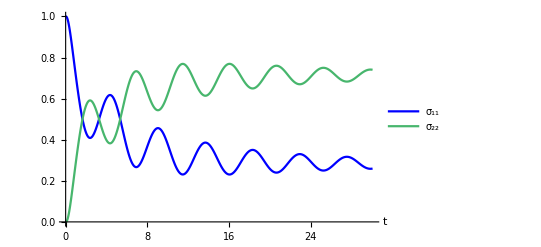

```mathematica
ListPlot[{σsite11Data,σsite22Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style[" σ_11 ",FontFamily->"Times New Roman"],Style[" σ_22 ",FontFamily->"Times New Roman"]}]
```

```mathematica
Reσsite12Data=Table[{n dt,Re[σsite[n][[1,2]]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.},{0.1,0.00152375},{0.15,0.00453157},{0.2,0.00892992},{0.25,0.0145826},{0.3,0.0213254},{0.35,0.0289822},{0.4,0.0373789},{0.45,0.0463546},{0.5,0.055768},{0.55,0.065501},{0.6,0.0754582},{0.65,0.0855642},{0.7,0.0957605},{0.75,0.106001},{0.8,0.116248},{0.85,0.12647},{0.9,0.136637},{0.95,0.14672},{1.,0.156689},{1.05,0.166511},{1.1,0.176153},{1.15,0.185579},{1.2,0.19475},{1.25,0.203626},{1.3,0.212167},{1.35,0.220331},{1.4,0.228077},{1.45,0.235364},{1.5,0.242151},{1.55,0.248399},{1.6,0.254072},{1.65,0.259135},{1.7,0.263556},{1.75,0.267305},{1.8,0.270355},{1.85,0.272683},{1.9,0.27427},{1.95,0.275099},{2.,0.275156},{2.05,0.274432},{2.1,0.272922},{2.15,0.270624},{2.2,0.267539},{2.25,0.263673},{2.3,0.259035},{2.35,0.253637},{2.4,0.247495},{2.45,0.240628},{2.5,0.23306},{2.55,0.224816},{2.6,0.215925},{2.65,0.206419},{2.7,0.196331},{2.75,0.185699},{2.8,0.174562},{2.85,0.162961},{2.9,0.150939},{2.95,0.138542},{3.,0.125816},{3.05,0.112808},{3.1,0.0995677},{3.15,0.0861446},{3.2,0.0725889},{3.25,0.0589511},{3.3,0.0452821},{3.35,0.0316323},{3.4,0.0180522},{3.45,0.00459154},{3.5,-0.0087008},{3.55,-0.0217768},{3.6,-0.0345898},{3.65,-0.0470943},{3.7,-0.0592468},{3.75,-0.0710052},{3.8,-0.0823298},{3.85,-0.0931826},{3.9,-0.103528},{3.95,-0.113334},{4.,-0.122569},{4.05,-0.131206},{4.1,-0.139221},{4.15,-0.14659},{4.2,-0.153296},{4.25,-0.159322},{4.3,-0.164656},{4.35,-0.169289},{4.4,-0.173213},{4.45,-0.176427},{4.5,-0.17893},{4.55,-0.180724},{4.6,-0.181818},{4.65,-0.182219},{4.7,-0.181942},{4.75,-0.181},{4.8,-0.179413},{4.85,-0.177201},{4.9,-0.174388},{4.95,-0.171},{5.,-0.167067},{5.05,-0.162618},{5.1,-0.157687},{5.15,-0.152308},{5.2,-0.146518},{5.25,-0.140355},{5.3,-0.133858},{5.35,-0.127069},{5.4,-0.120028},{5.45,-0.112778},{5.5,-0.105362},{5.55,-0.097824},{5.6,-0.0902065},{5.65,-0.0825535},{5.7,-0.0749083},{5.75,-0.0673138},{5.8,-0.0598122},{5.85,-0.052445},{5.9,-0.0452526},{5.95,-0.0382745},{6.,-0.0315486},{6.05,-0.0251112},{6.1,-0.0189973},{6.15,-0.0132399},{6.2,-0.0078698},{6.25,-0.00291614},{6.3,0.00159441},{6.35,0.00563741},{6.4,0.00919085},{6.45,0.0122352},{6.5,0.0147535},{6.55,0.0167314},{6.6,0.0181572},{6.65,0.0190221},{6.7,0.0193197},{6.75,0.0190466},{6.8,0.0182021},{6.85,0.0167882},{6.9,0.0148095},{6.95,0.0122733},{7.,0.00918969},{7.05,0.00557102},{7.1,0.00143225},{7.15,-0.0032093},{7.2,-0.00833407},{7.25,-0.0139203},{7.3,-0.0199441},{7.35,-0.0263799},{7.4,-0.0332},{7.45,-0.0403753},{7.5,-0.047875},{7.55,-0.0556672},{7.6,-0.0637185},{7.65,-0.0719947},{7.7,-0.0804606},{7.75,-0.0890803},{7.8,-0.0978175},{7.85,-0.106636},{7.9,-0.115497},{7.95,-0.124366},{8.,-0.133205},{8.05,-0.141978},{8.1,-0.150648},{8.15,-0.159181},{8.2,-0.167542},{8.25,-0.175698},{8.3,-0.183616},{8.35,-0.191266},{8.4,-0.198617},{8.45,-0.205642},{8.5,-0.212314},{8.55,-0.218609},{8.6,-0.224503},{8.65,-0.229977},{8.7,-0.23501},{8.75,-0.239587},{8.8,-0.243693},{8.85,-0.247316},{8.9,-0.250446},{8.95,-0.253075},{9.,-0.255198},{9.05,-0.256812},{9.1,-0.257917},{9.15,-0.258514},{9.2,-0.258607},{9.25,-0.258203},{9.3,-0.25731},{9.35,-0.255938},{9.4,-0.254102},{9.45,-0.251815},{9.5,-0.249094},{9.55,-0.245959},{9.6,-0.242429},{9.65,-0.238527},{9.7,-0.234276},{9.75,-0.229702},{9.8,-0.22483},{9.85,-0.219689},{9.9,-0.214307},{9.95,-0.208713},{10.,-0.202938},{10.05,-0.197013},{10.1,-0.190969},{10.15,-0.184837},{10.2,-0.178649},{10.25,-0.172438},{10.3,-0.166235},{10.35,-0.16007},{10.4,-0.153976},{10.45,-0.147982},{10.5,-0.142119},{10.55,-0.136415},{10.6,-0.130898},{10.65,-0.125595},{10.7,-0.120531},{10.75,-0.115732},{10.8,-0.111219},{10.85,-0.107014},{10.9,-0.103137},{10.95,-0.0996065},{11.,-0.0964382},{11.05,-0.093647},{11.1,-0.0912454},{11.15,-0.0892441},{11.2,-0.087652},{11.25,-0.0864759},{11.3,-0.0857206},{11.35,-0.0853889},{11.4,-0.0854815},{11.45,-0.0859972},{11.5,-0.0869329},{11.55,-0.0882834},{11.6,-0.0900416},{11.65,-0.0921986},{11.7,-0.0947436},{11.75,-0.0976641},{11.8,-0.100946},{11.85,-0.104573},{11.9,-0.108529},{11.95,-0.112794},{12.,-0.117349},{12.05,-0.122172},{12.1,-0.12724},{12.15,-0.132531},{12.2,-0.13802},{12.25,-0.143681},{12.3,-0.14949},{12.35,-0.155419},{12.4,-0.161442},{12.45,-0.167533},{12.5,-0.173663},{12.55,-0.179806},{12.6,-0.185935},{12.65,-0.192022},{12.7,-0.198043},{12.75,-0.203969},{12.8,-0.209777},{12.85,-0.215441},{12.9,-0.220937},{12.95,-0.226243},{13.,-0.231337},{13.05,-0.236197},{13.1,-0.240805},{13.15,-0.245141},{13.2,-0.249189},{13.25,-0.252933},{13.3,-0.25636},{13.35,-0.259456},{13.4,-0.262212},{13.45,-0.264617},{13.5,-0.266664},{13.55,-0.268348},{13.6,-0.269663},{13.65,-0.270609},{13.7,-0.271184},{13.75,-0.271388},{13.8,-0.271226},{13.85,-0.2707},{13.9,-0.269818},{13.95,-0.268587},{14.,-0.267015},{14.05,-0.265115},{14.1,-0.262897},{14.15,-0.260376},{14.2,-0.257566},{14.25,-0.254483},{14.3,-0.251145},{14.35,-0.24757},{14.4,-0.243776},{14.45,-0.239785},{14.5,-0.235617},{14.55,-0.231293},{14.6,-0.226836},{14.65,-0.222269},{14.7,-0.217613},{14.75,-0.212893},{14.8,-0.208132},{14.85,-0.203353},{14.9,-0.198579},{14.95,-0.193834},{15.,-0.18914},{15.05,-0.184519},{15.1,-0.179993},{15.15,-0.175585},{15.2,-0.171313},{15.25,-0.167199},{15.3,-0.163261},{15.35,-0.159516},{15.4,-0.155983},{15.45,-0.152676},{15.5,-0.149611},{15.55,-0.1468},{15.6,-0.144256},{15.65,-0.141991},{15.7,-0.140012},{15.75,-0.138329},{15.8,-0.136948},{15.85,-0.135873},{15.9,-0.13511},{15.95,-0.13466},{16.,-0.134523},{16.05,-0.134699},{16.1,-0.135187},{16.15,-0.135981},{16.2,-0.137078},{16.25,-0.13847},{16.3,-0.14015},{16.35,-0.142109},{16.4,-0.144337},{16.45,-0.146822},{16.5,-0.149551},{16.55,-0.152511},{16.6,-0.155688},{16.65,-0.159065},{16.7,-0.162626},{16.75,-0.166355},{16.8,-0.170232},{16.85,-0.174241},{16.9,-0.178361},{16.95,-0.182575},{17.,-0.186861},{17.05,-0.1912},{17.1,-0.195573},{17.15,-0.199958},{17.2,-0.204338},{17.25,-0.208691},{17.3,-0.212997},{17.35,-0.217239},{17.4,-0.221397},{17.45,-0.225454},{17.5,-0.22939},{17.55,-0.23319},{17.6,-0.236836},{17.65,-0.240315},{17.7,-0.24361},{17.75,-0.24671},{17.8,-0.2496},{17.85,-0.252269},{17.9,-0.254707},{17.95,-0.256905},{18.,-0.258854},{18.05,-0.260548},{18.1,-0.261981},{18.15,-0.263147},{18.2,-0.264045},{18.25,-0.264672},{18.3,-0.265028},{18.35,-0.265112},{18.4,-0.264928},{18.45,-0.264477},{18.5,-0.263765},{18.55,-0.262796},{18.6,-0.261578},{18.65,-0.260117},{18.7,-0.258424},{18.75,-0.256507},{18.8,-0.254377},{18.85,-0.252046},{18.9,-0.249528},{18.95,-0.246834},{19.,-0.243979},{19.05,-0.240977},{19.1,-0.237845},{19.15,-0.234598},{19.2,-0.231251},{19.25,-0.227822},{19.3,-0.224327},{19.35,-0.220784},{19.4,-0.217209},{19.45,-0.21362},{19.5,-0.210033},{19.55,-0.206467},{19.6,-0.202936},{19.65,-0.199459},{19.7,-0.196051},{19.75,-0.192727},{19.8,-0.189504},{19.85,-0.186394},{19.9,-0.183414},{19.95,-0.180575},{20.,-0.177891},{20.05,-0.175373},{20.1,-0.173031},{20.15,-0.170877},{20.2,-0.168919},{20.25,-0.167164},{20.3,-0.165621},{20.35,-0.164295},{20.4,-0.163191},{20.45,-0.162314},{20.5,-0.161665},{20.55,-0.161247},{20.6,-0.16106},{20.65,-0.161104},{20.7,-0.161378},{20.75,-0.161878},{20.8,-0.162602},{20.85,-0.163544},{20.9,-0.1647},{20.95,-0.166062},{21.,-0.167623},{21.05,-0.169374},{21.1,-0.171308},{21.15,-0.173412},{21.2,-0.175678},{21.25,-0.178093},{21.3,-0.180646},{21.35,-0.183324},{21.4,-0.186113},{21.45,-0.189001},{21.5,-0.191974},{21.55,-0.195017},{21.6,-0.198115},{21.65,-0.201256},{21.7,-0.204422},{21.75,-0.207601},{21.8,-0.210778},{21.85,-0.213937},{21.9,-0.217065},{21.95,-0.220147},{22.,-0.223169},{22.05,-0.226118},{22.1,-0.228982},{22.15,-0.231747},{22.2,-0.234401},{22.25,-0.236934},{22.3,-0.239333},{22.35,-0.24159},{22.4,-0.243695},{22.45,-0.245638},{22.5,-0.247413},{22.55,-0.249013},{22.6,-0.250431},{22.65,-0.251662},{22.7,-0.252702},{22.75,-0.253547},{22.8,-0.254195},{22.85,-0.254644},{22.9,-0.254894},{22.95,-0.254946},{23.,-0.254799},{23.05,-0.254457},{23.1,-0.253923},{23.15,-0.253199},{23.2,-0.252292},{23.25,-0.251207},{23.3,-0.24995},{23.35,-0.248528},{23.4,-0.246949},{23.45,-0.245221},{23.5,-0.243355},{23.55,-0.241358},{23.6,-0.239243},{23.65,-0.237019},{23.7,-0.234697},{23.75,-0.23229},{23.8,-0.229809},{23.85,-0.227266},{23.9,-0.224673},{23.95,-0.222044},{24.,-0.21939},{24.05,-0.216724},{24.1,-0.21406},{24.15,-0.211408},{24.2,-0.208782},{24.25,-0.206194},{24.3,-0.203656},{24.35,-0.201179},{24.4,-0.198775},{24.45,-0.196453},{24.5,-0.194225},{24.55,-0.192101},{24.6,-0.19009},{24.65,-0.188199},{24.7,-0.186439},{24.75,-0.184815},{24.8,-0.183335},{24.85,-0.182004},{24.9,-0.180828},{24.95,-0.179812},{25.,-0.178959},{25.05,-0.178273},{25.1,-0.177754},{25.15,-0.177406},{25.2,-0.177227},{25.25,-0.177219},{25.3,-0.17738},{25.35,-0.177708},{25.4,-0.178201},{25.45,-0.178856},{25.5,-0.179668},{25.55,-0.180632},{25.6,-0.181744},{25.65,-0.182997},{25.7,-0.184385},{25.75,-0.1859},{25.8,-0.187534},{25.85,-0.18928},{25.9,-0.191128},{25.95,-0.193069},{26.,-0.195094},{26.05,-0.197192},{26.1,-0.199354},{26.15,-0.20157},{26.2,-0.203828},{26.25,-0.206117},{26.3,-0.208428},{26.35,-0.21075},{26.4,-0.21307},{26.45,-0.21538},{26.5,-0.217668},{26.55,-0.219923},{26.6,-0.222137},{26.65,-0.224298},{26.7,-0.226397},{26.75,-0.228424},{26.8,-0.230372},{26.85,-0.232231},{26.9,-0.233994},{26.95,-0.235652},{27.,-0.2372},{27.05,-0.23863},{27.1,-0.239937},{27.15,-0.241115},{27.2,-0.242161},{27.25,-0.24307},{27.3,-0.243838},{27.35,-0.244464},{27.4,-0.244945},{27.45,-0.245281},{27.5,-0.24547},{27.55,-0.245513},{27.6,-0.24541},{27.65,-0.245164},{27.7,-0.244776},{27.75,-0.244249},{27.8,-0.243586},{27.85,-0.242792},{27.9,-0.241871},{27.95,-0.240828},{28.,-0.239669},{28.05,-0.238401},{28.1,-0.237029},{28.15,-0.235561},{28.2,-0.234005},{28.25,-0.232368},{28.3,-0.230659},{28.35,-0.228885},{28.4,-0.227056},{28.45,-0.225181},{28.5,-0.223269},{28.55,-0.221328},{28.6,-0.219369},{28.65,-0.2174},{28.7,-0.21543},{28.75,-0.213469},{28.8,-0.211526},{28.85,-0.20961},{28.9,-0.20773},{28.95,-0.205894},{29.,-0.20411},{29.05,-0.202387},{29.1,-0.200731},{29.15,-0.199151},{29.2,-0.197653},{29.25,-0.196244},{29.3,-0.194929},{29.35,-0.193715},{29.4,-0.192606},{29.45,-0.191606},{29.5,-0.19072},{29.55,-0.189951},{29.6,-0.189302},{29.65,-0.188774},{29.7,-0.188371},{29.75,-0.188092},{29.8,-0.187939},{29.85,-0.187911},{29.9,-0.188007},{29.95,-0.188227},{30.,-0.188569},{30.05,-0.189029}}

```mathematica
Imσsite12Data=Table[{n dt,Im[σsite[n][[1,2]]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.025},{0.1,0.049931},{0.15,0.0744526},{0.2,0.098248},{0.25,0.121041},{0.3,0.142605},{0.35,0.162772},{0.4,0.181427},{0.45,0.198502},{0.5,0.213968},{0.55,0.227826},{0.6,0.240092},{0.65,0.250799},{0.7,0.259981},{0.75,0.267676},{0.8,0.273919},{0.85,0.278745},{0.9,0.282184},{0.95,0.284268},{1.,0.285024},{1.05,0.284482},{1.1,0.282669},{1.15,0.279616},{1.2,0.275355},{1.25,0.269922},{1.3,0.263353},{1.35,0.25569},{1.4,0.246978},{1.45,0.237263},{1.5,0.226598},{1.55,0.215038},{1.6,0.202639},{1.65,0.189463},{1.7,0.175575},{1.75,0.16104},{1.8,0.145927},{1.85,0.130308},{1.9,0.114256},{1.95,0.0978435},{2.,0.0811469},{2.05,0.0642421},{2.1,0.0472058},{2.15,0.0301144},{2.2,0.0130445},{2.25,-0.00392799},{2.3,-0.0207282},{2.35,-0.0372823},{2.4,-0.0535182},{2.45,-0.0693655},{2.5,-0.0847561},{2.55,-0.0996243},{2.6,-0.113907},{2.65,-0.127545},{2.7,-0.140481},{2.75,-0.152663},{2.8,-0.16404},{2.85,-0.174568},{2.9,-0.184205},{2.95,-0.192914},{3.,-0.200664},{3.05,-0.207425},{3.1,-0.213175},{3.15,-0.217895},{3.2,-0.221571},{3.25,-0.224195},{3.3,-0.225763},{3.35,-0.226274},{3.4,-0.225736},{3.45,-0.224157},{3.5,-0.221554},{3.55,-0.217945},{3.6,-0.213355},{3.65,-0.207813},{3.7,-0.20135},{3.75,-0.194003},{3.8,-0.185812},{3.85,-0.176822},{3.9,-0.16708},{3.95,-0.156635},{4.,-0.145542},{4.05,-0.133856},{4.1,-0.121635},{4.15,-0.10894},{4.2,-0.095832},{4.25,-0.0823753},{4.3,-0.0686344},{4.35,-0.0546747},{4.4,-0.0405623},{4.45,-0.0263635},{4.5,-0.0121446},{4.55,0.00202859},{4.6,0.0160908},{4.65,0.0299778},{4.7,0.0436266},{4.75,0.0569757},{4.8,0.0699654},{4.85,0.0825382},{4.9,0.0946387},{4.95,0.106214},{5.,0.117215},{5.05,0.127594},{5.1,0.137308},{5.15,0.146315},{5.2,0.15458},{5.25,0.16207},{5.3,0.168754},{5.35,0.174608},{5.4,0.17961},{5.45,0.183743},{5.5,0.186994},{5.55,0.189354},{5.6,0.190818},{5.65,0.191385},{5.7,0.191059},{5.75,0.189848},{5.8,0.187764},{5.85,0.184822},{5.9,0.181041},{5.95,0.176446},{6.,0.171062},{6.05,0.164921},{6.1,0.158056},{6.15,0.150503},{6.2,0.142303},{6.25,0.133499},{6.3,0.124134},{6.35,0.114257},{6.4,0.103916},{6.45,0.0931636},{6.5,0.0820515},{6.55,0.070634},{6.6,0.0589661},{6.65,0.0471039},{6.7,0.0351035},{6.75,0.0230218},{6.8,0.0109153},{6.85,-0.00115968},{6.9,-0.0131472},{6.95,-0.0249922},{7.,-0.0366407},{7.05,-0.04804},{7.1,-0.0591388},{7.15,-0.0698876},{7.2,-0.0802389},{7.25,-0.0901473},{7.3,-0.0995699},{7.35,-0.108466},{7.4,-0.116798},{7.45,-0.124531},{7.5,-0.131634},{7.55,-0.138077},{7.6,-0.143834},{7.65,-0.148885},{7.7,-0.15321},{7.75,-0.156794},{7.8,-0.159626},{7.85,-0.161696},{7.9,-0.163002},{7.95,-0.163542},{8.,-0.163318},{8.05,-0.162337},{8.1,-0.160608},{8.15,-0.158145},{8.2,-0.154964},{8.25,-0.151085},{8.3,-0.146529},{8.35,-0.141324},{8.4,-0.135497},{8.45,-0.12908},{8.5,-0.122106},{8.55,-0.114612},{8.6,-0.106636},{8.65,-0.0982183},{8.7,-0.0894008},{8.75,-0.0802273},{8.8,-0.0707427},{8.85,-0.0609932},{8.9,-0.0510259},{8.95,-0.0408885},{9.,-0.0306292},{9.05,-0.0202965},{9.1,-0.00993894},{9.15,0.000395276},{9.2,0.0106583},{9.25,0.0208029},{9.3,0.0307827},{9.35,0.0405526},{9.4,0.0500686},{9.45,0.059288},{9.5,0.0681702},{9.55,0.0766761},{9.6,0.0847688},{9.65,0.0924134},{9.7,0.0995773},{9.75,0.106231},{9.8,0.112346},{9.85,0.117898},{9.9,0.122865},{9.95,0.127229},{10.,0.130971},{10.05,0.134081},{10.1,0.136546},{10.15,0.138361},{10.2,0.139521},{10.25,0.140024},{10.3,0.139874},{10.35,0.139075},{10.4,0.137635},{10.45,0.135565},{10.5,0.13288},{10.55,0.129595},{10.6,0.125729},{10.65,0.121306},{10.7,0.116348},{10.75,0.110884},{10.8,0.10494},{10.85,0.0985488},{10.9,0.0917424},{10.95,0.0845553},{11.,0.0770234},{11.05,0.0691839},{11.1,0.0610755},{11.15,0.0527375},{11.2,0.0442102},{11.25,0.0355345},{11.3,0.0267517},{11.35,0.0179033},{11.4,0.00903082},{11.45,0.000175686},{11.5,-0.0086211},{11.55,-0.0173191},{11.6,-0.0258785},{11.65,-0.0342604},{11.7,-0.0424273},{11.75,-0.0503424},{11.8,-0.0579708},{11.85,-0.0652789},{11.9,-0.072235},{11.95,-0.0788089},{12.,-0.0849729},{12.05,-0.0907008},{12.1,-0.0959692},{12.15,-0.100756},{12.2,-0.105044},{12.25,-0.108814},{12.3,-0.112054},{12.35,-0.114752},{12.4,-0.116898},{12.45,-0.118487},{12.5,-0.119515},{12.55,-0.119981},{12.6,-0.119886},{12.65,-0.119235},{12.7,-0.118034},{12.75,-0.116293},{12.8,-0.114023},{12.85,-0.111239},{12.9,-0.107956},{12.95,-0.104194},{13.,-0.0999722},{13.05,-0.0953146},{13.1,-0.0902451},{13.15,-0.0847902},{13.2,-0.0789778},{13.25,-0.0728371},{13.3,-0.066399},{13.35,-0.0596954},{13.4,-0.0527591},{13.45,-0.0456239},{13.5,-0.0383244},{13.55,-0.0308955},{13.6,-0.0233725},{13.65,-0.0157912},{13.7,-0.00818699},{13.75,-0.000595469},{13.8,0.0069482},{13.85,0.0144093},{13.9,0.0217537},{13.95,0.0289481},{14.,0.03596},{14.05,0.0427581},{14.1,0.0493123},{14.15,0.0555936},{14.2,0.0615748},{14.25,0.0672301},{14.3,0.0725353},{14.35,0.0774681},{14.4,0.0820081},{14.45,0.0861369},{14.5,0.0898379},{14.55,0.0930969},{14.6,0.0959017},{14.65,0.0982422},{14.7,0.100111},{14.75,0.101502},{14.8,0.102412},{14.85,0.10284},{14.9,0.102787},{14.95,0.102258},{15.,0.101256},{15.05,0.0997913},{15.1,0.0978724},{15.15,0.0955115},{15.2,0.0927227},{15.25,0.0895216},{15.3,0.0859259},{15.35,0.081955},{15.4,0.0776297},{15.45,0.0729726},{15.5,0.0680075},{15.55,0.0627595},{15.6,0.0572549},{15.65,0.0515209},{15.7,0.0455858},{15.75,0.0394783},{15.8,0.0332282},{15.85,0.0268653},{15.9,0.02042},{15.95,0.0139227},{16.,0.00740401},{16.05,0.00089434},{16.1,-0.00557613},{16.15,-0.0119776},{16.2,-0.0182808},{16.25,-0.0244571},{16.3,-0.0304786},{16.35,-0.0363184},{16.4,-0.0419506},{16.45,-0.0473503},{16.5,-0.0524941},{16.55,-0.0573598},{16.6,-0.0619266},{16.65,-0.0661752},{16.7,-0.0700881},{16.75,-0.0736493},{16.8,-0.0768446},{16.85,-0.0796617},{16.9,-0.0820898},{16.95,-0.0841204},{17.,-0.0857466},{17.05,-0.0869636},{17.1,-0.0877685},{17.15,-0.0881603},{17.2,-0.0881398},{17.25,-0.08771},{17.3,-0.0868755},{17.35,-0.0856429},{17.4,-0.0840207},{17.45,-0.0820188},{17.5,-0.0796493},{17.55,-0.0769255},{17.6,-0.0738623},{17.65,-0.0704765},{17.7,-0.0667857},{17.75,-0.0628092},{17.8,-0.0585673},{17.85,-0.0540816},{17.9,-0.0493745},{17.95,-0.0444693},{18.,-0.0393901},{18.05,-0.0341618},{18.1,-0.0288095},{18.15,-0.023359},{18.2,-0.0178363},{18.25,-0.0122674},{18.3,-0.00667865},{18.35,-0.00109605},{18.4,0.0044545},{18.45,0.0099474},{18.5,0.0153575},{18.55,0.0206603},{18.6,0.0258318},{18.65,0.0308488},{18.7,0.0356892},{18.75,0.0403315},{18.8,0.0447555},{18.85,0.0489421},{18.9,0.0528735},{18.95,0.0565331},{19.,0.0599057},{19.05,0.0629775},{19.1,0.0657362},{19.15,0.0681712},{19.2,0.0702733},{19.25,0.0720348},{19.3,0.07345},{19.35,0.0745145},{19.4,0.0752257},{19.45,0.0755827},{19.5,0.0755861},{19.55,0.0752384},{19.6,0.0745433},{19.65,0.0735066},{19.7,0.0721353},{19.75,0.0704379},{19.8,0.0684246},{19.85,0.0661068},{19.9,0.0634973},{19.95,0.0606101},{20.,0.0574605},{20.05,0.054065},{20.1,0.0504408},{20.15,0.0466064},{20.2,0.042581},{20.25,0.0383845},{20.3,0.0340376},{20.35,0.0295615},{20.4,0.0249778},{20.45,0.0203086},{20.5,0.0155761},{20.55,0.0108027},{20.6,0.00601092},{20.65,0.00122306},{20.7,-0.00353861},{20.75,-0.00825217},{20.8,-0.012896},{20.85,-0.0174491},{20.9,-0.0218907},{20.95,-0.0262012},{21.,-0.0303612},{21.05,-0.0343524},{21.1,-0.0381575},{21.15,-0.0417601},{21.2,-0.0451446},{21.25,-0.0482968},{21.3,-0.0512037},{21.35,-0.0538534},{21.4,-0.0562352},{21.45,-0.0583399},{21.5,-0.0601596},{21.55,-0.0616876},{21.6,-0.0629189},{21.65,-0.0638497},{21.7,-0.0644776},{21.75,-0.0648017},{21.8,-0.0648227},{21.85,-0.0645423},{21.9,-0.0639639},{21.95,-0.0630922},{22.,-0.0619332},{22.05,-0.0604941},{22.1,-0.0587835},{22.15,-0.0568113},{22.2,-0.0545881},{22.25,-0.0521262},{22.3,-0.0494384},{22.35,-0.0465389},{22.4,-0.0434424},{22.45,-0.0401646},{22.5,-0.0367221},{22.55,-0.0331318},{22.6,-0.0294115},{22.65,-0.0255793},{22.7,-0.0216537},{22.75,-0.0176537},{22.8,-0.0135982},{22.85,-0.00950658},{22.9,-0.00539797},{22.95,-0.00129161},{23.,0.00279344},{23.05,0.00683833},{23.1,0.0108245},{23.15,0.014734},{23.2,0.0185489},{23.25,0.0222523},{23.3,0.0258277},{23.35,0.0292593},{23.4,0.0325321},{23.45,0.035632},{23.5,0.0385458},{23.55,0.041261},{23.6,0.0437665},{23.65,0.046052},{23.7,0.0481084},{23.75,0.0499275},{23.8,0.0515026},{23.85,0.052828},{23.9,0.053899},{23.95,0.0547126},{24.,0.0552665},{24.05,0.0555599},{24.1,0.0555933},{24.15,0.0553682},{24.2,0.0548873},{24.25,0.0541546},{24.3,0.0531752},{24.35,0.0519552},{24.4,0.050502},{24.45,0.0488238},{24.5,0.0469299},{24.55,0.0448305},{24.6,0.0425369},{24.65,0.0400609},{24.7,0.0374152},{24.75,0.0346133},{24.8,0.0316692},{24.85,0.0285976},{24.9,0.0254135},{24.95,0.0221325},{25.,0.0187705},{25.05,0.0153437},{25.1,0.0118684},{25.15,0.008361},{25.2,0.00483813},{25.25,0.00131621},{25.3,-0.0021884},{25.35,-0.00565954},{25.4,-0.00908129},{25.45,-0.0124381},{25.5,-0.0157148},{25.55,-0.0188967},{25.6,-0.0219696},{25.65,-0.02492},{25.7,-0.027735},{25.75,-0.0304025},{25.8,-0.0329109},{25.85,-0.0352497},{25.9,-0.0374093},{25.95,-0.0393806},{26.,-0.0411559},{26.05,-0.0427282},{26.1,-0.0440914},{26.15,-0.0452408},{26.2,-0.0461723},{26.25,-0.0468832},{26.3,-0.0473714},{26.35,-0.0476364},{26.4,-0.0476782},{26.45,-0.0474983},{26.5,-0.0470988},{26.55,-0.0464832},{26.6,-0.0456558},{26.65,-0.0446217},{26.7,-0.0433871},{26.75,-0.0419593},{26.8,-0.0403459},{26.85,-0.0385559},{26.9,-0.0365986},{26.95,-0.0344843},{27.,-0.0322238},{27.05,-0.0298286},{27.1,-0.0273108},{27.15,-0.0246829},{27.2,-0.0219577},{27.25,-0.0191487},{27.3,-0.0162694},{27.35,-0.0133336},{27.4,-0.0103554},{27.45,-0.0073489},{27.5,-0.00432825},{27.55,-0.00130758},{27.6,0.00169908},{27.65,0.00467785},{27.7,0.00761507},{27.75,0.0104974},{27.8,0.0133118},{27.85,0.0160456},{27.9,0.0186866},{27.95,0.0212233},{28.,0.0236446},{28.05,0.0259398},{28.1,0.0280993},{28.15,0.0301139},{28.2,0.0319752},{28.25,0.0336755},{28.3,0.0352081},{28.35,0.0365669},{28.4,0.0377467},{28.45,0.0387434},{28.5,0.0395534},{28.55,0.0401743},{28.6,0.0406043},{28.65,0.0408429},{28.7,0.0408901},{28.75,0.0407471},{28.8,0.0404157},{28.85,0.0398987},{28.9,0.0391997},{28.95,0.0383233},{29.,0.0372747},{29.05,0.0360599},{29.1,0.0346856},{29.15,0.0331593},{29.2,0.031489},{29.25,0.0296836},{29.3,0.0277523},{29.35,0.0257049},{29.4,0.0235517},{29.45,0.0213034},{29.5,0.018971},{29.55,0.016566},{29.6,0.0141001},{29.65,0.011585},{29.7,0.00903283},{29.75,0.00645567},{29.8,0.00386565},{29.85,0.00127489},{29.9,-0.00130456},{29.95,-0.0038608},{30.,-0.0063821},{30.05,-0.00885698}}

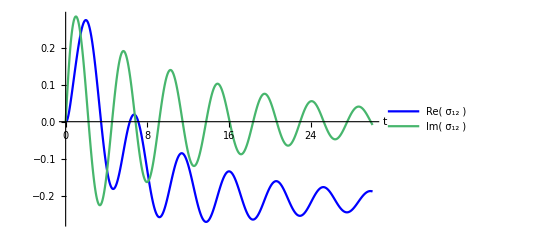

```mathematica
ListPlot[{Reσsite12Data,Imσsite12Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style[" Re( σ_12 ) ",FontFamily->"Times New Roman"],Style[" Im( σ_12 ) ",FontFamily->"Times New Roman"]}]
```

### CMRT numerical computation

```mathematica
Clear[dt,Nt]
dt=0.05;(*time span*)
Nt=600;(*Propagation time = Nt dt*)
```

#### Initial condition

Here we prepare the initial condition of the reduced density matrix from the previous RT calculation

```mathematica
σCMsite[0]=σsite[0];
```

```mathematica
σCM[0]=σ[0];
```

#### Population transfer

```mathematica
(*Propagation matrix*)
```

```mathematica
RCMpop[t_]:=DiagonalMatrix[Table[-Sum[kCM[t][[c,a]],{c,1,Length[v]}],{a,1,Length[v]}]]+kCM[t]
```

```mathematica
(*population evolution*)
```

```mathematica
Clear[σCMpop]
σCMpop[0]=Table[σ[0][[n,n]],{n,1,Length[v]}];(*initial condition*)
Monitor[For[i=0,i≤Nt,i++,σCMpop[i+1]=(IdentityMatrix[Length[v]]+RCMpop[i dt]dt).σCMpop[i]];,Row[{ProgressIndicator[i,{0,Nt}],i+1},""]]
Clear[i]
```

```mathematica
σCMpop11Data=Table[{n dt,σCMpop[n][[1]]},{n,0,Nt+1}]
```

{{0.,0.146447},{0.05,0.146447},{0.1,0.147287},{0.15,0.148946},{0.2,0.151378},{0.25,0.154521},{0.3,0.158299},{0.35,0.162631},{0.4,0.167432},{0.45,0.17262},{0.5,0.178118},{0.55,0.183855},{0.6,0.189768},{0.65,0.1958},{0.7,0.201905},{0.75,0.208041},{0.8,0.214174},{0.85,0.220276},{0.9,0.226325},{0.95,0.232303},{1.,0.238199},{1.05,0.244002},{1.1,0.249707},{1.15,0.255311},{1.2,0.260813},{1.25,0.266215},{1.3,0.271518},{1.35,0.276726},{1.4,0.281844},{1.45,0.286875},{1.5,0.291825},{1.55,0.296699},{1.6,0.301501},{1.65,0.306237},{1.7,0.310911},{1.75,0.315528},{1.8,0.320091},{1.85,0.324603},{1.9,0.329069},{1.95,0.333492},{2.,0.337872},{2.05,0.342214},{2.1,0.346519},{2.15,0.350789},{2.2,0.355025},{2.25,0.359228},{2.3,0.363399},{2.35,0.36754},{2.4,0.37165},{2.45,0.37573},{2.5,0.379781},{2.55,0.383802},{2.6,0.387794},{2.65,0.391758},{2.7,0.395692},{2.75,0.399597},{2.8,0.403473},{2.85,0.40732},{2.9,0.411137},{2.95,0.414925},{3.,0.418683},{3.05,0.422411},{3.1,0.42611},{3.15,0.429778},{3.2,0.433416},{3.25,0.437024},{3.3,0.440601},{3.35,0.444148},{3.4,0.447664},{3.45,0.451149},{3.5,0.454604},{3.55,0.458028},{3.6,0.461422},{3.65,0.464785},{3.7,0.468117},{3.75,0.471418},{3.8,0.474689},{3.85,0.47793},{3.9,0.48114},{3.95,0.48432},{4.,0.48747},{4.05,0.49059},{4.1,0.49368},{4.15,0.49674},{4.2,0.499771},{4.25,0.502773},{4.3,0.505746},{4.35,0.508689},{4.4,0.511604},{4.45,0.51449},{4.5,0.517348},{4.55,0.520178},{4.6,0.52298},{4.65,0.525755},{4.7,0.528501},{4.75,0.531221},{4.8,0.533914},{4.85,0.53658},{4.9,0.53922},{4.95,0.541833},{5.,0.54442},{5.05,0.546982},{5.1,0.549518},{5.15,0.552028},{5.2,0.554514},{5.25,0.556975},{5.3,0.559411},{5.35,0.561823},{5.4,0.564211},{5.45,0.566575},{5.5,0.568915},{5.55,0.571232},{5.6,0.573526},{5.65,0.575797},{5.7,0.578045},{5.75,0.580271},{5.8,0.582475},{5.85,0.584656},{5.9,0.586816},{5.95,0.588954},{6.,0.591071},{6.05,0.593167},{6.1,0.595242},{6.15,0.597296},{6.2,0.59933},{6.25,0.601344},{6.3,0.603337},{6.35,0.605311},{6.4,0.607265},{6.45,0.6092},{6.5,0.611115},{6.55,0.613012},{6.6,0.61489},{6.65,0.616749},{6.7,0.61859},{6.75,0.620412},{6.8,0.622217},{6.85,0.624003},{6.9,0.625773},{6.95,0.627524},{7.,0.629258},{7.05,0.630976},{7.1,0.632676},{7.15,0.63436},{7.2,0.636027},{7.25,0.637678},{7.3,0.639312},{7.35,0.64093},{7.4,0.642533},{7.45,0.64412},{7.5,0.645691},{7.55,0.647247},{7.6,0.648788},{7.65,0.650313},{7.7,0.651824},{7.75,0.65332},{7.8,0.654802},{7.85,0.656268},{7.9,0.657721},{7.95,0.659159},{8.,0.660584},{8.05,0.661994},{8.1,0.663391},{8.15,0.664774},{8.2,0.666144},{8.25,0.6675},{8.3,0.668843},{8.35,0.670173},{8.4,0.671491},{8.45,0.672795},{8.5,0.674086},{8.55,0.675365},{8.6,0.676632},{8.65,0.677886},{8.7,0.679128},{8.75,0.680358},{8.8,0.681576},{8.85,0.682782},{8.9,0.683976},{8.95,0.685159},{9.,0.68633},{9.05,0.68749},{9.1,0.688638},{9.15,0.689775},{9.2,0.690901},{9.25,0.692016},{9.3,0.693121},{9.35,0.694214},{9.4,0.695297},{9.45,0.696369},{9.5,0.69743},{9.55,0.698481},{9.6,0.699522},{9.65,0.700553},{9.7,0.701574},{9.75,0.702584},{9.8,0.703585},{9.85,0.704575},{9.9,0.705556},{9.95,0.706528},{10.,0.70749},{10.05,0.708442},{10.1,0.709385},{10.15,0.710319},{10.2,0.711243},{10.25,0.712159},{10.3,0.713065},{10.35,0.713963},{10.4,0.714851},{10.45,0.715731},{10.5,0.716602},{10.55,0.717465},{10.6,0.718319},{10.65,0.719165},{10.7,0.720002},{10.75,0.720831},{10.8,0.721652},{10.85,0.722464},{10.9,0.723269},{10.95,0.724066},{11.,0.724855},{11.05,0.725636},{11.1,0.726409},{11.15,0.727175},{11.2,0.727933},{11.25,0.728684},{11.3,0.729427},{11.35,0.730163},{11.4,0.730892},{11.45,0.731613},{11.5,0.732328},{11.55,0.733035},{11.6,0.733736},{11.65,0.734429},{11.7,0.735116},{11.75,0.735796},{11.8,0.736469},{11.85,0.737136},{11.9,0.737796},{11.95,0.738449},{12.,0.739097},{12.05,0.739737},{12.1,0.740372},{12.15,0.741},{12.2,0.741623},{12.25,0.742239},{12.3,0.742849},{12.35,0.743453},{12.4,0.744051},{12.45,0.744643},{12.5,0.745229},{12.55,0.74581},{12.6,0.746385},{12.65,0.746955},{12.7,0.747519},{12.75,0.748077},{12.8,0.74863},{12.85,0.749177},{12.9,0.749719},{12.95,0.750256},{13.,0.750788},{13.05,0.751314},{13.1,0.751836},{13.15,0.752352},{13.2,0.752863},{13.25,0.753369},{13.3,0.75387},{13.35,0.754366},{13.4,0.754858},{13.45,0.755345},{13.5,0.755826},{13.55,0.756304},{13.6,0.756776},{13.65,0.757244},{13.7,0.757707},{13.75,0.758166},{13.8,0.75862},{13.85,0.75907},{13.9,0.759516},{13.95,0.759957},{14.,0.760393},{14.05,0.760826},{14.1,0.761254},{14.15,0.761678},{14.2,0.762098},{14.25,0.762514},{14.3,0.762926},{14.35,0.763333},{14.4,0.763737},{14.45,0.764137},{14.5,0.764532},{14.55,0.764924},{14.6,0.765312},{14.65,0.765696},{14.7,0.766077},{14.75,0.766453},{14.8,0.766826},{14.85,0.767196},{14.9,0.767561},{14.95,0.767923},{15.,0.768282},{15.05,0.768637},{15.1,0.768988},{15.15,0.769336},{15.2,0.769681},{15.25,0.770022},{15.3,0.77036},{15.35,0.770694},{15.4,0.771025},{15.45,0.771353},{15.5,0.771678},{15.55,0.772},{15.6,0.772318},{15.65,0.772633},{15.7,0.772945},{15.75,0.773254},{15.8,0.77356},{15.85,0.773863},{15.9,0.774163},{15.95,0.77446},{16.,0.774754},{16.05,0.775045},{16.1,0.775334},{16.15,0.775619},{16.2,0.775902},{16.25,0.776182},{16.3,0.776459},{16.35,0.776733},{16.4,0.777005},{16.45,0.777274},{16.5,0.77754},{16.55,0.777804},{16.6,0.778065},{16.65,0.778324},{16.7,0.77858},{16.75,0.778834},{16.8,0.779085},{16.85,0.779333},{16.9,0.77958},{16.95,0.779823},{17.,0.780065},{17.05,0.780304},{17.1,0.780541},{17.15,0.780775},{17.2,0.781007},{17.25,0.781237},{17.3,0.781464},{17.35,0.78169},{17.4,0.781913},{17.45,0.782134},{17.5,0.782353},{17.55,0.782569},{17.6,0.782784},{17.65,0.782996},{17.7,0.783207},{17.75,0.783415},{17.8,0.783621},{17.85,0.783826},{17.9,0.784028},{17.95,0.784228},{18.,0.784426},{18.05,0.784623},{18.1,0.784817},{18.15,0.78501},{18.2,0.7852},{18.25,0.785389},{18.3,0.785576},{18.35,0.785761},{18.4,0.785945},{18.45,0.786126},{18.5,0.786306},{18.55,0.786484},{18.6,0.78666},{18.65,0.786835},{18.7,0.787007},{18.75,0.787179},{18.8,0.787348},{18.85,0.787516},{18.9,0.787682},{18.95,0.787846},{19.,0.788009},{19.05,0.788171},{19.1,0.78833},{19.15,0.788488},{19.2,0.788645},{19.25,0.7888},{19.3,0.788953},{19.35,0.789105},{19.4,0.789256},{19.45,0.789405},{19.5,0.789552},{19.55,0.789698},{19.6,0.789843},{19.65,0.789986},{19.7,0.790128},{19.75,0.790269},{19.8,0.790408},{19.85,0.790545},{19.9,0.790681},{19.95,0.790816},{20.,0.79095},{20.05,0.791082},{20.1,0.791213},{20.15,0.791343},{20.2,0.791472},{20.25,0.791599},{20.3,0.791725},{20.35,0.791849},{20.4,0.791973},{20.45,0.792095},{20.5,0.792216},{20.55,0.792336},{20.6,0.792455},{20.65,0.792572},{20.7,0.792688},{20.75,0.792804},{20.8,0.792918},{20.85,0.793031},{20.9,0.793142},{20.95,0.793253},{21.,0.793363},{21.05,0.793471},{21.1,0.793579},{21.15,0.793685},{21.2,0.793791},{21.25,0.793895},{21.3,0.793998},{21.35,0.794101},{21.4,0.794202},{21.45,0.794302},{21.5,0.794402},{21.55,0.7945},{21.6,0.794598},{21.65,0.794694},{21.7,0.79479},{21.75,0.794884},{21.8,0.794978},{21.85,0.795071},{21.9,0.795162},{21.95,0.795253},{22.,0.795343},{22.05,0.795433},{22.1,0.795521},{22.15,0.795608},{22.2,0.795695},{22.25,0.795781},{22.3,0.795866},{22.35,0.79595},{22.4,0.796033},{22.45,0.796115},{22.5,0.796197},{22.55,0.796278},{22.6,0.796358},{22.65,0.796437},{22.7,0.796516},{22.75,0.796593},{22.8,0.79667},{22.85,0.796746},{22.9,0.796822},{22.95,0.796897},{23.,0.796971},{23.05,0.797044},{23.1,0.797116},{23.15,0.797188},{23.2,0.797259},{23.25,0.79733},{23.3,0.797399},{23.35,0.797468},{23.4,0.797537},{23.45,0.797605},{23.5,0.797672},{23.55,0.797738},{23.6,0.797804},{23.65,0.797869},{23.7,0.797933},{23.75,0.797997},{23.8,0.79806},{23.85,0.798123},{23.9,0.798185},{23.95,0.798246},{24.,0.798307},{24.05,0.798367},{24.1,0.798426},{24.15,0.798485},{24.2,0.798544},{24.25,0.798601},{24.3,0.798659},{24.35,0.798715},{24.4,0.798771},{24.45,0.798827},{24.5,0.798882},{24.55,0.798936},{24.6,0.79899},{24.65,0.799044},{24.7,0.799097},{24.75,0.799149},{24.8,0.799201},{24.85,0.799252},{24.9,0.799303},{24.95,0.799353},{25.,0.799403},{25.05,0.799452},{25.1,0.799501},{25.15,0.799549},{25.2,0.799597},{25.25,0.799645},{25.3,0.799692},{25.35,0.799738},{25.4,0.799784},{25.45,0.79983},{25.5,0.799875},{25.55,0.79992},{25.6,0.799964},{25.65,0.800008},{25.7,0.800051},{25.75,0.800094},{25.8,0.800136},{25.85,0.800179},{25.9,0.80022},{25.95,0.800262},{26.,0.800302},{26.05,0.800343},{26.1,0.800383},{26.15,0.800423},{26.2,0.800462},{26.25,0.800501},{26.3,0.80054},{26.35,0.800578},{26.4,0.800616},{26.45,0.800653},{26.5,0.80069},{26.55,0.800727},{26.6,0.800763},{26.65,0.800799},{26.7,0.800835},{26.75,0.80087},{26.8,0.800905},{26.85,0.80094},{26.9,0.800974},{26.95,0.801008},{27.,0.801041},{27.05,0.801075},{27.1,0.801108},{27.15,0.80114},{27.2,0.801172},{27.25,0.801204},{27.3,0.801236},{27.35,0.801267},{27.4,0.801299},{27.45,0.801329},{27.5,0.80136},{27.55,0.80139},{27.6,0.80142},{27.65,0.801449},{27.7,0.801479},{27.75,0.801508},{27.8,0.801536},{27.85,0.801565},{27.9,0.801593},{27.95,0.801621},{28.,0.801648},{28.05,0.801676},{28.1,0.801703},{28.15,0.801729},{28.2,0.801756},{28.25,0.801782},{28.3,0.801808},{28.35,0.801834},{28.4,0.801859},{28.45,0.801885},{28.5,0.80191},{28.55,0.801934},{28.6,0.801959},{28.65,0.801983},{28.7,0.802007},{28.75,0.802031},{28.8,0.802055},{28.85,0.802078},{28.9,0.802101},{28.95,0.802124},{29.,0.802146},{29.05,0.802169},{29.1,0.802191},{29.15,0.802213},{29.2,0.802235},{29.25,0.802256},{29.3,0.802278},{29.35,0.802299},{29.4,0.80232},{29.45,0.80234},{29.5,0.802361},{29.55,0.802381},{29.6,0.802401},{29.65,0.802421},{29.7,0.802441},{29.75,0.80246},{29.8,0.80248},{29.85,0.802499},{29.9,0.802518},{29.95,0.802536},{30.,0.802555},{30.05,0.802573}}

```mathematica
σCMpop22Data=Table[{n dt,σCMpop[n][[2]]},{n,0,Nt+1}]
```

{{0.,0.853553},{0.05,0.853553},{0.1,0.852713},{0.15,0.851054},{0.2,0.848622},{0.25,0.845479},{0.3,0.841701},{0.35,0.837369},{0.4,0.832568},{0.45,0.82738},{0.5,0.821882},{0.55,0.816145},{0.6,0.810232},{0.65,0.8042},{0.7,0.798095},{0.75,0.791959},{0.8,0.785826},{0.85,0.779724},{0.9,0.773675},{0.95,0.767697},{1.,0.761801},{1.05,0.755998},{1.1,0.750293},{1.15,0.744689},{1.2,0.739187},{1.25,0.733785},{1.3,0.728482},{1.35,0.723274},{1.4,0.718156},{1.45,0.713125},{1.5,0.708175},{1.55,0.703301},{1.6,0.698499},{1.65,0.693763},{1.7,0.689089},{1.75,0.684472},{1.8,0.679909},{1.85,0.675397},{1.9,0.670931},{1.95,0.666508},{2.,0.662128},{2.05,0.657786},{2.1,0.653481},{2.15,0.649211},{2.2,0.644975},{2.25,0.640772},{2.3,0.636601},{2.35,0.63246},{2.4,0.62835},{2.45,0.62427},{2.5,0.620219},{2.55,0.616198},{2.6,0.612206},{2.65,0.608242},{2.7,0.604308},{2.75,0.600403},{2.8,0.596527},{2.85,0.59268},{2.9,0.588863},{2.95,0.585075},{3.,0.581317},{3.05,0.577589},{3.1,0.57389},{3.15,0.570222},{3.2,0.566584},{3.25,0.562976},{3.3,0.559399},{3.35,0.555852},{3.4,0.552336},{3.45,0.548851},{3.5,0.545396},{3.55,0.541972},{3.6,0.538578},{3.65,0.535215},{3.7,0.531883},{3.75,0.528582},{3.8,0.525311},{3.85,0.52207},{3.9,0.51886},{3.95,0.51568},{4.,0.51253},{4.05,0.50941},{4.1,0.50632},{4.15,0.50326},{4.2,0.500229},{4.25,0.497227},{4.3,0.494254},{4.35,0.491311},{4.4,0.488396},{4.45,0.48551},{4.5,0.482652},{4.55,0.479822},{4.6,0.47702},{4.65,0.474245},{4.7,0.471499},{4.75,0.468779},{4.8,0.466086},{4.85,0.46342},{4.9,0.46078},{4.95,0.458167},{5.,0.45558},{5.05,0.453018},{5.1,0.450482},{5.15,0.447972},{5.2,0.445486},{5.25,0.443025},{5.3,0.440589},{5.35,0.438177},{5.4,0.435789},{5.45,0.433425},{5.5,0.431085},{5.55,0.428768},{5.6,0.426474},{5.65,0.424203},{5.7,0.421955},{5.75,0.419729},{5.8,0.417525},{5.85,0.415344},{5.9,0.413184},{5.95,0.411046},{6.,0.408929},{6.05,0.406833},{6.1,0.404758},{6.15,0.402704},{6.2,0.40067},{6.25,0.398656},{6.3,0.396663},{6.35,0.394689},{6.4,0.392735},{6.45,0.3908},{6.5,0.388885},{6.55,0.386988},{6.6,0.38511},{6.65,0.383251},{6.7,0.38141},{6.75,0.379588},{6.8,0.377783},{6.85,0.375997},{6.9,0.374227},{6.95,0.372476},{7.,0.370742},{7.05,0.369024},{7.1,0.367324},{7.15,0.36564},{7.2,0.363973},{7.25,0.362322},{7.3,0.360688},{7.35,0.35907},{7.4,0.357467},{7.45,0.35588},{7.5,0.354309},{7.55,0.352753},{7.6,0.351212},{7.65,0.349687},{7.7,0.348176},{7.75,0.34668},{7.8,0.345198},{7.85,0.343732},{7.9,0.342279},{7.95,0.340841},{8.,0.339416},{8.05,0.338006},{8.1,0.336609},{8.15,0.335226},{8.2,0.333856},{8.25,0.3325},{8.3,0.331157},{8.35,0.329827},{8.4,0.328509},{8.45,0.327205},{8.5,0.325914},{8.55,0.324635},{8.6,0.323368},{8.65,0.322114},{8.7,0.320872},{8.75,0.319642},{8.8,0.318424},{8.85,0.317218},{8.9,0.316024},{8.95,0.314841},{9.,0.31367},{9.05,0.31251},{9.1,0.311362},{9.15,0.310225},{9.2,0.309099},{9.25,0.307984},{9.3,0.306879},{9.35,0.305786},{9.4,0.304703},{9.45,0.303631},{9.5,0.30257},{9.55,0.301519},{9.6,0.300478},{9.65,0.299447},{9.7,0.298426},{9.75,0.297416},{9.8,0.296415},{9.85,0.295425},{9.9,0.294444},{9.95,0.293472},{10.,0.29251},{10.05,0.291558},{10.1,0.290615},{10.15,0.289681},{10.2,0.288757},{10.25,0.287841},{10.3,0.286935},{10.35,0.286037},{10.4,0.285149},{10.45,0.284269},{10.5,0.283398},{10.55,0.282535},{10.6,0.281681},{10.65,0.280835},{10.7,0.279998},{10.75,0.279169},{10.8,0.278348},{10.85,0.277536},{10.9,0.276731},{10.95,0.275934},{11.,0.275145},{11.05,0.274364},{11.1,0.273591},{11.15,0.272825},{11.2,0.272067},{11.25,0.271316},{11.3,0.270573},{11.35,0.269837},{11.4,0.269108},{11.45,0.268387},{11.5,0.267672},{11.55,0.266965},{11.6,0.266264},{11.65,0.265571},{11.7,0.264884},{11.75,0.264204},{11.8,0.263531},{11.85,0.262864},{11.9,0.262204},{11.95,0.261551},{12.,0.260903},{12.05,0.260263},{12.1,0.259628},{12.15,0.259},{12.2,0.258377},{12.25,0.257761},{12.3,0.257151},{12.35,0.256547},{12.4,0.255949},{12.45,0.255357},{12.5,0.254771},{12.55,0.25419},{12.6,0.253615},{12.65,0.253045},{12.7,0.252481},{12.75,0.251923},{12.8,0.25137},{12.85,0.250823},{12.9,0.250281},{12.95,0.249744},{13.,0.249212},{13.05,0.248686},{13.1,0.248164},{13.15,0.247648},{13.2,0.247137},{13.25,0.246631},{13.3,0.24613},{13.35,0.245634},{13.4,0.245142},{13.45,0.244655},{13.5,0.244174},{13.55,0.243696},{13.6,0.243224},{13.65,0.242756},{13.7,0.242293},{13.75,0.241834},{13.8,0.24138},{13.85,0.24093},{13.9,0.240484},{13.95,0.240043},{14.,0.239607},{14.05,0.239174},{14.1,0.238746},{14.15,0.238322},{14.2,0.237902},{14.25,0.237486},{14.3,0.237074},{14.35,0.236667},{14.4,0.236263},{14.45,0.235863},{14.5,0.235468},{14.55,0.235076},{14.6,0.234688},{14.65,0.234304},{14.7,0.233923},{14.75,0.233547},{14.8,0.233174},{14.85,0.232804},{14.9,0.232439},{14.95,0.232077},{15.,0.231718},{15.05,0.231363},{15.1,0.231012},{15.15,0.230664},{15.2,0.230319},{15.25,0.229978},{15.3,0.22964},{15.35,0.229306},{15.4,0.228975},{15.45,0.228647},{15.5,0.228322},{15.55,0.228},{15.6,0.227682},{15.65,0.227367},{15.7,0.227055},{15.75,0.226746},{15.8,0.22644},{15.85,0.226137},{15.9,0.225837},{15.95,0.22554},{16.,0.225246},{16.05,0.224955},{16.1,0.224666},{16.15,0.224381},{16.2,0.224098},{16.25,0.223818},{16.3,0.223541},{16.35,0.223267},{16.4,0.222995},{16.45,0.222726},{16.5,0.22246},{16.55,0.222196},{16.6,0.221935},{16.65,0.221676},{16.7,0.22142},{16.75,0.221166},{16.8,0.220915},{16.85,0.220667},{16.9,0.22042},{16.95,0.220177},{17.,0.219935},{17.05,0.219696},{17.1,0.219459},{17.15,0.219225},{17.2,0.218993},{17.25,0.218763},{17.3,0.218536},{17.35,0.21831},{17.4,0.218087},{17.45,0.217866},{17.5,0.217647},{17.55,0.217431},{17.6,0.217216},{17.65,0.217004},{17.7,0.216793},{17.75,0.216585},{17.8,0.216379},{17.85,0.216174},{17.9,0.215972},{17.95,0.215772},{18.,0.215574},{18.05,0.215377},{18.1,0.215183},{18.15,0.21499},{18.2,0.2148},{18.25,0.214611},{18.3,0.214424},{18.35,0.214239},{18.4,0.214055},{18.45,0.213874},{18.5,0.213694},{18.55,0.213516},{18.6,0.21334},{18.65,0.213165},{18.7,0.212993},{18.75,0.212821},{18.8,0.212652},{18.85,0.212484},{18.9,0.212318},{18.95,0.212154},{19.,0.211991},{19.05,0.211829},{19.1,0.21167},{19.15,0.211512},{19.2,0.211355},{19.25,0.2112},{19.3,0.211047},{19.35,0.210895},{19.4,0.210744},{19.45,0.210595},{19.5,0.210448},{19.55,0.210302},{19.6,0.210157},{19.65,0.210014},{19.7,0.209872},{19.75,0.209731},{19.8,0.209592},{19.85,0.209455},{19.9,0.209319},{19.95,0.209184},{20.,0.20905},{20.05,0.208918},{20.1,0.208787},{20.15,0.208657},{20.2,0.208528},{20.25,0.208401},{20.3,0.208275},{20.35,0.208151},{20.4,0.208027},{20.45,0.207905},{20.5,0.207784},{20.55,0.207664},{20.6,0.207545},{20.65,0.207428},{20.7,0.207312},{20.75,0.207196},{20.8,0.207082},{20.85,0.206969},{20.9,0.206858},{20.95,0.206747},{21.,0.206637},{21.05,0.206529},{21.1,0.206421},{21.15,0.206315},{21.2,0.206209},{21.25,0.206105},{21.3,0.206002},{21.35,0.205899},{21.4,0.205798},{21.45,0.205698},{21.5,0.205598},{21.55,0.2055},{21.6,0.205402},{21.65,0.205306},{21.7,0.20521},{21.75,0.205116},{21.8,0.205022},{21.85,0.204929},{21.9,0.204838},{21.95,0.204747},{22.,0.204657},{22.05,0.204567},{22.1,0.204479},{22.15,0.204392},{22.2,0.204305},{22.25,0.204219},{22.3,0.204134},{22.35,0.20405},{22.4,0.203967},{22.45,0.203885},{22.5,0.203803},{22.55,0.203722},{22.6,0.203642},{22.65,0.203563},{22.7,0.203484},{22.75,0.203407},{22.8,0.20333},{22.85,0.203254},{22.9,0.203178},{22.95,0.203103},{23.,0.203029},{23.05,0.202956},{23.1,0.202884},{23.15,0.202812},{23.2,0.202741},{23.25,0.20267},{23.3,0.202601},{23.35,0.202532},{23.4,0.202463},{23.45,0.202395},{23.5,0.202328},{23.55,0.202262},{23.6,0.202196},{23.65,0.202131},{23.7,0.202067},{23.75,0.202003},{23.8,0.20194},{23.85,0.201877},{23.9,0.201815},{23.95,0.201754},{24.,0.201693},{24.05,0.201633},{24.1,0.201574},{24.15,0.201515},{24.2,0.201456},{24.25,0.201399},{24.3,0.201341},{24.35,0.201285},{24.4,0.201229},{24.45,0.201173},{24.5,0.201118},{24.55,0.201064},{24.6,0.20101},{24.65,0.200956},{24.7,0.200903},{24.75,0.200851},{24.8,0.200799},{24.85,0.200748},{24.9,0.200697},{24.95,0.200647},{25.,0.200597},{25.05,0.200548},{25.1,0.200499},{25.15,0.200451},{25.2,0.200403},{25.25,0.200355},{25.3,0.200308},{25.35,0.200262},{25.4,0.200216},{25.45,0.20017},{25.5,0.200125},{25.55,0.20008},{25.6,0.200036},{25.65,0.199992},{25.7,0.199949},{25.75,0.199906},{25.8,0.199864},{25.85,0.199821},{25.9,0.19978},{25.95,0.199738},{26.,0.199698},{26.05,0.199657},{26.1,0.199617},{26.15,0.199577},{26.2,0.199538},{26.25,0.199499},{26.3,0.19946},{26.35,0.199422},{26.4,0.199384},{26.45,0.199347},{26.5,0.19931},{26.55,0.199273},{26.6,0.199237},{26.65,0.199201},{26.7,0.199165},{26.75,0.19913},{26.8,0.199095},{26.85,0.19906},{26.9,0.199026},{26.95,0.198992},{27.,0.198959},{27.05,0.198925},{27.1,0.198892},{27.15,0.19886},{27.2,0.198828},{27.25,0.198796},{27.3,0.198764},{27.35,0.198733},{27.4,0.198701},{27.45,0.198671},{27.5,0.19864},{27.55,0.19861},{27.6,0.19858},{27.65,0.198551},{27.7,0.198521},{27.75,0.198492},{27.8,0.198464},{27.85,0.198435},{27.9,0.198407},{27.95,0.198379},{28.,0.198352},{28.05,0.198324},{28.1,0.198297},{28.15,0.198271},{28.2,0.198244},{28.25,0.198218},{28.3,0.198192},{28.35,0.198166},{28.4,0.198141},{28.45,0.198115},{28.5,0.19809},{28.55,0.198066},{28.6,0.198041},{28.65,0.198017},{28.7,0.197993},{28.75,0.197969},{28.8,0.197945},{28.85,0.197922},{28.9,0.197899},{28.95,0.197876},{29.,0.197854},{29.05,0.197831},{29.1,0.197809},{29.15,0.197787},{29.2,0.197765},{29.25,0.197744},{29.3,0.197722},{29.35,0.197701},{29.4,0.19768},{29.45,0.19766},{29.5,0.197639},{29.55,0.197619},{29.6,0.197599},{29.65,0.197579},{29.7,0.197559},{29.75,0.19754},{29.8,0.19752},{29.85,0.197501},{29.9,0.197482},{29.95,0.197464},{30.,0.197445},{30.05,0.197427}}

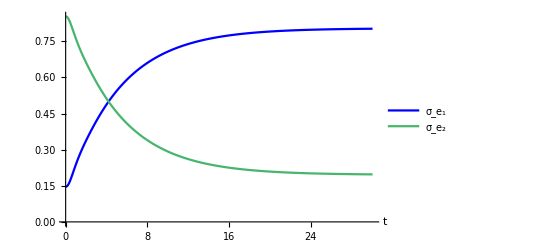

```mathematica
ListPlot[{σCMpop11Data,σCMpop22Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["σ_e_1",FontFamily->"Times New Roman"],Style["σ_e_2",FontFamily->"Times New Roman"]}]
```

#### Coherence dephasing

```mathematica
(*including pure dephasing, energy eigenvalue, energy shift,transfer-induced dephasing*)
```

```mathematica
RCMcoh[t_]:=DiagonalMatrix[Drop[Flatten[-ΓCM[t]+Table[-ⅈ(w[[a]]-w[[b]]),{a,1,Length[v]},{b,1,Length[v]}]+Table[ⅈ δCM[t][[a,b]],{a,1,Length[v]},{b,1,Length[v]}]+Table[-1/2 Sum[kCM[t][[c,a]]+kCM[t][[c,b]],{c,1,Length[v]}],{a,1,Length[v]},{b,1,Length[v]}]],{1,Length[v]^2,Length[v]+1}]]
```

```mathematica
(*coherence evolution*)
```

```mathematica
Clear[σCMcoh]
σCMcoh[0]=Drop[Flatten[ReplacePart[σ[0],Table[{n,n},{n,1,Length[v]}]->0]],{1,Length[v]^2,Length[v]+1}];(*initial condition*)
Monitor[For[i=0,i≤Nt,i++,σCMcoh[i+1]=(IdentityMatrix[Length[v]]+Rcoh[i dt]dt).σCMcoh[i]];,Row[{ProgressIndicator[i,{0,Nt}],i+1},""]]
Clear[i]
```

```mathematica
ReσCMcoh12Data=Table[{n dt,Re[σCMcoh[n][[1]]]},{n,0,Nt+1}]
```

{{0.,-0.353553},{0.05,-0.353553},{0.1,-0.350614},{0.15,-0.344807},{0.2,-0.336294},{0.25,-0.325315},{0.3,-0.312155},{0.35,-0.297126},{0.4,-0.280542},{0.45,-0.262699},{0.5,-0.243864},{0.55,-0.224268},{0.6,-0.204108},{0.65,-0.183547},{0.7,-0.162719},{0.75,-0.141734},{0.8,-0.120686},{0.85,-0.099655},{0.9,-0.078713},{0.95,-0.0579256},{1.,-0.0373552},{1.05,-0.0170626},{1.1,0.00289242},{1.15,0.0224503},{1.2,0.0415516},{1.25,0.0601373},{1.3,0.0781484},{1.35,0.0955272},{1.4,0.112217},{1.45,0.128162},{1.5,0.14331},{1.55,0.15761},{1.6,0.171013},{1.65,0.183476},{1.7,0.194957},{1.75,0.205417},{1.8,0.214825},{1.85,0.22315},{1.9,0.230368},{1.95,0.236459},{2.,0.241406},{2.05,0.2452},{2.1,0.247834},{2.15,0.249308},{2.2,0.249625},{2.25,0.248796},{2.3,0.246833},{2.35,0.243755},{2.4,0.239586},{2.45,0.234354},{2.5,0.228091},{2.55,0.220835},{2.6,0.212626},{2.65,0.203509},{2.7,0.193533},{2.75,0.18275},{2.8,0.171215},{2.85,0.158988},{2.9,0.146128},{2.95,0.1327},{3.,0.118769},{3.05,0.104403},{3.1,0.0896711},{3.15,0.0746426},{3.2,0.0593889},{3.25,0.0439817},{3.3,0.0284924},{3.35,0.0129929},{3.4,-0.00244581},{3.45,-0.0177533},{3.5,-0.0328604},{3.55,-0.047699},{3.6,-0.0622032},{3.65,-0.0763085},{3.7,-0.0899533},{3.75,-0.103078},{3.8,-0.115626},{3.85,-0.127544},{3.9,-0.138781},{3.95,-0.149291},{4.,-0.159031},{4.05,-0.167961},{4.1,-0.176045},{4.15,-0.183254},{4.2,-0.189559},{4.25,-0.194939},{4.3,-0.199374},{4.35,-0.202852},{4.4,-0.205363},{4.45,-0.206902},{4.5,-0.20747},{4.55,-0.20707},{4.6,-0.205711},{4.65,-0.203407},{4.7,-0.200174},{4.75,-0.196035},{4.8,-0.191014},{4.85,-0.185142},{4.9,-0.178451},{4.95,-0.170979},{5.,-0.162765},{5.05,-0.153852},{5.1,-0.144287},{5.15,-0.134119},{5.2,-0.123399},{5.25,-0.112181},{5.3,-0.100519},{5.35,-0.0884718},{5.4,-0.076097},{5.45,-0.0634546},{5.5,-0.050605},{5.55,-0.0376092},{5.6,-0.0245284},{5.65,-0.0114241},{5.7,0.00164305},{5.75,0.0146125},{5.8,0.0274249},{5.85,0.0400218},{5.9,0.0523463},{5.95,0.064343},{6.,0.0759586},{6.05,0.0871418},{6.1,0.0978436},{6.15,0.108018},{6.2,0.117621},{6.25,0.126612},{6.3,0.134953},{6.35,0.142611},{6.4,0.149554},{6.45,0.155755},{6.5,0.16119},{6.55,0.16584},{6.6,0.169688},{6.65,0.172721},{6.7,0.174931},{6.75,0.176314},{6.8,0.176869},{6.85,0.176599},{6.9,0.17551},{6.95,0.173613},{7.,0.170923},{7.05,0.167457},{7.1,0.163236},{7.15,0.158287},{7.2,0.152635},{7.25,0.146313},{7.3,0.139354},{7.35,0.131795},{7.4,0.123675},{7.45,0.115036},{7.5,0.10592},{7.55,0.0963746},{7.6,0.0864458},{7.65,0.0761826},{7.7,0.0656349},{7.75,0.0548536},{7.8,0.0438903},{7.85,0.0327973},{7.9,0.0216268},{7.95,0.0104313},{8.,-0.000737145},{8.05,-0.0118267},{8.1,-0.0227866},{8.15,-0.0335666},{8.2,-0.044118},{8.25,-0.0543932},{8.3,-0.0643466},{8.35,-0.0739338},{8.4,-0.0831131},{8.45,-0.0918443},{8.5,-0.10009},{8.55,-0.107815},{8.6,-0.114988},{8.65,-0.121577},{8.7,-0.127558},{8.75,-0.132906},{8.8,-0.1376},{8.85,-0.141624},{8.9,-0.144962},{8.95,-0.147604},{9.,-0.149543},{9.05,-0.150775},{9.1,-0.151297},{9.15,-0.151113},{9.2,-0.150228},{9.25,-0.148651},{9.3,-0.146394},{9.35,-0.143472},{9.4,-0.139902},{9.45,-0.135707},{9.5,-0.13091},{9.55,-0.125536},{9.6,-0.119615},{9.65,-0.113178},{9.7,-0.106259},{9.75,-0.098892},{9.8,-0.091115},{9.85,-0.0829667},{9.9,-0.0744876},{9.95,-0.0657192},{10.,-0.0567041},{10.05,-0.047486},{10.1,-0.038109},{10.15,-0.0286177},{10.2,-0.0190569},{10.25,-0.0094716},{10.3,0.000093564},{10.35,0.00959429},{10.4,0.0189869},{10.45,0.0282284},{10.5,0.037277},{10.55,0.0460918},{10.6,0.0546336},{10.65,0.0628644},{10.7,0.070748},{10.75,0.0782503},{10.8,0.0853389},{10.85,0.0919836},{10.9,0.0981565},{10.95,0.103832},{11.,0.108987},{11.05,0.113602},{11.1,0.117658},{11.15,0.12114},{11.2,0.124036},{11.25,0.126336},{11.3,0.128034},{11.35,0.129126},{11.4,0.129611},{11.45,0.12949},{11.5,0.128769},{11.55,0.127454},{11.6,0.125556},{11.65,0.123087},{11.7,0.120063},{11.75,0.116501},{11.8,0.112421},{11.85,0.107847},{11.9,0.102802},{11.95,0.0973132},{12.,0.0914089},{12.05,0.0851193},{12.1,0.0784763},{12.15,0.0715131},{12.2,0.064264},{12.25,0.0567648},{12.3,0.049052},{12.35,0.0411627},{12.4,0.0331349},{12.45,0.0250067},{12.5,0.0168166},{12.55,0.008603},{12.6,0.000404258},{12.65,-0.00774164},{12.7,-0.0157972},{12.75,-0.0237256},{12.8,-0.0314909},{12.85,-0.0390581},{12.9,-0.0463933},{12.95,-0.053464},{13.,-0.0602391},{13.05,-0.0666892},{13.1,-0.0727863},{13.15,-0.0785047},{13.2,-0.0838201},{13.25,-0.0887107},{13.3,-0.0931565},{13.35,-0.0971398},{13.4,-0.100645},{13.45,-0.10366},{13.5,-0.106172},{13.55,-0.108175},{13.6,-0.109662},{13.65,-0.110629},{13.7,-0.111076},{13.75,-0.111004},{13.8,-0.110416},{13.85,-0.10932},{13.9,-0.107723},{13.95,-0.105636},{14.,-0.103072},{14.05,-0.100046},{14.1,-0.0965761},{14.15,-0.0926803},{14.2,-0.0883798},{14.25,-0.0836973},{14.3,-0.0786572},{14.35,-0.0732853},{14.4,-0.0676086},{14.45,-0.0616557},{14.5,-0.0554559},{14.55,-0.0490399},{14.6,-0.0424387},{14.65,-0.0356844},{14.7,-0.0288093},{14.75,-0.0218461},{14.8,-0.0148278},{14.85,-0.00778743},{14.9,-0.000757759},{14.95,0.00622859},{15.,0.0131395},{15.05,0.0199432},{15.1,0.026609},{15.15,0.0331068},{15.2,0.0394075},{15.25,0.045483},{15.3,0.0513068},{15.35,0.0568535},{15.4,0.062099},{15.45,0.0670211},{15.5,0.071599},{15.55,0.0758138},{15.6,0.0796483},{15.65,0.0830871},{15.7,0.0861171},{15.75,0.0887267},{15.8,0.0909068},{15.85,0.0926499},{15.9,0.093951},{15.95,0.094807},{16.,0.0952167},{16.05,0.0951814},{16.1,0.094704},{16.15,0.0937899},{16.2,0.0924461},{16.25,0.0906817},{16.3,0.0885078},{16.35,0.0859371},{16.4,0.0829843},{16.45,0.0796656},{16.5,0.0759989},{16.55,0.0720034},{16.6,0.0677001},{16.65,0.0631109},{16.7,0.058259},{16.75,0.0531688},{16.8,0.0478654},{16.85,0.042375},{16.9,0.0367242},{16.95,0.0309405},{17.,0.0250515},{17.05,0.0190853},{17.1,0.0130702},{17.15,0.0070344},{17.2,0.00100611},{17.25,-0.00498672},{17.3,-0.0109165},{17.35,-0.016756},{17.4,-0.0224789},{17.45,-0.0280592},{17.5,-0.0334719},{17.55,-0.0386932},{17.6,-0.0436999},{17.65,-0.0484702},{17.7,-0.0529836},{17.75,-0.0572208},{17.8,-0.0611639},{17.85,-0.0647966},{17.9,-0.068104},{17.95,-0.0710731},{18.,-0.0736921},{18.05,-0.0759513},{18.1,-0.0778427},{18.15,-0.0793597},{18.2,-0.080498},{18.25,-0.0812547},{18.3,-0.0816288},{18.35,-0.0816212},{18.4,-0.0812344},{18.45,-0.0804728},{18.5,-0.0793424},{18.55,-0.0778508},{18.6,-0.0760075},{18.65,-0.0738233},{18.7,-0.0713107},{18.75,-0.0684834},{18.8,-0.0653568},{18.85,-0.0619474},{18.9,-0.0582728},{18.95,-0.054352},{19.,-0.0502047},{19.05,-0.0458518},{19.1,-0.0413148},{19.15,-0.0366161},{19.2,-0.0317785},{19.25,-0.0268254},{19.3,-0.0217807},{19.35,-0.0166683},{19.4,-0.0115126},{19.45,-0.00633763},{19.5,-0.00116768},{19.55,0.0039733},{19.6,0.0090616},{19.65,0.0140739},{19.7,0.0189875},{19.75,0.0237802},{19.8,0.0284305},{19.85,0.0329178},{19.9,0.0372223},{19.95,0.0413252},{20.,0.0452088},{20.05,0.0488565},{20.1,0.052253},{20.15,0.055384},{20.2,0.058237},{20.25,0.0608004},{20.3,0.0630642},{20.35,0.06502},{20.4,0.0666606},{20.45,0.0679807},{20.5,0.0689761},{20.55,0.0696444},{20.6,0.0699848},{20.65,0.0699977},{20.7,0.0696853},{20.75,0.0690512},{20.8,0.0681005},{20.85,0.0668397},{20.9,0.0652768},{20.95,0.063421},{21.,0.061283},{21.05,0.0588744},{21.1,0.0562082},{21.15,0.0532987},{21.2,0.0501609},{21.25,0.046811},{21.3,0.0432658},{21.35,0.0395432},{21.4,0.0356617},{21.45,0.0316403},{21.5,0.0274987},{21.55,0.0232568},{21.6,0.0189351},{21.65,0.0145542},{21.7,0.0101348},{21.75,0.00569774},{21.8,0.00126372},{21.85,-0.00314668},{21.9,-0.00751311},{21.95,-0.0118156},{22.,-0.0160346},{22.05,-0.0201509},{22.1,-0.0241463},{22.15,-0.028003},{22.2,-0.0317038},{22.25,-0.0352328},{22.3,-0.0385745},{22.35,-0.0417149},{22.4,-0.0446405},{22.45,-0.0473392},{22.5,-0.0498001},{22.55,-0.0520132},{22.6,-0.05397},{22.65,-0.0556629},{22.7,-0.057086},{22.75,-0.0582345},{22.8,-0.0591047},{22.85,-0.0596945},{22.9,-0.060003},{22.95,-0.0600307},{23.,-0.0597794},{23.05,-0.0592519},{23.1,-0.0584527},{23.15,-0.0573872},{23.2,-0.0560622},{23.25,-0.0544855},{23.3,-0.0526662},{23.35,-0.0506143},{23.4,-0.0483409},{23.45,-0.045858},{23.5,-0.0431785},{23.55,-0.0403163},{23.6,-0.0372858},{23.65,-0.0341022},{23.7,-0.0307814},{23.75,-0.0273396},{23.8,-0.0237937},{23.85,-0.0201609},{23.9,-0.0164585},{23.95,-0.0127043},{24.,-0.00891606},{24.05,-0.00511158},{24.1,-0.00130865},{24.15,0.00247506},{24.2,0.0062221},{24.25,0.00991531},{24.3,0.0135379},{24.35,0.0170735},{24.4,0.0205062},{24.45,0.0238209},{24.5,0.0270028},{24.55,0.0300381},{24.6,0.0329137},{24.65,0.0356172},{24.7,0.0381372},{24.75,0.0404633},{24.8,0.0425859},{24.85,0.0444966},{24.9,0.0461878},{24.95,0.0476532},{25.,0.0488874},{25.05,0.0498863},{25.1,0.0506468},{25.15,0.0511669},{25.2,0.0514458},{25.25,0.0514839},{25.3,0.0512825},{25.35,0.0508441},{25.4,0.0501725},{25.45,0.0492722},{25.5,0.048149},{25.55,0.0468096},{25.6,0.0452616},{25.65,0.0435136},{25.7,0.041575},{25.75,0.0394562},{25.8,0.0371682},{25.85,0.0347227},{25.9,0.0321321},{25.95,0.0294095},{26.,0.0265684},{26.05,0.0236227},{26.1,0.0205868},{26.15,0.0174755},{26.2,0.0143037},{26.25,0.0110865},{26.3,0.00783922},{26.35,0.00457711},{26.4,0.00131543},{26.45,-0.00193067},{26.5,-0.00514621},{26.55,-0.00831645},{26.6,-0.011427},{26.65,-0.0144637},{26.7,-0.0174131},{26.75,-0.0202619},{26.8,-0.0229977},{26.85,-0.0256084},{26.9,-0.0280827},{26.95,-0.0304102},{27.,-0.0325808},{27.05,-0.0345857},{27.1,-0.0364166},{27.15,-0.038066},{27.2,-0.0395277},{27.25,-0.040796},{27.3,-0.0418663},{27.35,-0.0427349},{27.4,-0.0433993},{27.45,-0.0438576},{27.5,-0.0441091},{27.55,-0.0441539},{27.6,-0.0439934},{27.65,-0.0436295},{27.7,-0.0430653},{27.75,-0.0423048},{27.8,-0.0413528},{27.85,-0.040215},{27.9,-0.0388979},{27.95,-0.0374089},{28.,-0.0357559},{28.05,-0.0339479},{28.1,-0.0319941},{28.15,-0.0299047},{28.2,-0.0276902},{28.25,-0.0253618},{28.3,-0.0229311},{28.35,-0.0204099},{28.4,-0.0178108},{28.45,-0.0151461},{28.5,-0.0124288},{28.55,-0.00967187},{28.6,-0.00688831},{28.65,-0.00409124},{28.7,-0.00129378},{28.75,0.0014911},{28.8,0.00425053},{28.85,0.00697186},{28.9,0.0096427},{28.95,0.012251},{29.,0.014785},{29.05,0.0172335},{29.1,0.0195856},{29.15,0.0218311},{29.2,0.0239602},{29.25,0.0259639},{29.3,0.0278336},{29.35,0.0295615},{29.4,0.0311406},{29.45,0.0325645},{29.5,0.0338277},{29.55,0.0349253},{29.6,0.0358533},{29.65,0.0366086},{29.7,0.0371888},{29.75,0.0375923},{29.8,0.0378185},{29.85,0.0378675},{29.9,0.0377403},{29.95,0.0374385},{30.,0.0369648},{30.05,0.0363225}}

```mathematica
ImσCMcoh12Data=Table[{n dt,Im[σCMcoh[n][[2]]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.025},{0.1,0.049931},{0.15,0.0744526},{0.2,0.098248},{0.25,0.121041},{0.3,0.142605},{0.35,0.162772},{0.4,0.181427},{0.45,0.198502},{0.5,0.213968},{0.55,0.227826},{0.6,0.240092},{0.65,0.250799},{0.7,0.259981},{0.75,0.267676},{0.8,0.273919},{0.85,0.278745},{0.9,0.282184},{0.95,0.284268},{1.,0.285024},{1.05,0.284482},{1.1,0.282669},{1.15,0.279616},{1.2,0.275355},{1.25,0.269922},{1.3,0.263353},{1.35,0.25569},{1.4,0.246978},{1.45,0.237263},{1.5,0.226598},{1.55,0.215038},{1.6,0.202639},{1.65,0.189463},{1.7,0.175575},{1.75,0.16104},{1.8,0.145927},{1.85,0.130308},{1.9,0.114256},{1.95,0.0978435},{2.,0.0811469},{2.05,0.0642421},{2.1,0.0472058},{2.15,0.0301144},{2.2,0.0130445},{2.25,-0.00392799},{2.3,-0.0207282},{2.35,-0.0372823},{2.4,-0.0535182},{2.45,-0.0693655},{2.5,-0.0847561},{2.55,-0.0996243},{2.6,-0.113907},{2.65,-0.127545},{2.7,-0.140481},{2.75,-0.152663},{2.8,-0.16404},{2.85,-0.174568},{2.9,-0.184205},{2.95,-0.192914},{3.,-0.200664},{3.05,-0.207425},{3.1,-0.213175},{3.15,-0.217895},{3.2,-0.221571},{3.25,-0.224195},{3.3,-0.225763},{3.35,-0.226274},{3.4,-0.225736},{3.45,-0.224157},{3.5,-0.221554},{3.55,-0.217945},{3.6,-0.213355},{3.65,-0.207813},{3.7,-0.20135},{3.75,-0.194003},{3.8,-0.185812},{3.85,-0.176822},{3.9,-0.16708},{3.95,-0.156635},{4.,-0.145542},{4.05,-0.133856},{4.1,-0.121635},{4.15,-0.10894},{4.2,-0.095832},{4.25,-0.0823753},{4.3,-0.0686344},{4.35,-0.0546747},{4.4,-0.0405623},{4.45,-0.0263635},{4.5,-0.0121446},{4.55,0.00202859},{4.6,0.0160908},{4.65,0.0299778},{4.7,0.0436266},{4.75,0.0569757},{4.8,0.0699654},{4.85,0.0825382},{4.9,0.0946387},{4.95,0.106214},{5.,0.117215},{5.05,0.127594},{5.1,0.137308},{5.15,0.146315},{5.2,0.15458},{5.25,0.16207},{5.3,0.168754},{5.35,0.174608},{5.4,0.17961},{5.45,0.183743},{5.5,0.186994},{5.55,0.189354},{5.6,0.190818},{5.65,0.191385},{5.7,0.191059},{5.75,0.189848},{5.8,0.187764},{5.85,0.184822},{5.9,0.181041},{5.95,0.176446},{6.,0.171062},{6.05,0.164921},{6.1,0.158056},{6.15,0.150503},{6.2,0.142303},{6.25,0.133499},{6.3,0.124134},{6.35,0.114257},{6.4,0.103916},{6.45,0.0931636},{6.5,0.0820515},{6.55,0.070634},{6.6,0.0589661},{6.65,0.0471039},{6.7,0.0351035},{6.75,0.0230218},{6.8,0.0109153},{6.85,-0.00115968},{6.9,-0.0131472},{6.95,-0.0249922},{7.,-0.0366407},{7.05,-0.04804},{7.1,-0.0591388},{7.15,-0.0698876},{7.2,-0.0802389},{7.25,-0.0901473},{7.3,-0.0995699},{7.35,-0.108466},{7.4,-0.116798},{7.45,-0.124531},{7.5,-0.131634},{7.55,-0.138077},{7.6,-0.143834},{7.65,-0.148885},{7.7,-0.15321},{7.75,-0.156794},{7.8,-0.159626},{7.85,-0.161696},{7.9,-0.163002},{7.95,-0.163542},{8.,-0.163318},{8.05,-0.162337},{8.1,-0.160608},{8.15,-0.158145},{8.2,-0.154964},{8.25,-0.151085},{8.3,-0.146529},{8.35,-0.141324},{8.4,-0.135497},{8.45,-0.12908},{8.5,-0.122106},{8.55,-0.114612},{8.6,-0.106636},{8.65,-0.0982183},{8.7,-0.0894008},{8.75,-0.0802273},{8.8,-0.0707427},{8.85,-0.0609932},{8.9,-0.0510259},{8.95,-0.0408885},{9.,-0.0306292},{9.05,-0.0202965},{9.1,-0.00993894},{9.15,0.000395276},{9.2,0.0106583},{9.25,0.0208029},{9.3,0.0307827},{9.35,0.0405526},{9.4,0.0500686},{9.45,0.059288},{9.5,0.0681702},{9.55,0.0766761},{9.6,0.0847688},{9.65,0.0924134},{9.7,0.0995773},{9.75,0.106231},{9.8,0.112346},{9.85,0.117898},{9.9,0.122865},{9.95,0.127229},{10.,0.130971},{10.05,0.134081},{10.1,0.136546},{10.15,0.138361},{10.2,0.139521},{10.25,0.140024},{10.3,0.139874},{10.35,0.139075},{10.4,0.137635},{10.45,0.135565},{10.5,0.13288},{10.55,0.129595},{10.6,0.125729},{10.65,0.121306},{10.7,0.116348},{10.75,0.110884},{10.8,0.10494},{10.85,0.0985488},{10.9,0.0917424},{10.95,0.0845553},{11.,0.0770234},{11.05,0.0691839},{11.1,0.0610755},{11.15,0.0527375},{11.2,0.0442102},{11.25,0.0355345},{11.3,0.0267517},{11.35,0.0179033},{11.4,0.00903082},{11.45,0.000175686},{11.5,-0.0086211},{11.55,-0.0173191},{11.6,-0.0258785},{11.65,-0.0342604},{11.7,-0.0424273},{11.75,-0.0503424},{11.8,-0.0579708},{11.85,-0.0652789},{11.9,-0.072235},{11.95,-0.0788089},{12.,-0.0849729},{12.05,-0.0907008},{12.1,-0.0959692},{12.15,-0.100756},{12.2,-0.105044},{12.25,-0.108814},{12.3,-0.112054},{12.35,-0.114752},{12.4,-0.116898},{12.45,-0.118487},{12.5,-0.119515},{12.55,-0.119981},{12.6,-0.119886},{12.65,-0.119235},{12.7,-0.118034},{12.75,-0.116293},{12.8,-0.114023},{12.85,-0.111239},{12.9,-0.107956},{12.95,-0.104194},{13.,-0.0999722},{13.05,-0.0953146},{13.1,-0.0902451},{13.15,-0.0847902},{13.2,-0.0789778},{13.25,-0.0728371},{13.3,-0.066399},{13.35,-0.0596954},{13.4,-0.0527591},{13.45,-0.0456239},{13.5,-0.0383244},{13.55,-0.0308955},{13.6,-0.0233725},{13.65,-0.0157912},{13.7,-0.00818699},{13.75,-0.000595469},{13.8,0.0069482},{13.85,0.0144093},{13.9,0.0217537},{13.95,0.0289481},{14.,0.03596},{14.05,0.0427581},{14.1,0.0493123},{14.15,0.0555936},{14.2,0.0615748},{14.25,0.0672301},{14.3,0.0725353},{14.35,0.0774681},{14.4,0.0820081},{14.45,0.0861369},{14.5,0.0898379},{14.55,0.0930969},{14.6,0.0959017},{14.65,0.0982422},{14.7,0.100111},{14.75,0.101502},{14.8,0.102412},{14.85,0.10284},{14.9,0.102787},{14.95,0.102258},{15.,0.101256},{15.05,0.0997913},{15.1,0.0978724},{15.15,0.0955115},{15.2,0.0927227},{15.25,0.0895216},{15.3,0.0859259},{15.35,0.081955},{15.4,0.0776297},{15.45,0.0729726},{15.5,0.0680075},{15.55,0.0627595},{15.6,0.0572549},{15.65,0.0515209},{15.7,0.0455858},{15.75,0.0394783},{15.8,0.0332282},{15.85,0.0268653},{15.9,0.02042},{15.95,0.0139227},{16.,0.00740401},{16.05,0.00089434},{16.1,-0.00557613},{16.15,-0.0119776},{16.2,-0.0182808},{16.25,-0.0244571},{16.3,-0.0304786},{16.35,-0.0363184},{16.4,-0.0419506},{16.45,-0.0473503},{16.5,-0.0524941},{16.55,-0.0573598},{16.6,-0.0619266},{16.65,-0.0661752},{16.7,-0.0700881},{16.75,-0.0736493},{16.8,-0.0768446},{16.85,-0.0796617},{16.9,-0.0820898},{16.95,-0.0841204},{17.,-0.0857466},{17.05,-0.0869636},{17.1,-0.0877685},{17.15,-0.0881603},{17.2,-0.0881398},{17.25,-0.08771},{17.3,-0.0868755},{17.35,-0.0856429},{17.4,-0.0840207},{17.45,-0.0820188},{17.5,-0.0796493},{17.55,-0.0769255},{17.6,-0.0738623},{17.65,-0.0704765},{17.7,-0.0667857},{17.75,-0.0628092},{17.8,-0.0585673},{17.85,-0.0540816},{17.9,-0.0493745},{17.95,-0.0444693},{18.,-0.0393901},{18.05,-0.0341618},{18.1,-0.0288095},{18.15,-0.023359},{18.2,-0.0178363},{18.25,-0.0122674},{18.3,-0.00667865},{18.35,-0.00109605},{18.4,0.0044545},{18.45,0.0099474},{18.5,0.0153575},{18.55,0.0206603},{18.6,0.0258318},{18.65,0.0308488},{18.7,0.0356892},{18.75,0.0403315},{18.8,0.0447555},{18.85,0.0489421},{18.9,0.0528735},{18.95,0.0565331},{19.,0.0599057},{19.05,0.0629775},{19.1,0.0657362},{19.15,0.0681712},{19.2,0.0702733},{19.25,0.0720348},{19.3,0.07345},{19.35,0.0745145},{19.4,0.0752257},{19.45,0.0755827},{19.5,0.0755861},{19.55,0.0752384},{19.6,0.0745433},{19.65,0.0735066},{19.7,0.0721353},{19.75,0.0704379},{19.8,0.0684246},{19.85,0.0661068},{19.9,0.0634973},{19.95,0.0606101},{20.,0.0574605},{20.05,0.054065},{20.1,0.0504408},{20.15,0.0466064},{20.2,0.042581},{20.25,0.0383845},{20.3,0.0340376},{20.35,0.0295615},{20.4,0.0249778},{20.45,0.0203086},{20.5,0.0155761},{20.55,0.0108027},{20.6,0.00601092},{20.65,0.00122306},{20.7,-0.00353861},{20.75,-0.00825217},{20.8,-0.012896},{20.85,-0.0174491},{20.9,-0.0218907},{20.95,-0.0262012},{21.,-0.0303612},{21.05,-0.0343524},{21.1,-0.0381575},{21.15,-0.0417601},{21.2,-0.0451446},{21.25,-0.0482968},{21.3,-0.0512037},{21.35,-0.0538534},{21.4,-0.0562352},{21.45,-0.0583399},{21.5,-0.0601596},{21.55,-0.0616876},{21.6,-0.0629189},{21.65,-0.0638497},{21.7,-0.0644776},{21.75,-0.0648017},{21.8,-0.0648227},{21.85,-0.0645423},{21.9,-0.0639639},{21.95,-0.0630922},{22.,-0.0619332},{22.05,-0.0604941},{22.1,-0.0587835},{22.15,-0.0568113},{22.2,-0.0545881},{22.25,-0.0521262},{22.3,-0.0494384},{22.35,-0.0465389},{22.4,-0.0434424},{22.45,-0.0401646},{22.5,-0.0367221},{22.55,-0.0331318},{22.6,-0.0294115},{22.65,-0.0255793},{22.7,-0.0216537},{22.75,-0.0176537},{22.8,-0.0135982},{22.85,-0.00950658},{22.9,-0.00539797},{22.95,-0.00129161},{23.,0.00279344},{23.05,0.00683833},{23.1,0.0108245},{23.15,0.014734},{23.2,0.0185489},{23.25,0.0222523},{23.3,0.0258277},{23.35,0.0292593},{23.4,0.0325321},{23.45,0.035632},{23.5,0.0385458},{23.55,0.041261},{23.6,0.0437665},{23.65,0.046052},{23.7,0.0481084},{23.75,0.0499275},{23.8,0.0515026},{23.85,0.052828},{23.9,0.053899},{23.95,0.0547126},{24.,0.0552665},{24.05,0.0555599},{24.1,0.0555933},{24.15,0.0553682},{24.2,0.0548873},{24.25,0.0541546},{24.3,0.0531752},{24.35,0.0519552},{24.4,0.050502},{24.45,0.0488238},{24.5,0.0469299},{24.55,0.0448305},{24.6,0.0425369},{24.65,0.0400609},{24.7,0.0374152},{24.75,0.0346133},{24.8,0.0316692},{24.85,0.0285976},{24.9,0.0254135},{24.95,0.0221325},{25.,0.0187705},{25.05,0.0153437},{25.1,0.0118684},{25.15,0.008361},{25.2,0.00483813},{25.25,0.00131621},{25.3,-0.0021884},{25.35,-0.00565954},{25.4,-0.00908129},{25.45,-0.0124381},{25.5,-0.0157148},{25.55,-0.0188967},{25.6,-0.0219696},{25.65,-0.02492},{25.7,-0.027735},{25.75,-0.0304025},{25.8,-0.0329109},{25.85,-0.0352497},{25.9,-0.0374093},{25.95,-0.0393806},{26.,-0.0411559},{26.05,-0.0427282},{26.1,-0.0440914},{26.15,-0.0452408},{26.2,-0.0461723},{26.25,-0.0468832},{26.3,-0.0473714},{26.35,-0.0476364},{26.4,-0.0476782},{26.45,-0.0474983},{26.5,-0.0470988},{26.55,-0.0464832},{26.6,-0.0456558},{26.65,-0.0446217},{26.7,-0.0433871},{26.75,-0.0419593},{26.8,-0.0403459},{26.85,-0.0385559},{26.9,-0.0365986},{26.95,-0.0344843},{27.,-0.0322238},{27.05,-0.0298286},{27.1,-0.0273108},{27.15,-0.0246829},{27.2,-0.0219577},{27.25,-0.0191487},{27.3,-0.0162694},{27.35,-0.0133336},{27.4,-0.0103554},{27.45,-0.0073489},{27.5,-0.00432825},{27.55,-0.00130758},{27.6,0.00169908},{27.65,0.00467785},{27.7,0.00761507},{27.75,0.0104974},{27.8,0.0133118},{27.85,0.0160456},{27.9,0.0186866},{27.95,0.0212233},{28.,0.0236446},{28.05,0.0259398},{28.1,0.0280993},{28.15,0.0301139},{28.2,0.0319752},{28.25,0.0336755},{28.3,0.0352081},{28.35,0.0365669},{28.4,0.0377467},{28.45,0.0387434},{28.5,0.0395534},{28.55,0.0401743},{28.6,0.0406043},{28.65,0.0408429},{28.7,0.0408901},{28.75,0.0407471},{28.8,0.0404157},{28.85,0.0398987},{28.9,0.0391997},{28.95,0.0383233},{29.,0.0372747},{29.05,0.0360599},{29.1,0.0346856},{29.15,0.0331593},{29.2,0.031489},{29.25,0.0296836},{29.3,0.0277523},{29.35,0.0257049},{29.4,0.0235517},{29.45,0.0213034},{29.5,0.018971},{29.55,0.016566},{29.6,0.0141001},{29.65,0.011585},{29.7,0.00903283},{29.75,0.00645567},{29.8,0.00386565},{29.85,0.00127489},{29.9,-0.00130456},{29.95,-0.0038608},{30.,-0.0063821},{30.05,-0.00885698}}

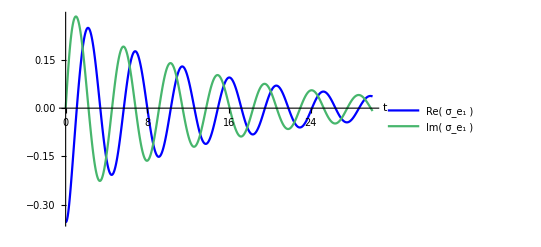

```mathematica
ListPlot[{ReσCMcoh12Data,ImσCMcoh12Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style[" Re( σ_e_1 ) ",FontFamily->"Times New Roman"],Style[" Im( σ_e_1 ) ",FontFamily->"Times New Roman"]}]
```

#### Site basis

```mathematica
σCM[n_]:=DiagonalMatrix[σCMpop[n]]+Partition[Riffle[σCMcoh[n],0,{1,Length[v]^2,Length[v]+1}],Length[v]];
```

```mathematica
σCM11Data=Table[{n dt,σCM[n][[1,1]]},{n,0,Nt+1}]
```

{{0.,0.146447},{0.05,0.146447},{0.1,0.147287},{0.15,0.148946},{0.2,0.151378},{0.25,0.154521},{0.3,0.158299},{0.35,0.162631},{0.4,0.167432},{0.45,0.17262},{0.5,0.178118},{0.55,0.183855},{0.6,0.189768},{0.65,0.1958},{0.7,0.201905},{0.75,0.208041},{0.8,0.214174},{0.85,0.220276},{0.9,0.226325},{0.95,0.232303},{1.,0.238199},{1.05,0.244002},{1.1,0.249707},{1.15,0.255311},{1.2,0.260813},{1.25,0.266215},{1.3,0.271518},{1.35,0.276726},{1.4,0.281844},{1.45,0.286875},{1.5,0.291825},{1.55,0.296699},{1.6,0.301501},{1.65,0.306237},{1.7,0.310911},{1.75,0.315528},{1.8,0.320091},{1.85,0.324603},{1.9,0.329069},{1.95,0.333492},{2.,0.337872},{2.05,0.342214},{2.1,0.346519},{2.15,0.350789},{2.2,0.355025},{2.25,0.359228},{2.3,0.363399},{2.35,0.36754},{2.4,0.37165},{2.45,0.37573},{2.5,0.379781},{2.55,0.383802},{2.6,0.387794},{2.65,0.391758},{2.7,0.395692},{2.75,0.399597},{2.8,0.403473},{2.85,0.40732},{2.9,0.411137},{2.95,0.414925},{3.,0.418683},{3.05,0.422411},{3.1,0.42611},{3.15,0.429778},{3.2,0.433416},{3.25,0.437024},{3.3,0.440601},{3.35,0.444148},{3.4,0.447664},{3.45,0.451149},{3.5,0.454604},{3.55,0.458028},{3.6,0.461422},{3.65,0.464785},{3.7,0.468117},{3.75,0.471418},{3.8,0.474689},{3.85,0.47793},{3.9,0.48114},{3.95,0.48432},{4.,0.48747},{4.05,0.49059},{4.1,0.49368},{4.15,0.49674},{4.2,0.499771},{4.25,0.502773},{4.3,0.505746},{4.35,0.508689},{4.4,0.511604},{4.45,0.51449},{4.5,0.517348},{4.55,0.520178},{4.6,0.52298},{4.65,0.525755},{4.7,0.528501},{4.75,0.531221},{4.8,0.533914},{4.85,0.53658},{4.9,0.53922},{4.95,0.541833},{5.,0.54442},{5.05,0.546982},{5.1,0.549518},{5.15,0.552028},{5.2,0.554514},{5.25,0.556975},{5.3,0.559411},{5.35,0.561823},{5.4,0.564211},{5.45,0.566575},{5.5,0.568915},{5.55,0.571232},{5.6,0.573526},{5.65,0.575797},{5.7,0.578045},{5.75,0.580271},{5.8,0.582475},{5.85,0.584656},{5.9,0.586816},{5.95,0.588954},{6.,0.591071},{6.05,0.593167},{6.1,0.595242},{6.15,0.597296},{6.2,0.59933},{6.25,0.601344},{6.3,0.603337},{6.35,0.605311},{6.4,0.607265},{6.45,0.6092},{6.5,0.611115},{6.55,0.613012},{6.6,0.61489},{6.65,0.616749},{6.7,0.61859},{6.75,0.620412},{6.8,0.622217},{6.85,0.624003},{6.9,0.625773},{6.95,0.627524},{7.,0.629258},{7.05,0.630976},{7.1,0.632676},{7.15,0.63436},{7.2,0.636027},{7.25,0.637678},{7.3,0.639312},{7.35,0.64093},{7.4,0.642533},{7.45,0.64412},{7.5,0.645691},{7.55,0.647247},{7.6,0.648788},{7.65,0.650313},{7.7,0.651824},{7.75,0.65332},{7.8,0.654802},{7.85,0.656268},{7.9,0.657721},{7.95,0.659159},{8.,0.660584},{8.05,0.661994},{8.1,0.663391},{8.15,0.664774},{8.2,0.666144},{8.25,0.6675},{8.3,0.668843},{8.35,0.670173},{8.4,0.671491},{8.45,0.672795},{8.5,0.674086},{8.55,0.675365},{8.6,0.676632},{8.65,0.677886},{8.7,0.679128},{8.75,0.680358},{8.8,0.681576},{8.85,0.682782},{8.9,0.683976},{8.95,0.685159},{9.,0.68633},{9.05,0.68749},{9.1,0.688638},{9.15,0.689775},{9.2,0.690901},{9.25,0.692016},{9.3,0.693121},{9.35,0.694214},{9.4,0.695297},{9.45,0.696369},{9.5,0.69743},{9.55,0.698481},{9.6,0.699522},{9.65,0.700553},{9.7,0.701574},{9.75,0.702584},{9.8,0.703585},{9.85,0.704575},{9.9,0.705556},{9.95,0.706528},{10.,0.70749},{10.05,0.708442},{10.1,0.709385},{10.15,0.710319},{10.2,0.711243},{10.25,0.712159},{10.3,0.713065},{10.35,0.713963},{10.4,0.714851},{10.45,0.715731},{10.5,0.716602},{10.55,0.717465},{10.6,0.718319},{10.65,0.719165},{10.7,0.720002},{10.75,0.720831},{10.8,0.721652},{10.85,0.722464},{10.9,0.723269},{10.95,0.724066},{11.,0.724855},{11.05,0.725636},{11.1,0.726409},{11.15,0.727175},{11.2,0.727933},{11.25,0.728684},{11.3,0.729427},{11.35,0.730163},{11.4,0.730892},{11.45,0.731613},{11.5,0.732328},{11.55,0.733035},{11.6,0.733736},{11.65,0.734429},{11.7,0.735116},{11.75,0.735796},{11.8,0.736469},{11.85,0.737136},{11.9,0.737796},{11.95,0.738449},{12.,0.739097},{12.05,0.739737},{12.1,0.740372},{12.15,0.741},{12.2,0.741623},{12.25,0.742239},{12.3,0.742849},{12.35,0.743453},{12.4,0.744051},{12.45,0.744643},{12.5,0.745229},{12.55,0.74581},{12.6,0.746385},{12.65,0.746955},{12.7,0.747519},{12.75,0.748077},{12.8,0.74863},{12.85,0.749177},{12.9,0.749719},{12.95,0.750256},{13.,0.750788},{13.05,0.751314},{13.1,0.751836},{13.15,0.752352},{13.2,0.752863},{13.25,0.753369},{13.3,0.75387},{13.35,0.754366},{13.4,0.754858},{13.45,0.755345},{13.5,0.755826},{13.55,0.756304},{13.6,0.756776},{13.65,0.757244},{13.7,0.757707},{13.75,0.758166},{13.8,0.75862},{13.85,0.75907},{13.9,0.759516},{13.95,0.759957},{14.,0.760393},{14.05,0.760826},{14.1,0.761254},{14.15,0.761678},{14.2,0.762098},{14.25,0.762514},{14.3,0.762926},{14.35,0.763333},{14.4,0.763737},{14.45,0.764137},{14.5,0.764532},{14.55,0.764924},{14.6,0.765312},{14.65,0.765696},{14.7,0.766077},{14.75,0.766453},{14.8,0.766826},{14.85,0.767196},{14.9,0.767561},{14.95,0.767923},{15.,0.768282},{15.05,0.768637},{15.1,0.768988},{15.15,0.769336},{15.2,0.769681},{15.25,0.770022},{15.3,0.77036},{15.35,0.770694},{15.4,0.771025},{15.45,0.771353},{15.5,0.771678},{15.55,0.772},{15.6,0.772318},{15.65,0.772633},{15.7,0.772945},{15.75,0.773254},{15.8,0.77356},{15.85,0.773863},{15.9,0.774163},{15.95,0.77446},{16.,0.774754},{16.05,0.775045},{16.1,0.775334},{16.15,0.775619},{16.2,0.775902},{16.25,0.776182},{16.3,0.776459},{16.35,0.776733},{16.4,0.777005},{16.45,0.777274},{16.5,0.77754},{16.55,0.777804},{16.6,0.778065},{16.65,0.778324},{16.7,0.77858},{16.75,0.778834},{16.8,0.779085},{16.85,0.779333},{16.9,0.77958},{16.95,0.779823},{17.,0.780065},{17.05,0.780304},{17.1,0.780541},{17.15,0.780775},{17.2,0.781007},{17.25,0.781237},{17.3,0.781464},{17.35,0.78169},{17.4,0.781913},{17.45,0.782134},{17.5,0.782353},{17.55,0.782569},{17.6,0.782784},{17.65,0.782996},{17.7,0.783207},{17.75,0.783415},{17.8,0.783621},{17.85,0.783826},{17.9,0.784028},{17.95,0.784228},{18.,0.784426},{18.05,0.784623},{18.1,0.784817},{18.15,0.78501},{18.2,0.7852},{18.25,0.785389},{18.3,0.785576},{18.35,0.785761},{18.4,0.785945},{18.45,0.786126},{18.5,0.786306},{18.55,0.786484},{18.6,0.78666},{18.65,0.786835},{18.7,0.787007},{18.75,0.787179},{18.8,0.787348},{18.85,0.787516},{18.9,0.787682},{18.95,0.787846},{19.,0.788009},{19.05,0.788171},{19.1,0.78833},{19.15,0.788488},{19.2,0.788645},{19.25,0.7888},{19.3,0.788953},{19.35,0.789105},{19.4,0.789256},{19.45,0.789405},{19.5,0.789552},{19.55,0.789698},{19.6,0.789843},{19.65,0.789986},{19.7,0.790128},{19.75,0.790269},{19.8,0.790408},{19.85,0.790545},{19.9,0.790681},{19.95,0.790816},{20.,0.79095},{20.05,0.791082},{20.1,0.791213},{20.15,0.791343},{20.2,0.791472},{20.25,0.791599},{20.3,0.791725},{20.35,0.791849},{20.4,0.791973},{20.45,0.792095},{20.5,0.792216},{20.55,0.792336},{20.6,0.792455},{20.65,0.792572},{20.7,0.792688},{20.75,0.792804},{20.8,0.792918},{20.85,0.793031},{20.9,0.793142},{20.95,0.793253},{21.,0.793363},{21.05,0.793471},{21.1,0.793579},{21.15,0.793685},{21.2,0.793791},{21.25,0.793895},{21.3,0.793998},{21.35,0.794101},{21.4,0.794202},{21.45,0.794302},{21.5,0.794402},{21.55,0.7945},{21.6,0.794598},{21.65,0.794694},{21.7,0.79479},{21.75,0.794884},{21.8,0.794978},{21.85,0.795071},{21.9,0.795162},{21.95,0.795253},{22.,0.795343},{22.05,0.795433},{22.1,0.795521},{22.15,0.795608},{22.2,0.795695},{22.25,0.795781},{22.3,0.795866},{22.35,0.79595},{22.4,0.796033},{22.45,0.796115},{22.5,0.796197},{22.55,0.796278},{22.6,0.796358},{22.65,0.796437},{22.7,0.796516},{22.75,0.796593},{22.8,0.79667},{22.85,0.796746},{22.9,0.796822},{22.95,0.796897},{23.,0.796971},{23.05,0.797044},{23.1,0.797116},{23.15,0.797188},{23.2,0.797259},{23.25,0.79733},{23.3,0.797399},{23.35,0.797468},{23.4,0.797537},{23.45,0.797605},{23.5,0.797672},{23.55,0.797738},{23.6,0.797804},{23.65,0.797869},{23.7,0.797933},{23.75,0.797997},{23.8,0.79806},{23.85,0.798123},{23.9,0.798185},{23.95,0.798246},{24.,0.798307},{24.05,0.798367},{24.1,0.798426},{24.15,0.798485},{24.2,0.798544},{24.25,0.798601},{24.3,0.798659},{24.35,0.798715},{24.4,0.798771},{24.45,0.798827},{24.5,0.798882},{24.55,0.798936},{24.6,0.79899},{24.65,0.799044},{24.7,0.799097},{24.75,0.799149},{24.8,0.799201},{24.85,0.799252},{24.9,0.799303},{24.95,0.799353},{25.,0.799403},{25.05,0.799452},{25.1,0.799501},{25.15,0.799549},{25.2,0.799597},{25.25,0.799645},{25.3,0.799692},{25.35,0.799738},{25.4,0.799784},{25.45,0.79983},{25.5,0.799875},{25.55,0.79992},{25.6,0.799964},{25.65,0.800008},{25.7,0.800051},{25.75,0.800094},{25.8,0.800136},{25.85,0.800179},{25.9,0.80022},{25.95,0.800262},{26.,0.800302},{26.05,0.800343},{26.1,0.800383},{26.15,0.800423},{26.2,0.800462},{26.25,0.800501},{26.3,0.80054},{26.35,0.800578},{26.4,0.800616},{26.45,0.800653},{26.5,0.80069},{26.55,0.800727},{26.6,0.800763},{26.65,0.800799},{26.7,0.800835},{26.75,0.80087},{26.8,0.800905},{26.85,0.80094},{26.9,0.800974},{26.95,0.801008},{27.,0.801041},{27.05,0.801075},{27.1,0.801108},{27.15,0.80114},{27.2,0.801172},{27.25,0.801204},{27.3,0.801236},{27.35,0.801267},{27.4,0.801299},{27.45,0.801329},{27.5,0.80136},{27.55,0.80139},{27.6,0.80142},{27.65,0.801449},{27.7,0.801479},{27.75,0.801508},{27.8,0.801536},{27.85,0.801565},{27.9,0.801593},{27.95,0.801621},{28.,0.801648},{28.05,0.801676},{28.1,0.801703},{28.15,0.801729},{28.2,0.801756},{28.25,0.801782},{28.3,0.801808},{28.35,0.801834},{28.4,0.801859},{28.45,0.801885},{28.5,0.80191},{28.55,0.801934},{28.6,0.801959},{28.65,0.801983},{28.7,0.802007},{28.75,0.802031},{28.8,0.802055},{28.85,0.802078},{28.9,0.802101},{28.95,0.802124},{29.,0.802146},{29.05,0.802169},{29.1,0.802191},{29.15,0.802213},{29.2,0.802235},{29.25,0.802256},{29.3,0.802278},{29.35,0.802299},{29.4,0.80232},{29.45,0.80234},{29.5,0.802361},{29.55,0.802381},{29.6,0.802401},{29.65,0.802421},{29.7,0.802441},{29.75,0.80246},{29.8,0.80248},{29.85,0.802499},{29.9,0.802518},{29.95,0.802536},{30.,0.802555},{30.05,0.802573}}

```mathematica
σCM22Data=Table[{n dt,σCM[n][[2,2]]},{n,0,Nt+1}]
```

{{0.,0.853553},{0.05,0.853553},{0.1,0.852713},{0.15,0.851054},{0.2,0.848622},{0.25,0.845479},{0.3,0.841701},{0.35,0.837369},{0.4,0.832568},{0.45,0.82738},{0.5,0.821882},{0.55,0.816145},{0.6,0.810232},{0.65,0.8042},{0.7,0.798095},{0.75,0.791959},{0.8,0.785826},{0.85,0.779724},{0.9,0.773675},{0.95,0.767697},{1.,0.761801},{1.05,0.755998},{1.1,0.750293},{1.15,0.744689},{1.2,0.739187},{1.25,0.733785},{1.3,0.728482},{1.35,0.723274},{1.4,0.718156},{1.45,0.713125},{1.5,0.708175},{1.55,0.703301},{1.6,0.698499},{1.65,0.693763},{1.7,0.689089},{1.75,0.684472},{1.8,0.679909},{1.85,0.675397},{1.9,0.670931},{1.95,0.666508},{2.,0.662128},{2.05,0.657786},{2.1,0.653481},{2.15,0.649211},{2.2,0.644975},{2.25,0.640772},{2.3,0.636601},{2.35,0.63246},{2.4,0.62835},{2.45,0.62427},{2.5,0.620219},{2.55,0.616198},{2.6,0.612206},{2.65,0.608242},{2.7,0.604308},{2.75,0.600403},{2.8,0.596527},{2.85,0.59268},{2.9,0.588863},{2.95,0.585075},{3.,0.581317},{3.05,0.577589},{3.1,0.57389},{3.15,0.570222},{3.2,0.566584},{3.25,0.562976},{3.3,0.559399},{3.35,0.555852},{3.4,0.552336},{3.45,0.548851},{3.5,0.545396},{3.55,0.541972},{3.6,0.538578},{3.65,0.535215},{3.7,0.531883},{3.75,0.528582},{3.8,0.525311},{3.85,0.52207},{3.9,0.51886},{3.95,0.51568},{4.,0.51253},{4.05,0.50941},{4.1,0.50632},{4.15,0.50326},{4.2,0.500229},{4.25,0.497227},{4.3,0.494254},{4.35,0.491311},{4.4,0.488396},{4.45,0.48551},{4.5,0.482652},{4.55,0.479822},{4.6,0.47702},{4.65,0.474245},{4.7,0.471499},{4.75,0.468779},{4.8,0.466086},{4.85,0.46342},{4.9,0.46078},{4.95,0.458167},{5.,0.45558},{5.05,0.453018},{5.1,0.450482},{5.15,0.447972},{5.2,0.445486},{5.25,0.443025},{5.3,0.440589},{5.35,0.438177},{5.4,0.435789},{5.45,0.433425},{5.5,0.431085},{5.55,0.428768},{5.6,0.426474},{5.65,0.424203},{5.7,0.421955},{5.75,0.419729},{5.8,0.417525},{5.85,0.415344},{5.9,0.413184},{5.95,0.411046},{6.,0.408929},{6.05,0.406833},{6.1,0.404758},{6.15,0.402704},{6.2,0.40067},{6.25,0.398656},{6.3,0.396663},{6.35,0.394689},{6.4,0.392735},{6.45,0.3908},{6.5,0.388885},{6.55,0.386988},{6.6,0.38511},{6.65,0.383251},{6.7,0.38141},{6.75,0.379588},{6.8,0.377783},{6.85,0.375997},{6.9,0.374227},{6.95,0.372476},{7.,0.370742},{7.05,0.369024},{7.1,0.367324},{7.15,0.36564},{7.2,0.363973},{7.25,0.362322},{7.3,0.360688},{7.35,0.35907},{7.4,0.357467},{7.45,0.35588},{7.5,0.354309},{7.55,0.352753},{7.6,0.351212},{7.65,0.349687},{7.7,0.348176},{7.75,0.34668},{7.8,0.345198},{7.85,0.343732},{7.9,0.342279},{7.95,0.340841},{8.,0.339416},{8.05,0.338006},{8.1,0.336609},{8.15,0.335226},{8.2,0.333856},{8.25,0.3325},{8.3,0.331157},{8.35,0.329827},{8.4,0.328509},{8.45,0.327205},{8.5,0.325914},{8.55,0.324635},{8.6,0.323368},{8.65,0.322114},{8.7,0.320872},{8.75,0.319642},{8.8,0.318424},{8.85,0.317218},{8.9,0.316024},{8.95,0.314841},{9.,0.31367},{9.05,0.31251},{9.1,0.311362},{9.15,0.310225},{9.2,0.309099},{9.25,0.307984},{9.3,0.306879},{9.35,0.305786},{9.4,0.304703},{9.45,0.303631},{9.5,0.30257},{9.55,0.301519},{9.6,0.300478},{9.65,0.299447},{9.7,0.298426},{9.75,0.297416},{9.8,0.296415},{9.85,0.295425},{9.9,0.294444},{9.95,0.293472},{10.,0.29251},{10.05,0.291558},{10.1,0.290615},{10.15,0.289681},{10.2,0.288757},{10.25,0.287841},{10.3,0.286935},{10.35,0.286037},{10.4,0.285149},{10.45,0.284269},{10.5,0.283398},{10.55,0.282535},{10.6,0.281681},{10.65,0.280835},{10.7,0.279998},{10.75,0.279169},{10.8,0.278348},{10.85,0.277536},{10.9,0.276731},{10.95,0.275934},{11.,0.275145},{11.05,0.274364},{11.1,0.273591},{11.15,0.272825},{11.2,0.272067},{11.25,0.271316},{11.3,0.270573},{11.35,0.269837},{11.4,0.269108},{11.45,0.268387},{11.5,0.267672},{11.55,0.266965},{11.6,0.266264},{11.65,0.265571},{11.7,0.264884},{11.75,0.264204},{11.8,0.263531},{11.85,0.262864},{11.9,0.262204},{11.95,0.261551},{12.,0.260903},{12.05,0.260263},{12.1,0.259628},{12.15,0.259},{12.2,0.258377},{12.25,0.257761},{12.3,0.257151},{12.35,0.256547},{12.4,0.255949},{12.45,0.255357},{12.5,0.254771},{12.55,0.25419},{12.6,0.253615},{12.65,0.253045},{12.7,0.252481},{12.75,0.251923},{12.8,0.25137},{12.85,0.250823},{12.9,0.250281},{12.95,0.249744},{13.,0.249212},{13.05,0.248686},{13.1,0.248164},{13.15,0.247648},{13.2,0.247137},{13.25,0.246631},{13.3,0.24613},{13.35,0.245634},{13.4,0.245142},{13.45,0.244655},{13.5,0.244174},{13.55,0.243696},{13.6,0.243224},{13.65,0.242756},{13.7,0.242293},{13.75,0.241834},{13.8,0.24138},{13.85,0.24093},{13.9,0.240484},{13.95,0.240043},{14.,0.239607},{14.05,0.239174},{14.1,0.238746},{14.15,0.238322},{14.2,0.237902},{14.25,0.237486},{14.3,0.237074},{14.35,0.236667},{14.4,0.236263},{14.45,0.235863},{14.5,0.235468},{14.55,0.235076},{14.6,0.234688},{14.65,0.234304},{14.7,0.233923},{14.75,0.233547},{14.8,0.233174},{14.85,0.232804},{14.9,0.232439},{14.95,0.232077},{15.,0.231718},{15.05,0.231363},{15.1,0.231012},{15.15,0.230664},{15.2,0.230319},{15.25,0.229978},{15.3,0.22964},{15.35,0.229306},{15.4,0.228975},{15.45,0.228647},{15.5,0.228322},{15.55,0.228},{15.6,0.227682},{15.65,0.227367},{15.7,0.227055},{15.75,0.226746},{15.8,0.22644},{15.85,0.226137},{15.9,0.225837},{15.95,0.22554},{16.,0.225246},{16.05,0.224955},{16.1,0.224666},{16.15,0.224381},{16.2,0.224098},{16.25,0.223818},{16.3,0.223541},{16.35,0.223267},{16.4,0.222995},{16.45,0.222726},{16.5,0.22246},{16.55,0.222196},{16.6,0.221935},{16.65,0.221676},{16.7,0.22142},{16.75,0.221166},{16.8,0.220915},{16.85,0.220667},{16.9,0.22042},{16.95,0.220177},{17.,0.219935},{17.05,0.219696},{17.1,0.219459},{17.15,0.219225},{17.2,0.218993},{17.25,0.218763},{17.3,0.218536},{17.35,0.21831},{17.4,0.218087},{17.45,0.217866},{17.5,0.217647},{17.55,0.217431},{17.6,0.217216},{17.65,0.217004},{17.7,0.216793},{17.75,0.216585},{17.8,0.216379},{17.85,0.216174},{17.9,0.215972},{17.95,0.215772},{18.,0.215574},{18.05,0.215377},{18.1,0.215183},{18.15,0.21499},{18.2,0.2148},{18.25,0.214611},{18.3,0.214424},{18.35,0.214239},{18.4,0.214055},{18.45,0.213874},{18.5,0.213694},{18.55,0.213516},{18.6,0.21334},{18.65,0.213165},{18.7,0.212993},{18.75,0.212821},{18.8,0.212652},{18.85,0.212484},{18.9,0.212318},{18.95,0.212154},{19.,0.211991},{19.05,0.211829},{19.1,0.21167},{19.15,0.211512},{19.2,0.211355},{19.25,0.2112},{19.3,0.211047},{19.35,0.210895},{19.4,0.210744},{19.45,0.210595},{19.5,0.210448},{19.55,0.210302},{19.6,0.210157},{19.65,0.210014},{19.7,0.209872},{19.75,0.209731},{19.8,0.209592},{19.85,0.209455},{19.9,0.209319},{19.95,0.209184},{20.,0.20905},{20.05,0.208918},{20.1,0.208787},{20.15,0.208657},{20.2,0.208528},{20.25,0.208401},{20.3,0.208275},{20.35,0.208151},{20.4,0.208027},{20.45,0.207905},{20.5,0.207784},{20.55,0.207664},{20.6,0.207545},{20.65,0.207428},{20.7,0.207312},{20.75,0.207196},{20.8,0.207082},{20.85,0.206969},{20.9,0.206858},{20.95,0.206747},{21.,0.206637},{21.05,0.206529},{21.1,0.206421},{21.15,0.206315},{21.2,0.206209},{21.25,0.206105},{21.3,0.206002},{21.35,0.205899},{21.4,0.205798},{21.45,0.205698},{21.5,0.205598},{21.55,0.2055},{21.6,0.205402},{21.65,0.205306},{21.7,0.20521},{21.75,0.205116},{21.8,0.205022},{21.85,0.204929},{21.9,0.204838},{21.95,0.204747},{22.,0.204657},{22.05,0.204567},{22.1,0.204479},{22.15,0.204392},{22.2,0.204305},{22.25,0.204219},{22.3,0.204134},{22.35,0.20405},{22.4,0.203967},{22.45,0.203885},{22.5,0.203803},{22.55,0.203722},{22.6,0.203642},{22.65,0.203563},{22.7,0.203484},{22.75,0.203407},{22.8,0.20333},{22.85,0.203254},{22.9,0.203178},{22.95,0.203103},{23.,0.203029},{23.05,0.202956},{23.1,0.202884},{23.15,0.202812},{23.2,0.202741},{23.25,0.20267},{23.3,0.202601},{23.35,0.202532},{23.4,0.202463},{23.45,0.202395},{23.5,0.202328},{23.55,0.202262},{23.6,0.202196},{23.65,0.202131},{23.7,0.202067},{23.75,0.202003},{23.8,0.20194},{23.85,0.201877},{23.9,0.201815},{23.95,0.201754},{24.,0.201693},{24.05,0.201633},{24.1,0.201574},{24.15,0.201515},{24.2,0.201456},{24.25,0.201399},{24.3,0.201341},{24.35,0.201285},{24.4,0.201229},{24.45,0.201173},{24.5,0.201118},{24.55,0.201064},{24.6,0.20101},{24.65,0.200956},{24.7,0.200903},{24.75,0.200851},{24.8,0.200799},{24.85,0.200748},{24.9,0.200697},{24.95,0.200647},{25.,0.200597},{25.05,0.200548},{25.1,0.200499},{25.15,0.200451},{25.2,0.200403},{25.25,0.200355},{25.3,0.200308},{25.35,0.200262},{25.4,0.200216},{25.45,0.20017},{25.5,0.200125},{25.55,0.20008},{25.6,0.200036},{25.65,0.199992},{25.7,0.199949},{25.75,0.199906},{25.8,0.199864},{25.85,0.199821},{25.9,0.19978},{25.95,0.199738},{26.,0.199698},{26.05,0.199657},{26.1,0.199617},{26.15,0.199577},{26.2,0.199538},{26.25,0.199499},{26.3,0.19946},{26.35,0.199422},{26.4,0.199384},{26.45,0.199347},{26.5,0.19931},{26.55,0.199273},{26.6,0.199237},{26.65,0.199201},{26.7,0.199165},{26.75,0.19913},{26.8,0.199095},{26.85,0.19906},{26.9,0.199026},{26.95,0.198992},{27.,0.198959},{27.05,0.198925},{27.1,0.198892},{27.15,0.19886},{27.2,0.198828},{27.25,0.198796},{27.3,0.198764},{27.35,0.198733},{27.4,0.198701},{27.45,0.198671},{27.5,0.19864},{27.55,0.19861},{27.6,0.19858},{27.65,0.198551},{27.7,0.198521},{27.75,0.198492},{27.8,0.198464},{27.85,0.198435},{27.9,0.198407},{27.95,0.198379},{28.,0.198352},{28.05,0.198324},{28.1,0.198297},{28.15,0.198271},{28.2,0.198244},{28.25,0.198218},{28.3,0.198192},{28.35,0.198166},{28.4,0.198141},{28.45,0.198115},{28.5,0.19809},{28.55,0.198066},{28.6,0.198041},{28.65,0.198017},{28.7,0.197993},{28.75,0.197969},{28.8,0.197945},{28.85,0.197922},{28.9,0.197899},{28.95,0.197876},{29.,0.197854},{29.05,0.197831},{29.1,0.197809},{29.15,0.197787},{29.2,0.197765},{29.25,0.197744},{29.3,0.197722},{29.35,0.197701},{29.4,0.19768},{29.45,0.19766},{29.5,0.197639},{29.55,0.197619},{29.6,0.197599},{29.65,0.197579},{29.7,0.197559},{29.75,0.19754},{29.8,0.19752},{29.85,0.197501},{29.9,0.197482},{29.95,0.197464},{30.,0.197445},{30.05,0.197427}}

```mathematica
σCM12Data=Table[{n dt,σCM[n][[1,2]]},{n,0,Nt+1}]
```

{{0.,-0.353553},{0.05,-0.353553-0.025 ⅈ},{0.1,-0.350614-0.049931 ⅈ},{0.15,-0.344807-0.0744526 ⅈ},{0.2,-0.336294-0.098248 ⅈ},{0.25,-0.325315-0.121041 ⅈ},{0.3,-0.312155-0.142605 ⅈ},{0.35,-0.297126-0.162772 ⅈ},{0.4,-0.280542-0.181427 ⅈ},{0.45,-0.262699-0.198502 ⅈ},{0.5,-0.243864-0.213968 ⅈ},{0.55,-0.224268-0.227826 ⅈ},{0.6,-0.204108-0.240092 ⅈ},{0.65,-0.183547-0.250799 ⅈ},{0.7,-0.162719-0.259981 ⅈ},{0.75,-0.141734-0.267676 ⅈ},{0.8,-0.120686-0.273919 ⅈ},{0.85,-0.099655-0.278745 ⅈ},{0.9,-0.078713-0.282184 ⅈ},{0.95,-0.0579256-0.284268 ⅈ},{1.,-0.0373552-0.285024 ⅈ},{1.05,-0.0170626-0.284482 ⅈ},{1.1,0.00289242-0.282669 ⅈ},{1.15,0.0224503-0.279616 ⅈ},{1.2,0.0415516-0.275355 ⅈ},{1.25,0.0601373-0.269922 ⅈ},{1.3,0.0781484-0.263353 ⅈ},{1.35,0.0955272-0.25569 ⅈ},{1.4,0.112217-0.246978 ⅈ},{1.45,0.128162-0.237263 ⅈ},{1.5,0.14331-0.226598 ⅈ},{1.55,0.15761-0.215038 ⅈ},{1.6,0.171013-0.202639 ⅈ},{1.65,0.183476-0.189463 ⅈ},{1.7,0.194957-0.175575 ⅈ},{1.75,0.205417-0.16104 ⅈ},{1.8,0.214825-0.145927 ⅈ},{1.85,0.22315-0.130308 ⅈ},{1.9,0.230368-0.114256 ⅈ},{1.95,0.236459-0.0978435 ⅈ},{2.,0.241406-0.0811469 ⅈ},{2.05,0.2452-0.0642421 ⅈ},{2.1,0.247834-0.0472058 ⅈ},{2.15,0.249308-0.0301144 ⅈ},{2.2,0.249625-0.0130445 ⅈ},{2.25,0.248796+0.00392799 ⅈ},{2.3,0.246833+0.0207282 ⅈ},{2.35,0.243755+0.0372823 ⅈ},{2.4,0.239586+0.0535182 ⅈ},{2.45,0.234354+0.0693655 ⅈ},{2.5,0.228091+0.0847561 ⅈ},{2.55,0.220835+0.0996243 ⅈ},{2.6,0.212626+0.113907 ⅈ},{2.65,0.203509+0.127545 ⅈ},{2.7,0.193533+0.140481 ⅈ},{2.75,0.18275+0.152663 ⅈ},{2.8,0.171215+0.16404 ⅈ},{2.85,0.158988+0.174568 ⅈ},{2.9,0.146128+0.184205 ⅈ},{2.95,0.1327+0.192914 ⅈ},{3.,0.118769+0.200664 ⅈ},{3.05,0.104403+0.207425 ⅈ},{3.1,0.0896711+0.213175 ⅈ},{3.15,0.0746426+0.217895 ⅈ},{3.2,0.0593889+0.221571 ⅈ},{3.25,0.0439817+0.224195 ⅈ},{3.3,0.0284924+0.225763 ⅈ},{3.35,0.0129929+0.226274 ⅈ},{3.4,-0.00244581+0.225736 ⅈ},{3.45,-0.0177533+0.224157 ⅈ},{3.5,-0.0328604+0.221554 ⅈ},{3.55,-0.047699+0.217945 ⅈ},{3.6,-0.0622032+0.213355 ⅈ},{3.65,-0.0763085+0.207813 ⅈ},{3.7,-0.0899533+0.20135 ⅈ},{3.75,-0.103078+0.194003 ⅈ},{3.8,-0.115626+0.185812 ⅈ},{3.85,-0.127544+0.176822 ⅈ},{3.9,-0.138781+0.16708 ⅈ},{3.95,-0.149291+0.156635 ⅈ},{4.,-0.159031+0.145542 ⅈ},{4.05,-0.167961+0.133856 ⅈ},{4.1,-0.176045+0.121635 ⅈ},{4.15,-0.183254+0.10894 ⅈ},{4.2,-0.189559+0.095832 ⅈ},{4.25,-0.194939+0.0823753 ⅈ},{4.3,-0.199374+0.0686344 ⅈ},{4.35,-0.202852+0.0546747 ⅈ},{4.4,-0.205363+0.0405623 ⅈ},{4.45,-0.206902+0.0263635 ⅈ},{4.5,-0.20747+0.0121446 ⅈ},{4.55,-0.20707-0.00202859 ⅈ},{4.6,-0.205711-0.0160908 ⅈ},{4.65,-0.203407-0.0299778 ⅈ},{4.7,-0.200174-0.0436266 ⅈ},{4.75,-0.196035-0.0569757 ⅈ},{4.8,-0.191014-0.0699654 ⅈ},{4.85,-0.185142-0.0825382 ⅈ},{4.9,-0.178451-0.0946387 ⅈ},{4.95,-0.170979-0.106214 ⅈ},{5.,-0.162765-0.117215 ⅈ},{5.05,-0.153852-0.127594 ⅈ},{5.1,-0.144287-0.137308 ⅈ},{5.15,-0.134119-0.146315 ⅈ},{5.2,-0.123399-0.15458 ⅈ},{5.25,-0.112181-0.16207 ⅈ},{5.3,-0.100519-0.168754 ⅈ},{5.35,-0.0884718-0.174608 ⅈ},{5.4,-0.076097-0.17961 ⅈ},{5.45,-0.0634546-0.183743 ⅈ},{5.5,-0.050605-0.186994 ⅈ},{5.55,-0.0376092-0.189354 ⅈ},{5.6,-0.0245284-0.190818 ⅈ},{5.65,-0.0114241-0.191385 ⅈ},{5.7,0.00164305-0.191059 ⅈ},{5.75,0.0146125-0.189848 ⅈ},{5.8,0.0274249-0.187764 ⅈ},{5.85,0.0400218-0.184822 ⅈ},{5.9,0.0523463-0.181041 ⅈ},{5.95,0.064343-0.176446 ⅈ},{6.,0.0759586-0.171062 ⅈ},{6.05,0.0871418-0.164921 ⅈ},{6.1,0.0978436-0.158056 ⅈ},{6.15,0.108018-0.150503 ⅈ},{6.2,0.117621-0.142303 ⅈ},{6.25,0.126612-0.133499 ⅈ},{6.3,0.134953-0.124134 ⅈ},{6.35,0.142611-0.114257 ⅈ},{6.4,0.149554-0.103916 ⅈ},{6.45,0.155755-0.0931636 ⅈ},{6.5,0.16119-0.0820515 ⅈ},{6.55,0.16584-0.070634 ⅈ},{6.6,0.169688-0.0589661 ⅈ},{6.65,0.172721-0.0471039 ⅈ},{6.7,0.174931-0.0351035 ⅈ},{6.75,0.176314-0.0230218 ⅈ},{6.8,0.176869-0.0109153 ⅈ},{6.85,0.176599+0.00115968 ⅈ},{6.9,0.17551+0.0131472 ⅈ},{6.95,0.173613+0.0249922 ⅈ},{7.,0.170923+0.0366407 ⅈ},{7.05,0.167457+0.04804 ⅈ},{7.1,0.163236+0.0591388 ⅈ},{7.15,0.158287+0.0698876 ⅈ},{7.2,0.152635+0.0802389 ⅈ},{7.25,0.146313+0.0901473 ⅈ},{7.3,0.139354+0.0995699 ⅈ},{7.35,0.131795+0.108466 ⅈ},{7.4,0.123675+0.116798 ⅈ},{7.45,0.115036+0.124531 ⅈ},{7.5,0.10592+0.131634 ⅈ},{7.55,0.0963746+0.138077 ⅈ},{7.6,0.0864458+0.143834 ⅈ},{7.65,0.0761826+0.148885 ⅈ},{7.7,0.0656349+0.15321 ⅈ},{7.75,0.0548536+0.156794 ⅈ},{7.8,0.0438903+0.159626 ⅈ},{7.85,0.0327973+0.161696 ⅈ},{7.9,0.0216268+0.163002 ⅈ},{7.95,0.0104313+0.163542 ⅈ},{8.,-0.000737145+0.163318 ⅈ},{8.05,-0.0118267+0.162337 ⅈ},{8.1,-0.0227866+0.160608 ⅈ},{8.15,-0.0335666+0.158145 ⅈ},{8.2,-0.044118+0.154964 ⅈ},{8.25,-0.0543932+0.151085 ⅈ},{8.3,-0.0643466+0.146529 ⅈ},{8.35,-0.0739338+0.141324 ⅈ},{8.4,-0.0831131+0.135497 ⅈ},{8.45,-0.0918443+0.12908 ⅈ},{8.5,-0.10009+0.122106 ⅈ},{8.55,-0.107815+0.114612 ⅈ},{8.6,-0.114988+0.106636 ⅈ},{8.65,-0.121577+0.0982183 ⅈ},{8.7,-0.127558+0.0894008 ⅈ},{8.75,-0.132906+0.0802273 ⅈ},{8.8,-0.1376+0.0707427 ⅈ},{8.85,-0.141624+0.0609932 ⅈ},{8.9,-0.144962+0.0510259 ⅈ},{8.95,-0.147604+0.0408885 ⅈ},{9.,-0.149543+0.0306292 ⅈ},{9.05,-0.150775+0.0202965 ⅈ},{9.1,-0.151297+0.00993894 ⅈ},{9.15,-0.151113-0.000395276 ⅈ},{9.2,-0.150228-0.0106583 ⅈ},{9.25,-0.148651-0.0208029 ⅈ},{9.3,-0.146394-0.0307827 ⅈ},{9.35,-0.143472-0.0405526 ⅈ},{9.4,-0.139902-0.0500686 ⅈ},{9.45,-0.135707-0.059288 ⅈ},{9.5,-0.13091-0.0681702 ⅈ},{9.55,-0.125536-0.0766761 ⅈ},{9.6,-0.119615-0.0847688 ⅈ},{9.65,-0.113178-0.0924134 ⅈ},{9.7,-0.106259-0.0995773 ⅈ},{9.75,-0.098892-0.106231 ⅈ},{9.8,-0.091115-0.112346 ⅈ},{9.85,-0.0829667-0.117898 ⅈ},{9.9,-0.0744876-0.122865 ⅈ},{9.95,-0.0657192-0.127229 ⅈ},{10.,-0.0567041-0.130971 ⅈ},{10.05,-0.047486-0.134081 ⅈ},{10.1,-0.038109-0.136546 ⅈ},{10.15,-0.0286177-0.138361 ⅈ},{10.2,-0.0190569-0.139521 ⅈ},{10.25,-0.0094716-0.140024 ⅈ},{10.3,0.000093564-0.139874 ⅈ},{10.35,0.00959429-0.139075 ⅈ},{10.4,0.0189869-0.137635 ⅈ},{10.45,0.0282284-0.135565 ⅈ},{10.5,0.037277-0.13288 ⅈ},{10.55,0.0460918-0.129595 ⅈ},{10.6,0.0546336-0.125729 ⅈ},{10.65,0.0628644-0.121306 ⅈ},{10.7,0.070748-0.116348 ⅈ},{10.75,0.0782503-0.110884 ⅈ},{10.8,0.0853389-0.10494 ⅈ},{10.85,0.0919836-0.0985488 ⅈ},{10.9,0.0981565-0.0917424 ⅈ},{10.95,0.103832-0.0845553 ⅈ},{11.,0.108987-0.0770234 ⅈ},{11.05,0.113602-0.0691839 ⅈ},{11.1,0.117658-0.0610755 ⅈ},{11.15,0.12114-0.0527375 ⅈ},{11.2,0.124036-0.0442102 ⅈ},{11.25,0.126336-0.0355345 ⅈ},{11.3,0.128034-0.0267517 ⅈ},{11.35,0.129126-0.0179033 ⅈ},{11.4,0.129611-0.00903082 ⅈ},{11.45,0.12949-0.000175686 ⅈ},{11.5,0.128769+0.0086211 ⅈ},{11.55,0.127454+0.0173191 ⅈ},{11.6,0.125556+0.0258785 ⅈ},{11.65,0.123087+0.0342604 ⅈ},{11.7,0.120063+0.0424273 ⅈ},{11.75,0.116501+0.0503424 ⅈ},{11.8,0.112421+0.0579708 ⅈ},{11.85,0.107847+0.0652789 ⅈ},{11.9,0.102802+0.072235 ⅈ},{11.95,0.0973132+0.0788089 ⅈ},{12.,0.0914089+0.0849729 ⅈ},{12.05,0.0851193+0.0907008 ⅈ},{12.1,0.0784763+0.0959692 ⅈ},{12.15,0.0715131+0.100756 ⅈ},{12.2,0.064264+0.105044 ⅈ},{12.25,0.0567648+0.108814 ⅈ},{12.3,0.049052+0.112054 ⅈ},{12.35,0.0411627+0.114752 ⅈ},{12.4,0.0331349+0.116898 ⅈ},{12.45,0.0250067+0.118487 ⅈ},{12.5,0.0168166+0.119515 ⅈ},{12.55,0.008603+0.119981 ⅈ},{12.6,0.000404258+0.119886 ⅈ},{12.65,-0.00774164+0.119235 ⅈ},{12.7,-0.0157972+0.118034 ⅈ},{12.75,-0.0237256+0.116293 ⅈ},{12.8,-0.0314909+0.114023 ⅈ},{12.85,-0.0390581+0.111239 ⅈ},{12.9,-0.0463933+0.107956 ⅈ},{12.95,-0.053464+0.104194 ⅈ},{13.,-0.0602391+0.0999722 ⅈ},{13.05,-0.0666892+0.0953146 ⅈ},{13.1,-0.0727863+0.0902451 ⅈ},{13.15,-0.0785047+0.0847902 ⅈ},{13.2,-0.0838201+0.0789778 ⅈ},{13.25,-0.0887107+0.0728371 ⅈ},{13.3,-0.0931565+0.066399 ⅈ},{13.35,-0.0971398+0.0596954 ⅈ},{13.4,-0.100645+0.0527591 ⅈ},{13.45,-0.10366+0.0456239 ⅈ},{13.5,-0.106172+0.0383244 ⅈ},{13.55,-0.108175+0.0308955 ⅈ},{13.6,-0.109662+0.0233725 ⅈ},{13.65,-0.110629+0.0157912 ⅈ},{13.7,-0.111076+0.00818699 ⅈ},{13.75,-0.111004+0.000595469 ⅈ},{13.8,-0.110416-0.0069482 ⅈ},{13.85,-0.10932-0.0144093 ⅈ},{13.9,-0.107723-0.0217537 ⅈ},{13.95,-0.105636-0.0289481 ⅈ},{14.,-0.103072-0.03596 ⅈ},{14.05,-0.100046-0.0427581 ⅈ},{14.1,-0.0965761-0.0493123 ⅈ},{14.15,-0.0926803-0.0555936 ⅈ},{14.2,-0.0883798-0.0615748 ⅈ},{14.25,-0.0836973-0.0672301 ⅈ},{14.3,-0.0786572-0.0725353 ⅈ},{14.35,-0.0732853-0.0774681 ⅈ},{14.4,-0.0676086-0.0820081 ⅈ},{14.45,-0.0616557-0.0861369 ⅈ},{14.5,-0.0554559-0.0898379 ⅈ},{14.55,-0.0490399-0.0930969 ⅈ},{14.6,-0.0424387-0.0959017 ⅈ},{14.65,-0.0356844-0.0982422 ⅈ},{14.7,-0.0288093-0.100111 ⅈ},{14.75,-0.0218461-0.101502 ⅈ},{14.8,-0.0148278-0.102412 ⅈ},{14.85,-0.00778743-0.10284 ⅈ},{14.9,-0.000757759-0.102787 ⅈ},{14.95,0.00622859-0.102258 ⅈ},{15.,0.0131395-0.101256 ⅈ},{15.05,0.0199432-0.0997913 ⅈ},{15.1,0.026609-0.0978724 ⅈ},{15.15,0.0331068-0.0955115 ⅈ},{15.2,0.0394075-0.0927227 ⅈ},{15.25,0.045483-0.0895216 ⅈ},{15.3,0.0513068-0.0859259 ⅈ},{15.35,0.0568535-0.081955 ⅈ},{15.4,0.062099-0.0776297 ⅈ},{15.45,0.0670211-0.0729726 ⅈ},{15.5,0.071599-0.0680075 ⅈ},{15.55,0.0758138-0.0627595 ⅈ},{15.6,0.0796483-0.0572549 ⅈ},{15.65,0.0830871-0.0515209 ⅈ},{15.7,0.0861171-0.0455858 ⅈ},{15.75,0.0887267-0.0394783 ⅈ},{15.8,0.0909068-0.0332282 ⅈ},{15.85,0.0926499-0.0268653 ⅈ},{15.9,0.093951-0.02042 ⅈ},{15.95,0.094807-0.0139227 ⅈ},{16.,0.0952167-0.00740401 ⅈ},{16.05,0.0951814-0.00089434 ⅈ},{16.1,0.094704+0.00557613 ⅈ},{16.15,0.0937899+0.0119776 ⅈ},{16.2,0.0924461+0.0182808 ⅈ},{16.25,0.0906817+0.0244571 ⅈ},{16.3,0.0885078+0.0304786 ⅈ},{16.35,0.0859371+0.0363184 ⅈ},{16.4,0.0829843+0.0419506 ⅈ},{16.45,0.0796656+0.0473503 ⅈ},{16.5,0.0759989+0.0524941 ⅈ},{16.55,0.0720034+0.0573598 ⅈ},{16.6,0.0677001+0.0619266 ⅈ},{16.65,0.0631109+0.0661752 ⅈ},{16.7,0.058259+0.0700881 ⅈ},{16.75,0.0531688+0.0736493 ⅈ},{16.8,0.0478654+0.0768446 ⅈ},{16.85,0.042375+0.0796617 ⅈ},{16.9,0.0367242+0.0820898 ⅈ},{16.95,0.0309405+0.0841204 ⅈ},{17.,0.0250515+0.0857466 ⅈ},{17.05,0.0190853+0.0869636 ⅈ},{17.1,0.0130702+0.0877685 ⅈ},{17.15,0.0070344+0.0881603 ⅈ},{17.2,0.00100611+0.0881398 ⅈ},{17.25,-0.00498672+0.08771 ⅈ},{17.3,-0.0109165+0.0868755 ⅈ},{17.35,-0.016756+0.0856429 ⅈ},{17.4,-0.0224789+0.0840207 ⅈ},{17.45,-0.0280592+0.0820188 ⅈ},{17.5,-0.0334719+0.0796493 ⅈ},{17.55,-0.0386932+0.0769255 ⅈ},{17.6,-0.0436999+0.0738623 ⅈ},{17.65,-0.0484702+0.0704765 ⅈ},{17.7,-0.0529836+0.0667857 ⅈ},{17.75,-0.0572208+0.0628092 ⅈ},{17.8,-0.0611639+0.0585673 ⅈ},{17.85,-0.0647966+0.0540816 ⅈ},{17.9,-0.068104+0.0493745 ⅈ},{17.95,-0.0710731+0.0444693 ⅈ},{18.,-0.0736921+0.0393901 ⅈ},{18.05,-0.0759513+0.0341618 ⅈ},{18.1,-0.0778427+0.0288095 ⅈ},{18.15,-0.0793597+0.023359 ⅈ},{18.2,-0.080498+0.0178363 ⅈ},{18.25,-0.0812547+0.0122674 ⅈ},{18.3,-0.0816288+0.00667865 ⅈ},{18.35,-0.0816212+0.00109605 ⅈ},{18.4,-0.0812344-0.0044545 ⅈ},{18.45,-0.0804728-0.0099474 ⅈ},{18.5,-0.0793424-0.0153575 ⅈ},{18.55,-0.0778508-0.0206603 ⅈ},{18.6,-0.0760075-0.0258318 ⅈ},{18.65,-0.0738233-0.0308488 ⅈ},{18.7,-0.0713107-0.0356892 ⅈ},{18.75,-0.0684834-0.0403315 ⅈ},{18.8,-0.0653568-0.0447555 ⅈ},{18.85,-0.0619474-0.0489421 ⅈ},{18.9,-0.0582728-0.0528735 ⅈ},{18.95,-0.054352-0.0565331 ⅈ},{19.,-0.0502047-0.0599057 ⅈ},{19.05,-0.0458518-0.0629775 ⅈ},{19.1,-0.0413148-0.0657362 ⅈ},{19.15,-0.0366161-0.0681712 ⅈ},{19.2,-0.0317785-0.0702733 ⅈ},{19.25,-0.0268254-0.0720348 ⅈ},{19.3,-0.0217807-0.07345 ⅈ},{19.35,-0.0166683-0.0745145 ⅈ},{19.4,-0.0115126-0.0752257 ⅈ},{19.45,-0.00633763-0.0755827 ⅈ},{19.5,-0.00116768-0.0755861 ⅈ},{19.55,0.0039733-0.0752384 ⅈ},{19.6,0.0090616-0.0745433 ⅈ},{19.65,0.0140739-0.0735066 ⅈ},{19.7,0.0189875-0.0721353 ⅈ},{19.75,0.0237802-0.0704379 ⅈ},{19.8,0.0284305-0.0684246 ⅈ},{19.85,0.0329178-0.0661068 ⅈ},{19.9,0.0372223-0.0634973 ⅈ},{19.95,0.0413252-0.0606101 ⅈ},{20.,0.0452088-0.0574605 ⅈ},{20.05,0.0488565-0.054065 ⅈ},{20.1,0.052253-0.0504408 ⅈ},{20.15,0.055384-0.0466064 ⅈ},{20.2,0.058237-0.042581 ⅈ},{20.25,0.0608004-0.0383845 ⅈ},{20.3,0.0630642-0.0340376 ⅈ},{20.35,0.06502-0.0295615 ⅈ},{20.4,0.0666606-0.0249778 ⅈ},{20.45,0.0679807-0.0203086 ⅈ},{20.5,0.0689761-0.0155761 ⅈ},{20.55,0.0696444-0.0108027 ⅈ},{20.6,0.0699848-0.00601092 ⅈ},{20.65,0.0699977-0.00122306 ⅈ},{20.7,0.0696853+0.00353861 ⅈ},{20.75,0.0690512+0.00825217 ⅈ},{20.8,0.0681005+0.012896 ⅈ},{20.85,0.0668397+0.0174491 ⅈ},{20.9,0.0652768+0.0218907 ⅈ},{20.95,0.063421+0.0262012 ⅈ},{21.,0.061283+0.0303612 ⅈ},{21.05,0.0588744+0.0343524 ⅈ},{21.1,0.0562082+0.0381575 ⅈ},{21.15,0.0532987+0.0417601 ⅈ},{21.2,0.0501609+0.0451446 ⅈ},{21.25,0.046811+0.0482968 ⅈ},{21.3,0.0432658+0.0512037 ⅈ},{21.35,0.0395432+0.0538534 ⅈ},{21.4,0.0356617+0.0562352 ⅈ},{21.45,0.0316403+0.0583399 ⅈ},{21.5,0.0274987+0.0601596 ⅈ},{21.55,0.0232568+0.0616876 ⅈ},{21.6,0.0189351+0.0629189 ⅈ},{21.65,0.0145542+0.0638497 ⅈ},{21.7,0.0101348+0.0644776 ⅈ},{21.75,0.00569774+0.0648017 ⅈ},{21.8,0.00126372+0.0648227 ⅈ},{21.85,-0.00314668+0.0645423 ⅈ},{21.9,-0.00751311+0.0639639 ⅈ},{21.95,-0.0118156+0.0630922 ⅈ},{22.,-0.0160346+0.0619332 ⅈ},{22.05,-0.0201509+0.0604941 ⅈ},{22.1,-0.0241463+0.0587835 ⅈ},{22.15,-0.028003+0.0568113 ⅈ},{22.2,-0.0317038+0.0545881 ⅈ},{22.25,-0.0352328+0.0521262 ⅈ},{22.3,-0.0385745+0.0494384 ⅈ},{22.35,-0.0417149+0.0465389 ⅈ},{22.4,-0.0446405+0.0434424 ⅈ},{22.45,-0.0473392+0.0401646 ⅈ},{22.5,-0.0498001+0.0367221 ⅈ},{22.55,-0.0520132+0.0331318 ⅈ},{22.6,-0.05397+0.0294115 ⅈ},{22.65,-0.0556629+0.0255793 ⅈ},{22.7,-0.057086+0.0216537 ⅈ},{22.75,-0.0582345+0.0176537 ⅈ},{22.8,-0.0591047+0.0135982 ⅈ},{22.85,-0.0596945+0.00950658 ⅈ},{22.9,-0.060003+0.00539797 ⅈ},{22.95,-0.0600307+0.00129161 ⅈ},{23.,-0.0597794-0.00279344 ⅈ},{23.05,-0.0592519-0.00683833 ⅈ},{23.1,-0.0584527-0.0108245 ⅈ},{23.15,-0.0573872-0.014734 ⅈ},{23.2,-0.0560622-0.0185489 ⅈ},{23.25,-0.0544855-0.0222523 ⅈ},{23.3,-0.0526662-0.0258277 ⅈ},{23.35,-0.0506143-0.0292593 ⅈ},{23.4,-0.0483409-0.0325321 ⅈ},{23.45,-0.045858-0.035632 ⅈ},{23.5,-0.0431785-0.0385458 ⅈ},{23.55,-0.0403163-0.041261 ⅈ},{23.6,-0.0372858-0.0437665 ⅈ},{23.65,-0.0341022-0.046052 ⅈ},{23.7,-0.0307814-0.0481084 ⅈ},{23.75,-0.0273396-0.0499275 ⅈ},{23.8,-0.0237937-0.0515026 ⅈ},{23.85,-0.0201609-0.052828 ⅈ},{23.9,-0.0164585-0.053899 ⅈ},{23.95,-0.0127043-0.0547126 ⅈ},{24.,-0.00891606-0.0552665 ⅈ},{24.05,-0.00511158-0.0555599 ⅈ},{24.1,-0.00130865-0.0555933 ⅈ},{24.15,0.00247506-0.0553682 ⅈ},{24.2,0.0062221-0.0548873 ⅈ},{24.25,0.00991531-0.0541546 ⅈ},{24.3,0.0135379-0.0531752 ⅈ},{24.35,0.0170735-0.0519552 ⅈ},{24.4,0.0205062-0.050502 ⅈ},{24.45,0.0238209-0.0488238 ⅈ},{24.5,0.0270028-0.0469299 ⅈ},{24.55,0.0300381-0.0448305 ⅈ},{24.6,0.0329137-0.0425369 ⅈ},{24.65,0.0356172-0.0400609 ⅈ},{24.7,0.0381372-0.0374152 ⅈ},{24.75,0.0404633-0.0346133 ⅈ},{24.8,0.0425859-0.0316692 ⅈ},{24.85,0.0444966-0.0285976 ⅈ},{24.9,0.0461878-0.0254135 ⅈ},{24.95,0.0476532-0.0221325 ⅈ},{25.,0.0488874-0.0187705 ⅈ},{25.05,0.0498863-0.0153437 ⅈ},{25.1,0.0506468-0.0118684 ⅈ},{25.15,0.0511669-0.008361 ⅈ},{25.2,0.0514458-0.00483813 ⅈ},{25.25,0.0514839-0.00131621 ⅈ},{25.3,0.0512825+0.0021884 ⅈ},{25.35,0.0508441+0.00565954 ⅈ},{25.4,0.0501725+0.00908129 ⅈ},{25.45,0.0492722+0.0124381 ⅈ},{25.5,0.048149+0.0157148 ⅈ},{25.55,0.0468096+0.0188967 ⅈ},{25.6,0.0452616+0.0219696 ⅈ},{25.65,0.0435136+0.02492 ⅈ},{25.7,0.041575+0.027735 ⅈ},{25.75,0.0394562+0.0304025 ⅈ},{25.8,0.0371682+0.0329109 ⅈ},{25.85,0.0347227+0.0352497 ⅈ},{25.9,0.0321321+0.0374093 ⅈ},{25.95,0.0294095+0.0393806 ⅈ},{26.,0.0265684+0.0411559 ⅈ},{26.05,0.0236227+0.0427282 ⅈ},{26.1,0.0205868+0.0440914 ⅈ},{26.15,0.0174755+0.0452408 ⅈ},{26.2,0.0143037+0.0461723 ⅈ},{26.25,0.0110865+0.0468832 ⅈ},{26.3,0.00783922+0.0473714 ⅈ},{26.35,0.00457711+0.0476364 ⅈ},{26.4,0.00131543+0.0476782 ⅈ},{26.45,-0.00193067+0.0474983 ⅈ},{26.5,-0.00514621+0.0470988 ⅈ},{26.55,-0.00831645+0.0464832 ⅈ},{26.6,-0.011427+0.0456558 ⅈ},{26.65,-0.0144637+0.0446217 ⅈ},{26.7,-0.0174131+0.0433871 ⅈ},{26.75,-0.0202619+0.0419593 ⅈ},{26.8,-0.0229977+0.0403459 ⅈ},{26.85,-0.0256084+0.0385559 ⅈ},{26.9,-0.0280827+0.0365986 ⅈ},{26.95,-0.0304102+0.0344843 ⅈ},{27.,-0.0325808+0.0322238 ⅈ},{27.05,-0.0345857+0.0298286 ⅈ},{27.1,-0.0364166+0.0273108 ⅈ},{27.15,-0.038066+0.0246829 ⅈ},{27.2,-0.0395277+0.0219577 ⅈ},{27.25,-0.040796+0.0191487 ⅈ},{27.3,-0.0418663+0.0162694 ⅈ},{27.35,-0.0427349+0.0133336 ⅈ},{27.4,-0.0433993+0.0103554 ⅈ},{27.45,-0.0438576+0.0073489 ⅈ},{27.5,-0.0441091+0.00432825 ⅈ},{27.55,-0.0441539+0.00130758 ⅈ},{27.6,-0.0439934-0.00169908 ⅈ},{27.65,-0.0436295-0.00467785 ⅈ},{27.7,-0.0430653-0.00761507 ⅈ},{27.75,-0.0423048-0.0104974 ⅈ},{27.8,-0.0413528-0.0133118 ⅈ},{27.85,-0.040215-0.0160456 ⅈ},{27.9,-0.0388979-0.0186866 ⅈ},{27.95,-0.0374089-0.0212233 ⅈ},{28.,-0.0357559-0.0236446 ⅈ},{28.05,-0.0339479-0.0259398 ⅈ},{28.1,-0.0319941-0.0280993 ⅈ},{28.15,-0.0299047-0.0301139 ⅈ},{28.2,-0.0276902-0.0319752 ⅈ},{28.25,-0.0253618-0.0336755 ⅈ},{28.3,-0.0229311-0.0352081 ⅈ},{28.35,-0.0204099-0.0365669 ⅈ},{28.4,-0.0178108-0.0377467 ⅈ},{28.45,-0.0151461-0.0387434 ⅈ},{28.5,-0.0124288-0.0395534 ⅈ},{28.55,-0.00967187-0.0401743 ⅈ},{28.6,-0.00688831-0.0406043 ⅈ},{28.65,-0.00409124-0.0408429 ⅈ},{28.7,-0.00129378-0.0408901 ⅈ},{28.75,0.0014911-0.0407471 ⅈ},{28.8,0.00425053-0.0404157 ⅈ},{28.85,0.00697186-0.0398987 ⅈ},{28.9,0.0096427-0.0391997 ⅈ},{28.95,0.012251-0.0383233 ⅈ},{29.,0.014785-0.0372747 ⅈ},{29.05,0.0172335-0.0360599 ⅈ},{29.1,0.0195856-0.0346856 ⅈ},{29.15,0.0218311-0.0331593 ⅈ},{29.2,0.0239602-0.031489 ⅈ},{29.25,0.0259639-0.0296836 ⅈ},{29.3,0.0278336-0.0277523 ⅈ},{29.35,0.0295615-0.0257049 ⅈ},{29.4,0.0311406-0.0235517 ⅈ},{29.45,0.0325645-0.0213034 ⅈ},{29.5,0.0338277-0.018971 ⅈ},{29.55,0.0349253-0.016566 ⅈ},{29.6,0.0358533-0.0141001 ⅈ},{29.65,0.0366086-0.011585 ⅈ},{29.7,0.0371888-0.00903283 ⅈ},{29.75,0.0375923-0.00645567 ⅈ},{29.8,0.0378185-0.00386565 ⅈ},{29.85,0.0378675-0.00127489 ⅈ},{29.9,0.0377403+0.00130456 ⅈ},{29.95,0.0374385+0.0038608 ⅈ},{30.,0.0369648+0.0063821 ⅈ},{30.05,0.0363225+0.00885698 ⅈ}}

```mathematica
σCM21Data=Table[{n dt,σCM[n][[2,1]]},{n,0,Nt+1}]
```

{{0.,-0.353553},{0.05,-0.353553+0.025 ⅈ},{0.1,-0.350614+0.049931 ⅈ},{0.15,-0.344807+0.0744526 ⅈ},{0.2,-0.336294+0.098248 ⅈ},{0.25,-0.325315+0.121041 ⅈ},{0.3,-0.312155+0.142605 ⅈ},{0.35,-0.297126+0.162772 ⅈ},{0.4,-0.280542+0.181427 ⅈ},{0.45,-0.262699+0.198502 ⅈ},{0.5,-0.243864+0.213968 ⅈ},{0.55,-0.224268+0.227826 ⅈ},{0.6,-0.204108+0.240092 ⅈ},{0.65,-0.183547+0.250799 ⅈ},{0.7,-0.162719+0.259981 ⅈ},{0.75,-0.141734+0.267676 ⅈ},{0.8,-0.120686+0.273919 ⅈ},{0.85,-0.099655+0.278745 ⅈ},{0.9,-0.078713+0.282184 ⅈ},{0.95,-0.0579256+0.284268 ⅈ},{1.,-0.0373552+0.285024 ⅈ},{1.05,-0.0170626+0.284482 ⅈ},{1.1,0.00289242+0.282669 ⅈ},{1.15,0.0224503+0.279616 ⅈ},{1.2,0.0415516+0.275355 ⅈ},{1.25,0.0601373+0.269922 ⅈ},{1.3,0.0781484+0.263353 ⅈ},{1.35,0.0955272+0.25569 ⅈ},{1.4,0.112217+0.246978 ⅈ},{1.45,0.128162+0.237263 ⅈ},{1.5,0.14331+0.226598 ⅈ},{1.55,0.15761+0.215038 ⅈ},{1.6,0.171013+0.202639 ⅈ},{1.65,0.183476+0.189463 ⅈ},{1.7,0.194957+0.175575 ⅈ},{1.75,0.205417+0.16104 ⅈ},{1.8,0.214825+0.145927 ⅈ},{1.85,0.22315+0.130308 ⅈ},{1.9,0.230368+0.114256 ⅈ},{1.95,0.236459+0.0978435 ⅈ},{2.,0.241406+0.0811469 ⅈ},{2.05,0.2452+0.0642421 ⅈ},{2.1,0.247834+0.0472058 ⅈ},{2.15,0.249308+0.0301144 ⅈ},{2.2,0.249625+0.0130445 ⅈ},{2.25,0.248796-0.00392799 ⅈ},{2.3,0.246833-0.0207282 ⅈ},{2.35,0.243755-0.0372823 ⅈ},{2.4,0.239586-0.0535182 ⅈ},{2.45,0.234354-0.0693655 ⅈ},{2.5,0.228091-0.0847561 ⅈ},{2.55,0.220835-0.0996243 ⅈ},{2.6,0.212626-0.113907 ⅈ},{2.65,0.203509-0.127545 ⅈ},{2.7,0.193533-0.140481 ⅈ},{2.75,0.18275-0.152663 ⅈ},{2.8,0.171215-0.16404 ⅈ},{2.85,0.158988-0.174568 ⅈ},{2.9,0.146128-0.184205 ⅈ},{2.95,0.1327-0.192914 ⅈ},{3.,0.118769-0.200664 ⅈ},{3.05,0.104403-0.207425 ⅈ},{3.1,0.0896711-0.213175 ⅈ},{3.15,0.0746426-0.217895 ⅈ},{3.2,0.0593889-0.221571 ⅈ},{3.25,0.0439817-0.224195 ⅈ},{3.3,0.0284924-0.225763 ⅈ},{3.35,0.0129929-0.226274 ⅈ},{3.4,-0.00244581-0.225736 ⅈ},{3.45,-0.0177533-0.224157 ⅈ},{3.5,-0.0328604-0.221554 ⅈ},{3.55,-0.047699-0.217945 ⅈ},{3.6,-0.0622032-0.213355 ⅈ},{3.65,-0.0763085-0.207813 ⅈ},{3.7,-0.0899533-0.20135 ⅈ},{3.75,-0.103078-0.194003 ⅈ},{3.8,-0.115626-0.185812 ⅈ},{3.85,-0.127544-0.176822 ⅈ},{3.9,-0.138781-0.16708 ⅈ},{3.95,-0.149291-0.156635 ⅈ},{4.,-0.159031-0.145542 ⅈ},{4.05,-0.167961-0.133856 ⅈ},{4.1,-0.176045-0.121635 ⅈ},{4.15,-0.183254-0.10894 ⅈ},{4.2,-0.189559-0.095832 ⅈ},{4.25,-0.194939-0.0823753 ⅈ},{4.3,-0.199374-0.0686344 ⅈ},{4.35,-0.202852-0.0546747 ⅈ},{4.4,-0.205363-0.0405623 ⅈ},{4.45,-0.206902-0.0263635 ⅈ},{4.5,-0.20747-0.0121446 ⅈ},{4.55,-0.20707+0.00202859 ⅈ},{4.6,-0.205711+0.0160908 ⅈ},{4.65,-0.203407+0.0299778 ⅈ},{4.7,-0.200174+0.0436266 ⅈ},{4.75,-0.196035+0.0569757 ⅈ},{4.8,-0.191014+0.0699654 ⅈ},{4.85,-0.185142+0.0825382 ⅈ},{4.9,-0.178451+0.0946387 ⅈ},{4.95,-0.170979+0.106214 ⅈ},{5.,-0.162765+0.117215 ⅈ},{5.05,-0.153852+0.127594 ⅈ},{5.1,-0.144287+0.137308 ⅈ},{5.15,-0.134119+0.146315 ⅈ},{5.2,-0.123399+0.15458 ⅈ},{5.25,-0.112181+0.16207 ⅈ},{5.3,-0.100519+0.168754 ⅈ},{5.35,-0.0884718+0.174608 ⅈ},{5.4,-0.076097+0.17961 ⅈ},{5.45,-0.0634546+0.183743 ⅈ},{5.5,-0.050605+0.186994 ⅈ},{5.55,-0.0376092+0.189354 ⅈ},{5.6,-0.0245284+0.190818 ⅈ},{5.65,-0.0114241+0.191385 ⅈ},{5.7,0.00164305+0.191059 ⅈ},{5.75,0.0146125+0.189848 ⅈ},{5.8,0.0274249+0.187764 ⅈ},{5.85,0.0400218+0.184822 ⅈ},{5.9,0.0523463+0.181041 ⅈ},{5.95,0.064343+0.176446 ⅈ},{6.,0.0759586+0.171062 ⅈ},{6.05,0.0871418+0.164921 ⅈ},{6.1,0.0978436+0.158056 ⅈ},{6.15,0.108018+0.150503 ⅈ},{6.2,0.117621+0.142303 ⅈ},{6.25,0.126612+0.133499 ⅈ},{6.3,0.134953+0.124134 ⅈ},{6.35,0.142611+0.114257 ⅈ},{6.4,0.149554+0.103916 ⅈ},{6.45,0.155755+0.0931636 ⅈ},{6.5,0.16119+0.0820515 ⅈ},{6.55,0.16584+0.070634 ⅈ},{6.6,0.169688+0.0589661 ⅈ},{6.65,0.172721+0.0471039 ⅈ},{6.7,0.174931+0.0351035 ⅈ},{6.75,0.176314+0.0230218 ⅈ},{6.8,0.176869+0.0109153 ⅈ},{6.85,0.176599-0.00115968 ⅈ},{6.9,0.17551-0.0131472 ⅈ},{6.95,0.173613-0.0249922 ⅈ},{7.,0.170923-0.0366407 ⅈ},{7.05,0.167457-0.04804 ⅈ},{7.1,0.163236-0.0591388 ⅈ},{7.15,0.158287-0.0698876 ⅈ},{7.2,0.152635-0.0802389 ⅈ},{7.25,0.146313-0.0901473 ⅈ},{7.3,0.139354-0.0995699 ⅈ},{7.35,0.131795-0.108466 ⅈ},{7.4,0.123675-0.116798 ⅈ},{7.45,0.115036-0.124531 ⅈ},{7.5,0.10592-0.131634 ⅈ},{7.55,0.0963746-0.138077 ⅈ},{7.6,0.0864458-0.143834 ⅈ},{7.65,0.0761826-0.148885 ⅈ},{7.7,0.0656349-0.15321 ⅈ},{7.75,0.0548536-0.156794 ⅈ},{7.8,0.0438903-0.159626 ⅈ},{7.85,0.0327973-0.161696 ⅈ},{7.9,0.0216268-0.163002 ⅈ},{7.95,0.0104313-0.163542 ⅈ},{8.,-0.000737145-0.163318 ⅈ},{8.05,-0.0118267-0.162337 ⅈ},{8.1,-0.0227866-0.160608 ⅈ},{8.15,-0.0335666-0.158145 ⅈ},{8.2,-0.044118-0.154964 ⅈ},{8.25,-0.0543932-0.151085 ⅈ},{8.3,-0.0643466-0.146529 ⅈ},{8.35,-0.0739338-0.141324 ⅈ},{8.4,-0.0831131-0.135497 ⅈ},{8.45,-0.0918443-0.12908 ⅈ},{8.5,-0.10009-0.122106 ⅈ},{8.55,-0.107815-0.114612 ⅈ},{8.6,-0.114988-0.106636 ⅈ},{8.65,-0.121577-0.0982183 ⅈ},{8.7,-0.127558-0.0894008 ⅈ},{8.75,-0.132906-0.0802273 ⅈ},{8.8,-0.1376-0.0707427 ⅈ},{8.85,-0.141624-0.0609932 ⅈ},{8.9,-0.144962-0.0510259 ⅈ},{8.95,-0.147604-0.0408885 ⅈ},{9.,-0.149543-0.0306292 ⅈ},{9.05,-0.150775-0.0202965 ⅈ},{9.1,-0.151297-0.00993894 ⅈ},{9.15,-0.151113+0.000395276 ⅈ},{9.2,-0.150228+0.0106583 ⅈ},{9.25,-0.148651+0.0208029 ⅈ},{9.3,-0.146394+0.0307827 ⅈ},{9.35,-0.143472+0.0405526 ⅈ},{9.4,-0.139902+0.0500686 ⅈ},{9.45,-0.135707+0.059288 ⅈ},{9.5,-0.13091+0.0681702 ⅈ},{9.55,-0.125536+0.0766761 ⅈ},{9.6,-0.119615+0.0847688 ⅈ},{9.65,-0.113178+0.0924134 ⅈ},{9.7,-0.106259+0.0995773 ⅈ},{9.75,-0.098892+0.106231 ⅈ},{9.8,-0.091115+0.112346 ⅈ},{9.85,-0.0829667+0.117898 ⅈ},{9.9,-0.0744876+0.122865 ⅈ},{9.95,-0.0657192+0.127229 ⅈ},{10.,-0.0567041+0.130971 ⅈ},{10.05,-0.047486+0.134081 ⅈ},{10.1,-0.038109+0.136546 ⅈ},{10.15,-0.0286177+0.138361 ⅈ},{10.2,-0.0190569+0.139521 ⅈ},{10.25,-0.0094716+0.140024 ⅈ},{10.3,0.000093564+0.139874 ⅈ},{10.35,0.00959429+0.139075 ⅈ},{10.4,0.0189869+0.137635 ⅈ},{10.45,0.0282284+0.135565 ⅈ},{10.5,0.037277+0.13288 ⅈ},{10.55,0.0460918+0.129595 ⅈ},{10.6,0.0546336+0.125729 ⅈ},{10.65,0.0628644+0.121306 ⅈ},{10.7,0.070748+0.116348 ⅈ},{10.75,0.0782503+0.110884 ⅈ},{10.8,0.0853389+0.10494 ⅈ},{10.85,0.0919836+0.0985488 ⅈ},{10.9,0.0981565+0.0917424 ⅈ},{10.95,0.103832+0.0845553 ⅈ},{11.,0.108987+0.0770234 ⅈ},{11.05,0.113602+0.0691839 ⅈ},{11.1,0.117658+0.0610755 ⅈ},{11.15,0.12114+0.0527375 ⅈ},{11.2,0.124036+0.0442102 ⅈ},{11.25,0.126336+0.0355345 ⅈ},{11.3,0.128034+0.0267517 ⅈ},{11.35,0.129126+0.0179033 ⅈ},{11.4,0.129611+0.00903082 ⅈ},{11.45,0.12949+0.000175686 ⅈ},{11.5,0.128769-0.0086211 ⅈ},{11.55,0.127454-0.0173191 ⅈ},{11.6,0.125556-0.0258785 ⅈ},{11.65,0.123087-0.0342604 ⅈ},{11.7,0.120063-0.0424273 ⅈ},{11.75,0.116501-0.0503424 ⅈ},{11.8,0.112421-0.0579708 ⅈ},{11.85,0.107847-0.0652789 ⅈ},{11.9,0.102802-0.072235 ⅈ},{11.95,0.0973132-0.0788089 ⅈ},{12.,0.0914089-0.0849729 ⅈ},{12.05,0.0851193-0.0907008 ⅈ},{12.1,0.0784763-0.0959692 ⅈ},{12.15,0.0715131-0.100756 ⅈ},{12.2,0.064264-0.105044 ⅈ},{12.25,0.0567648-0.108814 ⅈ},{12.3,0.049052-0.112054 ⅈ},{12.35,0.0411627-0.114752 ⅈ},{12.4,0.0331349-0.116898 ⅈ},{12.45,0.0250067-0.118487 ⅈ},{12.5,0.0168166-0.119515 ⅈ},{12.55,0.008603-0.119981 ⅈ},{12.6,0.000404258-0.119886 ⅈ},{12.65,-0.00774164-0.119235 ⅈ},{12.7,-0.0157972-0.118034 ⅈ},{12.75,-0.0237256-0.116293 ⅈ},{12.8,-0.0314909-0.114023 ⅈ},{12.85,-0.0390581-0.111239 ⅈ},{12.9,-0.0463933-0.107956 ⅈ},{12.95,-0.053464-0.104194 ⅈ},{13.,-0.0602391-0.0999722 ⅈ},{13.05,-0.0666892-0.0953146 ⅈ},{13.1,-0.0727863-0.0902451 ⅈ},{13.15,-0.0785047-0.0847902 ⅈ},{13.2,-0.0838201-0.0789778 ⅈ},{13.25,-0.0887107-0.0728371 ⅈ},{13.3,-0.0931565-0.066399 ⅈ},{13.35,-0.0971398-0.0596954 ⅈ},{13.4,-0.100645-0.0527591 ⅈ},{13.45,-0.10366-0.0456239 ⅈ},{13.5,-0.106172-0.0383244 ⅈ},{13.55,-0.108175-0.0308955 ⅈ},{13.6,-0.109662-0.0233725 ⅈ},{13.65,-0.110629-0.0157912 ⅈ},{13.7,-0.111076-0.00818699 ⅈ},{13.75,-0.111004-0.000595469 ⅈ},{13.8,-0.110416+0.0069482 ⅈ},{13.85,-0.10932+0.0144093 ⅈ},{13.9,-0.107723+0.0217537 ⅈ},{13.95,-0.105636+0.0289481 ⅈ},{14.,-0.103072+0.03596 ⅈ},{14.05,-0.100046+0.0427581 ⅈ},{14.1,-0.0965761+0.0493123 ⅈ},{14.15,-0.0926803+0.0555936 ⅈ},{14.2,-0.0883798+0.0615748 ⅈ},{14.25,-0.0836973+0.0672301 ⅈ},{14.3,-0.0786572+0.0725353 ⅈ},{14.35,-0.0732853+0.0774681 ⅈ},{14.4,-0.0676086+0.0820081 ⅈ},{14.45,-0.0616557+0.0861369 ⅈ},{14.5,-0.0554559+0.0898379 ⅈ},{14.55,-0.0490399+0.0930969 ⅈ},{14.6,-0.0424387+0.0959017 ⅈ},{14.65,-0.0356844+0.0982422 ⅈ},{14.7,-0.0288093+0.100111 ⅈ},{14.75,-0.0218461+0.101502 ⅈ},{14.8,-0.0148278+0.102412 ⅈ},{14.85,-0.00778743+0.10284 ⅈ},{14.9,-0.000757759+0.102787 ⅈ},{14.95,0.00622859+0.102258 ⅈ},{15.,0.0131395+0.101256 ⅈ},{15.05,0.0199432+0.0997913 ⅈ},{15.1,0.026609+0.0978724 ⅈ},{15.15,0.0331068+0.0955115 ⅈ},{15.2,0.0394075+0.0927227 ⅈ},{15.25,0.045483+0.0895216 ⅈ},{15.3,0.0513068+0.0859259 ⅈ},{15.35,0.0568535+0.081955 ⅈ},{15.4,0.062099+0.0776297 ⅈ},{15.45,0.0670211+0.0729726 ⅈ},{15.5,0.071599+0.0680075 ⅈ},{15.55,0.0758138+0.0627595 ⅈ},{15.6,0.0796483+0.0572549 ⅈ},{15.65,0.0830871+0.0515209 ⅈ},{15.7,0.0861171+0.0455858 ⅈ},{15.75,0.0887267+0.0394783 ⅈ},{15.8,0.0909068+0.0332282 ⅈ},{15.85,0.0926499+0.0268653 ⅈ},{15.9,0.093951+0.02042 ⅈ},{15.95,0.094807+0.0139227 ⅈ},{16.,0.0952167+0.00740401 ⅈ},{16.05,0.0951814+0.00089434 ⅈ},{16.1,0.094704-0.00557613 ⅈ},{16.15,0.0937899-0.0119776 ⅈ},{16.2,0.0924461-0.0182808 ⅈ},{16.25,0.0906817-0.0244571 ⅈ},{16.3,0.0885078-0.0304786 ⅈ},{16.35,0.0859371-0.0363184 ⅈ},{16.4,0.0829843-0.0419506 ⅈ},{16.45,0.0796656-0.0473503 ⅈ},{16.5,0.0759989-0.0524941 ⅈ},{16.55,0.0720034-0.0573598 ⅈ},{16.6,0.0677001-0.0619266 ⅈ},{16.65,0.0631109-0.0661752 ⅈ},{16.7,0.058259-0.0700881 ⅈ},{16.75,0.0531688-0.0736493 ⅈ},{16.8,0.0478654-0.0768446 ⅈ},{16.85,0.042375-0.0796617 ⅈ},{16.9,0.0367242-0.0820898 ⅈ},{16.95,0.0309405-0.0841204 ⅈ},{17.,0.0250515-0.0857466 ⅈ},{17.05,0.0190853-0.0869636 ⅈ},{17.1,0.0130702-0.0877685 ⅈ},{17.15,0.0070344-0.0881603 ⅈ},{17.2,0.00100611-0.0881398 ⅈ},{17.25,-0.00498672-0.08771 ⅈ},{17.3,-0.0109165-0.0868755 ⅈ},{17.35,-0.016756-0.0856429 ⅈ},{17.4,-0.0224789-0.0840207 ⅈ},{17.45,-0.0280592-0.0820188 ⅈ},{17.5,-0.0334719-0.0796493 ⅈ},{17.55,-0.0386932-0.0769255 ⅈ},{17.6,-0.0436999-0.0738623 ⅈ},{17.65,-0.0484702-0.0704765 ⅈ},{17.7,-0.0529836-0.0667857 ⅈ},{17.75,-0.0572208-0.0628092 ⅈ},{17.8,-0.0611639-0.0585673 ⅈ},{17.85,-0.0647966-0.0540816 ⅈ},{17.9,-0.068104-0.0493745 ⅈ},{17.95,-0.0710731-0.0444693 ⅈ},{18.,-0.0736921-0.0393901 ⅈ},{18.05,-0.0759513-0.0341618 ⅈ},{18.1,-0.0778427-0.0288095 ⅈ},{18.15,-0.0793597-0.023359 ⅈ},{18.2,-0.080498-0.0178363 ⅈ},{18.25,-0.0812547-0.0122674 ⅈ},{18.3,-0.0816288-0.00667865 ⅈ},{18.35,-0.0816212-0.00109605 ⅈ},{18.4,-0.0812344+0.0044545 ⅈ},{18.45,-0.0804728+0.0099474 ⅈ},{18.5,-0.0793424+0.0153575 ⅈ},{18.55,-0.0778508+0.0206603 ⅈ},{18.6,-0.0760075+0.0258318 ⅈ},{18.65,-0.0738233+0.0308488 ⅈ},{18.7,-0.0713107+0.0356892 ⅈ},{18.75,-0.0684834+0.0403315 ⅈ},{18.8,-0.0653568+0.0447555 ⅈ},{18.85,-0.0619474+0.0489421 ⅈ},{18.9,-0.0582728+0.0528735 ⅈ},{18.95,-0.054352+0.0565331 ⅈ},{19.,-0.0502047+0.0599057 ⅈ},{19.05,-0.0458518+0.0629775 ⅈ},{19.1,-0.0413148+0.0657362 ⅈ},{19.15,-0.0366161+0.0681712 ⅈ},{19.2,-0.0317785+0.0702733 ⅈ},{19.25,-0.0268254+0.0720348 ⅈ},{19.3,-0.0217807+0.07345 ⅈ},{19.35,-0.0166683+0.0745145 ⅈ},{19.4,-0.0115126+0.0752257 ⅈ},{19.45,-0.00633763+0.0755827 ⅈ},{19.5,-0.00116768+0.0755861 ⅈ},{19.55,0.0039733+0.0752384 ⅈ},{19.6,0.0090616+0.0745433 ⅈ},{19.65,0.0140739+0.0735066 ⅈ},{19.7,0.0189875+0.0721353 ⅈ},{19.75,0.0237802+0.0704379 ⅈ},{19.8,0.0284305+0.0684246 ⅈ},{19.85,0.0329178+0.0661068 ⅈ},{19.9,0.0372223+0.0634973 ⅈ},{19.95,0.0413252+0.0606101 ⅈ},{20.,0.0452088+0.0574605 ⅈ},{20.05,0.0488565+0.054065 ⅈ},{20.1,0.052253+0.0504408 ⅈ},{20.15,0.055384+0.0466064 ⅈ},{20.2,0.058237+0.042581 ⅈ},{20.25,0.0608004+0.0383845 ⅈ},{20.3,0.0630642+0.0340376 ⅈ},{20.35,0.06502+0.0295615 ⅈ},{20.4,0.0666606+0.0249778 ⅈ},{20.45,0.0679807+0.0203086 ⅈ},{20.5,0.0689761+0.0155761 ⅈ},{20.55,0.0696444+0.0108027 ⅈ},{20.6,0.0699848+0.00601092 ⅈ},{20.65,0.0699977+0.00122306 ⅈ},{20.7,0.0696853-0.00353861 ⅈ},{20.75,0.0690512-0.00825217 ⅈ},{20.8,0.0681005-0.012896 ⅈ},{20.85,0.0668397-0.0174491 ⅈ},{20.9,0.0652768-0.0218907 ⅈ},{20.95,0.063421-0.0262012 ⅈ},{21.,0.061283-0.0303612 ⅈ},{21.05,0.0588744-0.0343524 ⅈ},{21.1,0.0562082-0.0381575 ⅈ},{21.15,0.0532987-0.0417601 ⅈ},{21.2,0.0501609-0.0451446 ⅈ},{21.25,0.046811-0.0482968 ⅈ},{21.3,0.0432658-0.0512037 ⅈ},{21.35,0.0395432-0.0538534 ⅈ},{21.4,0.0356617-0.0562352 ⅈ},{21.45,0.0316403-0.0583399 ⅈ},{21.5,0.0274987-0.0601596 ⅈ},{21.55,0.0232568-0.0616876 ⅈ},{21.6,0.0189351-0.0629189 ⅈ},{21.65,0.0145542-0.0638497 ⅈ},{21.7,0.0101348-0.0644776 ⅈ},{21.75,0.00569774-0.0648017 ⅈ},{21.8,0.00126372-0.0648227 ⅈ},{21.85,-0.00314668-0.0645423 ⅈ},{21.9,-0.00751311-0.0639639 ⅈ},{21.95,-0.0118156-0.0630922 ⅈ},{22.,-0.0160346-0.0619332 ⅈ},{22.05,-0.0201509-0.0604941 ⅈ},{22.1,-0.0241463-0.0587835 ⅈ},{22.15,-0.028003-0.0568113 ⅈ},{22.2,-0.0317038-0.0545881 ⅈ},{22.25,-0.0352328-0.0521262 ⅈ},{22.3,-0.0385745-0.0494384 ⅈ},{22.35,-0.0417149-0.0465389 ⅈ},{22.4,-0.0446405-0.0434424 ⅈ},{22.45,-0.0473392-0.0401646 ⅈ},{22.5,-0.0498001-0.0367221 ⅈ},{22.55,-0.0520132-0.0331318 ⅈ},{22.6,-0.05397-0.0294115 ⅈ},{22.65,-0.0556629-0.0255793 ⅈ},{22.7,-0.057086-0.0216537 ⅈ},{22.75,-0.0582345-0.0176537 ⅈ},{22.8,-0.0591047-0.0135982 ⅈ},{22.85,-0.0596945-0.00950658 ⅈ},{22.9,-0.060003-0.00539797 ⅈ},{22.95,-0.0600307-0.00129161 ⅈ},{23.,-0.0597794+0.00279344 ⅈ},{23.05,-0.0592519+0.00683833 ⅈ},{23.1,-0.0584527+0.0108245 ⅈ},{23.15,-0.0573872+0.014734 ⅈ},{23.2,-0.0560622+0.0185489 ⅈ},{23.25,-0.0544855+0.0222523 ⅈ},{23.3,-0.0526662+0.0258277 ⅈ},{23.35,-0.0506143+0.0292593 ⅈ},{23.4,-0.0483409+0.0325321 ⅈ},{23.45,-0.045858+0.035632 ⅈ},{23.5,-0.0431785+0.0385458 ⅈ},{23.55,-0.0403163+0.041261 ⅈ},{23.6,-0.0372858+0.0437665 ⅈ},{23.65,-0.0341022+0.046052 ⅈ},{23.7,-0.0307814+0.0481084 ⅈ},{23.75,-0.0273396+0.0499275 ⅈ},{23.8,-0.0237937+0.0515026 ⅈ},{23.85,-0.0201609+0.052828 ⅈ},{23.9,-0.0164585+0.053899 ⅈ},{23.95,-0.0127043+0.0547126 ⅈ},{24.,-0.00891606+0.0552665 ⅈ},{24.05,-0.00511158+0.0555599 ⅈ},{24.1,-0.00130865+0.0555933 ⅈ},{24.15,0.00247506+0.0553682 ⅈ},{24.2,0.0062221+0.0548873 ⅈ},{24.25,0.00991531+0.0541546 ⅈ},{24.3,0.0135379+0.0531752 ⅈ},{24.35,0.0170735+0.0519552 ⅈ},{24.4,0.0205062+0.050502 ⅈ},{24.45,0.0238209+0.0488238 ⅈ},{24.5,0.0270028+0.0469299 ⅈ},{24.55,0.0300381+0.0448305 ⅈ},{24.6,0.0329137+0.0425369 ⅈ},{24.65,0.0356172+0.0400609 ⅈ},{24.7,0.0381372+0.0374152 ⅈ},{24.75,0.0404633+0.0346133 ⅈ},{24.8,0.0425859+0.0316692 ⅈ},{24.85,0.0444966+0.0285976 ⅈ},{24.9,0.0461878+0.0254135 ⅈ},{24.95,0.0476532+0.0221325 ⅈ},{25.,0.0488874+0.0187705 ⅈ},{25.05,0.0498863+0.0153437 ⅈ},{25.1,0.0506468+0.0118684 ⅈ},{25.15,0.0511669+0.008361 ⅈ},{25.2,0.0514458+0.00483813 ⅈ},{25.25,0.0514839+0.00131621 ⅈ},{25.3,0.0512825-0.0021884 ⅈ},{25.35,0.0508441-0.00565954 ⅈ},{25.4,0.0501725-0.00908129 ⅈ},{25.45,0.0492722-0.0124381 ⅈ},{25.5,0.048149-0.0157148 ⅈ},{25.55,0.0468096-0.0188967 ⅈ},{25.6,0.0452616-0.0219696 ⅈ},{25.65,0.0435136-0.02492 ⅈ},{25.7,0.041575-0.027735 ⅈ},{25.75,0.0394562-0.0304025 ⅈ},{25.8,0.0371682-0.0329109 ⅈ},{25.85,0.0347227-0.0352497 ⅈ},{25.9,0.0321321-0.0374093 ⅈ},{25.95,0.0294095-0.0393806 ⅈ},{26.,0.0265684-0.0411559 ⅈ},{26.05,0.0236227-0.0427282 ⅈ},{26.1,0.0205868-0.0440914 ⅈ},{26.15,0.0174755-0.0452408 ⅈ},{26.2,0.0143037-0.0461723 ⅈ},{26.25,0.0110865-0.0468832 ⅈ},{26.3,0.00783922-0.0473714 ⅈ},{26.35,0.00457711-0.0476364 ⅈ},{26.4,0.00131543-0.0476782 ⅈ},{26.45,-0.00193067-0.0474983 ⅈ},{26.5,-0.00514621-0.0470988 ⅈ},{26.55,-0.00831645-0.0464832 ⅈ},{26.6,-0.011427-0.0456558 ⅈ},{26.65,-0.0144637-0.0446217 ⅈ},{26.7,-0.0174131-0.0433871 ⅈ},{26.75,-0.0202619-0.0419593 ⅈ},{26.8,-0.0229977-0.0403459 ⅈ},{26.85,-0.0256084-0.0385559 ⅈ},{26.9,-0.0280827-0.0365986 ⅈ},{26.95,-0.0304102-0.0344843 ⅈ},{27.,-0.0325808-0.0322238 ⅈ},{27.05,-0.0345857-0.0298286 ⅈ},{27.1,-0.0364166-0.0273108 ⅈ},{27.15,-0.038066-0.0246829 ⅈ},{27.2,-0.0395277-0.0219577 ⅈ},{27.25,-0.040796-0.0191487 ⅈ},{27.3,-0.0418663-0.0162694 ⅈ},{27.35,-0.0427349-0.0133336 ⅈ},{27.4,-0.0433993-0.0103554 ⅈ},{27.45,-0.0438576-0.0073489 ⅈ},{27.5,-0.0441091-0.00432825 ⅈ},{27.55,-0.0441539-0.00130758 ⅈ},{27.6,-0.0439934+0.00169908 ⅈ},{27.65,-0.0436295+0.00467785 ⅈ},{27.7,-0.0430653+0.00761507 ⅈ},{27.75,-0.0423048+0.0104974 ⅈ},{27.8,-0.0413528+0.0133118 ⅈ},{27.85,-0.040215+0.0160456 ⅈ},{27.9,-0.0388979+0.0186866 ⅈ},{27.95,-0.0374089+0.0212233 ⅈ},{28.,-0.0357559+0.0236446 ⅈ},{28.05,-0.0339479+0.0259398 ⅈ},{28.1,-0.0319941+0.0280993 ⅈ},{28.15,-0.0299047+0.0301139 ⅈ},{28.2,-0.0276902+0.0319752 ⅈ},{28.25,-0.0253618+0.0336755 ⅈ},{28.3,-0.0229311+0.0352081 ⅈ},{28.35,-0.0204099+0.0365669 ⅈ},{28.4,-0.0178108+0.0377467 ⅈ},{28.45,-0.0151461+0.0387434 ⅈ},{28.5,-0.0124288+0.0395534 ⅈ},{28.55,-0.00967187+0.0401743 ⅈ},{28.6,-0.00688831+0.0406043 ⅈ},{28.65,-0.00409124+0.0408429 ⅈ},{28.7,-0.00129378+0.0408901 ⅈ},{28.75,0.0014911+0.0407471 ⅈ},{28.8,0.00425053+0.0404157 ⅈ},{28.85,0.00697186+0.0398987 ⅈ},{28.9,0.0096427+0.0391997 ⅈ},{28.95,0.012251+0.0383233 ⅈ},{29.,0.014785+0.0372747 ⅈ},{29.05,0.0172335+0.0360599 ⅈ},{29.1,0.0195856+0.0346856 ⅈ},{29.15,0.0218311+0.0331593 ⅈ},{29.2,0.0239602+0.031489 ⅈ},{29.25,0.0259639+0.0296836 ⅈ},{29.3,0.0278336+0.0277523 ⅈ},{29.35,0.0295615+0.0257049 ⅈ},{29.4,0.0311406+0.0235517 ⅈ},{29.45,0.0325645+0.0213034 ⅈ},{29.5,0.0338277+0.018971 ⅈ},{29.55,0.0349253+0.016566 ⅈ},{29.6,0.0358533+0.0141001 ⅈ},{29.65,0.0366086+0.011585 ⅈ},{29.7,0.0371888+0.00903283 ⅈ},{29.75,0.0375923+0.00645567 ⅈ},{29.8,0.0378185+0.00386565 ⅈ},{29.85,0.0378675+0.00127489 ⅈ},{29.9,0.0377403-0.00130456 ⅈ},{29.95,0.0374385-0.0038608 ⅈ},{30.,0.0369648-0.0063821 ⅈ},{30.05,0.0363225-0.00885698 ⅈ}}

```mathematica
σCMsite[n_]:=Transpose[v].σCM[n].v*
```

```mathematica
σCMsite11Data=Table[{n dt,σCMsite[n][[1,1]]},{n,0,Nt+1}]
```

{{0.,1},{0.05,1.+0. ⅈ},{0.1,0.997327-3.46945×10^-18 ⅈ},{0.15,0.992048+0. ⅈ},{0.2,0.984309+0. ⅈ},{0.25,0.974323+0. ⅈ},{0.3,0.962345+0. ⅈ},{0.35,0.948656+0. ⅈ},{0.4,0.933535+1.38778×10^-17 ⅈ},{0.45,0.917249+0. ⅈ},{0.5,0.900043+0. ⅈ},{0.55,0.88213+0. ⅈ},{0.6,0.863694+0. ⅈ},{0.65,0.844889+1.38778×10^-17 ⅈ},{0.7,0.825844+0. ⅈ},{0.75,0.806667+1.38778×10^-17 ⅈ},{0.8,0.787447-1.38778×10^-17 ⅈ},{0.85,0.768261+1.38778×10^-17 ⅈ},{0.9,0.749176+0. ⅈ},{0.95,0.73025+0. ⅈ},{1.,0.711536+1.38778×10^-17 ⅈ},{1.05,0.693083-1.38778×10^-17 ⅈ},{1.1,0.674939-1.38778×10^-17 ⅈ},{1.15,0.657146+0. ⅈ},{1.2,0.639749+1.38778×10^-17 ⅈ},{1.25,0.622788+0. ⅈ},{1.3,0.606302+0. ⅈ},{1.35,0.59033+0. ⅈ},{1.4,0.57491-1.38778×10^-17 ⅈ},{1.45,0.560078+1.38778×10^-17 ⅈ},{1.5,0.545866+0. ⅈ},{1.55,0.532309-1.38778×10^-17 ⅈ},{1.6,0.519435+0. ⅈ},{1.65,0.507274+0. ⅈ},{1.7,0.495851+0. ⅈ},{1.75,0.485189-6.93889×10^-18 ⅈ},{1.8,0.475311-6.93889×10^-18 ⅈ},{1.85,0.466233+0. ⅈ},{1.9,0.457971+0. ⅈ},{1.95,0.450538+0. ⅈ},{2.,0.443942+0. ⅈ},{2.05,0.438189+0. ⅈ},{2.1,0.433282+0. ⅈ},{2.15,0.429221+0. ⅈ},{2.2,0.426001+0. ⅈ},{2.25,0.423616+0. ⅈ},{2.3,0.422054+0. ⅈ},{2.35,0.421303+0. ⅈ},{2.4,0.421344+3.46945×10^-18 ⅈ},{2.45,0.422159+0. ⅈ},{2.5,0.423723+3.46945×10^-18 ⅈ},{2.55,0.426011-6.93889×10^-18 ⅈ},{2.6,0.428992+0. ⅈ},{2.65,0.432637-6.93889×10^-18 ⅈ},{2.7,0.436909+6.93889×10^-18 ⅈ},{2.75,0.441772+0. ⅈ},{2.8,0.447188+6.93889×10^-18 ⅈ},{2.85,0.453114+0. ⅈ},{2.9,0.459508+0. ⅈ},{2.95,0.466324+0. ⅈ},{3.,0.473517+0. ⅈ},{3.05,0.481039+0. ⅈ},{3.1,0.488841+0. ⅈ},{3.15,0.496874+0. ⅈ},{3.2,0.505088+1.38778×10^-17 ⅈ},{3.25,0.513431+0. ⅈ},{3.3,0.521854+0. ⅈ},{3.35,0.530306-1.38778×10^-17 ⅈ},{3.4,0.538737+0. ⅈ},{3.45,0.547096+0. ⅈ},{3.5,0.555335+0. ⅈ},{3.55,0.563407+0. ⅈ},{3.6,0.571263+0. ⅈ},{3.65,0.578859+0. ⅈ},{3.7,0.586151-1.38778×10^-17 ⅈ},{3.75,0.593097+0. ⅈ},{3.8,0.599657+0. ⅈ},{3.85,0.605793+0. ⅈ},{3.9,0.611469+0. ⅈ},{3.95,0.616652+0. ⅈ},{4.,0.621312+0. ⅈ},{4.05,0.62542+0. ⅈ},{4.1,0.628952+0. ⅈ},{4.15,0.631885+0. ⅈ},{4.2,0.6342+0. ⅈ},{4.25,0.635882+0. ⅈ},{4.3,0.636916+0. ⅈ},{4.35,0.637294+0. ⅈ},{4.4,0.637008+0. ⅈ},{4.45,0.636056+1.73472×10^-18 ⅈ},{4.5,0.634436+8.67362×10^-19 ⅈ},{4.55,0.632152-1.0842×10^-19 ⅈ},{4.6,0.62921+0. ⅈ},{4.65,0.625619+0. ⅈ},{4.7,0.621391-1.73472×10^-18 ⅈ},{4.75,0.616541+0. ⅈ},{4.8,0.611087+0. ⅈ},{4.85,0.605049+0. ⅈ},{4.9,0.598452+6.93889×10^-18 ⅈ},{4.95,0.59132+0. ⅈ},{5.,0.583682-6.93889×10^-18 ⅈ},{5.05,0.575569-6.93889×10^-18 ⅈ},{5.1,0.567012-6.93889×10^-18 ⅈ},{5.15,0.558047-6.93889×10^-18 ⅈ},{5.2,0.548709+0. ⅈ},{5.25,0.539036+0. ⅈ},{5.3,0.529068+0. ⅈ},{5.35,0.518844-6.93889×10^-18 ⅈ},{5.4,0.508405+0. ⅈ},{5.45,0.497794+0. ⅈ},{5.5,0.487053+0. ⅈ},{5.55,0.476225+0. ⅈ},{5.6,0.465353+0. ⅈ},{5.65,0.454481+1.38778×10^-17 ⅈ},{5.7,0.443652+0. ⅈ},{5.75,0.432907+0. ⅈ},{5.8,0.422289+0. ⅈ},{5.85,0.411839+0. ⅈ},{5.9,0.401597+0. ⅈ},{5.95,0.391603-6.93889×10^-18 ⅈ},{6.,0.381892+6.93889×10^-18 ⅈ},{6.05,0.372502-6.93889×10^-18 ⅈ},{6.1,0.363468+0. ⅈ},{6.15,0.354821+0. ⅈ},{6.2,0.346593+0. ⅈ},{6.25,0.338811-6.93889×10^-18 ⅈ},{6.3,0.331503+0. ⅈ},{6.35,0.324693-6.93889×10^-18 ⅈ},{6.4,0.318402+0. ⅈ},{6.45,0.312649+6.93889×10^-18 ⅈ},{6.5,0.307451+3.46945×10^-18 ⅈ},{6.55,0.302822+0. ⅈ},{6.6,0.298773+0. ⅈ},{6.65,0.295314+3.46945×10^-18 ⅈ},{6.7,0.292449+0. ⅈ},{6.75,0.290183+0. ⅈ},{6.8,0.288514+4.33681×10^-19 ⅈ},{6.85,0.287442+0. ⅈ},{6.9,0.286961+0. ⅈ},{6.95,0.287064+1.73472×10^-18 ⅈ},{7.,0.28774+0. ⅈ},{7.05,0.288976+3.46945×10^-18 ⅈ},{7.1,0.290758+0. ⅈ},{7.15,0.293068-3.46945×10^-18 ⅈ},{7.2,0.295885+0. ⅈ},{7.25,0.299188-6.93889×10^-18 ⅈ},{7.3,0.302953+0. ⅈ},{7.35,0.307154+6.93889×10^-18 ⅈ},{7.4,0.311762+0. ⅈ},{7.45,0.316749+0. ⅈ},{7.5,0.322084+6.93889×10^-18 ⅈ},{7.55,0.327733+6.93889×10^-18 ⅈ},{7.6,0.333665+0. ⅈ},{7.65,0.339843+0. ⅈ},{7.7,0.346233+0. ⅈ},{7.75,0.352799+0. ⅈ},{7.8,0.359504+0. ⅈ},{7.85,0.36631+6.93889×10^-18 ⅈ},{7.9,0.373182+0. ⅈ},{7.95,0.380081+6.93889×10^-18 ⅈ},{8.,0.386971+0. ⅈ},{8.05,0.393815+0. ⅈ},{8.1,0.400578+0. ⅈ},{8.15,0.407222-6.93889×10^-18 ⅈ},{8.2,0.413715+0. ⅈ},{8.25,0.420021-6.93889×10^-18 ⅈ},{8.3,0.42611+0. ⅈ},{8.35,0.431948+0. ⅈ},{8.4,0.437508+6.93889×10^-18 ⅈ},{8.45,0.442759+6.93889×10^-18 ⅈ},{8.5,0.447677+0. ⅈ},{8.55,0.452235+0. ⅈ},{8.6,0.456411+0. ⅈ},{8.65,0.460184+6.93889×10^-18 ⅈ},{8.7,0.463534+0. ⅈ},{8.75,0.466446+0. ⅈ},{8.8,0.468904+0. ⅈ},{8.85,0.470897+3.46945×10^-18 ⅈ},{8.9,0.472413+3.46945×10^-18 ⅈ},{8.95,0.473445+0. ⅈ},{9.,0.473988+0. ⅈ},{9.05,0.474038+0. ⅈ},{9.1,0.473596+0. ⅈ},{9.15,0.472661+0. ⅈ},{9.2,0.471239-4.33681×10^-19 ⅈ},{9.25,0.469336+8.67362×10^-19 ⅈ},{9.3,0.466959+0. ⅈ},{9.35,0.46412+1.73472×10^-18 ⅈ},{9.4,0.46083+0. ⅈ},{9.45,0.457106+0. ⅈ},{9.5,0.452963+3.46945×10^-18 ⅈ},{9.55,0.44842+0. ⅈ},{9.6,0.443497+0. ⅈ},{9.65,0.438217+0. ⅈ},{9.7,0.432602+0. ⅈ},{9.75,0.426679+6.93889×10^-18 ⅈ},{9.8,0.420472-6.93889×10^-18 ⅈ},{9.85,0.41401+0. ⅈ},{9.9,0.40732+0. ⅈ},{9.95,0.400433+6.93889×10^-18 ⅈ},{10.,0.393378+6.93889×10^-18 ⅈ},{10.05,0.386187+0. ⅈ},{10.1,0.378889+0. ⅈ},{10.15,0.371518+0. ⅈ},{10.2,0.364104+0. ⅈ},{10.25,0.356679+6.93889×10^-18 ⅈ},{10.3,0.349274-6.93889×10^-18 ⅈ},{10.35,0.341921+0. ⅈ},{10.4,0.334651-6.93889×10^-18 ⅈ},{10.45,0.327495+0. ⅈ},{10.5,0.32048+6.93889×10^-18 ⅈ},{10.55,0.313637+6.93889×10^-18 ⅈ},{10.6,0.306993+0. ⅈ},{10.65,0.300575+0. ⅈ},{10.7,0.294409+0. ⅈ},{10.75,0.288518+6.93889×10^-18 ⅈ},{10.8,0.282925+0. ⅈ},{10.85,0.277652+0. ⅈ},{10.9,0.272718+0. ⅈ},{10.95,0.268141+0. ⅈ},{11.,0.263938+3.46945×10^-18 ⅈ},{11.05,0.260123+0. ⅈ},{11.1,0.256708+0. ⅈ},{11.15,0.253704-3.46945×10^-18 ⅈ},{11.2,0.25112+0. ⅈ},{11.25,0.248963-1.73472×10^-18 ⅈ},{11.3,0.247236-1.73472×10^-18 ⅈ},{11.35,0.245944+8.67362×10^-19 ⅈ},{11.4,0.245086+0. ⅈ},{11.45,0.244661-1.35525×10^-20 ⅈ},{11.5,0.244666+0. ⅈ},{11.55,0.245096-8.67362×10^-19 ⅈ},{11.6,0.245943+0. ⅈ},{11.65,0.247198+0. ⅈ},{11.7,0.248851+3.46945×10^-18 ⅈ},{11.75,0.250889+3.46945×10^-18 ⅈ},{11.8,0.253297+3.46945×10^-18 ⅈ},{11.85,0.25606+0. ⅈ},{11.9,0.259161+0. ⅈ},{11.95,0.26258+0. ⅈ},{12.,0.266297+3.46945×10^-18 ⅈ},{12.05,0.270292+0. ⅈ},{12.1,0.27454+0. ⅈ},{12.15,0.27902+0. ⅈ},{12.2,0.283706+0. ⅈ},{12.25,0.288573+0. ⅈ},{12.3,0.293595+6.93889×10^-18 ⅈ},{12.35,0.298747+0. ⅈ},{12.4,0.304+0. ⅈ},{12.45,0.309329+0. ⅈ},{12.5,0.314705+0. ⅈ},{12.55,0.320103+0. ⅈ},{12.6,0.325493+0. ⅈ},{12.65,0.330851+0. ⅈ},{12.7,0.336148+6.93889×10^-18 ⅈ},{12.75,0.34136+0. ⅈ},{12.8,0.34646+6.93889×10^-18 ⅈ},{12.85,0.351423+0. ⅈ},{12.9,0.356227+0. ⅈ},{12.95,0.360847+0. ⅈ},{13.,0.365262+6.93889×10^-18 ⅈ},{13.05,0.36945+0. ⅈ},{13.1,0.373393+0. ⅈ},{13.15,0.377072-3.46945×10^-18 ⅈ},{13.2,0.380469+3.46945×10^-18 ⅈ},{13.25,0.383569-3.46945×10^-18 ⅈ},{13.3,0.386358+3.46945×10^-18 ⅈ},{13.35,0.388824+0. ⅈ},{13.4,0.390955+0. ⅈ},{13.45,0.392743-3.46945×10^-18 ⅈ},{13.5,0.394179+1.73472×10^-18 ⅈ},{13.55,0.395257+1.73472×10^-18 ⅈ},{13.6,0.395975+0. ⅈ},{13.65,0.396328-8.67362×10^-19 ⅈ},{13.7,0.396316+0. ⅈ},{13.75,0.395941-2.71051×10^-20 ⅈ},{13.8,0.395204+0. ⅈ},{13.85,0.394111+0. ⅈ},{13.9,0.392666+0. ⅈ},{13.95,0.390879+0. ⅈ},{14.,0.388757+0. ⅈ},{14.05,0.386312-1.73472×10^-18 ⅈ},{14.1,0.383555+0. ⅈ},{14.15,0.3805+0. ⅈ},{14.2,0.377163+0. ⅈ},{14.25,0.373558+0. ⅈ},{14.3,0.369703+0. ⅈ},{14.35,0.365616+0. ⅈ},{14.4,0.361316+0. ⅈ},{14.45,0.356824+0. ⅈ},{14.5,0.352161+0. ⅈ},{14.55,0.347347+0. ⅈ},{14.6,0.342405+0. ⅈ},{14.65,0.337357-6.93889×10^-18 ⅈ},{14.7,0.332227+6.93889×10^-18 ⅈ},{14.75,0.327037-6.93889×10^-18 ⅈ},{14.8,0.32181+0. ⅈ},{14.85,0.316571+6.93889×10^-18 ⅈ},{14.9,0.311341+0. ⅈ},{14.95,0.306145+6.93889×10^-18 ⅈ},{15.,0.301005+0. ⅈ},{15.05,0.295943-6.93889×10^-18 ⅈ},{15.1,0.290981+0. ⅈ},{15.15,0.28614+0. ⅈ},{15.2,0.281442+0. ⅈ},{15.25,0.276904+0. ⅈ},{15.3,0.272547+0. ⅈ},{15.35,0.268389+0. ⅈ},{15.4,0.264445+0. ⅈ},{15.45,0.260733-3.46945×10^-18 ⅈ},{15.5,0.257266+0. ⅈ},{15.55,0.254059-3.46945×10^-18 ⅈ},{15.6,0.251122+0. ⅈ},{15.65,0.248468+0. ⅈ},{15.7,0.246105-3.46945×10^-18 ⅈ},{15.75,0.244041+0. ⅈ},{15.8,0.242283-1.73472×10^-18 ⅈ},{15.85,0.240836+0. ⅈ},{15.9,0.239704+8.67362×10^-19 ⅈ},{15.95,0.238889+0. ⅈ},{16.,0.238391+0. ⅈ},{16.05,0.23821+0. ⅈ},{16.1,0.238344+0. ⅈ},{16.15,0.238788+0. ⅈ},{16.2,0.239539+8.67362×10^-19 ⅈ},{16.25,0.240588+0. ⅈ},{16.3,0.24193+0. ⅈ},{16.35,0.243553+0. ⅈ},{16.4,0.245449+0. ⅈ},{16.45,0.247606+0. ⅈ},{16.5,0.25001+0. ⅈ},{16.55,0.252649+0. ⅈ},{16.6,0.255507+0. ⅈ},{16.65,0.258569+0. ⅈ},{16.7,0.261819+3.46945×10^-18 ⅈ},{16.75,0.265239+3.46945×10^-18 ⅈ},{16.8,0.268811+0. ⅈ},{16.85,0.272518-3.46945×10^-18 ⅈ},{16.9,0.276339-3.46945×10^-18 ⅈ},{16.95,0.280257-3.46945×10^-18 ⅈ},{17.,0.28425+0. ⅈ},{17.05,0.2883+0. ⅈ},{17.1,0.292386-3.46945×10^-18 ⅈ},{17.15,0.296488-3.46945×10^-18 ⅈ},{17.2,0.300587+3.46945×10^-18 ⅈ},{17.25,0.304662+3.46945×10^-18 ⅈ},{17.3,0.308694+0. ⅈ},{17.35,0.312664+3.46945×10^-18 ⅈ},{17.4,0.316552-3.46945×10^-18 ⅈ},{17.45,0.320342+0. ⅈ},{17.5,0.324015+3.46945×10^-18 ⅈ},{17.55,0.327554+0. ⅈ},{17.6,0.330942-3.46945×10^-18 ⅈ},{17.65,0.334165+0. ⅈ},{17.7,0.337208+3.46945×10^-18 ⅈ},{17.75,0.340057-3.46945×10^-18 ⅈ},{17.8,0.342699+0. ⅈ},{17.85,0.345123+0. ⅈ},{17.9,0.347319+0. ⅈ},{17.95,0.349277+0. ⅈ},{18.,0.350988+0. ⅈ},{18.05,0.352447+0. ⅈ},{18.1,0.353647+0. ⅈ},{18.15,0.354583+0. ⅈ},{18.2,0.355253+8.67362×10^-19 ⅈ},{18.25,0.355655+0. ⅈ},{18.3,0.355787+0. ⅈ},{18.35,0.355651+0. ⅈ},{18.4,0.355248+2.1684×10^-19 ⅈ},{18.45,0.354581-4.33681×10^-19 ⅈ},{18.5,0.353655+0. ⅈ},{18.55,0.352474+0. ⅈ},{18.6,0.351046+0. ⅈ},{18.65,0.349378+0. ⅈ},{18.7,0.347479+0. ⅈ},{18.75,0.345359+0. ⅈ},{18.8,0.343029+0. ⅈ},{18.85,0.340499+0. ⅈ},{18.9,0.337783+0. ⅈ},{18.95,0.334895+0. ⅈ},{19.,0.331847+0. ⅈ},{19.05,0.328655+0. ⅈ},{19.1,0.325334+3.46945×10^-18 ⅈ},{19.15,0.321899+3.46945×10^-18 ⅈ},{19.2,0.318368+0. ⅈ},{19.25,0.314756+0. ⅈ},{19.3,0.31108+0. ⅈ},{19.35,0.307358+0. ⅈ},{19.4,0.303606+3.46945×10^-18 ⅈ},{19.45,0.299841+3.46945×10^-18 ⅈ},{19.5,0.296081+3.46945×10^-18 ⅈ},{19.55,0.292343-3.46945×10^-18 ⅈ},{19.6,0.288642+3.46945×10^-18 ⅈ},{19.65,0.284997+3.46945×10^-18 ⅈ},{19.7,0.281422+0. ⅈ},{19.75,0.277934+3.46945×10^-18 ⅈ},{19.8,0.274547+3.46945×10^-18 ⅈ},{19.85,0.271277+0. ⅈ},{19.9,0.268137+0. ⅈ},{19.95,0.26514+0. ⅈ},{20.,0.2623+0. ⅈ},{20.05,0.259627+0. ⅈ},{20.1,0.257133-3.46945×10^-18 ⅈ},{20.15,0.254827+0. ⅈ},{20.2,0.252719+0. ⅈ},{20.25,0.250816-1.73472×10^-18 ⅈ},{20.3,0.249126+0. ⅈ},{20.35,0.247655+0. ⅈ},{20.4,0.246408+0. ⅈ},{20.45,0.245388+8.67362×10^-19 ⅈ},{20.5,0.244599+0. ⅈ},{20.55,0.244041-4.33681×10^-19 ⅈ},{20.6,0.243717+4.33681×10^-19 ⅈ},{20.65,0.243625-5.42101×10^-20 ⅈ},{20.7,0.243763+0. ⅈ},{20.75,0.24413+0. ⅈ},{20.8,0.244722+0. ⅈ},{20.85,0.245533+0. ⅈ},{20.9,0.246559-8.67362×10^-19 ⅈ},{20.95,0.247793+0. ⅈ},{21.,0.249228+1.73472×10^-18 ⅈ},{21.05,0.250854+1.73472×10^-18 ⅈ},{21.1,0.252663+0. ⅈ},{21.15,0.254645+0. ⅈ},{21.2,0.256789+0. ⅈ},{21.25,0.259084-3.46945×10^-18 ⅈ},{21.3,0.261518+3.46945×10^-18 ⅈ},{21.35,0.264078+0. ⅈ},{21.4,0.266751+0. ⅈ},{21.45,0.269524+3.46945×10^-18 ⅈ},{21.5,0.272382+0. ⅈ},{21.55,0.275312+0. ⅈ},{21.6,0.278299+0. ⅈ},{21.65,0.281328+0. ⅈ},{21.7,0.284386+0. ⅈ},{21.75,0.287456+0. ⅈ},{21.8,0.290526-3.46945×10^-18 ⅈ},{21.85,0.293579+3.46945×10^-18 ⅈ},{21.9,0.296601-3.46945×10^-18 ⅈ},{21.95,0.299579-3.46945×10^-18 ⅈ},{22.,0.302499+0. ⅈ},{22.05,0.305346+0. ⅈ},{22.1,0.308109+0. ⅈ},{22.15,0.310774+0. ⅈ},{22.2,0.31333+0. ⅈ},{22.25,0.315765+0. ⅈ},{22.3,0.318068+0. ⅈ},{22.35,0.320229+0. ⅈ},{22.4,0.322239+0. ⅈ},{22.45,0.324089+0. ⅈ},{22.5,0.325771+1.73472×10^-18 ⅈ},{22.55,0.327279+0. ⅈ},{22.6,0.328606+0. ⅈ},{22.65,0.329747+0. ⅈ},{22.7,0.330698+0. ⅈ},{22.75,0.331455-8.67362×10^-19 ⅈ},{22.8,0.332016+0. ⅈ},{22.85,0.332379+4.33681×10^-19 ⅈ},{22.9,0.332544-2.1684×10^-19 ⅈ},{22.95,0.332511+0. ⅈ},{23.,0.332281+0. ⅈ},{23.05,0.331856+0. ⅈ},{23.1,0.331239+4.33681×10^-19 ⅈ},{23.15,0.330435+0. ⅈ},{23.2,0.329448+0. ⅈ},{23.25,0.328283-1.73472×10^-18 ⅈ},{23.3,0.326947+0. ⅈ},{23.35,0.325448+0. ⅈ},{23.4,0.323792+0. ⅈ},{23.45,0.321988-1.73472×10^-18 ⅈ},{23.5,0.320046-1.73472×10^-18 ⅈ},{23.55,0.317975+0. ⅈ},{23.6,0.315786-1.73472×10^-18 ⅈ},{23.65,0.313489+0. ⅈ},{23.7,0.311095+0. ⅈ},{23.75,0.308616-3.46945×10^-18 ⅈ},{23.8,0.306064+0. ⅈ},{23.85,0.303451+0. ⅈ},{23.9,0.30079+0. ⅈ},{23.95,0.298092+0. ⅈ},{24.,0.29537+0. ⅈ},{24.05,0.292637-3.46945×10^-18 ⅈ},{24.1,0.289906+0. ⅈ},{24.15,0.287189+0. ⅈ},{24.2,0.284498-3.46945×10^-18 ⅈ},{24.25,0.281846+0. ⅈ},{24.3,0.279244+0. ⅈ},{24.35,0.276704+0. ⅈ},{24.4,0.274237+0. ⅈ},{24.45,0.271854+0. ⅈ},{24.5,0.269565+3.46945×10^-18 ⅈ},{24.55,0.26738+0. ⅈ},{24.6,0.265308+0. ⅈ},{24.65,0.263359+0. ⅈ},{24.7,0.26154+1.73472×10^-18 ⅈ},{24.75,0.259858+0. ⅈ},{24.8,0.25832+1.73472×10^-18 ⅈ},{24.85,0.256933+0. ⅈ},{24.9,0.255701+0. ⅈ},{24.95,0.254629+0. ⅈ},{25.,0.253722+0. ⅈ},{25.05,0.25298+0. ⅈ},{25.1,0.252408+0. ⅈ},{25.15,0.252006+0. ⅈ},{25.2,0.251775+2.1684×10^-19 ⅈ},{25.25,0.251715+0. ⅈ},{25.3,0.251824+0. ⅈ},{25.35,0.252101+0. ⅈ},{25.4,0.252543+4.33681×10^-19 ⅈ},{25.45,0.253148+8.67362×10^-19 ⅈ},{25.5,0.25391+8.67362×10^-19 ⅈ},{25.55,0.254825+0. ⅈ},{25.6,0.255889+0. ⅈ},{25.65,0.257094+0. ⅈ},{25.7,0.258434+0. ⅈ},{25.75,0.259902+1.73472×10^-18 ⅈ},{25.8,0.26149+0. ⅈ},{25.85,0.263189+0. ⅈ},{25.9,0.264991+0. ⅈ},{25.95,0.266887+0. ⅈ},{26.,0.268867+0. ⅈ},{26.05,0.270922-1.73472×10^-18 ⅈ},{26.1,0.27304+0. ⅈ},{26.15,0.275212+0. ⅈ},{26.2,0.277427+0. ⅈ},{26.25,0.279674+0. ⅈ},{26.3,0.281943+3.46945×10^-18 ⅈ},{26.35,0.284223+0. ⅈ},{26.4,0.286503-3.46945×10^-18 ⅈ},{26.45,0.288771-3.46945×10^-18 ⅈ},{26.5,0.291019+0. ⅈ},{26.55,0.293235+0. ⅈ},{26.6,0.295409+3.46945×10^-18 ⅈ},{26.65,0.29753+0. ⅈ},{26.7,0.299591+0. ⅈ},{26.75,0.30158+0. ⅈ},{26.8,0.30349+1.73472×10^-18 ⅈ},{26.85,0.305311+0. ⅈ},{26.9,0.307037-1.73472×10^-18 ⅈ},{26.95,0.308659+0. ⅈ},{27.,0.31017+0. ⅈ},{27.05,0.311564+0. ⅈ},{27.1,0.312835+1.73472×10^-18 ⅈ},{27.15,0.313979+0. ⅈ},{27.2,0.314989+0. ⅈ},{27.25,0.315863+0. ⅈ},{27.3,0.316598+0. ⅈ},{27.35,0.31719+0. ⅈ},{27.4,0.317638+4.33681×10^-19 ⅈ},{27.45,0.31794+0. ⅈ},{27.5,0.318096+0. ⅈ},{27.55,0.318107+0. ⅈ},{27.6,0.317972+0. ⅈ},{27.65,0.317694+0. ⅈ},{27.7,0.317274+0. ⅈ},{27.75,0.316716+0. ⅈ},{27.8,0.316022+0. ⅈ},{27.85,0.315198+0. ⅈ},{27.9,0.314247+8.67362×10^-19 ⅈ},{27.95,0.313174+8.67362×10^-19 ⅈ},{28.,0.311986+0. ⅈ},{28.05,0.310688+0. ⅈ},{28.1,0.309287+1.73472×10^-18 ⅈ},{28.15,0.307791+0. ⅈ},{28.2,0.306206+0. ⅈ},{28.25,0.304541+0. ⅈ},{28.3,0.302804+1.73472×10^-18 ⅈ},{28.35,0.301003+1.73472×10^-18 ⅈ},{28.4,0.299147+0. ⅈ},{28.45,0.297245-3.46945×10^-18 ⅈ},{28.5,0.295306-1.73472×10^-18 ⅈ},{28.55,0.293339+1.73472×10^-18 ⅈ},{28.6,0.291354+1.73472×10^-18 ⅈ},{28.65,0.289359-1.73472×10^-18 ⅈ},{28.7,0.287363+1.73472×10^-18 ⅈ},{28.75,0.285377-1.73472×10^-18 ⅈ},{28.8,0.28341+0. ⅈ},{28.85,0.281469-1.73472×10^-18 ⅈ},{28.9,0.279564+0. ⅈ},{28.95,0.277703+0. ⅈ},{29.,0.275896+0. ⅈ},{29.05,0.274148-1.73472×10^-18 ⅈ},{29.1,0.27247-1.73472×10^-18 ⅈ},{29.15,0.270866+1.73472×10^-18 ⅈ},{29.2,0.269345+0. ⅈ},{29.25,0.267913-1.73472×10^-18 ⅈ},{29.3,0.266576+0. ⅈ},{29.35,0.265339+0. ⅈ},{29.4,0.264208-1.73472×10^-18 ⅈ},{29.45,0.263186-8.67362×10^-19 ⅈ},{29.5,0.262279+0. ⅈ},{29.55,0.261488+0. ⅈ},{29.6,0.260818+0. ⅈ},{29.65,0.26027+8.67362×10^-19 ⅈ},{29.7,0.259846+0. ⅈ},{29.75,0.259546+4.33681×10^-19 ⅈ},{29.8,0.259373+0. ⅈ},{29.85,0.259325+0. ⅈ},{29.9,0.259401+0. ⅈ},{29.95,0.259601+0. ⅈ},{30.,0.259923+0. ⅈ},{30.05,0.260364-4.33681×10^-19 ⅈ}}

```mathematica
σCMsite22Data=Table[{n dt,σCMsite[n][[2,2]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.+0. ⅈ},{0.1,0.00267282-3.46945×10^-18 ⅈ},{0.15,0.00795219+0. ⅈ},{0.2,0.0156911+0. ⅈ},{0.25,0.0256774+0. ⅈ},{0.3,0.0376546+0. ⅈ},{0.35,0.0513443+0. ⅈ},{0.4,0.0664655+1.38778×10^-17 ⅈ},{0.45,0.0827509+0. ⅈ},{0.5,0.099957+0. ⅈ},{0.55,0.11787+0. ⅈ},{0.6,0.136306+0. ⅈ},{0.65,0.155111+1.38778×10^-17 ⅈ},{0.7,0.174156+0. ⅈ},{0.75,0.193333+1.38778×10^-17 ⅈ},{0.8,0.212553-1.38778×10^-17 ⅈ},{0.85,0.231739+1.38778×10^-17 ⅈ},{0.9,0.250824+0. ⅈ},{0.95,0.26975+0. ⅈ},{1.,0.288464+1.38778×10^-17 ⅈ},{1.05,0.306917-1.38778×10^-17 ⅈ},{1.1,0.325061-1.38778×10^-17 ⅈ},{1.15,0.342854+0. ⅈ},{1.2,0.360251+1.38778×10^-17 ⅈ},{1.25,0.377212+0. ⅈ},{1.3,0.393698+0. ⅈ},{1.35,0.40967+0. ⅈ},{1.4,0.42509-1.38778×10^-17 ⅈ},{1.45,0.439922+1.38778×10^-17 ⅈ},{1.5,0.454134+0. ⅈ},{1.55,0.467691-1.38778×10^-17 ⅈ},{1.6,0.480565+0. ⅈ},{1.65,0.492726+0. ⅈ},{1.7,0.504149+0. ⅈ},{1.75,0.514811-6.93889×10^-18 ⅈ},{1.8,0.524689-6.93889×10^-18 ⅈ},{1.85,0.533767+0. ⅈ},{1.9,0.542029+0. ⅈ},{1.95,0.549462+0. ⅈ},{2.,0.556058+0. ⅈ},{2.05,0.561811+0. ⅈ},{2.1,0.566718+0. ⅈ},{2.15,0.570779+0. ⅈ},{2.2,0.573999+0. ⅈ},{2.25,0.576384+0. ⅈ},{2.3,0.577946+0. ⅈ},{2.35,0.578697+0. ⅈ},{2.4,0.578656+3.46945×10^-18 ⅈ},{2.45,0.577841+0. ⅈ},{2.5,0.576277+3.46945×10^-18 ⅈ},{2.55,0.573989-6.93889×10^-18 ⅈ},{2.6,0.571008+0. ⅈ},{2.65,0.567363-6.93889×10^-18 ⅈ},{2.7,0.563091+6.93889×10^-18 ⅈ},{2.75,0.558228+0. ⅈ},{2.8,0.552812+6.93889×10^-18 ⅈ},{2.85,0.546886+0. ⅈ},{2.9,0.540492+0. ⅈ},{2.95,0.533676+0. ⅈ},{3.,0.526483+0. ⅈ},{3.05,0.518961+0. ⅈ},{3.1,0.511159+0. ⅈ},{3.15,0.503126+0. ⅈ},{3.2,0.494912+1.38778×10^-17 ⅈ},{3.25,0.486569+0. ⅈ},{3.3,0.478146+0. ⅈ},{3.35,0.469694-1.38778×10^-17 ⅈ},{3.4,0.461263+0. ⅈ},{3.45,0.452904+0. ⅈ},{3.5,0.444665+0. ⅈ},{3.55,0.436593+0. ⅈ},{3.6,0.428737+0. ⅈ},{3.65,0.421141+0. ⅈ},{3.7,0.413849-1.38778×10^-17 ⅈ},{3.75,0.406903+0. ⅈ},{3.8,0.400343+0. ⅈ},{3.85,0.394207+0. ⅈ},{3.9,0.388531+0. ⅈ},{3.95,0.383348+0. ⅈ},{4.,0.378688+0. ⅈ},{4.05,0.37458+0. ⅈ},{4.1,0.371048+0. ⅈ},{4.15,0.368115+0. ⅈ},{4.2,0.3658+0. ⅈ},{4.25,0.364118+0. ⅈ},{4.3,0.363084+0. ⅈ},{4.35,0.362706+0. ⅈ},{4.4,0.362992+0. ⅈ},{4.45,0.363944+1.73472×10^-18 ⅈ},{4.5,0.365564+8.67362×10^-19 ⅈ},{4.55,0.367848-1.0842×10^-19 ⅈ},{4.6,0.37079+0. ⅈ},{4.65,0.374381+0. ⅈ},{4.7,0.378609-1.73472×10^-18 ⅈ},{4.75,0.383459+0. ⅈ},{4.8,0.388913+0. ⅈ},{4.85,0.394951+0. ⅈ},{4.9,0.401548+6.93889×10^-18 ⅈ},{4.95,0.40868+0. ⅈ},{5.,0.416318-6.93889×10^-18 ⅈ},{5.05,0.424431-6.93889×10^-18 ⅈ},{5.1,0.432988-6.93889×10^-18 ⅈ},{5.15,0.441953-6.93889×10^-18 ⅈ},{5.2,0.451291+0. ⅈ},{5.25,0.460964+0. ⅈ},{5.3,0.470932+0. ⅈ},{5.35,0.481156-6.93889×10^-18 ⅈ},{5.4,0.491595+0. ⅈ},{5.45,0.502206+0. ⅈ},{5.5,0.512947+0. ⅈ},{5.55,0.523775+0. ⅈ},{5.6,0.534647+0. ⅈ},{5.65,0.545519+1.38778×10^-17 ⅈ},{5.7,0.556348+0. ⅈ},{5.75,0.567093+0. ⅈ},{5.8,0.577711+0. ⅈ},{5.85,0.588161+0. ⅈ},{5.9,0.598403+0. ⅈ},{5.95,0.608397-6.93889×10^-18 ⅈ},{6.,0.618108+6.93889×10^-18 ⅈ},{6.05,0.627498-6.93889×10^-18 ⅈ},{6.1,0.636532+0. ⅈ},{6.15,0.645179+0. ⅈ},{6.2,0.653407+0. ⅈ},{6.25,0.661189-6.93889×10^-18 ⅈ},{6.3,0.668497+0. ⅈ},{6.35,0.675307-6.93889×10^-18 ⅈ},{6.4,0.681598+0. ⅈ},{6.45,0.687351+6.93889×10^-18 ⅈ},{6.5,0.692549+3.46945×10^-18 ⅈ},{6.55,0.697178+0. ⅈ},{6.6,0.701227+0. ⅈ},{6.65,0.704686+3.46945×10^-18 ⅈ},{6.7,0.707551+0. ⅈ},{6.75,0.709817+0. ⅈ},{6.8,0.711486+4.33681×10^-19 ⅈ},{6.85,0.712558+0. ⅈ},{6.9,0.713039+0. ⅈ},{6.95,0.712936+1.73472×10^-18 ⅈ},{7.,0.71226+0. ⅈ},{7.05,0.711024+3.46945×10^-18 ⅈ},{7.1,0.709242+0. ⅈ},{7.15,0.706932-3.46945×10^-18 ⅈ},{7.2,0.704115+0. ⅈ},{7.25,0.700812-6.93889×10^-18 ⅈ},{7.3,0.697047+0. ⅈ},{7.35,0.692846+6.93889×10^-18 ⅈ},{7.4,0.688238+0. ⅈ},{7.45,0.683251+0. ⅈ},{7.5,0.677916+6.93889×10^-18 ⅈ},{7.55,0.672267+6.93889×10^-18 ⅈ},{7.6,0.666335+0. ⅈ},{7.65,0.660157+0. ⅈ},{7.7,0.653767+0. ⅈ},{7.75,0.647201+0. ⅈ},{7.8,0.640496+0. ⅈ},{7.85,0.63369+6.93889×10^-18 ⅈ},{7.9,0.626818+0. ⅈ},{7.95,0.619919+6.93889×10^-18 ⅈ},{8.,0.613029+0. ⅈ},{8.05,0.606185+0. ⅈ},{8.1,0.599422+0. ⅈ},{8.15,0.592778-6.93889×10^-18 ⅈ},{8.2,0.586285+0. ⅈ},{8.25,0.579979-6.93889×10^-18 ⅈ},{8.3,0.57389+0. ⅈ},{8.35,0.568052+0. ⅈ},{8.4,0.562492+6.93889×10^-18 ⅈ},{8.45,0.557241+6.93889×10^-18 ⅈ},{8.5,0.552323+0. ⅈ},{8.55,0.547765+0. ⅈ},{8.6,0.543589+0. ⅈ},{8.65,0.539816+6.93889×10^-18 ⅈ},{8.7,0.536466+0. ⅈ},{8.75,0.533554+0. ⅈ},{8.8,0.531096+0. ⅈ},{8.85,0.529103+3.46945×10^-18 ⅈ},{8.9,0.527587+3.46945×10^-18 ⅈ},{8.95,0.526555+0. ⅈ},{9.,0.526012+0. ⅈ},{9.05,0.525962+0. ⅈ},{9.1,0.526404+0. ⅈ},{9.15,0.527339+0. ⅈ},{9.2,0.528761-4.33681×10^-19 ⅈ},{9.25,0.530664+8.67362×10^-19 ⅈ},{9.3,0.533041+0. ⅈ},{9.35,0.53588+1.73472×10^-18 ⅈ},{9.4,0.53917+0. ⅈ},{9.45,0.542894+0. ⅈ},{9.5,0.547037+3.46945×10^-18 ⅈ},{9.55,0.55158+0. ⅈ},{9.6,0.556503+0. ⅈ},{9.65,0.561783+0. ⅈ},{9.7,0.567398+0. ⅈ},{9.75,0.573321+6.93889×10^-18 ⅈ},{9.8,0.579528-6.93889×10^-18 ⅈ},{9.85,0.58599+0. ⅈ},{9.9,0.59268+0. ⅈ},{9.95,0.599567+6.93889×10^-18 ⅈ},{10.,0.606622+6.93889×10^-18 ⅈ},{10.05,0.613813+0. ⅈ},{10.1,0.621111+0. ⅈ},{10.15,0.628482+0. ⅈ},{10.2,0.635896+0. ⅈ},{10.25,0.643321+6.93889×10^-18 ⅈ},{10.3,0.650726-6.93889×10^-18 ⅈ},{10.35,0.658079+0. ⅈ},{10.4,0.665349-6.93889×10^-18 ⅈ},{10.45,0.672505+0. ⅈ},{10.5,0.67952+6.93889×10^-18 ⅈ},{10.55,0.686363+6.93889×10^-18 ⅈ},{10.6,0.693007+0. ⅈ},{10.65,0.699425+0. ⅈ},{10.7,0.705591+0. ⅈ},{10.75,0.711482+6.93889×10^-18 ⅈ},{10.8,0.717075+0. ⅈ},{10.85,0.722348+0. ⅈ},{10.9,0.727282+0. ⅈ},{10.95,0.731859+0. ⅈ},{11.,0.736062+3.46945×10^-18 ⅈ},{11.05,0.739877+0. ⅈ},{11.1,0.743292+0. ⅈ},{11.15,0.746296-3.46945×10^-18 ⅈ},{11.2,0.74888+0. ⅈ},{11.25,0.751037-1.73472×10^-18 ⅈ},{11.3,0.752764-1.73472×10^-18 ⅈ},{11.35,0.754056+8.67362×10^-19 ⅈ},{11.4,0.754914+0. ⅈ},{11.45,0.755339-1.35525×10^-20 ⅈ},{11.5,0.755334+0. ⅈ},{11.55,0.754904-8.67362×10^-19 ⅈ},{11.6,0.754057+0. ⅈ},{11.65,0.752802+0. ⅈ},{11.7,0.751149+3.46945×10^-18 ⅈ},{11.75,0.749111+3.46945×10^-18 ⅈ},{11.8,0.746703+3.46945×10^-18 ⅈ},{11.85,0.74394+0. ⅈ},{11.9,0.740839+0. ⅈ},{11.95,0.73742+0. ⅈ},{12.,0.733703+3.46945×10^-18 ⅈ},{12.05,0.729708+0. ⅈ},{12.1,0.72546+0. ⅈ},{12.15,0.72098+0. ⅈ},{12.2,0.716294+0. ⅈ},{12.25,0.711427+0. ⅈ},{12.3,0.706405+6.93889×10^-18 ⅈ},{12.35,0.701253+0. ⅈ},{12.4,0.696+0. ⅈ},{12.45,0.690671+0. ⅈ},{12.5,0.685295+0. ⅈ},{12.55,0.679897+0. ⅈ},{12.6,0.674507+0. ⅈ},{12.65,0.669149+0. ⅈ},{12.7,0.663852+6.93889×10^-18 ⅈ},{12.75,0.65864+0. ⅈ},{12.8,0.65354+6.93889×10^-18 ⅈ},{12.85,0.648577+0. ⅈ},{12.9,0.643773+0. ⅈ},{12.95,0.639153+0. ⅈ},{13.,0.634738+6.93889×10^-18 ⅈ},{13.05,0.63055+0. ⅈ},{13.1,0.626607+0. ⅈ},{13.15,0.622928-3.46945×10^-18 ⅈ},{13.2,0.619531+3.46945×10^-18 ⅈ},{13.25,0.616431-3.46945×10^-18 ⅈ},{13.3,0.613642+3.46945×10^-18 ⅈ},{13.35,0.611176+0. ⅈ},{13.4,0.609045+0. ⅈ},{13.45,0.607257-3.46945×10^-18 ⅈ},{13.5,0.605821+1.73472×10^-18 ⅈ},{13.55,0.604743+1.73472×10^-18 ⅈ},{13.6,0.604025+0. ⅈ},{13.65,0.603672-8.67362×10^-19 ⅈ},{13.7,0.603684+0. ⅈ},{13.75,0.604059-2.71051×10^-20 ⅈ},{13.8,0.604796+0. ⅈ},{13.85,0.605889+0. ⅈ},{13.9,0.607334+0. ⅈ},{13.95,0.609121+0. ⅈ},{14.,0.611243+0. ⅈ},{14.05,0.613688-1.73472×10^-18 ⅈ},{14.1,0.616445+0. ⅈ},{14.15,0.6195+0. ⅈ},{14.2,0.622837+0. ⅈ},{14.25,0.626442+0. ⅈ},{14.3,0.630297+0. ⅈ},{14.35,0.634384+0. ⅈ},{14.4,0.638684+0. ⅈ},{14.45,0.643176+0. ⅈ},{14.5,0.647839+0. ⅈ},{14.55,0.652653+0. ⅈ},{14.6,0.657595+0. ⅈ},{14.65,0.662643-6.93889×10^-18 ⅈ},{14.7,0.667773+6.93889×10^-18 ⅈ},{14.75,0.672963-6.93889×10^-18 ⅈ},{14.8,0.67819+0. ⅈ},{14.85,0.683429+6.93889×10^-18 ⅈ},{14.9,0.688659+0. ⅈ},{14.95,0.693855+6.93889×10^-18 ⅈ},{15.,0.698995+0. ⅈ},{15.05,0.704057-6.93889×10^-18 ⅈ},{15.1,0.709019+0. ⅈ},{15.15,0.71386+0. ⅈ},{15.2,0.718558+0. ⅈ},{15.25,0.723096+0. ⅈ},{15.3,0.727453+0. ⅈ},{15.35,0.731611+0. ⅈ},{15.4,0.735555+0. ⅈ},{15.45,0.739267-3.46945×10^-18 ⅈ},{15.5,0.742734+0. ⅈ},{15.55,0.745941-3.46945×10^-18 ⅈ},{15.6,0.748878+0. ⅈ},{15.65,0.751532+0. ⅈ},{15.7,0.753895-3.46945×10^-18 ⅈ},{15.75,0.755959+0. ⅈ},{15.8,0.757717-1.73472×10^-18 ⅈ},{15.85,0.759164+0. ⅈ},{15.9,0.760296+8.67362×10^-19 ⅈ},{15.95,0.761111+0. ⅈ},{16.,0.761609+0. ⅈ},{16.05,0.76179+0. ⅈ},{16.1,0.761656+0. ⅈ},{16.15,0.761212+0. ⅈ},{16.2,0.760461+8.67362×10^-19 ⅈ},{16.25,0.759412+0. ⅈ},{16.3,0.75807+0. ⅈ},{16.35,0.756447+0. ⅈ},{16.4,0.754551+0. ⅈ},{16.45,0.752394+0. ⅈ},{16.5,0.74999+0. ⅈ},{16.55,0.747351+0. ⅈ},{16.6,0.744493+0. ⅈ},{16.65,0.741431+0. ⅈ},{16.7,0.738181+3.46945×10^-18 ⅈ},{16.75,0.734761+3.46945×10^-18 ⅈ},{16.8,0.731189+0. ⅈ},{16.85,0.727482-3.46945×10^-18 ⅈ},{16.9,0.723661-3.46945×10^-18 ⅈ},{16.95,0.719743-3.46945×10^-18 ⅈ},{17.,0.71575+0. ⅈ},{17.05,0.7117+0. ⅈ},{17.1,0.707614-3.46945×10^-18 ⅈ},{17.15,0.703512-3.46945×10^-18 ⅈ},{17.2,0.699413+3.46945×10^-18 ⅈ},{17.25,0.695338+3.46945×10^-18 ⅈ},{17.3,0.691306+0. ⅈ},{17.35,0.687336+3.46945×10^-18 ⅈ},{17.4,0.683448-3.46945×10^-18 ⅈ},{17.45,0.679658+0. ⅈ},{17.5,0.675985+3.46945×10^-18 ⅈ},{17.55,0.672446+0. ⅈ},{17.6,0.669058-3.46945×10^-18 ⅈ},{17.65,0.665835+0. ⅈ},{17.7,0.662792+3.46945×10^-18 ⅈ},{17.75,0.659943-3.46945×10^-18 ⅈ},{17.8,0.657301+0. ⅈ},{17.85,0.654877+0. ⅈ},{17.9,0.652681+0. ⅈ},{17.95,0.650723+0. ⅈ},{18.,0.649012+0. ⅈ},{18.05,0.647553+0. ⅈ},{18.1,0.646353+0. ⅈ},{18.15,0.645417+0. ⅈ},{18.2,0.644747+8.67362×10^-19 ⅈ},{18.25,0.644345+0. ⅈ},{18.3,0.644213+0. ⅈ},{18.35,0.644349+0. ⅈ},{18.4,0.644752+2.1684×10^-19 ⅈ},{18.45,0.645419-4.33681×10^-19 ⅈ},{18.5,0.646345+0. ⅈ},{18.55,0.647526+0. ⅈ},{18.6,0.648954+0. ⅈ},{18.65,0.650622+0. ⅈ},{18.7,0.652521+0. ⅈ},{18.75,0.654641+0. ⅈ},{18.8,0.656971+0. ⅈ},{18.85,0.659501+0. ⅈ},{18.9,0.662217+0. ⅈ},{18.95,0.665105+0. ⅈ},{19.,0.668153+0. ⅈ},{19.05,0.671345+0. ⅈ},{19.1,0.674666+3.46945×10^-18 ⅈ},{19.15,0.678101+3.46945×10^-18 ⅈ},{19.2,0.681632+0. ⅈ},{19.25,0.685244+0. ⅈ},{19.3,0.68892+0. ⅈ},{19.35,0.692642+0. ⅈ},{19.4,0.696394+3.46945×10^-18 ⅈ},{19.45,0.700159+3.46945×10^-18 ⅈ},{19.5,0.703919+3.46945×10^-18 ⅈ},{19.55,0.707657-3.46945×10^-18 ⅈ},{19.6,0.711358+3.46945×10^-18 ⅈ},{19.65,0.715003+3.46945×10^-18 ⅈ},{19.7,0.718578+0. ⅈ},{19.75,0.722066+3.46945×10^-18 ⅈ},{19.8,0.725453+3.46945×10^-18 ⅈ},{19.85,0.728723+0. ⅈ},{19.9,0.731863+0. ⅈ},{19.95,0.73486+0. ⅈ},{20.,0.7377+0. ⅈ},{20.05,0.740373+0. ⅈ},{20.1,0.742867-3.46945×10^-18 ⅈ},{20.15,0.745173+0. ⅈ},{20.2,0.747281+0. ⅈ},{20.25,0.749184-1.73472×10^-18 ⅈ},{20.3,0.750874+0. ⅈ},{20.35,0.752345+0. ⅈ},{20.4,0.753592+0. ⅈ},{20.45,0.754612+8.67362×10^-19 ⅈ},{20.5,0.755401+0. ⅈ},{20.55,0.755959-4.33681×10^-19 ⅈ},{20.6,0.756283+4.33681×10^-19 ⅈ},{20.65,0.756375-5.42101×10^-20 ⅈ},{20.7,0.756237+0. ⅈ},{20.75,0.75587+0. ⅈ},{20.8,0.755278+0. ⅈ},{20.85,0.754467+0. ⅈ},{20.9,0.753441-8.67362×10^-19 ⅈ},{20.95,0.752207+0. ⅈ},{21.,0.750772+1.73472×10^-18 ⅈ},{21.05,0.749146+1.73472×10^-18 ⅈ},{21.1,0.747337+0. ⅈ},{21.15,0.745355+0. ⅈ},{21.2,0.743211+0. ⅈ},{21.25,0.740916-3.46945×10^-18 ⅈ},{21.3,0.738482+3.46945×10^-18 ⅈ},{21.35,0.735922+0. ⅈ},{21.4,0.733249+0. ⅈ},{21.45,0.730476+3.46945×10^-18 ⅈ},{21.5,0.727618+0. ⅈ},{21.55,0.724688+0. ⅈ},{21.6,0.721701+0. ⅈ},{21.65,0.718672+0. ⅈ},{21.7,0.715614+0. ⅈ},{21.75,0.712544+0. ⅈ},{21.8,0.709474-3.46945×10^-18 ⅈ},{21.85,0.706421+3.46945×10^-18 ⅈ},{21.9,0.703399-3.46945×10^-18 ⅈ},{21.95,0.700421-3.46945×10^-18 ⅈ},{22.,0.697501+0. ⅈ},{22.05,0.694654+0. ⅈ},{22.1,0.691891+0. ⅈ},{22.15,0.689226+0. ⅈ},{22.2,0.68667+0. ⅈ},{22.25,0.684235+0. ⅈ},{22.3,0.681932+0. ⅈ},{22.35,0.679771+0. ⅈ},{22.4,0.677761+0. ⅈ},{22.45,0.675911+0. ⅈ},{22.5,0.674229+1.73472×10^-18 ⅈ},{22.55,0.672721+0. ⅈ},{22.6,0.671394+0. ⅈ},{22.65,0.670253+0. ⅈ},{22.7,0.669302+0. ⅈ},{22.75,0.668545-8.67362×10^-19 ⅈ},{22.8,0.667984+0. ⅈ},{22.85,0.667621+4.33681×10^-19 ⅈ},{22.9,0.667456-2.1684×10^-19 ⅈ},{22.95,0.667489+0. ⅈ},{23.,0.667719+0. ⅈ},{23.05,0.668144+0. ⅈ},{23.1,0.668761+4.33681×10^-19 ⅈ},{23.15,0.669565+0. ⅈ},{23.2,0.670552+0. ⅈ},{23.25,0.671717-1.73472×10^-18 ⅈ},{23.3,0.673053+0. ⅈ},{23.35,0.674552+0. ⅈ},{23.4,0.676208+0. ⅈ},{23.45,0.678012-1.73472×10^-18 ⅈ},{23.5,0.679954-1.73472×10^-18 ⅈ},{23.55,0.682025+0. ⅈ},{23.6,0.684214-1.73472×10^-18 ⅈ},{23.65,0.686511+0. ⅈ},{23.7,0.688905+0. ⅈ},{23.75,0.691384-3.46945×10^-18 ⅈ},{23.8,0.693936+0. ⅈ},{23.85,0.696549+0. ⅈ},{23.9,0.69921+0. ⅈ},{23.95,0.701908+0. ⅈ},{24.,0.70463+0. ⅈ},{24.05,0.707363-3.46945×10^-18 ⅈ},{24.1,0.710094+0. ⅈ},{24.15,0.712811+0. ⅈ},{24.2,0.715502-3.46945×10^-18 ⅈ},{24.25,0.718154+0. ⅈ},{24.3,0.720756+0. ⅈ},{24.35,0.723296+0. ⅈ},{24.4,0.725763+0. ⅈ},{24.45,0.728146+0. ⅈ},{24.5,0.730435+3.46945×10^-18 ⅈ},{24.55,0.73262+0. ⅈ},{24.6,0.734692+0. ⅈ},{24.65,0.736641+0. ⅈ},{24.7,0.73846+1.73472×10^-18 ⅈ},{24.75,0.740142+0. ⅈ},{24.8,0.74168+1.73472×10^-18 ⅈ},{24.85,0.743067+0. ⅈ},{24.9,0.744299+0. ⅈ},{24.95,0.745371+0. ⅈ},{25.,0.746278+0. ⅈ},{25.05,0.74702+0. ⅈ},{25.1,0.747592+0. ⅈ},{25.15,0.747994+0. ⅈ},{25.2,0.748225+2.1684×10^-19 ⅈ},{25.25,0.748285+0. ⅈ},{25.3,0.748176+0. ⅈ},{25.35,0.747899+0. ⅈ},{25.4,0.747457+4.33681×10^-19 ⅈ},{25.45,0.746852+8.67362×10^-19 ⅈ},{25.5,0.74609+8.67362×10^-19 ⅈ},{25.55,0.745175+0. ⅈ},{25.6,0.744111+0. ⅈ},{25.65,0.742906+0. ⅈ},{25.7,0.741566+0. ⅈ},{25.75,0.740098+1.73472×10^-18 ⅈ},{25.8,0.73851+0. ⅈ},{25.85,0.736811+0. ⅈ},{25.9,0.735009+0. ⅈ},{25.95,0.733113+0. ⅈ},{26.,0.731133+0. ⅈ},{26.05,0.729078-1.73472×10^-18 ⅈ},{26.1,0.72696+0. ⅈ},{26.15,0.724788+0. ⅈ},{26.2,0.722573+0. ⅈ},{26.25,0.720326+0. ⅈ},{26.3,0.718057+3.46945×10^-18 ⅈ},{26.35,0.715777+0. ⅈ},{26.4,0.713497-3.46945×10^-18 ⅈ},{26.45,0.711229-3.46945×10^-18 ⅈ},{26.5,0.708981+0. ⅈ},{26.55,0.706765+0. ⅈ},{26.6,0.704591+3.46945×10^-18 ⅈ},{26.65,0.70247+0. ⅈ},{26.7,0.700409+0. ⅈ},{26.75,0.69842+0. ⅈ},{26.8,0.69651+1.73472×10^-18 ⅈ},{26.85,0.694689+0. ⅈ},{26.9,0.692963-1.73472×10^-18 ⅈ},{26.95,0.691341+0. ⅈ},{27.,0.68983+0. ⅈ},{27.05,0.688436+0. ⅈ},{27.1,0.687165+1.73472×10^-18 ⅈ},{27.15,0.686021+0. ⅈ},{27.2,0.685011+0. ⅈ},{27.25,0.684137+0. ⅈ},{27.3,0.683402+0. ⅈ},{27.35,0.68281+0. ⅈ},{27.4,0.682362+4.33681×10^-19 ⅈ},{27.45,0.68206+0. ⅈ},{27.5,0.681904+0. ⅈ},{27.55,0.681893+0. ⅈ},{27.6,0.682028+0. ⅈ},{27.65,0.682306+0. ⅈ},{27.7,0.682726+0. ⅈ},{27.75,0.683284+0. ⅈ},{27.8,0.683978+0. ⅈ},{27.85,0.684802+0. ⅈ},{27.9,0.685753+8.67362×10^-19 ⅈ},{27.95,0.686826+8.67362×10^-19 ⅈ},{28.,0.688014+0. ⅈ},{28.05,0.689312+0. ⅈ},{28.1,0.690713+1.73472×10^-18 ⅈ},{28.15,0.692209+0. ⅈ},{28.2,0.693794+0. ⅈ},{28.25,0.695459+0. ⅈ},{28.3,0.697196+1.73472×10^-18 ⅈ},{28.35,0.698997+1.73472×10^-18 ⅈ},{28.4,0.700853+0. ⅈ},{28.45,0.702755-3.46945×10^-18 ⅈ},{28.5,0.704694-1.73472×10^-18 ⅈ},{28.55,0.706661+1.73472×10^-18 ⅈ},{28.6,0.708646+1.73472×10^-18 ⅈ},{28.65,0.710641-1.73472×10^-18 ⅈ},{28.7,0.712637+1.73472×10^-18 ⅈ},{28.75,0.714623-1.73472×10^-18 ⅈ},{28.8,0.71659+0. ⅈ},{28.85,0.718531-1.73472×10^-18 ⅈ},{28.9,0.720436+0. ⅈ},{28.95,0.722297+0. ⅈ},{29.,0.724104+0. ⅈ},{29.05,0.725852-1.73472×10^-18 ⅈ},{29.1,0.72753-1.73472×10^-18 ⅈ},{29.15,0.729134+1.73472×10^-18 ⅈ},{29.2,0.730655+0. ⅈ},{29.25,0.732087-1.73472×10^-18 ⅈ},{29.3,0.733424+0. ⅈ},{29.35,0.734661+0. ⅈ},{29.4,0.735792-1.73472×10^-18 ⅈ},{29.45,0.736814-8.67362×10^-19 ⅈ},{29.5,0.737721+0. ⅈ},{29.55,0.738512+0. ⅈ},{29.6,0.739182+0. ⅈ},{29.65,0.73973+8.67362×10^-19 ⅈ},{29.7,0.740154+0. ⅈ},{29.75,0.740454+4.33681×10^-19 ⅈ},{29.8,0.740627+0. ⅈ},{29.85,0.740675+0. ⅈ},{29.9,0.740599+0. ⅈ},{29.95,0.740399+0. ⅈ},{30.,0.740077+0. ⅈ},{30.05,0.739636-4.33681×10^-19 ⅈ}}

```mathematica
σCMsite12Data=Table[{n dt,σCMsite[n][[1,2]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.+0.025 ⅈ},{0.1,0.00148404+0.049931 ⅈ},{0.15,0.00441761+0.0744526 ⅈ},{0.2,0.00871688+0.098248 ⅈ},{0.25,0.0142584+0.121041 ⅈ},{0.3,0.0208922+0.142605 ⅈ},{0.35,0.0284559+0.162772 ⅈ},{0.4,0.0367876+0.181427 ⅈ},{0.45,0.045736+0.198502 ⅈ},{0.5,0.0551671+0.213968 ⅈ},{0.55,0.0649667+0.227826 ⅈ},{0.6,0.075041+0.240092 ⅈ},{0.65,0.0853142+0.250799 ⅈ},{0.7,0.0957255+0.259981 ⅈ},{0.75,0.106225+0.267676 ⅈ},{0.8,0.116772+0.273919 ⅈ},{0.85,0.127328+0.278745 ⅈ},{0.9,0.137859+0.282184 ⅈ},{0.95,0.148331+0.284268 ⅈ},{1.,0.158707+0.285024 ⅈ},{1.05,0.168953+0.284482 ⅈ},{1.1,0.179029+0.282669 ⅈ},{1.15,0.188896+0.279616 ⅈ},{1.2,0.198512+0.275355 ⅈ},{1.25,0.207834+0.269922 ⅈ},{1.3,0.21682+0.263353 ⅈ},{1.35,0.225426+0.25569 ⅈ},{1.4,0.233609+0.246978 ⅈ},{1.45,0.241326+0.237263 ⅈ},{1.5,0.248537+0.226598 ⅈ},{1.55,0.255203+0.215038 ⅈ},{1.6,0.261284+0.202639 ⅈ},{1.65,0.266748+0.189463 ⅈ},{1.7,0.271561+0.175575 ⅈ},{1.75,0.275694+0.16104 ⅈ},{1.8,0.279119+0.145927 ⅈ},{1.85,0.281815+0.130308 ⅈ},{1.9,0.283761+0.114256 ⅈ},{1.95,0.284941+0.0978435 ⅈ},{2.,0.285341+0.0811469 ⅈ},{2.05,0.284954+0.0642421 ⅈ},{2.1,0.283772+0.0472058 ⅈ},{2.15,0.281795+0.0301144 ⅈ},{2.2,0.279025+0.0130445 ⅈ},{2.25,0.275466-0.00392799 ⅈ},{2.3,0.271128-0.0207282 ⅈ},{2.35,0.266024-0.0372823 ⅈ},{2.4,0.26017-0.0535182 ⅈ},{2.45,0.253585-0.0693655 ⅈ},{2.5,0.246293-0.0847561 ⅈ},{2.55,0.238318-0.0996243 ⅈ},{2.6,0.22969-0.113907 ⅈ},{2.65,0.220441-0.127545 ⅈ},{2.7,0.210605-0.140481 ⅈ},{2.75,0.200219-0.152663 ⅈ},{2.8,0.189322-0.16404 ⅈ},{2.85,0.177956-0.174568 ⅈ},{2.9,0.166164-0.184205 ⅈ},{2.95,0.15399-0.192914 ⅈ},{3.,0.141482-0.200664 ⅈ},{3.05,0.128688-0.207425 ⅈ},{3.1,0.115655-0.213175 ⅈ},{3.15,0.102435-0.217895 ⅈ},{3.2,0.0890764-0.221571 ⅈ},{3.25,0.0756307-0.224195 ⅈ},{3.3,0.0621487-0.225763 ⅈ},{3.35,0.0486809-0.226274 ⅈ},{3.4,0.0352778-0.225736 ⅈ},{3.45,0.0219891-0.224157 ⅈ},{3.5,0.00886391-0.221554 ⅈ},{3.55,-0.00404985-0.217945 ⅈ},{3.6,-0.0167053-0.213355 ⅈ},{3.65,-0.0290572-0.207813 ⅈ},{3.7,-0.0410616-0.20135 ⅈ},{3.75,-0.0526767-0.194003 ⅈ},{3.8,-0.0638624-0.185812 ⅈ},{3.85,-0.0745811-0.176822 ⅈ},{3.9,-0.084797-0.16708 ⅈ},{3.95,-0.0944774-0.156635 ⅈ},{4.,-0.103592-0.145542 ⅈ},{4.05,-0.112112-0.133856 ⅈ},{4.1,-0.120014-0.121635 ⅈ},{4.15,-0.127275-0.10894 ⅈ},{4.2,-0.133877-0.095832 ⅈ},{4.25,-0.139803-0.0823753 ⅈ},{4.3,-0.145042-0.0686344 ⅈ},{4.35,-0.149582-0.0546747 ⅈ},{4.4,-0.153419-0.0405623 ⅈ},{4.45,-0.156548-0.0263635 ⅈ},{4.5,-0.15897-0.0121446 ⅈ},{4.55,-0.160688+0.00202859 ⅈ},{4.6,-0.161709+0.0160908 ⅈ},{4.65,-0.162041+0.0299778 ⅈ},{4.7,-0.161698+0.0436266 ⅈ},{4.75,-0.160694+0.0569757 ⅈ},{4.8,-0.159048+0.0699654 ⅈ},{4.85,-0.156781+0.0825382 ⅈ},{4.9,-0.153917+0.0946387 ⅈ},{4.95,-0.150481+0.106214 ⅈ},{5.,-0.146502+0.117215 ⅈ},{5.05,-0.142011+0.127594 ⅈ},{5.1,-0.137041+0.137308 ⅈ},{5.15,-0.131626+0.146315 ⅈ},{5.2,-0.125804+0.15458 ⅈ},{5.25,-0.119611+0.16207 ⅈ},{5.3,-0.113088+0.168754 ⅈ},{5.35,-0.106274+0.174608 ⅈ},{5.4,-0.0992127+0.17961 ⅈ},{5.45,-0.0919447+0.183743 ⅈ},{5.5,-0.0845135+0.186994 ⅈ},{5.55,-0.0769625+0.189354 ⅈ},{5.6,-0.069335+0.190818 ⅈ},{5.65,-0.0616746+0.191385 ⅈ},{5.7,-0.0540245+0.191059 ⅈ},{5.75,-0.0464275+0.189848 ⅈ},{5.8,-0.038926+0.187764 ⅈ},{5.85,-0.0315612+0.184822 ⅈ},{5.9,-0.0243737+0.181041 ⅈ},{5.95,-0.0174027+0.176446 ⅈ},{6.,-0.0106862+0.171062 ⅈ},{6.05,-0.00426044+0.164921 ⅈ},{6.1,0.00183969+0.158056 ⅈ},{6.15,0.00758131+0.150503 ⅈ},{6.2,0.0129334+0.142303 ⅈ},{6.25,0.0178671+0.133499 ⅈ},{6.3,0.0223557+0.124134 ⅈ},{6.35,0.0263749+0.114257 ⅈ},{6.4,0.0299025+0.103916 ⅈ},{6.45,0.0329193+0.0931636 ⅈ},{6.5,0.0354082+0.0820515 ⅈ},{6.55,0.0373549+0.070634 ⅈ},{6.6,0.0387479+0.0589661 ⅈ},{6.65,0.0395782+0.0471039 ⅈ},{6.7,0.0398397+0.0351035 ⅈ},{6.75,0.0395289+0.0230218 ⅈ},{6.8,0.0386451+0.0109153 ⅈ},{6.85,0.0371904-0.00115968 ⅈ},{6.9,0.0351694-0.0131472 ⅈ},{6.95,0.0325896-0.0249922 ⅈ},{7.,0.0294609-0.0366407 ⅈ},{7.05,0.0257959-0.04804 ⅈ},{7.1,0.0216094-0.0591388 ⅈ},{7.15,0.0169189-0.0698876 ⅈ},{7.2,0.0117439-0.0802389 ⅈ},{7.25,0.00610627-0.0901473 ⅈ},{7.3,0.0000298531-0.0995699 ⅈ},{7.35,-0.0064596-0.108466 ⅈ},{7.4,-0.0133345-0.116798 ⅈ},{7.45,-0.0205656-0.124531 ⅈ},{7.5,-0.0281223-0.131634 ⅈ},{7.55,-0.0359723-0.138077 ⅈ},{7.6,-0.0440825-0.143834 ⅈ},{7.65,-0.0524185-0.148885 ⅈ},{7.7,-0.0609451-0.15321 ⅈ},{7.75,-0.0696264-0.156794 ⅈ},{7.8,-0.0784261-0.159626 ⅈ},{7.85,-0.0873073-0.161696 ⅈ},{7.9,-0.0962332-0.163002 ⅈ},{7.95,-0.105167-0.163542 ⅈ},{8.,-0.114071-0.163318 ⅈ},{8.05,-0.12291-0.162337 ⅈ},{8.1,-0.131648-0.160608 ⅈ},{8.15,-0.140248-0.158145 ⅈ},{8.2,-0.148678-0.154964 ⅈ},{8.25,-0.156902-0.151085 ⅈ},{8.3,-0.16489-0.146529 ⅈ},{8.35,-0.17261-0.141324 ⅈ},{8.4,-0.180032-0.135497 ⅈ},{8.45,-0.187128-0.12908 ⅈ},{8.5,-0.193872-0.122106 ⅈ},{8.55,-0.200239-0.114612 ⅈ},{8.6,-0.206206-0.106636 ⅈ},{8.65,-0.211753-0.0982183 ⅈ},{8.7,-0.21686-0.0894008 ⅈ},{8.75,-0.221511-0.0802273 ⅈ},{8.8,-0.225692-0.0707427 ⅈ},{8.85,-0.229389-0.0609932 ⅈ},{8.9,-0.232595-0.0510259 ⅈ},{8.95,-0.235299-0.0408885 ⅈ},{9.,-0.237498-0.0306292 ⅈ},{9.05,-0.239189-0.0202965 ⅈ},{9.1,-0.24037-0.00993894 ⅈ},{9.15,-0.241044+0.000395276 ⅈ},{9.2,-0.241215+0.0106583 ⅈ},{9.25,-0.240888+0.0208029 ⅈ},{9.3,-0.240073+0.0307827 ⅈ},{9.35,-0.23878+0.0405526 ⅈ},{9.4,-0.237022+0.0500686 ⅈ},{9.45,-0.234813+0.059288 ⅈ},{9.5,-0.232171+0.0681702 ⅈ},{9.55,-0.229115+0.0766761 ⅈ},{9.6,-0.225664+0.0847688 ⅈ},{9.65,-0.221842+0.0924134 ⅈ},{9.7,-0.21767+0.0995773 ⅈ},{9.75,-0.213176+0.106231 ⅈ},{9.8,-0.208384+0.112346 ⅈ},{9.85,-0.203323+0.117898 ⅈ},{9.9,-0.198021+0.122865 ⅈ},{9.95,-0.192508+0.127229 ⅈ},{10.,-0.186813+0.130971 ⅈ},{10.05,-0.180969+0.134081 ⅈ},{10.1,-0.175005+0.136546 ⅈ},{10.15,-0.168954+0.138361 ⅈ},{10.2,-0.162847+0.139521 ⅈ},{10.25,-0.156716+0.140024 ⅈ},{10.3,-0.150594+0.139874 ⅈ},{10.35,-0.14451+0.139075 ⅈ},{10.4,-0.138497+0.137635 ⅈ},{10.45,-0.132584+0.135565 ⅈ},{10.5,-0.126802+0.13288 ⅈ},{10.55,-0.121179+0.129595 ⅈ},{10.6,-0.115743+0.125729 ⅈ},{10.65,-0.110521+0.121306 ⅈ},{10.7,-0.105538+0.116348 ⅈ},{10.75,-0.10082+0.110884 ⅈ},{10.8,-0.0963877+0.10494 ⅈ},{10.85,-0.0922638+0.0985488 ⅈ},{10.9,-0.0884679+0.0917424 ⅈ},{10.95,-0.085018+0.0845553 ⅈ},{11.,-0.0819305+0.0770234 ⅈ},{11.05,-0.0792199+0.0691839 ⅈ},{11.1,-0.0768988+0.0610755 ⅈ},{11.15,-0.0749781+0.0527375 ⅈ},{11.2,-0.0734664+0.0442102 ⅈ},{11.25,-0.0723706+0.0355345 ⅈ},{11.3,-0.0716955+0.0267517 ⅈ},{11.35,-0.0714438+0.0179033 ⅈ},{11.4,-0.0716163+0.00903082 ⅈ},{11.45,-0.0722119+0.000175686 ⅈ},{11.5,-0.0732272-0.0086211 ⅈ},{11.55,-0.0746572-0.0173191 ⅈ},{11.6,-0.0764948-0.0258785 ⅈ},{11.65,-0.078731-0.0342604 ⅈ},{11.7,-0.081355-0.0424273 ⅈ},{11.75,-0.0843544-0.0503424 ⅈ},{11.8,-0.087715-0.0579708 ⅈ},{11.85,-0.091421-0.0652789 ⅈ},{11.9,-0.0954551-0.072235 ⅈ},{11.95,-0.0997984-0.0788089 ⅈ},{12.,-0.104431-0.0849729 ⅈ},{12.05,-0.109332-0.0907008 ⅈ},{12.1,-0.114478-0.0959692 ⅈ},{12.15,-0.119846-0.100756 ⅈ},{12.2,-0.125411-0.105044 ⅈ},{12.25,-0.13115-0.108814 ⅈ},{12.3,-0.137035-0.112054 ⅈ},{12.35,-0.143041-0.114752 ⅈ},{12.4,-0.14914-0.116898 ⅈ},{12.45,-0.155306-0.118487 ⅈ},{12.5,-0.161512-0.119515 ⅈ},{12.55,-0.167731-0.119981 ⅈ},{12.6,-0.173935-0.119886 ⅈ},{12.65,-0.180098-0.119235 ⅈ},{12.7,-0.186192-0.118034 ⅈ},{12.75,-0.192193-0.116293 ⅈ},{12.8,-0.198075-0.114023 ⅈ},{12.85,-0.203813-0.111239 ⅈ},{12.9,-0.209383-0.107956 ⅈ},{12.95,-0.214763-0.104194 ⅈ},{13.,-0.219929-0.0999722 ⅈ},{13.05,-0.224862-0.0953146 ⅈ},{13.1,-0.229542-0.0902451 ⅈ},{13.15,-0.233951-0.0847902 ⅈ},{13.2,-0.238071-0.0789778 ⅈ},{13.25,-0.241887-0.0728371 ⅈ},{13.3,-0.245385-0.066399 ⅈ},{13.35,-0.248552-0.0596954 ⅈ},{13.4,-0.251379-0.0527591 ⅈ},{13.45,-0.253854-0.0456239 ⅈ},{13.5,-0.255972-0.0383244 ⅈ},{13.55,-0.257725-0.0308955 ⅈ},{13.6,-0.259111-0.0233725 ⅈ},{13.65,-0.260126-0.0157912 ⅈ},{13.7,-0.260769-0.00818699 ⅈ},{13.75,-0.261043-0.000595469 ⅈ},{13.8,-0.260948+0.0069482 ⅈ},{13.85,-0.260491+0.0144093 ⅈ},{13.9,-0.259677+0.0217537 ⅈ},{13.95,-0.258513+0.0289481 ⅈ},{14.,-0.257009+0.03596 ⅈ},{14.05,-0.255175+0.0427581 ⅈ},{14.1,-0.253024+0.0493123 ⅈ},{14.15,-0.250569+0.0555936 ⅈ},{14.2,-0.247825+0.0615748 ⅈ},{14.25,-0.244808+0.0672301 ⅈ},{14.3,-0.241535+0.0725353 ⅈ},{14.35,-0.238025+0.0774681 ⅈ},{14.4,-0.234297+0.0820081 ⅈ},{14.45,-0.23037+0.0861369 ⅈ},{14.5,-0.226266+0.0898379 ⅈ},{14.55,-0.222006+0.0930969 ⅈ},{14.6,-0.217613+0.0959017 ⅈ},{14.65,-0.213108+0.0982422 ⅈ},{14.7,-0.208516+0.100111 ⅈ},{14.75,-0.203859+0.101502 ⅈ},{14.8,-0.19916+0.102412 ⅈ},{14.85,-0.194442+0.10284 ⅈ},{14.9,-0.18973+0.102787 ⅈ},{14.95,-0.185046+0.102258 ⅈ},{15.,-0.180413+0.101256 ⅈ},{15.05,-0.175853+0.0997913 ⅈ},{15.1,-0.171388+0.0978724 ⅈ},{15.15,-0.167039+0.0955115 ⅈ},{15.2,-0.162828+0.0927227 ⅈ},{15.25,-0.158773+0.0895216 ⅈ},{15.3,-0.154894+0.0859259 ⅈ},{15.35,-0.151208+0.081955 ⅈ},{15.4,-0.147733+0.0776297 ⅈ},{15.45,-0.144485+0.0729726 ⅈ},{15.5,-0.141477+0.0680075 ⅈ},{15.55,-0.138724+0.0627595 ⅈ},{15.6,-0.136238+0.0572549 ⅈ},{15.65,-0.134029+0.0515209 ⅈ},{15.7,-0.132107+0.0455858 ⅈ},{15.75,-0.130481+0.0394783 ⅈ},{15.8,-0.129155+0.0332282 ⅈ},{15.85,-0.128137+0.0268653 ⅈ},{15.9,-0.127429+0.02042 ⅈ},{15.95,-0.127034+0.0139227 ⅈ},{16.,-0.126952+0.00740401 ⅈ},{16.05,-0.127183+0.00089434 ⅈ},{16.1,-0.127724-0.00557613 ⅈ},{16.15,-0.128573-0.0119776 ⅈ},{16.2,-0.129723-0.0182808 ⅈ},{16.25,-0.131168-0.0244571 ⅈ},{16.3,-0.132901-0.0304786 ⅈ},{16.35,-0.134913-0.0363184 ⅈ},{16.4,-0.137193-0.0419506 ⅈ},{16.45,-0.13973-0.0473503 ⅈ},{16.5,-0.142511-0.0524941 ⅈ},{16.55,-0.145523-0.0573598 ⅈ},{16.6,-0.148751-0.0619266 ⅈ},{16.65,-0.152179-0.0661752 ⅈ},{16.7,-0.15579-0.0700881 ⅈ},{16.75,-0.159569-0.0736493 ⅈ},{16.8,-0.163497-0.0768446 ⅈ},{16.85,-0.167555-0.0796617 ⅈ},{16.9,-0.171725-0.0820898 ⅈ},{16.95,-0.175987-0.0841204 ⅈ},{17.,-0.180322-0.0857466 ⅈ},{17.05,-0.184709-0.0869636 ⅈ},{17.1,-0.18913-0.0877685 ⅈ},{17.15,-0.193564-0.0881603 ⅈ},{17.2,-0.197991-0.0881398 ⅈ},{17.25,-0.202391-0.08771 ⅈ},{17.3,-0.206744-0.0868755 ⅈ},{17.35,-0.211033-0.0856429 ⅈ},{17.4,-0.215237-0.0840207 ⅈ},{17.45,-0.21934-0.0820188 ⅈ},{17.5,-0.223322-0.0796493 ⅈ},{17.55,-0.227167-0.0769255 ⅈ},{17.6,-0.230859-0.0738623 ⅈ},{17.65,-0.234382-0.0704765 ⅈ},{17.7,-0.237722-0.0667857 ⅈ},{17.75,-0.240866-0.0628092 ⅈ},{17.8,-0.2438-0.0585673 ⅈ},{17.85,-0.246513-0.0540816 ⅈ},{17.9,-0.248995-0.0493745 ⅈ},{17.95,-0.251236-0.0444693 ⅈ},{18.,-0.253228-0.0393901 ⅈ},{18.05,-0.254964-0.0341618 ⅈ},{18.1,-0.256439-0.0288095 ⅈ},{18.15,-0.257648-0.023359 ⅈ},{18.2,-0.258588-0.0178363 ⅈ},{18.25,-0.259256-0.0122674 ⅈ},{18.3,-0.259653-0.00667865 ⅈ},{18.35,-0.259779-0.00109605 ⅈ},{18.4,-0.259635+0.0044545 ⅈ},{18.45,-0.259225+0.0099474 ⅈ},{18.5,-0.258552+0.0153575 ⅈ},{18.55,-0.257624+0.0206603 ⅈ},{18.6,-0.256445+0.0258318 ⅈ},{18.65,-0.255024+0.0308488 ⅈ},{18.7,-0.253369+0.0356892 ⅈ},{18.75,-0.251491+0.0403315 ⅈ},{18.8,-0.2494+0.0447555 ⅈ},{18.85,-0.247108+0.0489421 ⅈ},{18.9,-0.244627+0.0528735 ⅈ},{18.95,-0.241971+0.0565331 ⅈ},{19.,-0.239153+0.0599057 ⅈ},{19.05,-0.236189+0.0629775 ⅈ},{19.1,-0.233094+0.0657362 ⅈ},{19.15,-0.229883+0.0681712 ⅈ},{19.2,-0.226573+0.0702733 ⅈ},{19.25,-0.223181+0.0720348 ⅈ},{19.3,-0.219722+0.07345 ⅈ},{19.35,-0.216215+0.0745145 ⅈ},{19.4,-0.212675+0.0752257 ⅈ},{19.45,-0.209121+0.0755827 ⅈ},{19.5,-0.20557+0.0755861 ⅈ},{19.55,-0.202038+0.0752384 ⅈ},{19.6,-0.198542+0.0745433 ⅈ},{19.65,-0.195099+0.0735066 ⅈ},{19.7,-0.191725+0.0721353 ⅈ},{19.75,-0.188436+0.0704379 ⅈ},{19.8,-0.185246+0.0684246 ⅈ},{19.85,-0.18217+0.0661068 ⅈ},{19.9,-0.179223+0.0634973 ⅈ},{19.95,-0.176417+0.0606101 ⅈ},{20.,-0.173765+0.0574605 ⅈ},{20.05,-0.17128+0.054065 ⅈ},{20.1,-0.168971+0.0504408 ⅈ},{20.15,-0.166848+0.0466064 ⅈ},{20.2,-0.164922+0.042581 ⅈ},{20.25,-0.163199+0.0383845 ⅈ},{20.3,-0.161687+0.0340376 ⅈ},{20.35,-0.160393+0.0295615 ⅈ},{20.4,-0.15932+0.0249778 ⅈ},{20.45,-0.158473+0.0203086 ⅈ},{20.5,-0.157854+0.0155761 ⅈ},{20.55,-0.157467+0.0108027 ⅈ},{20.6,-0.15731+0.00601092 ⅈ},{20.65,-0.157384+0.00122306 ⅈ},{20.7,-0.157687-0.00353861 ⅈ},{20.75,-0.158217-0.00825217 ⅈ},{20.8,-0.15897-0.012896 ⅈ},{20.85,-0.159941-0.0174491 ⅈ},{20.9,-0.161125-0.0218907 ⅈ},{20.95,-0.162516-0.0262012 ⅈ},{21.,-0.164105-0.0303612 ⅈ},{21.05,-0.165885-0.0343524 ⅈ},{21.1,-0.167846-0.0381575 ⅈ},{21.15,-0.169979-0.0417601 ⅈ},{21.2,-0.172272-0.0451446 ⅈ},{21.25,-0.174715-0.0482968 ⅈ},{21.3,-0.177295-0.0512037 ⅈ},{21.35,-0.179999-0.0538534 ⅈ},{21.4,-0.182816-0.0562352 ⅈ},{21.45,-0.18573-0.0583399 ⅈ},{21.5,-0.188729-0.0601596 ⅈ},{21.55,-0.191798-0.0616876 ⅈ},{21.6,-0.194923-0.0629189 ⅈ},{21.65,-0.198089-0.0638497 ⅈ},{21.7,-0.201281-0.0644776 ⅈ},{21.75,-0.204486-0.0648017 ⅈ},{21.8,-0.207687-0.0648227 ⅈ},{21.85,-0.210871-0.0645423 ⅈ},{21.9,-0.214024-0.0639639 ⅈ},{21.95,-0.217131-0.0630922 ⅈ},{22.,-0.220177-0.0619332 ⅈ},{22.05,-0.223151-0.0604941 ⅈ},{22.1,-0.226039-0.0587835 ⅈ},{22.15,-0.228828-0.0568113 ⅈ},{22.2,-0.231506-0.0545881 ⅈ},{22.25,-0.234062-0.0521262 ⅈ},{22.3,-0.236485-0.0494384 ⅈ},{22.35,-0.238765-0.0465389 ⅈ},{22.4,-0.240892-0.0434424 ⅈ},{22.45,-0.242859-0.0401646 ⅈ},{22.5,-0.244657-0.0367221 ⅈ},{22.55,-0.246279-0.0331318 ⅈ},{22.6,-0.247719-0.0294115 ⅈ},{22.65,-0.248972-0.0255793 ⅈ},{22.7,-0.250034-0.0216537 ⅈ},{22.75,-0.250901-0.0176537 ⅈ},{22.8,-0.251571-0.0135982 ⅈ},{22.85,-0.252042-0.00950658 ⅈ},{22.9,-0.252313-0.00539797 ⅈ},{22.95,-0.252386-0.00129161 ⅈ},{23.,-0.25226+0.00279344 ⅈ},{23.05,-0.251939+0.00683833 ⅈ},{23.1,-0.251425+0.0108245 ⅈ},{23.15,-0.250723+0.014734 ⅈ},{23.2,-0.249836+0.0185489 ⅈ},{23.25,-0.248771+0.0222523 ⅈ},{23.3,-0.247534+0.0258277 ⅈ},{23.35,-0.246132+0.0292593 ⅈ},{23.4,-0.244572+0.0325321 ⅈ},{23.45,-0.242865+0.035632 ⅈ},{23.5,-0.241017+0.0385458 ⅈ},{23.55,-0.23904+0.041261 ⅈ},{23.6,-0.236944+0.0437665 ⅈ},{23.65,-0.234739+0.046052 ⅈ},{23.7,-0.232436+0.0481084 ⅈ},{23.75,-0.230048+0.0499275 ⅈ},{23.8,-0.227585+0.0515026 ⅈ},{23.85,-0.22506+0.052828 ⅈ},{23.9,-0.222486+0.053899 ⅈ},{23.95,-0.219875+0.0547126 ⅈ},{24.,-0.217239+0.0552665 ⅈ},{24.05,-0.214592+0.0555599 ⅈ},{24.1,-0.211945+0.0555933 ⅈ},{24.15,-0.209311+0.0553682 ⅈ},{24.2,-0.206703+0.0548873 ⅈ},{24.25,-0.204132+0.0541546 ⅈ},{24.3,-0.201611+0.0531752 ⅈ},{24.35,-0.199151+0.0519552 ⅈ},{24.4,-0.196763+0.050502 ⅈ},{24.45,-0.194459+0.0488238 ⅈ},{24.5,-0.192248+0.0469299 ⅈ},{24.55,-0.19014+0.0448305 ⅈ},{24.6,-0.188145+0.0425369 ⅈ},{24.65,-0.186271+0.0400609 ⅈ},{24.7,-0.184526+0.0374152 ⅈ},{24.75,-0.182918+0.0346133 ⅈ},{24.8,-0.181454+0.0316692 ⅈ},{24.85,-0.180139+0.0285976 ⅈ},{24.9,-0.178979+0.0254135 ⅈ},{24.95,-0.177979+0.0221325 ⅈ},{25.,-0.177141+0.0187705 ⅈ},{25.05,-0.17647+0.0153437 ⅈ},{25.1,-0.175967+0.0118684 ⅈ},{25.15,-0.175633+0.008361 ⅈ},{25.2,-0.17547+0.00483813 ⅈ},{25.25,-0.175476+0.00131621 ⅈ},{25.3,-0.175652-0.0021884 ⅈ},{25.35,-0.175995-0.00565954 ⅈ},{25.4,-0.176502-0.00908129 ⅈ},{25.45,-0.177171-0.0124381 ⅈ},{25.5,-0.177997-0.0157148 ⅈ},{25.55,-0.178976-0.0188967 ⅈ},{25.6,-0.180102-0.0219696 ⅈ},{25.65,-0.181369-0.02492 ⅈ},{25.7,-0.18277-0.027735 ⅈ},{25.75,-0.184299-0.0304025 ⅈ},{25.8,-0.185947-0.0329109 ⅈ},{25.85,-0.187706-0.0352497 ⅈ},{25.9,-0.189567-0.0374093 ⅈ},{25.95,-0.191521-0.0393806 ⅈ},{26.,-0.193559-0.0411559 ⅈ},{26.05,-0.195671-0.0427282 ⅈ},{26.1,-0.197846-0.0440914 ⅈ},{26.15,-0.200074-0.0452408 ⅈ},{26.2,-0.202345-0.0461723 ⅈ},{26.25,-0.204647-0.0468832 ⅈ},{26.3,-0.20697-0.0473714 ⅈ},{26.35,-0.209304-0.0476364 ⅈ},{26.4,-0.211637-0.0476782 ⅈ},{26.45,-0.213959-0.0474983 ⅈ},{26.5,-0.216259-0.0470988 ⅈ},{26.55,-0.218527-0.0464832 ⅈ},{26.6,-0.220752-0.0456558 ⅈ},{26.65,-0.222924-0.0446217 ⅈ},{26.7,-0.225035-0.0433871 ⅈ},{26.75,-0.227075-0.0419593 ⅈ},{26.8,-0.229034-0.0403459 ⅈ},{26.85,-0.230904-0.0385559 ⅈ},{26.9,-0.232678-0.0365986 ⅈ},{26.95,-0.234348-0.0344843 ⅈ},{27.,-0.235906-0.0322238 ⅈ},{27.05,-0.237348-0.0298286 ⅈ},{27.1,-0.238666-0.0273108 ⅈ},{27.15,-0.239855-0.0246829 ⅈ},{27.2,-0.240911-0.0219577 ⅈ},{27.25,-0.241831-0.0191487 ⅈ},{27.3,-0.24261-0.0162694 ⅈ},{27.35,-0.243246-0.0133336 ⅈ},{27.4,-0.243738-0.0103554 ⅈ},{27.45,-0.244084-0.0073489 ⅈ},{27.5,-0.244283-0.00432825 ⅈ},{27.55,-0.244336-0.00130758 ⅈ},{27.6,-0.244244+0.00169908 ⅈ},{27.65,-0.244008+0.00467785 ⅈ},{27.7,-0.243629+0.00761507 ⅈ},{27.75,-0.243112+0.0104974 ⅈ},{27.8,-0.242459+0.0133118 ⅈ},{27.85,-0.241675+0.0160456 ⅈ},{27.9,-0.240763+0.0186866 ⅈ},{27.95,-0.23973+0.0212233 ⅈ},{28.,-0.238581+0.0236446 ⅈ},{28.05,-0.237322+0.0259398 ⅈ},{28.1,-0.235959+0.0280993 ⅈ},{28.15,-0.234501+0.0301139 ⅈ},{28.2,-0.232954+0.0319752 ⅈ},{28.25,-0.231326+0.0336755 ⅈ},{28.3,-0.229625+0.0352081 ⅈ},{28.35,-0.227861+0.0365669 ⅈ},{28.4,-0.226041+0.0377467 ⅈ},{28.45,-0.224175+0.0387434 ⅈ},{28.5,-0.222271+0.0395534 ⅈ},{28.55,-0.220339+0.0401743 ⅈ},{28.6,-0.218388+0.0406043 ⅈ},{28.65,-0.216427+0.0408429 ⅈ},{28.7,-0.214466+0.0408901 ⅈ},{28.75,-0.212514+0.0407471 ⅈ},{28.8,-0.210579+0.0404157 ⅈ},{28.85,-0.208671+0.0398987 ⅈ},{28.9,-0.206799+0.0391997 ⅈ},{28.95,-0.204971+0.0383233 ⅈ},{29.,-0.203195+0.0372747 ⅈ},{29.05,-0.20148+0.0360599 ⅈ},{29.1,-0.199832+0.0346856 ⅈ},{29.15,-0.19826+0.0331593 ⅈ},{29.2,-0.19677+0.031489 ⅈ},{29.25,-0.195368+0.0296836 ⅈ},{29.3,-0.194061+0.0277523 ⅈ},{29.35,-0.192854+0.0257049 ⅈ},{29.4,-0.191753+0.0235517 ⅈ},{29.45,-0.19076+0.0213034 ⅈ},{29.5,-0.189882+0.018971 ⅈ},{29.55,-0.18912+0.016566 ⅈ},{29.6,-0.188478+0.0141001 ⅈ},{29.65,-0.187958+0.011585 ⅈ},{29.7,-0.187562+0.00903283 ⅈ},{29.75,-0.18729+0.00645567 ⅈ},{29.8,-0.187144+0.00386565 ⅈ},{29.85,-0.187123+0.00127489 ⅈ},{29.9,-0.187226-0.00130456 ⅈ},{29.95,-0.187453-0.0038608 ⅈ},{30.,-0.187801-0.0063821 ⅈ},{30.05,-0.188268-0.00885698 ⅈ}}

```mathematica
σCMsite21Data=Table[{n dt,σCMsite[n][[2,1]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.-0.025 ⅈ},{0.1,0.00148404-0.049931 ⅈ},{0.15,0.00441761-0.0744526 ⅈ},{0.2,0.00871688-0.098248 ⅈ},{0.25,0.0142584-0.121041 ⅈ},{0.3,0.0208922-0.142605 ⅈ},{0.35,0.0284559-0.162772 ⅈ},{0.4,0.0367876-0.181427 ⅈ},{0.45,0.045736-0.198502 ⅈ},{0.5,0.0551671-0.213968 ⅈ},{0.55,0.0649667-0.227826 ⅈ},{0.6,0.075041-0.240092 ⅈ},{0.65,0.0853142-0.250799 ⅈ},{0.7,0.0957255-0.259981 ⅈ},{0.75,0.106225-0.267676 ⅈ},{0.8,0.116772-0.273919 ⅈ},{0.85,0.127328-0.278745 ⅈ},{0.9,0.137859-0.282184 ⅈ},{0.95,0.148331-0.284268 ⅈ},{1.,0.158707-0.285024 ⅈ},{1.05,0.168953-0.284482 ⅈ},{1.1,0.179029-0.282669 ⅈ},{1.15,0.188896-0.279616 ⅈ},{1.2,0.198512-0.275355 ⅈ},{1.25,0.207834-0.269922 ⅈ},{1.3,0.21682-0.263353 ⅈ},{1.35,0.225426-0.25569 ⅈ},{1.4,0.233609-0.246978 ⅈ},{1.45,0.241326-0.237263 ⅈ},{1.5,0.248537-0.226598 ⅈ},{1.55,0.255203-0.215038 ⅈ},{1.6,0.261284-0.202639 ⅈ},{1.65,0.266748-0.189463 ⅈ},{1.7,0.271561-0.175575 ⅈ},{1.75,0.275694-0.16104 ⅈ},{1.8,0.279119-0.145927 ⅈ},{1.85,0.281815-0.130308 ⅈ},{1.9,0.283761-0.114256 ⅈ},{1.95,0.284941-0.0978435 ⅈ},{2.,0.285341-0.0811469 ⅈ},{2.05,0.284954-0.0642421 ⅈ},{2.1,0.283772-0.0472058 ⅈ},{2.15,0.281795-0.0301144 ⅈ},{2.2,0.279025-0.0130445 ⅈ},{2.25,0.275466+0.00392799 ⅈ},{2.3,0.271128+0.0207282 ⅈ},{2.35,0.266024+0.0372823 ⅈ},{2.4,0.26017+0.0535182 ⅈ},{2.45,0.253585+0.0693655 ⅈ},{2.5,0.246293+0.0847561 ⅈ},{2.55,0.238318+0.0996243 ⅈ},{2.6,0.22969+0.113907 ⅈ},{2.65,0.220441+0.127545 ⅈ},{2.7,0.210605+0.140481 ⅈ},{2.75,0.200219+0.152663 ⅈ},{2.8,0.189322+0.16404 ⅈ},{2.85,0.177956+0.174568 ⅈ},{2.9,0.166164+0.184205 ⅈ},{2.95,0.15399+0.192914 ⅈ},{3.,0.141482+0.200664 ⅈ},{3.05,0.128688+0.207425 ⅈ},{3.1,0.115655+0.213175 ⅈ},{3.15,0.102435+0.217895 ⅈ},{3.2,0.0890764+0.221571 ⅈ},{3.25,0.0756307+0.224195 ⅈ},{3.3,0.0621487+0.225763 ⅈ},{3.35,0.0486809+0.226274 ⅈ},{3.4,0.0352778+0.225736 ⅈ},{3.45,0.0219891+0.224157 ⅈ},{3.5,0.00886391+0.221554 ⅈ},{3.55,-0.00404985+0.217945 ⅈ},{3.6,-0.0167053+0.213355 ⅈ},{3.65,-0.0290572+0.207813 ⅈ},{3.7,-0.0410616+0.20135 ⅈ},{3.75,-0.0526767+0.194003 ⅈ},{3.8,-0.0638624+0.185812 ⅈ},{3.85,-0.0745811+0.176822 ⅈ},{3.9,-0.084797+0.16708 ⅈ},{3.95,-0.0944774+0.156635 ⅈ},{4.,-0.103592+0.145542 ⅈ},{4.05,-0.112112+0.133856 ⅈ},{4.1,-0.120014+0.121635 ⅈ},{4.15,-0.127275+0.10894 ⅈ},{4.2,-0.133877+0.095832 ⅈ},{4.25,-0.139803+0.0823753 ⅈ},{4.3,-0.145042+0.0686344 ⅈ},{4.35,-0.149582+0.0546747 ⅈ},{4.4,-0.153419+0.0405623 ⅈ},{4.45,-0.156548+0.0263635 ⅈ},{4.5,-0.15897+0.0121446 ⅈ},{4.55,-0.160688-0.00202859 ⅈ},{4.6,-0.161709-0.0160908 ⅈ},{4.65,-0.162041-0.0299778 ⅈ},{4.7,-0.161698-0.0436266 ⅈ},{4.75,-0.160694-0.0569757 ⅈ},{4.8,-0.159048-0.0699654 ⅈ},{4.85,-0.156781-0.0825382 ⅈ},{4.9,-0.153917-0.0946387 ⅈ},{4.95,-0.150481-0.106214 ⅈ},{5.,-0.146502-0.117215 ⅈ},{5.05,-0.142011-0.127594 ⅈ},{5.1,-0.137041-0.137308 ⅈ},{5.15,-0.131626-0.146315 ⅈ},{5.2,-0.125804-0.15458 ⅈ},{5.25,-0.119611-0.16207 ⅈ},{5.3,-0.113088-0.168754 ⅈ},{5.35,-0.106274-0.174608 ⅈ},{5.4,-0.0992127-0.17961 ⅈ},{5.45,-0.0919447-0.183743 ⅈ},{5.5,-0.0845135-0.186994 ⅈ},{5.55,-0.0769625-0.189354 ⅈ},{5.6,-0.069335-0.190818 ⅈ},{5.65,-0.0616746-0.191385 ⅈ},{5.7,-0.0540245-0.191059 ⅈ},{5.75,-0.0464275-0.189848 ⅈ},{5.8,-0.038926-0.187764 ⅈ},{5.85,-0.0315612-0.184822 ⅈ},{5.9,-0.0243737-0.181041 ⅈ},{5.95,-0.0174027-0.176446 ⅈ},{6.,-0.0106862-0.171062 ⅈ},{6.05,-0.00426044-0.164921 ⅈ},{6.1,0.00183969-0.158056 ⅈ},{6.15,0.00758131-0.150503 ⅈ},{6.2,0.0129334-0.142303 ⅈ},{6.25,0.0178671-0.133499 ⅈ},{6.3,0.0223557-0.124134 ⅈ},{6.35,0.0263749-0.114257 ⅈ},{6.4,0.0299025-0.103916 ⅈ},{6.45,0.0329193-0.0931636 ⅈ},{6.5,0.0354082-0.0820515 ⅈ},{6.55,0.0373549-0.070634 ⅈ},{6.6,0.0387479-0.0589661 ⅈ},{6.65,0.0395782-0.0471039 ⅈ},{6.7,0.0398397-0.0351035 ⅈ},{6.75,0.0395289-0.0230218 ⅈ},{6.8,0.0386451-0.0109153 ⅈ},{6.85,0.0371904+0.00115968 ⅈ},{6.9,0.0351694+0.0131472 ⅈ},{6.95,0.0325896+0.0249922 ⅈ},{7.,0.0294609+0.0366407 ⅈ},{7.05,0.0257959+0.04804 ⅈ},{7.1,0.0216094+0.0591388 ⅈ},{7.15,0.0169189+0.0698876 ⅈ},{7.2,0.0117439+0.0802389 ⅈ},{7.25,0.00610627+0.0901473 ⅈ},{7.3,0.0000298531+0.0995699 ⅈ},{7.35,-0.0064596+0.108466 ⅈ},{7.4,-0.0133345+0.116798 ⅈ},{7.45,-0.0205656+0.124531 ⅈ},{7.5,-0.0281223+0.131634 ⅈ},{7.55,-0.0359723+0.138077 ⅈ},{7.6,-0.0440825+0.143834 ⅈ},{7.65,-0.0524185+0.148885 ⅈ},{7.7,-0.0609451+0.15321 ⅈ},{7.75,-0.0696264+0.156794 ⅈ},{7.8,-0.0784261+0.159626 ⅈ},{7.85,-0.0873073+0.161696 ⅈ},{7.9,-0.0962332+0.163002 ⅈ},{7.95,-0.105167+0.163542 ⅈ},{8.,-0.114071+0.163318 ⅈ},{8.05,-0.12291+0.162337 ⅈ},{8.1,-0.131648+0.160608 ⅈ},{8.15,-0.140248+0.158145 ⅈ},{8.2,-0.148678+0.154964 ⅈ},{8.25,-0.156902+0.151085 ⅈ},{8.3,-0.16489+0.146529 ⅈ},{8.35,-0.17261+0.141324 ⅈ},{8.4,-0.180032+0.135497 ⅈ},{8.45,-0.187128+0.12908 ⅈ},{8.5,-0.193872+0.122106 ⅈ},{8.55,-0.200239+0.114612 ⅈ},{8.6,-0.206206+0.106636 ⅈ},{8.65,-0.211753+0.0982183 ⅈ},{8.7,-0.21686+0.0894008 ⅈ},{8.75,-0.221511+0.0802273 ⅈ},{8.8,-0.225692+0.0707427 ⅈ},{8.85,-0.229389+0.0609932 ⅈ},{8.9,-0.232595+0.0510259 ⅈ},{8.95,-0.235299+0.0408885 ⅈ},{9.,-0.237498+0.0306292 ⅈ},{9.05,-0.239189+0.0202965 ⅈ},{9.1,-0.24037+0.00993894 ⅈ},{9.15,-0.241044-0.000395276 ⅈ},{9.2,-0.241215-0.0106583 ⅈ},{9.25,-0.240888-0.0208029 ⅈ},{9.3,-0.240073-0.0307827 ⅈ},{9.35,-0.23878-0.0405526 ⅈ},{9.4,-0.237022-0.0500686 ⅈ},{9.45,-0.234813-0.059288 ⅈ},{9.5,-0.232171-0.0681702 ⅈ},{9.55,-0.229115-0.0766761 ⅈ},{9.6,-0.225664-0.0847688 ⅈ},{9.65,-0.221842-0.0924134 ⅈ},{9.7,-0.21767-0.0995773 ⅈ},{9.75,-0.213176-0.106231 ⅈ},{9.8,-0.208384-0.112346 ⅈ},{9.85,-0.203323-0.117898 ⅈ},{9.9,-0.198021-0.122865 ⅈ},{9.95,-0.192508-0.127229 ⅈ},{10.,-0.186813-0.130971 ⅈ},{10.05,-0.180969-0.134081 ⅈ},{10.1,-0.175005-0.136546 ⅈ},{10.15,-0.168954-0.138361 ⅈ},{10.2,-0.162847-0.139521 ⅈ},{10.25,-0.156716-0.140024 ⅈ},{10.3,-0.150594-0.139874 ⅈ},{10.35,-0.14451-0.139075 ⅈ},{10.4,-0.138497-0.137635 ⅈ},{10.45,-0.132584-0.135565 ⅈ},{10.5,-0.126802-0.13288 ⅈ},{10.55,-0.121179-0.129595 ⅈ},{10.6,-0.115743-0.125729 ⅈ},{10.65,-0.110521-0.121306 ⅈ},{10.7,-0.105538-0.116348 ⅈ},{10.75,-0.10082-0.110884 ⅈ},{10.8,-0.0963877-0.10494 ⅈ},{10.85,-0.0922638-0.0985488 ⅈ},{10.9,-0.0884679-0.0917424 ⅈ},{10.95,-0.085018-0.0845553 ⅈ},{11.,-0.0819305-0.0770234 ⅈ},{11.05,-0.0792199-0.0691839 ⅈ},{11.1,-0.0768988-0.0610755 ⅈ},{11.15,-0.0749781-0.0527375 ⅈ},{11.2,-0.0734664-0.0442102 ⅈ},{11.25,-0.0723706-0.0355345 ⅈ},{11.3,-0.0716955-0.0267517 ⅈ},{11.35,-0.0714438-0.0179033 ⅈ},{11.4,-0.0716163-0.00903082 ⅈ},{11.45,-0.0722119-0.000175686 ⅈ},{11.5,-0.0732272+0.0086211 ⅈ},{11.55,-0.0746572+0.0173191 ⅈ},{11.6,-0.0764948+0.0258785 ⅈ},{11.65,-0.078731+0.0342604 ⅈ},{11.7,-0.081355+0.0424273 ⅈ},{11.75,-0.0843544+0.0503424 ⅈ},{11.8,-0.087715+0.0579708 ⅈ},{11.85,-0.091421+0.0652789 ⅈ},{11.9,-0.0954551+0.072235 ⅈ},{11.95,-0.0997984+0.0788089 ⅈ},{12.,-0.104431+0.0849729 ⅈ},{12.05,-0.109332+0.0907008 ⅈ},{12.1,-0.114478+0.0959692 ⅈ},{12.15,-0.119846+0.100756 ⅈ},{12.2,-0.125411+0.105044 ⅈ},{12.25,-0.13115+0.108814 ⅈ},{12.3,-0.137035+0.112054 ⅈ},{12.35,-0.143041+0.114752 ⅈ},{12.4,-0.14914+0.116898 ⅈ},{12.45,-0.155306+0.118487 ⅈ},{12.5,-0.161512+0.119515 ⅈ},{12.55,-0.167731+0.119981 ⅈ},{12.6,-0.173935+0.119886 ⅈ},{12.65,-0.180098+0.119235 ⅈ},{12.7,-0.186192+0.118034 ⅈ},{12.75,-0.192193+0.116293 ⅈ},{12.8,-0.198075+0.114023 ⅈ},{12.85,-0.203813+0.111239 ⅈ},{12.9,-0.209383+0.107956 ⅈ},{12.95,-0.214763+0.104194 ⅈ},{13.,-0.219929+0.0999722 ⅈ},{13.05,-0.224862+0.0953146 ⅈ},{13.1,-0.229542+0.0902451 ⅈ},{13.15,-0.233951+0.0847902 ⅈ},{13.2,-0.238071+0.0789778 ⅈ},{13.25,-0.241887+0.0728371 ⅈ},{13.3,-0.245385+0.066399 ⅈ},{13.35,-0.248552+0.0596954 ⅈ},{13.4,-0.251379+0.0527591 ⅈ},{13.45,-0.253854+0.0456239 ⅈ},{13.5,-0.255972+0.0383244 ⅈ},{13.55,-0.257725+0.0308955 ⅈ},{13.6,-0.259111+0.0233725 ⅈ},{13.65,-0.260126+0.0157912 ⅈ},{13.7,-0.260769+0.00818699 ⅈ},{13.75,-0.261043+0.000595469 ⅈ},{13.8,-0.260948-0.0069482 ⅈ},{13.85,-0.260491-0.0144093 ⅈ},{13.9,-0.259677-0.0217537 ⅈ},{13.95,-0.258513-0.0289481 ⅈ},{14.,-0.257009-0.03596 ⅈ},{14.05,-0.255175-0.0427581 ⅈ},{14.1,-0.253024-0.0493123 ⅈ},{14.15,-0.250569-0.0555936 ⅈ},{14.2,-0.247825-0.0615748 ⅈ},{14.25,-0.244808-0.0672301 ⅈ},{14.3,-0.241535-0.0725353 ⅈ},{14.35,-0.238025-0.0774681 ⅈ},{14.4,-0.234297-0.0820081 ⅈ},{14.45,-0.23037-0.0861369 ⅈ},{14.5,-0.226266-0.0898379 ⅈ},{14.55,-0.222006-0.0930969 ⅈ},{14.6,-0.217613-0.0959017 ⅈ},{14.65,-0.213108-0.0982422 ⅈ},{14.7,-0.208516-0.100111 ⅈ},{14.75,-0.203859-0.101502 ⅈ},{14.8,-0.19916-0.102412 ⅈ},{14.85,-0.194442-0.10284 ⅈ},{14.9,-0.18973-0.102787 ⅈ},{14.95,-0.185046-0.102258 ⅈ},{15.,-0.180413-0.101256 ⅈ},{15.05,-0.175853-0.0997913 ⅈ},{15.1,-0.171388-0.0978724 ⅈ},{15.15,-0.167039-0.0955115 ⅈ},{15.2,-0.162828-0.0927227 ⅈ},{15.25,-0.158773-0.0895216 ⅈ},{15.3,-0.154894-0.0859259 ⅈ},{15.35,-0.151208-0.081955 ⅈ},{15.4,-0.147733-0.0776297 ⅈ},{15.45,-0.144485-0.0729726 ⅈ},{15.5,-0.141477-0.0680075 ⅈ},{15.55,-0.138724-0.0627595 ⅈ},{15.6,-0.136238-0.0572549 ⅈ},{15.65,-0.134029-0.0515209 ⅈ},{15.7,-0.132107-0.0455858 ⅈ},{15.75,-0.130481-0.0394783 ⅈ},{15.8,-0.129155-0.0332282 ⅈ},{15.85,-0.128137-0.0268653 ⅈ},{15.9,-0.127429-0.02042 ⅈ},{15.95,-0.127034-0.0139227 ⅈ},{16.,-0.126952-0.00740401 ⅈ},{16.05,-0.127183-0.00089434 ⅈ},{16.1,-0.127724+0.00557613 ⅈ},{16.15,-0.128573+0.0119776 ⅈ},{16.2,-0.129723+0.0182808 ⅈ},{16.25,-0.131168+0.0244571 ⅈ},{16.3,-0.132901+0.0304786 ⅈ},{16.35,-0.134913+0.0363184 ⅈ},{16.4,-0.137193+0.0419506 ⅈ},{16.45,-0.13973+0.0473503 ⅈ},{16.5,-0.142511+0.0524941 ⅈ},{16.55,-0.145523+0.0573598 ⅈ},{16.6,-0.148751+0.0619266 ⅈ},{16.65,-0.152179+0.0661752 ⅈ},{16.7,-0.15579+0.0700881 ⅈ},{16.75,-0.159569+0.0736493 ⅈ},{16.8,-0.163497+0.0768446 ⅈ},{16.85,-0.167555+0.0796617 ⅈ},{16.9,-0.171725+0.0820898 ⅈ},{16.95,-0.175987+0.0841204 ⅈ},{17.,-0.180322+0.0857466 ⅈ},{17.05,-0.184709+0.0869636 ⅈ},{17.1,-0.18913+0.0877685 ⅈ},{17.15,-0.193564+0.0881603 ⅈ},{17.2,-0.197991+0.0881398 ⅈ},{17.25,-0.202391+0.08771 ⅈ},{17.3,-0.206744+0.0868755 ⅈ},{17.35,-0.211033+0.0856429 ⅈ},{17.4,-0.215237+0.0840207 ⅈ},{17.45,-0.21934+0.0820188 ⅈ},{17.5,-0.223322+0.0796493 ⅈ},{17.55,-0.227167+0.0769255 ⅈ},{17.6,-0.230859+0.0738623 ⅈ},{17.65,-0.234382+0.0704765 ⅈ},{17.7,-0.237722+0.0667857 ⅈ},{17.75,-0.240866+0.0628092 ⅈ},{17.8,-0.2438+0.0585673 ⅈ},{17.85,-0.246513+0.0540816 ⅈ},{17.9,-0.248995+0.0493745 ⅈ},{17.95,-0.251236+0.0444693 ⅈ},{18.,-0.253228+0.0393901 ⅈ},{18.05,-0.254964+0.0341618 ⅈ},{18.1,-0.256439+0.0288095 ⅈ},{18.15,-0.257648+0.023359 ⅈ},{18.2,-0.258588+0.0178363 ⅈ},{18.25,-0.259256+0.0122674 ⅈ},{18.3,-0.259653+0.00667865 ⅈ},{18.35,-0.259779+0.00109605 ⅈ},{18.4,-0.259635-0.0044545 ⅈ},{18.45,-0.259225-0.0099474 ⅈ},{18.5,-0.258552-0.0153575 ⅈ},{18.55,-0.257624-0.0206603 ⅈ},{18.6,-0.256445-0.0258318 ⅈ},{18.65,-0.255024-0.0308488 ⅈ},{18.7,-0.253369-0.0356892 ⅈ},{18.75,-0.251491-0.0403315 ⅈ},{18.8,-0.2494-0.0447555 ⅈ},{18.85,-0.247108-0.0489421 ⅈ},{18.9,-0.244627-0.0528735 ⅈ},{18.95,-0.241971-0.0565331 ⅈ},{19.,-0.239153-0.0599057 ⅈ},{19.05,-0.236189-0.0629775 ⅈ},{19.1,-0.233094-0.0657362 ⅈ},{19.15,-0.229883-0.0681712 ⅈ},{19.2,-0.226573-0.0702733 ⅈ},{19.25,-0.223181-0.0720348 ⅈ},{19.3,-0.219722-0.07345 ⅈ},{19.35,-0.216215-0.0745145 ⅈ},{19.4,-0.212675-0.0752257 ⅈ},{19.45,-0.209121-0.0755827 ⅈ},{19.5,-0.20557-0.0755861 ⅈ},{19.55,-0.202038-0.0752384 ⅈ},{19.6,-0.198542-0.0745433 ⅈ},{19.65,-0.195099-0.0735066 ⅈ},{19.7,-0.191725-0.0721353 ⅈ},{19.75,-0.188436-0.0704379 ⅈ},{19.8,-0.185246-0.0684246 ⅈ},{19.85,-0.18217-0.0661068 ⅈ},{19.9,-0.179223-0.0634973 ⅈ},{19.95,-0.176417-0.0606101 ⅈ},{20.,-0.173765-0.0574605 ⅈ},{20.05,-0.17128-0.054065 ⅈ},{20.1,-0.168971-0.0504408 ⅈ},{20.15,-0.166848-0.0466064 ⅈ},{20.2,-0.164922-0.042581 ⅈ},{20.25,-0.163199-0.0383845 ⅈ},{20.3,-0.161687-0.0340376 ⅈ},{20.35,-0.160393-0.0295615 ⅈ},{20.4,-0.15932-0.0249778 ⅈ},{20.45,-0.158473-0.0203086 ⅈ},{20.5,-0.157854-0.0155761 ⅈ},{20.55,-0.157467-0.0108027 ⅈ},{20.6,-0.15731-0.00601092 ⅈ},{20.65,-0.157384-0.00122306 ⅈ},{20.7,-0.157687+0.00353861 ⅈ},{20.75,-0.158217+0.00825217 ⅈ},{20.8,-0.15897+0.012896 ⅈ},{20.85,-0.159941+0.0174491 ⅈ},{20.9,-0.161125+0.0218907 ⅈ},{20.95,-0.162516+0.0262012 ⅈ},{21.,-0.164105+0.0303612 ⅈ},{21.05,-0.165885+0.0343524 ⅈ},{21.1,-0.167846+0.0381575 ⅈ},{21.15,-0.169979+0.0417601 ⅈ},{21.2,-0.172272+0.0451446 ⅈ},{21.25,-0.174715+0.0482968 ⅈ},{21.3,-0.177295+0.0512037 ⅈ},{21.35,-0.179999+0.0538534 ⅈ},{21.4,-0.182816+0.0562352 ⅈ},{21.45,-0.18573+0.0583399 ⅈ},{21.5,-0.188729+0.0601596 ⅈ},{21.55,-0.191798+0.0616876 ⅈ},{21.6,-0.194923+0.0629189 ⅈ},{21.65,-0.198089+0.0638497 ⅈ},{21.7,-0.201281+0.0644776 ⅈ},{21.75,-0.204486+0.0648017 ⅈ},{21.8,-0.207687+0.0648227 ⅈ},{21.85,-0.210871+0.0645423 ⅈ},{21.9,-0.214024+0.0639639 ⅈ},{21.95,-0.217131+0.0630922 ⅈ},{22.,-0.220177+0.0619332 ⅈ},{22.05,-0.223151+0.0604941 ⅈ},{22.1,-0.226039+0.0587835 ⅈ},{22.15,-0.228828+0.0568113 ⅈ},{22.2,-0.231506+0.0545881 ⅈ},{22.25,-0.234062+0.0521262 ⅈ},{22.3,-0.236485+0.0494384 ⅈ},{22.35,-0.238765+0.0465389 ⅈ},{22.4,-0.240892+0.0434424 ⅈ},{22.45,-0.242859+0.0401646 ⅈ},{22.5,-0.244657+0.0367221 ⅈ},{22.55,-0.246279+0.0331318 ⅈ},{22.6,-0.247719+0.0294115 ⅈ},{22.65,-0.248972+0.0255793 ⅈ},{22.7,-0.250034+0.0216537 ⅈ},{22.75,-0.250901+0.0176537 ⅈ},{22.8,-0.251571+0.0135982 ⅈ},{22.85,-0.252042+0.00950658 ⅈ},{22.9,-0.252313+0.00539797 ⅈ},{22.95,-0.252386+0.00129161 ⅈ},{23.,-0.25226-0.00279344 ⅈ},{23.05,-0.251939-0.00683833 ⅈ},{23.1,-0.251425-0.0108245 ⅈ},{23.15,-0.250723-0.014734 ⅈ},{23.2,-0.249836-0.0185489 ⅈ},{23.25,-0.248771-0.0222523 ⅈ},{23.3,-0.247534-0.0258277 ⅈ},{23.35,-0.246132-0.0292593 ⅈ},{23.4,-0.244572-0.0325321 ⅈ},{23.45,-0.242865-0.035632 ⅈ},{23.5,-0.241017-0.0385458 ⅈ},{23.55,-0.23904-0.041261 ⅈ},{23.6,-0.236944-0.0437665 ⅈ},{23.65,-0.234739-0.046052 ⅈ},{23.7,-0.232436-0.0481084 ⅈ},{23.75,-0.230048-0.0499275 ⅈ},{23.8,-0.227585-0.0515026 ⅈ},{23.85,-0.22506-0.052828 ⅈ},{23.9,-0.222486-0.053899 ⅈ},{23.95,-0.219875-0.0547126 ⅈ},{24.,-0.217239-0.0552665 ⅈ},{24.05,-0.214592-0.0555599 ⅈ},{24.1,-0.211945-0.0555933 ⅈ},{24.15,-0.209311-0.0553682 ⅈ},{24.2,-0.206703-0.0548873 ⅈ},{24.25,-0.204132-0.0541546 ⅈ},{24.3,-0.201611-0.0531752 ⅈ},{24.35,-0.199151-0.0519552 ⅈ},{24.4,-0.196763-0.050502 ⅈ},{24.45,-0.194459-0.0488238 ⅈ},{24.5,-0.192248-0.0469299 ⅈ},{24.55,-0.19014-0.0448305 ⅈ},{24.6,-0.188145-0.0425369 ⅈ},{24.65,-0.186271-0.0400609 ⅈ},{24.7,-0.184526-0.0374152 ⅈ},{24.75,-0.182918-0.0346133 ⅈ},{24.8,-0.181454-0.0316692 ⅈ},{24.85,-0.180139-0.0285976 ⅈ},{24.9,-0.178979-0.0254135 ⅈ},{24.95,-0.177979-0.0221325 ⅈ},{25.,-0.177141-0.0187705 ⅈ},{25.05,-0.17647-0.0153437 ⅈ},{25.1,-0.175967-0.0118684 ⅈ},{25.15,-0.175633-0.008361 ⅈ},{25.2,-0.17547-0.00483813 ⅈ},{25.25,-0.175476-0.00131621 ⅈ},{25.3,-0.175652+0.0021884 ⅈ},{25.35,-0.175995+0.00565954 ⅈ},{25.4,-0.176502+0.00908129 ⅈ},{25.45,-0.177171+0.0124381 ⅈ},{25.5,-0.177997+0.0157148 ⅈ},{25.55,-0.178976+0.0188967 ⅈ},{25.6,-0.180102+0.0219696 ⅈ},{25.65,-0.181369+0.02492 ⅈ},{25.7,-0.18277+0.027735 ⅈ},{25.75,-0.184299+0.0304025 ⅈ},{25.8,-0.185947+0.0329109 ⅈ},{25.85,-0.187706+0.0352497 ⅈ},{25.9,-0.189567+0.0374093 ⅈ},{25.95,-0.191521+0.0393806 ⅈ},{26.,-0.193559+0.0411559 ⅈ},{26.05,-0.195671+0.0427282 ⅈ},{26.1,-0.197846+0.0440914 ⅈ},{26.15,-0.200074+0.0452408 ⅈ},{26.2,-0.202345+0.0461723 ⅈ},{26.25,-0.204647+0.0468832 ⅈ},{26.3,-0.20697+0.0473714 ⅈ},{26.35,-0.209304+0.0476364 ⅈ},{26.4,-0.211637+0.0476782 ⅈ},{26.45,-0.213959+0.0474983 ⅈ},{26.5,-0.216259+0.0470988 ⅈ},{26.55,-0.218527+0.0464832 ⅈ},{26.6,-0.220752+0.0456558 ⅈ},{26.65,-0.222924+0.0446217 ⅈ},{26.7,-0.225035+0.0433871 ⅈ},{26.75,-0.227075+0.0419593 ⅈ},{26.8,-0.229034+0.0403459 ⅈ},{26.85,-0.230904+0.0385559 ⅈ},{26.9,-0.232678+0.0365986 ⅈ},{26.95,-0.234348+0.0344843 ⅈ},{27.,-0.235906+0.0322238 ⅈ},{27.05,-0.237348+0.0298286 ⅈ},{27.1,-0.238666+0.0273108 ⅈ},{27.15,-0.239855+0.0246829 ⅈ},{27.2,-0.240911+0.0219577 ⅈ},{27.25,-0.241831+0.0191487 ⅈ},{27.3,-0.24261+0.0162694 ⅈ},{27.35,-0.243246+0.0133336 ⅈ},{27.4,-0.243738+0.0103554 ⅈ},{27.45,-0.244084+0.0073489 ⅈ},{27.5,-0.244283+0.00432825 ⅈ},{27.55,-0.244336+0.00130758 ⅈ},{27.6,-0.244244-0.00169908 ⅈ},{27.65,-0.244008-0.00467785 ⅈ},{27.7,-0.243629-0.00761507 ⅈ},{27.75,-0.243112-0.0104974 ⅈ},{27.8,-0.242459-0.0133118 ⅈ},{27.85,-0.241675-0.0160456 ⅈ},{27.9,-0.240763-0.0186866 ⅈ},{27.95,-0.23973-0.0212233 ⅈ},{28.,-0.238581-0.0236446 ⅈ},{28.05,-0.237322-0.0259398 ⅈ},{28.1,-0.235959-0.0280993 ⅈ},{28.15,-0.234501-0.0301139 ⅈ},{28.2,-0.232954-0.0319752 ⅈ},{28.25,-0.231326-0.0336755 ⅈ},{28.3,-0.229625-0.0352081 ⅈ},{28.35,-0.227861-0.0365669 ⅈ},{28.4,-0.226041-0.0377467 ⅈ},{28.45,-0.224175-0.0387434 ⅈ},{28.5,-0.222271-0.0395534 ⅈ},{28.55,-0.220339-0.0401743 ⅈ},{28.6,-0.218388-0.0406043 ⅈ},{28.65,-0.216427-0.0408429 ⅈ},{28.7,-0.214466-0.0408901 ⅈ},{28.75,-0.212514-0.0407471 ⅈ},{28.8,-0.210579-0.0404157 ⅈ},{28.85,-0.208671-0.0398987 ⅈ},{28.9,-0.206799-0.0391997 ⅈ},{28.95,-0.204971-0.0383233 ⅈ},{29.,-0.203195-0.0372747 ⅈ},{29.05,-0.20148-0.0360599 ⅈ},{29.1,-0.199832-0.0346856 ⅈ},{29.15,-0.19826-0.0331593 ⅈ},{29.2,-0.19677-0.031489 ⅈ},{29.25,-0.195368-0.0296836 ⅈ},{29.3,-0.194061-0.0277523 ⅈ},{29.35,-0.192854-0.0257049 ⅈ},{29.4,-0.191753-0.0235517 ⅈ},{29.45,-0.19076-0.0213034 ⅈ},{29.5,-0.189882-0.018971 ⅈ},{29.55,-0.18912-0.016566 ⅈ},{29.6,-0.188478-0.0141001 ⅈ},{29.65,-0.187958-0.011585 ⅈ},{29.7,-0.187562-0.00903283 ⅈ},{29.75,-0.18729-0.00645567 ⅈ},{29.8,-0.187144-0.00386565 ⅈ},{29.85,-0.187123-0.00127489 ⅈ},{29.9,-0.187226+0.00130456 ⅈ},{29.95,-0.187453+0.0038608 ⅈ},{30.,-0.187801+0.0063821 ⅈ},{30.05,-0.188268+0.00885698 ⅈ}}

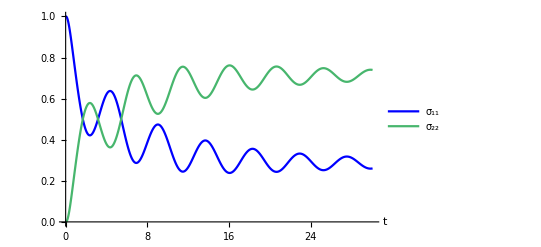

```mathematica
ListPlot[{σCMsite11Data,σCMsite22Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style[" σ_11 ",FontFamily->"Times New Roman"],Style[" σ_22 ",FontFamily->"Times New Roman"]}]
```

```mathematica
ReσCMsite12Data=Table[{n dt,Re[σCMsite[n][[1,2]]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.},{0.1,0.00148404},{0.15,0.00441761},{0.2,0.00871688},{0.25,0.0142584},{0.3,0.0208922},{0.35,0.0284559},{0.4,0.0367876},{0.45,0.045736},{0.5,0.0551671},{0.55,0.0649667},{0.6,0.075041},{0.65,0.0853142},{0.7,0.0957255},{0.75,0.106225},{0.8,0.116772},{0.85,0.127328},{0.9,0.137859},{0.95,0.148331},{1.,0.158707},{1.05,0.168953},{1.1,0.179029},{1.15,0.188896},{1.2,0.198512},{1.25,0.207834},{1.3,0.21682},{1.35,0.225426},{1.4,0.233609},{1.45,0.241326},{1.5,0.248537},{1.55,0.255203},{1.6,0.261284},{1.65,0.266748},{1.7,0.271561},{1.75,0.275694},{1.8,0.279119},{1.85,0.281815},{1.9,0.283761},{1.95,0.284941},{2.,0.285341},{2.05,0.284954},{2.1,0.283772},{2.15,0.281795},{2.2,0.279025},{2.25,0.275466},{2.3,0.271128},{2.35,0.266024},{2.4,0.26017},{2.45,0.253585},{2.5,0.246293},{2.55,0.238318},{2.6,0.22969},{2.65,0.220441},{2.7,0.210605},{2.75,0.200219},{2.8,0.189322},{2.85,0.177956},{2.9,0.166164},{2.95,0.15399},{3.,0.141482},{3.05,0.128688},{3.1,0.115655},{3.15,0.102435},{3.2,0.0890764},{3.25,0.0756307},{3.3,0.0621487},{3.35,0.0486809},{3.4,0.0352778},{3.45,0.0219891},{3.5,0.00886391},{3.55,-0.00404985},{3.6,-0.0167053},{3.65,-0.0290572},{3.7,-0.0410616},{3.75,-0.0526767},{3.8,-0.0638624},{3.85,-0.0745811},{3.9,-0.084797},{3.95,-0.0944774},{4.,-0.103592},{4.05,-0.112112},{4.1,-0.120014},{4.15,-0.127275},{4.2,-0.133877},{4.25,-0.139803},{4.3,-0.145042},{4.35,-0.149582},{4.4,-0.153419},{4.45,-0.156548},{4.5,-0.15897},{4.55,-0.160688},{4.6,-0.161709},{4.65,-0.162041},{4.7,-0.161698},{4.75,-0.160694},{4.8,-0.159048},{4.85,-0.156781},{4.9,-0.153917},{4.95,-0.150481},{5.,-0.146502},{5.05,-0.142011},{5.1,-0.137041},{5.15,-0.131626},{5.2,-0.125804},{5.25,-0.119611},{5.3,-0.113088},{5.35,-0.106274},{5.4,-0.0992127},{5.45,-0.0919447},{5.5,-0.0845135},{5.55,-0.0769625},{5.6,-0.069335},{5.65,-0.0616746},{5.7,-0.0540245},{5.75,-0.0464275},{5.8,-0.038926},{5.85,-0.0315612},{5.9,-0.0243737},{5.95,-0.0174027},{6.,-0.0106862},{6.05,-0.00426044},{6.1,0.00183969},{6.15,0.00758131},{6.2,0.0129334},{6.25,0.0178671},{6.3,0.0223557},{6.35,0.0263749},{6.4,0.0299025},{6.45,0.0329193},{6.5,0.0354082},{6.55,0.0373549},{6.6,0.0387479},{6.65,0.0395782},{6.7,0.0398397},{6.75,0.0395289},{6.8,0.0386451},{6.85,0.0371904},{6.9,0.0351694},{6.95,0.0325896},{7.,0.0294609},{7.05,0.0257959},{7.1,0.0216094},{7.15,0.0169189},{7.2,0.0117439},{7.25,0.00610627},{7.3,0.0000298531},{7.35,-0.0064596},{7.4,-0.0133345},{7.45,-0.0205656},{7.5,-0.0281223},{7.55,-0.0359723},{7.6,-0.0440825},{7.65,-0.0524185},{7.7,-0.0609451},{7.75,-0.0696264},{7.8,-0.0784261},{7.85,-0.0873073},{7.9,-0.0962332},{7.95,-0.105167},{8.,-0.114071},{8.05,-0.12291},{8.1,-0.131648},{8.15,-0.140248},{8.2,-0.148678},{8.25,-0.156902},{8.3,-0.16489},{8.35,-0.17261},{8.4,-0.180032},{8.45,-0.187128},{8.5,-0.193872},{8.55,-0.200239},{8.6,-0.206206},{8.65,-0.211753},{8.7,-0.21686},{8.75,-0.221511},{8.8,-0.225692},{8.85,-0.229389},{8.9,-0.232595},{8.95,-0.235299},{9.,-0.237498},{9.05,-0.239189},{9.1,-0.24037},{9.15,-0.241044},{9.2,-0.241215},{9.25,-0.240888},{9.3,-0.240073},{9.35,-0.23878},{9.4,-0.237022},{9.45,-0.234813},{9.5,-0.232171},{9.55,-0.229115},{9.6,-0.225664},{9.65,-0.221842},{9.7,-0.21767},{9.75,-0.213176},{9.8,-0.208384},{9.85,-0.203323},{9.9,-0.198021},{9.95,-0.192508},{10.,-0.186813},{10.05,-0.180969},{10.1,-0.175005},{10.15,-0.168954},{10.2,-0.162847},{10.25,-0.156716},{10.3,-0.150594},{10.35,-0.14451},{10.4,-0.138497},{10.45,-0.132584},{10.5,-0.126802},{10.55,-0.121179},{10.6,-0.115743},{10.65,-0.110521},{10.7,-0.105538},{10.75,-0.10082},{10.8,-0.0963877},{10.85,-0.0922638},{10.9,-0.0884679},{10.95,-0.085018},{11.,-0.0819305},{11.05,-0.0792199},{11.1,-0.0768988},{11.15,-0.0749781},{11.2,-0.0734664},{11.25,-0.0723706},{11.3,-0.0716955},{11.35,-0.0714438},{11.4,-0.0716163},{11.45,-0.0722119},{11.5,-0.0732272},{11.55,-0.0746572},{11.6,-0.0764948},{11.65,-0.078731},{11.7,-0.081355},{11.75,-0.0843544},{11.8,-0.087715},{11.85,-0.091421},{11.9,-0.0954551},{11.95,-0.0997984},{12.,-0.104431},{12.05,-0.109332},{12.1,-0.114478},{12.15,-0.119846},{12.2,-0.125411},{12.25,-0.13115},{12.3,-0.137035},{12.35,-0.143041},{12.4,-0.14914},{12.45,-0.155306},{12.5,-0.161512},{12.55,-0.167731},{12.6,-0.173935},{12.65,-0.180098},{12.7,-0.186192},{12.75,-0.192193},{12.8,-0.198075},{12.85,-0.203813},{12.9,-0.209383},{12.95,-0.214763},{13.,-0.219929},{13.05,-0.224862},{13.1,-0.229542},{13.15,-0.233951},{13.2,-0.238071},{13.25,-0.241887},{13.3,-0.245385},{13.35,-0.248552},{13.4,-0.251379},{13.45,-0.253854},{13.5,-0.255972},{13.55,-0.257725},{13.6,-0.259111},{13.65,-0.260126},{13.7,-0.260769},{13.75,-0.261043},{13.8,-0.260948},{13.85,-0.260491},{13.9,-0.259677},{13.95,-0.258513},{14.,-0.257009},{14.05,-0.255175},{14.1,-0.253024},{14.15,-0.250569},{14.2,-0.247825},{14.25,-0.244808},{14.3,-0.241535},{14.35,-0.238025},{14.4,-0.234297},{14.45,-0.23037},{14.5,-0.226266},{14.55,-0.222006},{14.6,-0.217613},{14.65,-0.213108},{14.7,-0.208516},{14.75,-0.203859},{14.8,-0.19916},{14.85,-0.194442},{14.9,-0.18973},{14.95,-0.185046},{15.,-0.180413},{15.05,-0.175853},{15.1,-0.171388},{15.15,-0.167039},{15.2,-0.162828},{15.25,-0.158773},{15.3,-0.154894},{15.35,-0.151208},{15.4,-0.147733},{15.45,-0.144485},{15.5,-0.141477},{15.55,-0.138724},{15.6,-0.136238},{15.65,-0.134029},{15.7,-0.132107},{15.75,-0.130481},{15.8,-0.129155},{15.85,-0.128137},{15.9,-0.127429},{15.95,-0.127034},{16.,-0.126952},{16.05,-0.127183},{16.1,-0.127724},{16.15,-0.128573},{16.2,-0.129723},{16.25,-0.131168},{16.3,-0.132901},{16.35,-0.134913},{16.4,-0.137193},{16.45,-0.13973},{16.5,-0.142511},{16.55,-0.145523},{16.6,-0.148751},{16.65,-0.152179},{16.7,-0.15579},{16.75,-0.159569},{16.8,-0.163497},{16.85,-0.167555},{16.9,-0.171725},{16.95,-0.175987},{17.,-0.180322},{17.05,-0.184709},{17.1,-0.18913},{17.15,-0.193564},{17.2,-0.197991},{17.25,-0.202391},{17.3,-0.206744},{17.35,-0.211033},{17.4,-0.215237},{17.45,-0.21934},{17.5,-0.223322},{17.55,-0.227167},{17.6,-0.230859},{17.65,-0.234382},{17.7,-0.237722},{17.75,-0.240866},{17.8,-0.2438},{17.85,-0.246513},{17.9,-0.248995},{17.95,-0.251236},{18.,-0.253228},{18.05,-0.254964},{18.1,-0.256439},{18.15,-0.257648},{18.2,-0.258588},{18.25,-0.259256},{18.3,-0.259653},{18.35,-0.259779},{18.4,-0.259635},{18.45,-0.259225},{18.5,-0.258552},{18.55,-0.257624},{18.6,-0.256445},{18.65,-0.255024},{18.7,-0.253369},{18.75,-0.251491},{18.8,-0.2494},{18.85,-0.247108},{18.9,-0.244627},{18.95,-0.241971},{19.,-0.239153},{19.05,-0.236189},{19.1,-0.233094},{19.15,-0.229883},{19.2,-0.226573},{19.25,-0.223181},{19.3,-0.219722},{19.35,-0.216215},{19.4,-0.212675},{19.45,-0.209121},{19.5,-0.20557},{19.55,-0.202038},{19.6,-0.198542},{19.65,-0.195099},{19.7,-0.191725},{19.75,-0.188436},{19.8,-0.185246},{19.85,-0.18217},{19.9,-0.179223},{19.95,-0.176417},{20.,-0.173765},{20.05,-0.17128},{20.1,-0.168971},{20.15,-0.166848},{20.2,-0.164922},{20.25,-0.163199},{20.3,-0.161687},{20.35,-0.160393},{20.4,-0.15932},{20.45,-0.158473},{20.5,-0.157854},{20.55,-0.157467},{20.6,-0.15731},{20.65,-0.157384},{20.7,-0.157687},{20.75,-0.158217},{20.8,-0.15897},{20.85,-0.159941},{20.9,-0.161125},{20.95,-0.162516},{21.,-0.164105},{21.05,-0.165885},{21.1,-0.167846},{21.15,-0.169979},{21.2,-0.172272},{21.25,-0.174715},{21.3,-0.177295},{21.35,-0.179999},{21.4,-0.182816},{21.45,-0.18573},{21.5,-0.188729},{21.55,-0.191798},{21.6,-0.194923},{21.65,-0.198089},{21.7,-0.201281},{21.75,-0.204486},{21.8,-0.207687},{21.85,-0.210871},{21.9,-0.214024},{21.95,-0.217131},{22.,-0.220177},{22.05,-0.223151},{22.1,-0.226039},{22.15,-0.228828},{22.2,-0.231506},{22.25,-0.234062},{22.3,-0.236485},{22.35,-0.238765},{22.4,-0.240892},{22.45,-0.242859},{22.5,-0.244657},{22.55,-0.246279},{22.6,-0.247719},{22.65,-0.248972},{22.7,-0.250034},{22.75,-0.250901},{22.8,-0.251571},{22.85,-0.252042},{22.9,-0.252313},{22.95,-0.252386},{23.,-0.25226},{23.05,-0.251939},{23.1,-0.251425},{23.15,-0.250723},{23.2,-0.249836},{23.25,-0.248771},{23.3,-0.247534},{23.35,-0.246132},{23.4,-0.244572},{23.45,-0.242865},{23.5,-0.241017},{23.55,-0.23904},{23.6,-0.236944},{23.65,-0.234739},{23.7,-0.232436},{23.75,-0.230048},{23.8,-0.227585},{23.85,-0.22506},{23.9,-0.222486},{23.95,-0.219875},{24.,-0.217239},{24.05,-0.214592},{24.1,-0.211945},{24.15,-0.209311},{24.2,-0.206703},{24.25,-0.204132},{24.3,-0.201611},{24.35,-0.199151},{24.4,-0.196763},{24.45,-0.194459},{24.5,-0.192248},{24.55,-0.19014},{24.6,-0.188145},{24.65,-0.186271},{24.7,-0.184526},{24.75,-0.182918},{24.8,-0.181454},{24.85,-0.180139},{24.9,-0.178979},{24.95,-0.177979},{25.,-0.177141},{25.05,-0.17647},{25.1,-0.175967},{25.15,-0.175633},{25.2,-0.17547},{25.25,-0.175476},{25.3,-0.175652},{25.35,-0.175995},{25.4,-0.176502},{25.45,-0.177171},{25.5,-0.177997},{25.55,-0.178976},{25.6,-0.180102},{25.65,-0.181369},{25.7,-0.18277},{25.75,-0.184299},{25.8,-0.185947},{25.85,-0.187706},{25.9,-0.189567},{25.95,-0.191521},{26.,-0.193559},{26.05,-0.195671},{26.1,-0.197846},{26.15,-0.200074},{26.2,-0.202345},{26.25,-0.204647},{26.3,-0.20697},{26.35,-0.209304},{26.4,-0.211637},{26.45,-0.213959},{26.5,-0.216259},{26.55,-0.218527},{26.6,-0.220752},{26.65,-0.222924},{26.7,-0.225035},{26.75,-0.227075},{26.8,-0.229034},{26.85,-0.230904},{26.9,-0.232678},{26.95,-0.234348},{27.,-0.235906},{27.05,-0.237348},{27.1,-0.238666},{27.15,-0.239855},{27.2,-0.240911},{27.25,-0.241831},{27.3,-0.24261},{27.35,-0.243246},{27.4,-0.243738},{27.45,-0.244084},{27.5,-0.244283},{27.55,-0.244336},{27.6,-0.244244},{27.65,-0.244008},{27.7,-0.243629},{27.75,-0.243112},{27.8,-0.242459},{27.85,-0.241675},{27.9,-0.240763},{27.95,-0.23973},{28.,-0.238581},{28.05,-0.237322},{28.1,-0.235959},{28.15,-0.234501},{28.2,-0.232954},{28.25,-0.231326},{28.3,-0.229625},{28.35,-0.227861},{28.4,-0.226041},{28.45,-0.224175},{28.5,-0.222271},{28.55,-0.220339},{28.6,-0.218388},{28.65,-0.216427},{28.7,-0.214466},{28.75,-0.212514},{28.8,-0.210579},{28.85,-0.208671},{28.9,-0.206799},{28.95,-0.204971},{29.,-0.203195},{29.05,-0.20148},{29.1,-0.199832},{29.15,-0.19826},{29.2,-0.19677},{29.25,-0.195368},{29.3,-0.194061},{29.35,-0.192854},{29.4,-0.191753},{29.45,-0.19076},{29.5,-0.189882},{29.55,-0.18912},{29.6,-0.188478},{29.65,-0.187958},{29.7,-0.187562},{29.75,-0.18729},{29.8,-0.187144},{29.85,-0.187123},{29.9,-0.187226},{29.95,-0.187453},{30.,-0.187801},{30.05,-0.188268}}

```mathematica
ImσCMsite12Data=Table[{n dt,Im[σCMsite[n][[1,2]]]},{n,0,Nt+1}]
```

{{0.,0},{0.05,0.025},{0.1,0.049931},{0.15,0.0744526},{0.2,0.098248},{0.25,0.121041},{0.3,0.142605},{0.35,0.162772},{0.4,0.181427},{0.45,0.198502},{0.5,0.213968},{0.55,0.227826},{0.6,0.240092},{0.65,0.250799},{0.7,0.259981},{0.75,0.267676},{0.8,0.273919},{0.85,0.278745},{0.9,0.282184},{0.95,0.284268},{1.,0.285024},{1.05,0.284482},{1.1,0.282669},{1.15,0.279616},{1.2,0.275355},{1.25,0.269922},{1.3,0.263353},{1.35,0.25569},{1.4,0.246978},{1.45,0.237263},{1.5,0.226598},{1.55,0.215038},{1.6,0.202639},{1.65,0.189463},{1.7,0.175575},{1.75,0.16104},{1.8,0.145927},{1.85,0.130308},{1.9,0.114256},{1.95,0.0978435},{2.,0.0811469},{2.05,0.0642421},{2.1,0.0472058},{2.15,0.0301144},{2.2,0.0130445},{2.25,-0.00392799},{2.3,-0.0207282},{2.35,-0.0372823},{2.4,-0.0535182},{2.45,-0.0693655},{2.5,-0.0847561},{2.55,-0.0996243},{2.6,-0.113907},{2.65,-0.127545},{2.7,-0.140481},{2.75,-0.152663},{2.8,-0.16404},{2.85,-0.174568},{2.9,-0.184205},{2.95,-0.192914},{3.,-0.200664},{3.05,-0.207425},{3.1,-0.213175},{3.15,-0.217895},{3.2,-0.221571},{3.25,-0.224195},{3.3,-0.225763},{3.35,-0.226274},{3.4,-0.225736},{3.45,-0.224157},{3.5,-0.221554},{3.55,-0.217945},{3.6,-0.213355},{3.65,-0.207813},{3.7,-0.20135},{3.75,-0.194003},{3.8,-0.185812},{3.85,-0.176822},{3.9,-0.16708},{3.95,-0.156635},{4.,-0.145542},{4.05,-0.133856},{4.1,-0.121635},{4.15,-0.10894},{4.2,-0.095832},{4.25,-0.0823753},{4.3,-0.0686344},{4.35,-0.0546747},{4.4,-0.0405623},{4.45,-0.0263635},{4.5,-0.0121446},{4.55,0.00202859},{4.6,0.0160908},{4.65,0.0299778},{4.7,0.0436266},{4.75,0.0569757},{4.8,0.0699654},{4.85,0.0825382},{4.9,0.0946387},{4.95,0.106214},{5.,0.117215},{5.05,0.127594},{5.1,0.137308},{5.15,0.146315},{5.2,0.15458},{5.25,0.16207},{5.3,0.168754},{5.35,0.174608},{5.4,0.17961},{5.45,0.183743},{5.5,0.186994},{5.55,0.189354},{5.6,0.190818},{5.65,0.191385},{5.7,0.191059},{5.75,0.189848},{5.8,0.187764},{5.85,0.184822},{5.9,0.181041},{5.95,0.176446},{6.,0.171062},{6.05,0.164921},{6.1,0.158056},{6.15,0.150503},{6.2,0.142303},{6.25,0.133499},{6.3,0.124134},{6.35,0.114257},{6.4,0.103916},{6.45,0.0931636},{6.5,0.0820515},{6.55,0.070634},{6.6,0.0589661},{6.65,0.0471039},{6.7,0.0351035},{6.75,0.0230218},{6.8,0.0109153},{6.85,-0.00115968},{6.9,-0.0131472},{6.95,-0.0249922},{7.,-0.0366407},{7.05,-0.04804},{7.1,-0.0591388},{7.15,-0.0698876},{7.2,-0.0802389},{7.25,-0.0901473},{7.3,-0.0995699},{7.35,-0.108466},{7.4,-0.116798},{7.45,-0.124531},{7.5,-0.131634},{7.55,-0.138077},{7.6,-0.143834},{7.65,-0.148885},{7.7,-0.15321},{7.75,-0.156794},{7.8,-0.159626},{7.85,-0.161696},{7.9,-0.163002},{7.95,-0.163542},{8.,-0.163318},{8.05,-0.162337},{8.1,-0.160608},{8.15,-0.158145},{8.2,-0.154964},{8.25,-0.151085},{8.3,-0.146529},{8.35,-0.141324},{8.4,-0.135497},{8.45,-0.12908},{8.5,-0.122106},{8.55,-0.114612},{8.6,-0.106636},{8.65,-0.0982183},{8.7,-0.0894008},{8.75,-0.0802273},{8.8,-0.0707427},{8.85,-0.0609932},{8.9,-0.0510259},{8.95,-0.0408885},{9.,-0.0306292},{9.05,-0.0202965},{9.1,-0.00993894},{9.15,0.000395276},{9.2,0.0106583},{9.25,0.0208029},{9.3,0.0307827},{9.35,0.0405526},{9.4,0.0500686},{9.45,0.059288},{9.5,0.0681702},{9.55,0.0766761},{9.6,0.0847688},{9.65,0.0924134},{9.7,0.0995773},{9.75,0.106231},{9.8,0.112346},{9.85,0.117898},{9.9,0.122865},{9.95,0.127229},{10.,0.130971},{10.05,0.134081},{10.1,0.136546},{10.15,0.138361},{10.2,0.139521},{10.25,0.140024},{10.3,0.139874},{10.35,0.139075},{10.4,0.137635},{10.45,0.135565},{10.5,0.13288},{10.55,0.129595},{10.6,0.125729},{10.65,0.121306},{10.7,0.116348},{10.75,0.110884},{10.8,0.10494},{10.85,0.0985488},{10.9,0.0917424},{10.95,0.0845553},{11.,0.0770234},{11.05,0.0691839},{11.1,0.0610755},{11.15,0.0527375},{11.2,0.0442102},{11.25,0.0355345},{11.3,0.0267517},{11.35,0.0179033},{11.4,0.00903082},{11.45,0.000175686},{11.5,-0.0086211},{11.55,-0.0173191},{11.6,-0.0258785},{11.65,-0.0342604},{11.7,-0.0424273},{11.75,-0.0503424},{11.8,-0.0579708},{11.85,-0.0652789},{11.9,-0.072235},{11.95,-0.0788089},{12.,-0.0849729},{12.05,-0.0907008},{12.1,-0.0959692},{12.15,-0.100756},{12.2,-0.105044},{12.25,-0.108814},{12.3,-0.112054},{12.35,-0.114752},{12.4,-0.116898},{12.45,-0.118487},{12.5,-0.119515},{12.55,-0.119981},{12.6,-0.119886},{12.65,-0.119235},{12.7,-0.118034},{12.75,-0.116293},{12.8,-0.114023},{12.85,-0.111239},{12.9,-0.107956},{12.95,-0.104194},{13.,-0.0999722},{13.05,-0.0953146},{13.1,-0.0902451},{13.15,-0.0847902},{13.2,-0.0789778},{13.25,-0.0728371},{13.3,-0.066399},{13.35,-0.0596954},{13.4,-0.0527591},{13.45,-0.0456239},{13.5,-0.0383244},{13.55,-0.0308955},{13.6,-0.0233725},{13.65,-0.0157912},{13.7,-0.00818699},{13.75,-0.000595469},{13.8,0.0069482},{13.85,0.0144093},{13.9,0.0217537},{13.95,0.0289481},{14.,0.03596},{14.05,0.0427581},{14.1,0.0493123},{14.15,0.0555936},{14.2,0.0615748},{14.25,0.0672301},{14.3,0.0725353},{14.35,0.0774681},{14.4,0.0820081},{14.45,0.0861369},{14.5,0.0898379},{14.55,0.0930969},{14.6,0.0959017},{14.65,0.0982422},{14.7,0.100111},{14.75,0.101502},{14.8,0.102412},{14.85,0.10284},{14.9,0.102787},{14.95,0.102258},{15.,0.101256},{15.05,0.0997913},{15.1,0.0978724},{15.15,0.0955115},{15.2,0.0927227},{15.25,0.0895216},{15.3,0.0859259},{15.35,0.081955},{15.4,0.0776297},{15.45,0.0729726},{15.5,0.0680075},{15.55,0.0627595},{15.6,0.0572549},{15.65,0.0515209},{15.7,0.0455858},{15.75,0.0394783},{15.8,0.0332282},{15.85,0.0268653},{15.9,0.02042},{15.95,0.0139227},{16.,0.00740401},{16.05,0.00089434},{16.1,-0.00557613},{16.15,-0.0119776},{16.2,-0.0182808},{16.25,-0.0244571},{16.3,-0.0304786},{16.35,-0.0363184},{16.4,-0.0419506},{16.45,-0.0473503},{16.5,-0.0524941},{16.55,-0.0573598},{16.6,-0.0619266},{16.65,-0.0661752},{16.7,-0.0700881},{16.75,-0.0736493},{16.8,-0.0768446},{16.85,-0.0796617},{16.9,-0.0820898},{16.95,-0.0841204},{17.,-0.0857466},{17.05,-0.0869636},{17.1,-0.0877685},{17.15,-0.0881603},{17.2,-0.0881398},{17.25,-0.08771},{17.3,-0.0868755},{17.35,-0.0856429},{17.4,-0.0840207},{17.45,-0.0820188},{17.5,-0.0796493},{17.55,-0.0769255},{17.6,-0.0738623},{17.65,-0.0704765},{17.7,-0.0667857},{17.75,-0.0628092},{17.8,-0.0585673},{17.85,-0.0540816},{17.9,-0.0493745},{17.95,-0.0444693},{18.,-0.0393901},{18.05,-0.0341618},{18.1,-0.0288095},{18.15,-0.023359},{18.2,-0.0178363},{18.25,-0.0122674},{18.3,-0.00667865},{18.35,-0.00109605},{18.4,0.0044545},{18.45,0.0099474},{18.5,0.0153575},{18.55,0.0206603},{18.6,0.0258318},{18.65,0.0308488},{18.7,0.0356892},{18.75,0.0403315},{18.8,0.0447555},{18.85,0.0489421},{18.9,0.0528735},{18.95,0.0565331},{19.,0.0599057},{19.05,0.0629775},{19.1,0.0657362},{19.15,0.0681712},{19.2,0.0702733},{19.25,0.0720348},{19.3,0.07345},{19.35,0.0745145},{19.4,0.0752257},{19.45,0.0755827},{19.5,0.0755861},{19.55,0.0752384},{19.6,0.0745433},{19.65,0.0735066},{19.7,0.0721353},{19.75,0.0704379},{19.8,0.0684246},{19.85,0.0661068},{19.9,0.0634973},{19.95,0.0606101},{20.,0.0574605},{20.05,0.054065},{20.1,0.0504408},{20.15,0.0466064},{20.2,0.042581},{20.25,0.0383845},{20.3,0.0340376},{20.35,0.0295615},{20.4,0.0249778},{20.45,0.0203086},{20.5,0.0155761},{20.55,0.0108027},{20.6,0.00601092},{20.65,0.00122306},{20.7,-0.00353861},{20.75,-0.00825217},{20.8,-0.012896},{20.85,-0.0174491},{20.9,-0.0218907},{20.95,-0.0262012},{21.,-0.0303612},{21.05,-0.0343524},{21.1,-0.0381575},{21.15,-0.0417601},{21.2,-0.0451446},{21.25,-0.0482968},{21.3,-0.0512037},{21.35,-0.0538534},{21.4,-0.0562352},{21.45,-0.0583399},{21.5,-0.0601596},{21.55,-0.0616876},{21.6,-0.0629189},{21.65,-0.0638497},{21.7,-0.0644776},{21.75,-0.0648017},{21.8,-0.0648227},{21.85,-0.0645423},{21.9,-0.0639639},{21.95,-0.0630922},{22.,-0.0619332},{22.05,-0.0604941},{22.1,-0.0587835},{22.15,-0.0568113},{22.2,-0.0545881},{22.25,-0.0521262},{22.3,-0.0494384},{22.35,-0.0465389},{22.4,-0.0434424},{22.45,-0.0401646},{22.5,-0.0367221},{22.55,-0.0331318},{22.6,-0.0294115},{22.65,-0.0255793},{22.7,-0.0216537},{22.75,-0.0176537},{22.8,-0.0135982},{22.85,-0.00950658},{22.9,-0.00539797},{22.95,-0.00129161},{23.,0.00279344},{23.05,0.00683833},{23.1,0.0108245},{23.15,0.014734},{23.2,0.0185489},{23.25,0.0222523},{23.3,0.0258277},{23.35,0.0292593},{23.4,0.0325321},{23.45,0.035632},{23.5,0.0385458},{23.55,0.041261},{23.6,0.0437665},{23.65,0.046052},{23.7,0.0481084},{23.75,0.0499275},{23.8,0.0515026},{23.85,0.052828},{23.9,0.053899},{23.95,0.0547126},{24.,0.0552665},{24.05,0.0555599},{24.1,0.0555933},{24.15,0.0553682},{24.2,0.0548873},{24.25,0.0541546},{24.3,0.0531752},{24.35,0.0519552},{24.4,0.050502},{24.45,0.0488238},{24.5,0.0469299},{24.55,0.0448305},{24.6,0.0425369},{24.65,0.0400609},{24.7,0.0374152},{24.75,0.0346133},{24.8,0.0316692},{24.85,0.0285976},{24.9,0.0254135},{24.95,0.0221325},{25.,0.0187705},{25.05,0.0153437},{25.1,0.0118684},{25.15,0.008361},{25.2,0.00483813},{25.25,0.00131621},{25.3,-0.0021884},{25.35,-0.00565954},{25.4,-0.00908129},{25.45,-0.0124381},{25.5,-0.0157148},{25.55,-0.0188967},{25.6,-0.0219696},{25.65,-0.02492},{25.7,-0.027735},{25.75,-0.0304025},{25.8,-0.0329109},{25.85,-0.0352497},{25.9,-0.0374093},{25.95,-0.0393806},{26.,-0.0411559},{26.05,-0.0427282},{26.1,-0.0440914},{26.15,-0.0452408},{26.2,-0.0461723},{26.25,-0.0468832},{26.3,-0.0473714},{26.35,-0.0476364},{26.4,-0.0476782},{26.45,-0.0474983},{26.5,-0.0470988},{26.55,-0.0464832},{26.6,-0.0456558},{26.65,-0.0446217},{26.7,-0.0433871},{26.75,-0.0419593},{26.8,-0.0403459},{26.85,-0.0385559},{26.9,-0.0365986},{26.95,-0.0344843},{27.,-0.0322238},{27.05,-0.0298286},{27.1,-0.0273108},{27.15,-0.0246829},{27.2,-0.0219577},{27.25,-0.0191487},{27.3,-0.0162694},{27.35,-0.0133336},{27.4,-0.0103554},{27.45,-0.0073489},{27.5,-0.00432825},{27.55,-0.00130758},{27.6,0.00169908},{27.65,0.00467785},{27.7,0.00761507},{27.75,0.0104974},{27.8,0.0133118},{27.85,0.0160456},{27.9,0.0186866},{27.95,0.0212233},{28.,0.0236446},{28.05,0.0259398},{28.1,0.0280993},{28.15,0.0301139},{28.2,0.0319752},{28.25,0.0336755},{28.3,0.0352081},{28.35,0.0365669},{28.4,0.0377467},{28.45,0.0387434},{28.5,0.0395534},{28.55,0.0401743},{28.6,0.0406043},{28.65,0.0408429},{28.7,0.0408901},{28.75,0.0407471},{28.8,0.0404157},{28.85,0.0398987},{28.9,0.0391997},{28.95,0.0383233},{29.,0.0372747},{29.05,0.0360599},{29.1,0.0346856},{29.15,0.0331593},{29.2,0.031489},{29.25,0.0296836},{29.3,0.0277523},{29.35,0.0257049},{29.4,0.0235517},{29.45,0.0213034},{29.5,0.018971},{29.55,0.016566},{29.6,0.0141001},{29.65,0.011585},{29.7,0.00903283},{29.75,0.00645567},{29.8,0.00386565},{29.85,0.00127489},{29.9,-0.00130456},{29.95,-0.0038608},{30.,-0.0063821},{30.05,-0.00885698}}

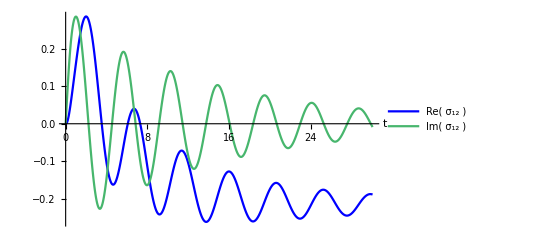

```mathematica
ListPlot[{ReσCMsite12Data,ImσCMsite12Data},PlotStyle->{Blue,RGBColor[0.28026441037696703,0.715,0.4292089322474965]},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style[" Re( σ_12 ) ",FontFamily->"Times New Roman"],Style[" Im( σ_12 ) ",FontFamily->"Times New Roman"]}]
```

### RT v.s. CMRT numerical computation

Site population

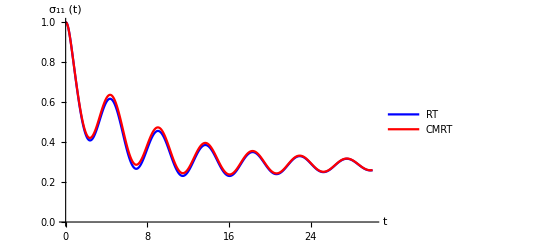

```mathematica
ListPlot[{σsite11Data,σCMsite11Data},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14],Style["σ_11 (t)",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style[" RT ",FontFamily->"Times New Roman"],Style[" CMRT ",FontFamily->"Times New Roman"]},PlotStyle->{Blue,Red}]
```

Exciton population

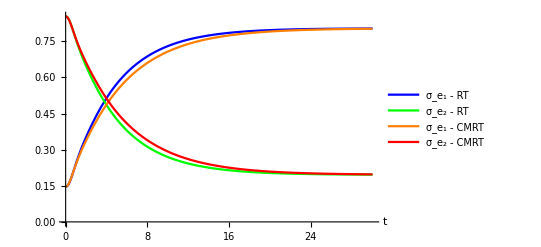

```mathematica
ListPlot[{σ11Data,σ22Data,σCM11Data,σCM22Data},PlotStyle->{Blue,Green,Orange,Red},Joined->True,PlotRange->All,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style[" σ_e_1 - RT ",FontFamily->"Times New Roman"],Style[" σ_e_2 - RT ",FontFamily->"Times New Roman"],Style[" σ_e_1 - CMRT ",FontFamily->"Times New Roman"],Style[" σ_e_2 - CMRT ",FontFamily->"Times New Roman"]}]
```